# Bayesians Commit the Gambler’s Fallacy Kevin Dorst MIT December 2023

## Introduction

This notebook contains all code needed to generate results from the September 2023 version of “Bayesians Commit the Gambler’s Fallacy”.

Please run the “Loading Functions (run this first!)” section before proceeding, as it will initialize all functions needed for the rest of the notebook.

The rest of this notebook follows the order of the paper.  Most of the paper focuses on “streak chains”, wherein once a streak is broken the probabilities are set back to (near) 50% of each outcome.  Later sections of the notebook show that the results are robust to variations, as discussed in the Objections section of the paper.

Some conventions:
1) I will use 1 for heads (or success) and 0 for tails (or failure) throughout. Sequences are lists, so the sequence HTHHT is represented {1,0,1,1,0}
2) In stochastic matrices of size N, I will use the first 1,2,...N/2 states to represent states in which the previous toss was a tails (0), and states N/2+1, N/2 + 2,..., N to represent states in which the previous toss was a heads (1).  Thus the following represents an (streak) 2-step Switchy_70% process:
{{0.3,0,0.7,0},
{0.4,0,0.6,0},
{0,0.6,0,0.4},
{0,0.7,0,0.3}}
Label the four states in this chain 1,2,3, and 4 respectively.  The chain is in state 1 when it has previously landed TT, in state 2 when it has landed HT, state 3 when it has landed TH, and state 4 when it has landed HH.
Initial states are randomly selected from the middle two—in this case, 2 and 3. Thus the sequence HTHHT, i.e. {1,0,1,1,0,0}, would:
- If initialized in state 2, take this chain through states {3,2,3,4,2,1}
- If initialized in state 3, take this chain through states {4,2,3,4,2,1}

## Loading Functions (run this first!)

### Manipulating Sequences

```mathematica
(*to calculate simple confidence intervals etc:*)
Needs["HypothesisTesting`"]
```

```mathematica
(*This function takes a sequence of coin flips (Heads and Tails represented by 1s and 0s) and returns the pairs of adjacent coin flips in the sequence.For example:Given the sequence {1,0,1,0},The function will return:{{1,0},{0,1},{1,0}}*)

getPairs[seq_]:=(pairs={};(*Initialize an empty list to store the pairs*)(*Loop through the sequence until the second last element*)Do[AppendTo[pairs,{seq[[num]],seq[[num+1]]}],{num,Length[seq]-1}];
Return[pairs] (*Return the list of pairs*))
```

```mathematica
(*This function takes a list of pairs (from the getPairs function) and counts how many times there's a switch (from 1 to 0 or from 0 to 1) and how many times there's a stick (from 1 to 1 or from 0 to 0).For example:Given the pairs {{1,0},{0,1},{1,0}},The function will return:{0,3} (0 sticks and 3 switches)*)
count[pairs_]:=(switches=0;(*Initialize a counter for switches*)sticks=0;(*Initialize a counter for sticks*)(*Loop through the list of pairs*)Do[(*If the two elements of a pair are the same,increment the sticks counter,else increment the switches counter*)If[pairs[[num,1]]==pairs[[num,2]],sticks+=1,switches+=1],{num,Length[pairs]}];
Return[{sticks,switches}] (*Return the counts of sticks and switches*))
```

```mathematica
(*Given a sequence, get the number of switches:*)
getNumSwitches[seq_]:=Total[Table[Boole[seq[[ind]]!=seq[[ind+1]]],{ind,1,Length[seq]-1}]]
```

### Instant-fall (Streak) chains

```mathematica
(*This function generates a Markov chain matrix for a process that either becomes "Sticky" or "Switchy" as the number of consistent outcomes increases.
-finProb:The final probability of continuing the same outcome.
-numSteps:The number of steps or outcomes to consider.

For example: Given finProb=0.7 and numSteps=2, the function will return a Markov chain that represents a "Sticky" behavior that builds up to a 70% chance of continuing the same outcome after 2 consistent outcomes.*)

getChain[finProb_,numSteps_]:=((*Initialize a square matrix of zeroes*)chain=Table[Table[0,2*numSteps],2*numSteps];
(*Set the final probabilities for the end states*)chain=ReplacePart[chain,{{1,1}->finProb,{1,numSteps+1}->1-finProb}];
chain=ReplacePart[chain,{{-1,-1}->finProb,{-1,numSteps}->1-finProb}];
(*Calculate and set the transition probabilities for each step*)Do[step=num;
prob=0.5+((finProb-0.5)*step/numSteps);
chain=ReplacePart[chain,{{numSteps-step+1,numSteps-step}->prob,{numSteps-step+1,numSteps+1}->1-prob}];
chain=ReplacePart[chain,{{numSteps+step,numSteps+step+1}->prob,{numSteps+step,numSteps}->1-prob}];,{num,numSteps-1}];
Return[chain] (*Return the generated Markov chain*))
```

```mathematica
(*For later clarification, remind that getChain is getting an streak chain:*)
getInstantChain=getChain;
```

```mathematica
getSequence[chain_,length_]:=((*Determine the position where transitions for tails (T) and heads (H) start in the chain*)
firstTPos=Length[chain]/2;
firstHPos=Length[chain]/2+1;
(*Randomly select an initial state,either starting with a T or H,based on the probabilities in the chain*)state=state1=RandomChoice[{firstTPos,firstHPos}];
(*Generate a sequence of states based on the probabilities in the chain.Start with the initial state and then for each subsequent state,choose it based on the transition probabilities from the current state in the chain*)stateSeq=Prepend[Table[state=RandomChoice[chain[[state]]->Range[Length[chain]]],length-1],state1];
(*Convert the sequence of states to a sequence of outcomes (0 for T and 1 for H)*)Return[outcomeSeq=stateSeq/. {x_/;x<=firstTPos->0,y_/;y>=firstHPos->1}])
```

```mathematica
(*get the current streak from a given sequence:*)
getCurStreak[seq_]:=(
(*Initialize the current streak length to 1*)
curStr=1;
(*Initialize the current index to the last element in the sequence*)
curInd=1;
(*Continue checking as long as we haven't reached the start of the sequence and the current outcome matches the previous outcome*)While[curInd<Length[seq]&&seq[[-curInd-1]]==seq[[-curInd]],(*If the outcomes match,increase the current streak length*)
curStr+=1;
(*Move to the previous outcome in the sequence*)
curInd+=1;];
(*Return the current streak length*)
Return[curStr])

seq={0,1,1,0,1,1,1};
getCurStreak[seq]
```

3

```mathematica
(*Function to determine the current state in the chain based on a given sequence*)getInstantChainState[chain_,seq_]:=((*If the last outcome in the sequence is a head (1)*)If[seq[[-1]]==1,(*Calculate the state based on the current streak of heads.Make sure the state does not exceed the total number of states in the chain*)state=Min[(Length[chain]/2+getCurStreak[seq]),Length[chain]];];
(*If the last outcome in the sequence is a tail (0)*)If[seq[[-1]]==0,(*Calculate the state based on the current streak of tails.Make sure the state is not below 1*)state=Max[((Length[chain]/2+1)-getCurStreak[seq]),1];];
(*Return the calculated state*)Return[state])

(*Function to calculate the probability of getting a tail based on the current state*)
getProbTails[chain_,state_]:=(*Sum the probabilities of transitioning to a tail state*)Sum[chain[[state,ind]],{ind,Length[chain]/2}]

(*Function to encode a recursive likelihood calculation for a given sequence based on the chain*)
getInstantSeqLikes[fxn_,chain_]:=(Clear[fxn];
(*Set the base probabilities for a single outcome sequence*)fxn[{0}]=0.5;
fxn[{1}]=0.5;
fxn[seq_]:=fxn[seq]=((*If the last outcome in the sequence is a tail (0)*)If[seq[[-1]]==0,(*Return the likelihood by multiplying the probability of the previous sequence with the probability of getting a tail in the current state*)Return[fxn[seq[[;;-2]]]*getProbTails[chain,getInstantChainState[chain,seq[[;;-2]]]]];];
(*If the last outcome in the sequence is a head (1)*)If[seq[[-1]]==1,(*Return the likelihood by multiplying the probability of the previous sequence with the complement of the probability of getting a tail in the current state*)Return[fxn[seq[[;;-2]]]*(1-getProbTails[chain,getInstantChainState[chain,seq[[;;-2]]]])];];))
```

```mathematica
(*Given a sequence likelihood fxn, a length of sequence, and a feature you want those sequences to have (say, total of N 1s), calculate likelihood:*)
Clear[getLikeFeature];
getLikeFeature[seqLikeFxn_,length_,feat_]:=(
seqList=Select[Tuples[{0,1},length],feat];
Return[Sum[seqLikeFxn[ind],{ind,seqList}]];)
```

```mathematica
(*Function to calculate the maximum streak length in a sequence*)getMaxStrLength[seq_]:=((*Initialize the maximum and current streak lengths to 1*)maxStr=1;
curStr=1;
(*Start iterating from the second element in the sequence*)index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Update the maximum streak length if necessary*)maxStr=Max[curStr,maxStr];,(*Reset the current streak length if the streak ends*)curStr=1;];,Length[seq]-1];
(*Return the maximum streak length*)Return[maxStr])


(*Function to calculate the average streak length in a sequence*)
getAvgStrLength[seq_]:=(curStr=1;
(*Initialize an empty list to store individual streak lengths*)strLengths={};
index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];,(*Append the current streak length to the list and reset it*)AppendTo[strLengths,curStr];
curStr=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];];,Length[seq]-1];
(*Return the average streak length*)Return[Mean[strLengths]]//N)


(*Function to calculate the median streak length in a sequence*)
getMedStrLength[seq_]:=(curStr=1;
(*Initialize an empty list to store individual streak lengths*)strLengths={};
index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];,(*Append the current streak length to the list and reset it*)AppendTo[strLengths,curStr];
curStr=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];];,Length[seq]-1];
(*Return the median streak length*)N[Return[Median[strLengths]]])
```

```mathematica
(*Given an streak chain, get a function that recursively calculates the likelihoods of various numbersof heads (k) from various numbers of tosses (n).
NOTE: uses different logic for 1-step and many-step chains, because the former lacks any "middle" states to return to*)

getInstantPropLikelihoods[fxn_,chain_]:=(Clear[fxn];
Module[{size,numSteps},
(*Calculate the size of the chain and the number of steps*)
numSteps=Length[chain]/2;
size=Length[chain];
(*Set the base cases for the recursive function.If either n or k is negative,the probability is 0*)
fxn[n_,k_Integer?Negative,s_]:=0;
fxn[n_Integer?Negative,k_,s_]:=0;

(*Start with a uniform prior.Initially,there's an equal chance of the process starting with either a Head or a Tail*)
fxn[1,1,numSteps+1]:=1/2;
fxn[1,0,numSteps]:=1/2;
(*Check if we're dealing with a 1-step chain*)

If[numSteps==1,(*Logic for 1-step chains *)(*Calculate the probability for n tosses,k Heads,and ending in state 1. We consider the previous state and the probability of transitioning to state 1*)fxn[n_,k_,1]:=fxn[n,k,1]=fxn[n-1,k,1]*chain[[1,1]]+fxn[n-1,k,2]*chain[[2,1]];
(*Similarly,calculate the probability for n tosses,k Heads,and ending in state 2*)fxn[n_,k_,2]:=fxn[n,k,2]=fxn[n-1,k-1,1]*chain[[1,2]]+fxn[n-1,k-1,2]*chain[[2,2]];
,

(*Logic for larger chains*)
(*Handle the edge states (1 and size) separately,as they have different transition dynamics*)fxn[n_,k_,1]:=fxn[n,k,1]=fxn[n-1,k,1]*chain[[1,1]]+fxn[n-1,k,2]*chain[[2,1]];
fxn[n_,k_,size]:=fxn[n,k,size]=fxn[n-1,k-1,size]*chain[[size,size]]+fxn[n-1,k-1,size-1]*chain[[size-1,size]];
(*For the "middle" states,calculate the transition probabilities based on the current state and previous state*)
(*if a streak of T, can only transition from one to the right:*)
fxn[n_,k_,s_Integer?(1<#<numSteps&)]:=fxn[n,k,s]=fxn[n-1,k,s+1]*chain[[s+1,s]];
(*if a streak of H, can only transition from one to the left:*)
fxn[n_,k_,s_Integer?(numSteps+1<#<size&)]:=fxn[n,k,s]=fxn[n-1,k-1,s-1]*chain[[s-1,s]];
(*For starting states,sum the probabilities of transitioning from all possible previous states, since streak can break at any point*)fxn[n_,k_,numSteps]:=fxn[n,k,numSteps]=Sum[fxn[n-1,k,origin]*chain[[origin,numSteps]],{origin,numSteps+1,size}];
fxn[n_,k_,numSteps+1]:=fxn[n,k,numSteps+1]=Sum[fxn[n-1,k-1,origin]*chain[[origin,numSteps+1]],{origin,1,numSteps}];];
(*To get the overall probability of achieving k Heads in n tosses,sum over all possible ending states with that many heads and tosses*)fxn[n_,k_]:=fxn[n,k]=Sum[fxn[n,k,num],{num,size}]]);


getInstantPropLikes=getInstantPropLikelihoods;
```

```mathematica
(*given a proportion likelihood function fxn, get likelihood of getting a number of heads in a given set:*)
getRangeLikelihoods[fxn_,total_,set_]:=(
Return[Sum[fxn[total,num],{num,set}]]
)
```

### Miscellaneous

```mathematica
(*standard likelihood plotting commands*)
plotCmdsLikes={Filling->Axis,
PlotRange->Full,
PlotStyle->{Dashed,Normal,Dotted},
PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.8}],
Frame->{True,True,False,False},
FrameLabel->{"Number of heads","Likelihood"},
Epilog->Text["Number of tosses = "<>ToString[numTosses],Scaled[{0.2,0.95}]]};
```

```mathematica
(*Switchy/Sticky plot commands:*)
plotCmdsSwiSti={
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotMarkers->Automatic,
PlotRange->{Automatic,Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","Euclidean Distance from Steady"},
PlotLegends->Placed[{"Sticky","Switchy"},{0.85,0.8}]};

Needs["HypothesisTesting`"]
aroundCI[data_]:=(
mean = Mean[data];
ci = MeanCI[data];
lower = mean-ci[[1]];
upper = ci[[2]]-mean;
Return[Around[mean,{lower,upper}]])

aroundCI[data_,confLevel_]:=(
mean = Mean[data];
ci = MeanCI[data,ConfidenceLevel->confLevel];
lower = mean-ci[[1]];
upper = ci[[2]]-mean;
Return[Around[mean,{lower,upper}]])
```

## Streak chains (“instant-fall chains”)

Streak chains are the simple ones used throughout most of the notebook, in which once a streak is broken the probabilities instantly return to (near) 50% of each outcome.  
(I originally called them instant-fall chains, so that terminology is used at times this notebook, at least in function names.)

This section will introduce the code to generate all results involving Streak chains.

### Generating chains and likelihoods

```mathematica
(*This function takes a sequence of coin flips (Heads and Tails represented by 1s and 0s) and returns the pairs of adjacent coin flips in the sequence.For example:Given the sequence {1,0,1,0},The function will return:{{1,0},{0,1},{1,0}}*)

getPairs[seq_]:=(pairs={};(*Initialize an empty list to store the pairs*)(*Loop through the sequence until the second last element*)Do[AppendTo[pairs,{seq[[num]],seq[[num+1]]}],{num,Length[seq]-1}];
Return[pairs] (*Return the list of pairs*))
```

```mathematica
(*This function takes a list of pairs (from the getPairs function) and counts how many times there's a switch (from 1 to 0 or from 0 to 1) and how many times there's a stick (from 1 to 1 or from 0 to 0).For example:Given the pairs {{1,0},{0,1},{1,0}},The function will return:{0,3} (0 sticks and 3 switches)*)
count[pairs_]:=(switches=0;(*Initialize a counter for switches*)sticks=0;(*Initialize a counter for sticks*)(*Loop through the list of pairs*)Do[(*If the two elements of a pair are the same,increment the sticks counter,else increment the switches counter*)If[pairs[[num,1]]==pairs[[num,2]],sticks+=1,switches+=1],{num,Length[pairs]}];
Return[{sticks,switches}] (*Return the counts of sticks and switches*))
```

```mathematica
(*example:*)
seq = {1,0,0,1,1,1}
getPairs[seq]
count[pairs]
```

{1,0,0,1,1,1}

{{1,0},{0,0},{0,1},{1,1},{1,1}}

{3,2}

```mathematica
getNumSwitches[seq_]:=Total[Table[Boole[seq[[ind]]!=seq[[ind+1]]],{ind,1,Length[seq]-1}]]
```

```mathematica
(*This function generates a Markov chain matrix for a process that either becomes "Sticky" or "Switchy" as the number of consistent outcomes increases.
-finProb:The final probability of continuing the same outcome.
-numSteps:The number of steps or outcomes to consider.

For example: Given finProb=0.7 and numSteps=2, the function will return a Markov chain that represents a "Sticky" behavior that builds up to a 70% chance of continuing the same outcome after 2 consistent outcomes.*)

getChain[finProb_,numSteps_]:=((*Initialize a square matrix of zeroes*)chain=Table[Table[0,2*numSteps],2*numSteps];
(*Set the final probabilities for the end states*)chain=ReplacePart[chain,{{1,1}->finProb,{1,numSteps+1}->1-finProb}];
chain=ReplacePart[chain,{{-1,-1}->finProb,{-1,numSteps}->1-finProb}];
(*Calculate and set the transition probabilities for each step*)Do[step=num;
prob=0.5+((finProb-0.5)*step/numSteps);
chain=ReplacePart[chain,{{numSteps-step+1,numSteps-step}->prob,{numSteps-step+1,numSteps+1}->1-prob}];
chain=ReplacePart[chain,{{numSteps+step,numSteps+step+1}->prob,{numSteps+step,numSteps}->1-prob}];,{num,numSteps-1}];
Return[chain] (*Return the generated Markov chain*))
```

```mathematica
(*examples*)
getChain[0.7,2]
getChain[0.2,3]
getChain[0.5,4]
```

{{0.7,0,0.3,0},{0.6,0,0.4,0},{0,0.4,0,0.6},{0,0.3,0,0.7}}

{{0.2,0,0,0.8,0,0},{0.3,0,0,0.7,0,0},{0,0.4,0,0.6,0,0},{0,0,0.6,0,0.4,0},{0,0,0.7,0,0,0.3},{0,0,0.8,0,0,0.2}}

{{0.5,0,0,0,0.5,0,0,0},{0.5,0,0,0,0.5,0,0,0},{0,0.5,0,0,0.5,0,0,0},{0,0,0.5,0,0.5,0,0,0},{0,0,0,0.5,0,0.5,0,0},{0,0,0,0.5,0,0,0.5,0},{0,0,0,0.5,0,0,0,0.5},{0,0,0,0.5,0,0,0,0.5}}

```mathematica
(*For later clarification, remind that getChain is getting an streak chain:*)
getInstantChain=getChain;
```

#### Get full-sequence likelihoods:

```mathematica
getSequence[chain_,length_]:=((*Determine the position where transitions for tails (T) and heads (H) start in the chain*)
firstTPos=Length[chain]/2;
firstHPos=Length[chain]/2+1;
(*Randomly select an initial state,either starting with a T or H,based on the probabilities in the chain*)state=state1=RandomChoice[{firstTPos,firstHPos}];
(*Generate a sequence of states based on the probabilities in the chain.Start with the initial state and then for each subsequent state,choose it based on the transition probabilities from the current state in the chain*)stateSeq=Prepend[Table[state=RandomChoice[chain[[state]]->Range[Length[chain]]],length-1],state1];
(*Convert the sequence of states to a sequence of outcomes (0 for T and 1 for H)*)Return[outcomeSeq=stateSeq/. {x_/;x<=firstTPos->0,y_/;y>=firstHPos->1}])
```

```mathematica
superSwi1=getChain[0,1]
getSequence[superSwi1,10]

swi1=getChain[0.4,1]
getSequence[swi1,10]
```

{{0,1},{1,0}}

{0,1,0,1,0,1,0,1,0,1}

{{0.4,0.6},{0.6,0.4}}

{1,1,1,0,1,0,1,1,0,1}

Check that generates 60% switches from swi1:

```mathematica
Mean[Table[getPairs[getSequence[swi1,101]];
count[pairs][[2]],100]]//N
```

59.45

```mathematica
(*get the current streak from a given sequence:*)
getCurStreak[seq_]:=(
(*Initialize the current streak length to 1*)
curStr=1;
(*Initialize the current index to the last element in the sequence*)
curInd=1;
(*Continue checking as long as we haven't reached the start of the sequence and the current outcome matches the previous outcome*)While[curInd<Length[seq]&&seq[[-curInd-1]]==seq[[-curInd]],(*If the outcomes match,increase the current streak length*)
curStr+=1;
(*Move to the previous outcome in the sequence*)
curInd+=1;];
(*Return the current streak length*)
Return[curStr])

seq={0,1,1,0,1,1,1};
getCurStreak[seq]
```

3

Now we use getCurStreak to track the current state of the chain, which lets us define a function which generates a function (fxn) that recursively calculates the likelihoods of a given sequence according to a given chain:

```mathematica
(*Function to determine the current state in the chain based on a given sequence*)getInstantChainState[chain_,seq_]:=((*If the last outcome in the sequence is a head (1)*)If[seq[[-1]]==1,(*Calculate the state based on the current streak of heads.Make sure the state does not exceed the total number of states in the chain*)state=Min[(Length[chain]/2+getCurStreak[seq]),Length[chain]];];
(*If the last outcome in the sequence is a tail (0)*)If[seq[[-1]]==0,(*Calculate the state based on the current streak of tails.Make sure the state is not below 1*)state=Max[((Length[chain]/2+1)-getCurStreak[seq]),1];];
(*Return the calculated state*)Return[state])

(*Function to calculate the probability of getting a tail based on the current state*)
getProbTails[chain_,state_]:=(*Sum the probabilities of transitioning to a tail state*)Sum[chain[[state,ind]],{ind,Length[chain]/2}]

(*Function to encode a recursive likelihood calculation for a given sequence based on the chain*)
getInstantSeqLikes[fxn_,chain_]:=(Clear[fxn];
(*Set the base probabilities for a single outcome sequence*)fxn[{0}]=0.5;
fxn[{1}]=0.5;
fxn[seq_]:=fxn[seq]=((*If the last outcome in the sequence is a tail (0)*)If[seq[[-1]]==0,(*Return the likelihood by multiplying the probability of the previous sequence with the probability of getting a tail in the current state*)Return[fxn[seq[[;;-2]]]*getProbTails[chain,getInstantChainState[chain,seq[[;;-2]]]]];];
(*If the last outcome in the sequence is a head (1)*)If[seq[[-1]]==1,(*Return the likelihood by multiplying the probability of the previous sequence with the complement of the probability of getting a tail in the current state*)Return[fxn[seq[[;;-2]]]*(1-getProbTails[chain,getInstantChainState[chain,seq[[;;-2]]]])];];))
```

Testing:

```mathematica
seq={0,1,0,0,0};
swi2=getInstantChain[0.3,2];
getInstantChainState[swi2,seq]
seq2={0,1,0,0,0,1};
getInstantChainState[swi2,seq2]
```

1

3

```mathematica
getInstantSeqLikes[swi2SeqLikes,swi2]
swi2SeqLikes[{0}]
swi2SeqLikes[{0,1}]
swi2SeqLikes[{0,1,1}]
swi2SeqLikes[{0,1,1,0}]
```

0.5

0.3

0.12

0.084

```mathematica
swi1=getInstantChain[0.4,1];
getInstantSeqLikes[swi1SeqLikes,swi1]
swi1SeqLikes[{0}]
swi1SeqLikes[{0,1}]
swi1SeqLikes[{0,1,1}]
swi1SeqLikes[{0,1,1,0}]
```

0.5

0.3

0.12

0.072

Check that ste likelihoods of all sequences of a given length are equal:

```mathematica
ste1 = getChain[0.5,1];
ste2 = getChain[0.5,3];
getInstantSeqLikes[ste1SeqLikes,ste1]
getInstantSeqLikes[ste2SeqLikes,ste2]

ste1SeqLikes[{1,0,1,0,0,0,1}]
ste1SeqLikes[{1,0,1,0,1,1,0}]
ste2SeqLikes[{1,0,1,0,0,0,1}]
ste2SeqLikes[{1,0,1,0,1,1,0}]
```

0.0078125

0.0078125

0.0078125

«1 more identical outputs»

```mathematica
(*Given a sequence likelihood fxn, a length of sequence, and a feature you want those sequences to have (say, total of N 1s), calculate likelihood:*)
Clear[getLikeFeature];
getLikeFeature[seqLikeFxn_,length_,feat_]:=(
seqList=Select[Tuples[{0,1},length],feat];
Return[Sum[seqLikeFxn[ind],{ind,seqList}]];)
```

Check whether likelihood of k of n head matches binomial when Steady:

```mathematica
Table[randTosses=RandomInteger[{2,15}];
randHeads=RandomInteger[{0,randTosses}];
{getLikeFeature[ste2SeqLikes,randTosses,Total[#]==randHeads&],
PDF[BinomialDistribution[randTosses,0.5],randHeads]},
10]
```

{{0.25,0.25},{0.15274,0.15274},{0.246094,0.246094},{0.164063,0.164063},{0.000488281,0.000488281},{0.00390625,0.00390625},{0.375,0.375},{0.0349121,0.0349121},{0.375,0.375},{0.00292969,0.00292969}}

Other streak functions (besides current streak):

```mathematica
(*Function to calculate the maximum streak length in a sequence*)getMaxStrLength[seq_]:=((*Initialize the maximum and current streak lengths to 1*)maxStr=1;
curStr=1;
(*Start iterating from the second element in the sequence*)index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Update the maximum streak length if necessary*)maxStr=Max[curStr,maxStr];,(*Reset the current streak length if the streak ends*)curStr=1;];,Length[seq]-1];
(*Return the maximum streak length*)Return[maxStr])


(*Function to calculate the average streak length in a sequence*)
getAvgStrLength[seq_]:=(curStr=1;
(*Initialize an empty list to store individual streak lengths*)strLengths={};
index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];,(*Append the current streak length to the list and reset it*)AppendTo[strLengths,curStr];
curStr=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];];,Length[seq]-1];
(*Return the average streak length*)Return[Mean[strLengths]]//N)


(*Function to calculate the median streak length in a sequence*)
getMedStrLength[seq_]:=(curStr=1;
(*Initialize an empty list to store individual streak lengths*)strLengths={};
index=1;
Do[index+=1;
(*If the current outcome matches the previous one,increment the current streak length*)If[seq[[index]]==seq[[index-1]],curStr+=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];,(*Append the current streak length to the list and reset it*)AppendTo[strLengths,curStr];
curStr=1;
(*Append the current streak length to the list if it's the last element in the sequence*)If[index==Length[seq],AppendTo[strLengths,curStr]];];,Length[seq]-1];
(*Return the median streak length*)N[Return[Median[strLengths]]])
```

Testing:

```mathematica
seq = {0,1,0,0,0,1,1,0,0};
getMaxStrLength[seq]
getAvgStrLength[seq]
getMedStrLength[seq]
```

3

1.8

2.

#### Get proportions-of-heads likelihoods:

The above function in principle will work for any statistic of sequences (by summing over the likelihoods of sequences that match the statistic—eg with proportion-heads = 0.5), but since the number of sequences of length n explodes in n, it very quickly becomes hard to calculate for long sequences.  

For that reason, it’s useful to have a function that directly encodes likelihoods of various proportions of heads out of a given number of tosses:

```mathematica
(*Given an streak chain, get a function that recursively calculates the likelihoods of various numbersof heads (k) from various numbers of tosses (n).
NOTE: uses different logic for 1-step and many-step chains, because the former lacks any "middle" states to return to*)

getInstantPropLikelihoods[fxn_,chain_]:=(Clear[fxn];
Module[{size,numSteps},
(*Calculate the size of the chain and the number of steps*)
numSteps=Length[chain]/2;
size=Length[chain];
(*Set the base cases for the recursive function.If either n or k is negative,the probability is 0*)
fxn[n_,k_Integer?Negative,s_]:=0;
fxn[n_Integer?Negative,k_,s_]:=0;

(*Start with a uniform prior.Initially,there's an equal chance of the process starting with either a Head or a Tail*)
fxn[1,1,numSteps+1]:=1/2;
fxn[1,0,numSteps]:=1/2;
(*Check if we're dealing with a 1-step chain*)

If[numSteps==1,(*Logic for 1-step chains *)(*Calculate the probability for n tosses,k Heads,and ending in state 1. We consider the previous state and the probability of transitioning to state 1*)fxn[n_,k_,1]:=fxn[n,k,1]=fxn[n-1,k,1]*chain[[1,1]]+fxn[n-1,k,2]*chain[[2,1]];
(*Similarly,calculate the probability for n tosses,k Heads,and ending in state 2*)fxn[n_,k_,2]:=fxn[n,k,2]=fxn[n-1,k-1,1]*chain[[1,2]]+fxn[n-1,k-1,2]*chain[[2,2]];
,

(*Logic for larger chains*)
(*Handle the edge states (1 and size) separately,as they have different transition dynamics*)fxn[n_,k_,1]:=fxn[n,k,1]=fxn[n-1,k,1]*chain[[1,1]]+fxn[n-1,k,2]*chain[[2,1]];
fxn[n_,k_,size]:=fxn[n,k,size]=fxn[n-1,k-1,size]*chain[[size,size]]+fxn[n-1,k-1,size-1]*chain[[size-1,size]];
(*For the "middle" states,calculate the transition probabilities based on the current state and previous state*)
(*if a streak of T, can only transition from one to the right:*)
fxn[n_,k_,s_Integer?(1<#<numSteps&)]:=fxn[n,k,s]=fxn[n-1,k,s+1]*chain[[s+1,s]];
(*if a streak of H, can only transition from one to the left:*)
fxn[n_,k_,s_Integer?(numSteps+1<#<size&)]:=fxn[n,k,s]=fxn[n-1,k-1,s-1]*chain[[s-1,s]];
(*For starting states,sum the probabilities of transitioning from all possible previous states, since streak can break at any point*)fxn[n_,k_,numSteps]:=fxn[n,k,numSteps]=Sum[fxn[n-1,k,origin]*chain[[origin,numSteps]],{origin,numSteps+1,size}];
fxn[n_,k_,numSteps+1]:=fxn[n,k,numSteps+1]=Sum[fxn[n-1,k-1,origin]*chain[[origin,numSteps+1]],{origin,1,numSteps}];];
(*To get the overall probability of achieving k Heads in n tosses,sum over all possible ending states with that many heads and tosses*)fxn[n_,k_]:=fxn[n,k]=Sum[fxn[n,k,num],{num,size}]]);


getInstantPropLikes=getInstantPropLikelihoods;
```

```mathematica
chain = getInstantChain[0.4,1]
getInstantPropLikelihoods[chainPropLikes,chain];
getInstantSeqLikes[chainSeqLikes,chain]

numTosses = 2;
numHeads = 1;
chainPropLikes[numTosses,numHeads]
getLikeFeature[chainSeqLikes,numTosses,Total[#]==numHeads&]
```

{{0.4,0.6},{0.6,0.4}}

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[n_,k_Integer?Negative,s_] is Protected.

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[n_Integer?Negative,k_,s_] is Protected.

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[1,1,2] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Set::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0}] is Protected.

Set::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1}] is Protected.

SetDelayed::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[seq$_] is Protected.

$Failed

{swi5PropLikes,ste5PropLikes,sti5PropLikes}[2,1]

{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0}]

```mathematica
(*example*)
swi2=getChain[0.4,2];
getInstantPropLikelihoods[swi2PropLikes,swi2]
swi2PropLikes[2,1]
swi2PropLikes[3,1]

swi1=getChain[0.4,1];
getInstantPropLikelihoods[swi1PropLikes,swi1]
swi1PropLikes[2,1]
swi1PropLikes[3,1]
```

0.55

0.41

0.6

0.42

Confirm that when chain is Steady, getInstantPropLikelihoods generates same likelihoods as binomial:

```mathematica
ste1 = getChain[0.5,1];
getInstantPropLikelihoods[ste1PropLikes,ste1]
ste2 = getChain[0.5,3];
getInstantPropLikelihoods[ste2PropLikes,ste2]

(*Randomly check various inputs:*)
Table[
randTosses =RandomInteger[{2,100}];
randHeads=RandomInteger[{0,randTosses}];
{PDF[BinomialDistribution[randTosses,0.5],randHeads]==
ste1PropLikes[randTosses,randHeads],
PDF[BinomialDistribution[randTosses,0.5],randHeads]==
ste2PropLikes[randTosses,randHeads]}
,50]
```

{{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True}}

```mathematica
(*given a proportion likelihood function fxn, get likelihood of getting a number of heads in a given set:*)
getRangeLikelihoods[fxn_,total_,set_]:=(
Return[Sum[fxn[total,num],{num,set}]]
)
```

```mathematica
getRangeLikelihoods[swi1PropLikes,2,{1,2}]
```

0.8

CHECK that proportions of heads gives same answer as summing across sequences with that proportion

```mathematica
(*The pairs outputted should be the same numbers*)
Table[
randShiftiness=RandomReal[{0,1}];
randSteps=RandomInteger[{1,5}];
chain=getInstantChain[randShiftiness,randSteps];

getInstantPropLikelihoods[chainPropLikes,chain];
getInstantSeqLikes[chainSeqLikes,chain];

randTosses=RandomInteger[{2,15}];
randHeads=RandomInteger[{0,randTosses}];

{getLikeFeature[chainSeqLikes,randTosses,Total[#]==randHeads&],chainPropLikes[randTosses,randHeads]}
,10]
```

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[n_,k_Integer?Negative,s_] is Protected.

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[n_Integer?Negative,k_,s_] is Protected.

SetDelayed::write: Tag List in {swi5PropLikes,ste5PropLikes,sti5PropLikes}[1,1,2] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Set::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0}] is Protected.

Set::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1}] is Protected.

Set::write: Tag List in {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0}] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,0,0,0,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[12,1]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[2,0]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[4,2]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[2,2]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,1,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,1,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,1,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,1,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,1,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,0,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,0,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,1,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,1,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,1,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,1,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,1,1,1,1,1,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[12,11]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,0,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,0,0,0,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[11,3]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[4,4]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[5,0]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,1,1,0,0,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[10,6]},{{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,0,1,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,0,1,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,0,1,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,0,1,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,0,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{0,1,1,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,0,1,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,0,1,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,0,1,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,0,1,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,0,1,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,0,1,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,1,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,0,1,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,0,1,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,0,1,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,0,1,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,0,0,1}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,0,1,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,0,1,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,0,1,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,0,1,0,0,0,0}]+{swi5SeqLikes,ste5SeqLikes,sti5SeqLikes}[{1,1,1,1,0,0,0,0,0}],{swi5PropLikes,ste5PropLikes,sti5PropLikes}[9,4]}}

### Limited data (full sequence): asymmetric closeness and convergence

This subsection will provide the code to show that:
1) The Switchy likelihood distribution over full sequences is closer to the Steady one than the Sticky one is; and
2) As a result, Bayesians who start out uncertain and condition on a full sequence of outcomes will rule out Sticky more quickly than Switchy

We will work with 5-step chains that build up to 90% Switchy or Sticky:

```mathematica
(*Generating the Markov chains for a Switchy,Steady,and Sticky process with 5 steps*)
MatrixForm[swi5=getChain[0.1,5]]
MatrixForm[ste5=getChain[0.5,5]]
MatrixForm[sti5=getChain[0.9,5]]

(*Calculating the likelihoods for individual outcomes based on the chains*)
getInstantPropLikelihoods[swi5PropLikes,swi5]
getInstantPropLikelihoods[ste5PropLikes,ste5]
getInstantPropLikelihoods[sti5PropLikes,sti5]

(*Calculating the likelihoods for entire sequences based on the chains*)
getInstantSeqLikes[swi5SeqLikes,swi5]
getInstantSeqLikes[ste5SeqLikes,ste5]
getInstantSeqLikes[sti5SeqLikes,sti5]
```

(0.1 | 0 | 0 | 0 | 0 | 0.9 | 0 | 0 | 0 | 0
0.18 | 0 | 0 | 0 | 0 | 0.82 | 0 | 0 | 0 | 0
0 | 0.26 | 0 | 0 | 0 | 0.74 | 0 | 0 | 0 | 0
0 | 0 | 0.34 | 0 | 0 | 0.66 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.42 | 0 | 0.58 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.58 | 0 | 0.42 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.66 | 0 | 0 | 0.34 | 0 | 0
0 | 0 | 0 | 0 | 0.74 | 0 | 0 | 0 | 0.26 | 0
0 | 0 | 0 | 0 | 0.82 | 0 | 0 | 0 | 0 | 0.18
0 | 0 | 0 | 0 | 0.9 | 0 | 0 | 0 | 0 | 0.1)

(0.5 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0 | 0.5 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0 | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5)

(0.9 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0 | 0 | 0
0.82 | 0 | 0 | 0 | 0 | 0.18 | 0 | 0 | 0 | 0
0 | 0.74 | 0 | 0 | 0 | 0.26 | 0 | 0 | 0 | 0
0 | 0 | 0.66 | 0 | 0 | 0.34 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.58 | 0 | 0.42 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.42 | 0 | 0.58 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.34 | 0 | 0 | 0.66 | 0 | 0
0 | 0 | 0 | 0 | 0.26 | 0 | 0 | 0 | 0.74 | 0
0 | 0 | 0 | 0 | 0.18 | 0 | 0 | 0 | 0 | 0.82
0 | 0 | 0 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0.9)

```mathematica
getInstantChain[0.9,4]
```

{{0.9,0,0,0,0.1,0,0,0},{0.8,0,0,0,0.2,0,0,0},{0,0.7,0,0,0.3,0,0,0},{0,0,0.6,0,0.4,0,0,0},{0,0,0,0.4,0,0.6,0,0},{0,0,0,0.3,0,0,0.7,0},{0,0,0,0.2,0,0,0,0.8},{0,0,0,0.1,0,0,0,0.9}}

Begin with (1).  
We can start by visualizing the likelihood distributions over all possible sequences of a given length.

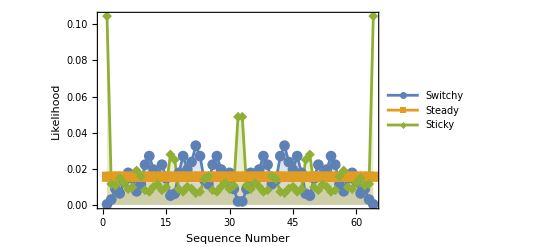

```mathematica
(*Setting the sequence length and generating all possible sequences of that length*)seqLength=6;
Length[allSeqs=Tuples[{0,1},seqLength]];

(*Calculating the sequence likelihoods for all sequences for each type of process*)
listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];

(*Plotting the sequence likelihoods for the three types of processes*)
ListLinePlot[{listSwiSeqLikes,listSteSeqLikes,listStiSeqLikes},Filling->Axis,PlotMarkers->Automatic,PlotRange->Full,PlotLegends->{"Switchy","Steady","Sticky"},Frame->{True,True,False,False},FrameLabel->{"Sequence Number","Likelihood"}]
```

We can already see that Sticky has some big divergences from Steady, while Switchy seems to have less—(though this may be distorted by the linear scale, of course).

```mathematica
allSeqs[[1]]
allSeqs[[32]]
allSeqs[[33]]
allSeqs[[64]]
```

{0,0,0,0,0,0}

{0,1,1,1,1,1}

{1,0,0,0,0,0}

{1,1,1,1,1,1}

The divergence gets harder to see as we look at bigger sequences, where it can show up more, because the ordering is so unnatural:

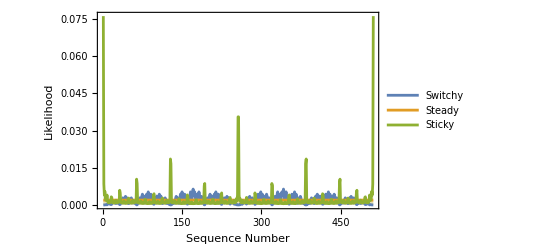

```mathematica
(*Setting the sequence length and generating all possible sequences of that length*)seqLength=9;
Length[allSeqs=Tuples[{0,1},seqLength]];

(*Calculating the sequence likelihoods for all sequences for each type of process*)
listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];

(*Plotting the sequence likelihoods for the three types of processes*)
ListLinePlot[{listSwiSeqLikes,listSteSeqLikes,listStiSeqLikes},Filling->Axis,PlotRange->Full,PlotLegends->{"Switchy","Steady","Sticky"},Frame->{True,True,False,False},FrameLabel->{"Sequence Number","Likelihood"}]
```

This is slightly easier to see if we order the sequences in a relevant order, such as by the number of switches they contain:

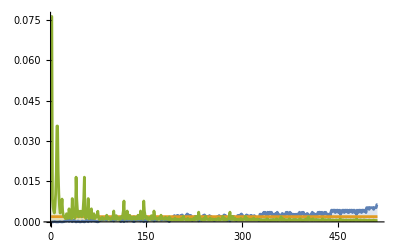

```mathematica
(*Setting the sequence length*)
seqLength=9;
(*Generating all possible sequences of heads and tails with a length of 10*)
Length[allSeqs=Tuples[{0,1},seqLength]];
(*Sorting the sequences based on the number of switches they contain using the'getNumSwitches' function*)
allSeqs=SortBy[allSeqs,getNumSwitches];
(*Calculating the likelihoods of each sorted sequence for the Switchy process*)
listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Steady process*)
listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Sticky process*)
listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];

(*Plotting the sequence likelihoods for the three processes.Sequences are ordered by their number of switches.*)
ListLinePlot[{listSwiSeqLikes,listSteSeqLikes,listStiSeqLikes},
Filling->Axis,PlotRange->Full,
ImageSize->Full
(*PlotMarkers->Automatic*) (*This line is commented out;uncomment to add plot markers*)]
```

We can calculate the distances between these likelihood distributions with both the Euclidean and KL-Divergence measures:

```mathematica
(*Euclidean distance:*)
Sqrt[Total[(listSwiSeqLikes-listSteSeqLikes)^2]]
Sqrt[Total[(listStiSeqLikes-listSteSeqLikes)^2]]

Sqrt[Total[(listStiSeqLikes-listSteSeqLikes)^2]]/Sqrt[Total[(listSwiSeqLikes-listSteSeqLikes)^2]]
```

0.0314517

0.124002

3.94263

The ratio of how much (Euclidean) farther Sticky is to Steady than Switchy is growing as the sequence-length grows:

```mathematica
(*Setting the sequence length*)
seqLength=15;
(*Generating all possible sequences of heads and tails with a length of 10*)
Length[allSeqs=Tuples[{0,1},seqLength]];
(*Sorting the sequences based on the number of switches they contain using the'getNumSwitches' function*)
allSeqs=SortBy[allSeqs,getNumSwitches];
(*Calculating the likelihoods of each sorted sequence for the Switchy process*)
listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Steady process*)
listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Sticky process*)
listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
```

```mathematica
Sqrt[Total[(listSwiSeqLikes-listSteSeqLikes)^2]]
Sqrt[Total[(listStiSeqLikes-listSteSeqLikes)^2]]

Sqrt[Total[(listStiSeqLikes-listSteSeqLikes)^2]]/Sqrt[Total[(listSwiSeqLikes-listSteSeqLikes)^2]]
```

0.00579734

0.069762

12.0335

```mathematica
(*Initialize a list to store the Euclidean distances from Steady to Sticky/Switchy for various sequence lengths*)
euDistances=Table[
(*Set the current sequence length*)
seqLength=indSeqLength;
(*Generate all possible sequences of heads and tails for the current sequence length*)
Length[allSeqs=Tuples[{0,1},seqLength]];
(*Sort the sequences based on the number of switches they contain using the'getNumSwitches' function*)
allSeqs=SortBy[allSeqs,getNumSwitches];
(*Calculate the likelihoods of each sorted sequence for the Switchy process*)listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculate the likelihoods of each sorted sequence for the Steady process*)listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculate the likelihoods of each sorted sequence for the Sticky process*)listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];

(*Calculate the Euclidean distance from Steady to Switchy and Sticky likelihoods, recording the sequence-length along the way.*){{seqLength,Sqrt[Total[(listSwiSeqLikes-listSteSeqLikes)^2]]},{seqLength,Sqrt[Total[(listStiSeqLikes-listSteSeqLikes)^2]]}}
(*Repeat the above process for sequence lengths rangin
 from 2 to 16*),{indSeqLength,2,16,1}];
```

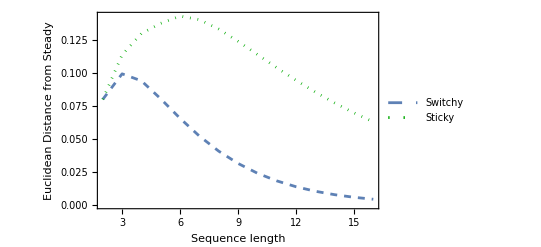

```mathematica
(*Plot the Euclidean distances: *)

ListLinePlot[{#[[1]]&/@euDistances,#[[2]]&/@euDistances},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotRange->{{2,16},Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","Euclidean Distance from Steady"},
PlotLegends->Placed[{"Switchy","Sticky"},{0.85,0.8}]]
```

Note that though the difference is shrinking, the ratio is growing:

{1.,1.14511,1.38144,1.71169,2.1804,2.69123,3.26963,3.94263,4.7397,5.69472,6.84796,8.24769,9.95242,12.0335,14.5781}

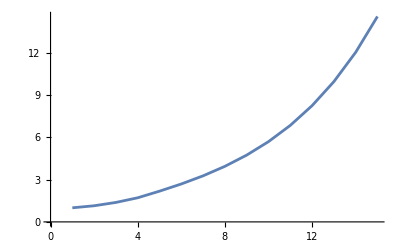

```mathematica
ratioEUDistances =euDistances[[#,2,2]] / euDistances[[#,1,2]]&/@Range[Length[euDistances]]
ListLinePlot[ratioEUDistances]
```

We can do the same with KL divergence, looking at the KL divergence from Steady to Switchy, compared to that from Steady to Sticky:

```mathematica
(*Setting the sequence length*)
seqLength=15;
(*Generating all possible sequences of heads and tails with a length of 10*)
Length[allSeqs=Tuples[{0,1},seqLength]];
(*Sorting the sequences based on the number of switches they contain using the'getNumSwitches' function*)
allSeqs=SortBy[allSeqs,getNumSwitches];
(*Calculating the likelihoods of each sorted sequence for the Switchy process*)
listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Steady process*)
listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculating the likelihoods of each sorted sequence for the Sticky process*)
listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
```

```mathematica
listSwiSeqLikes.Log[listSwiSeqLikes/listSteSeqLikes]
listStiSeqLikes.Log[listStiSeqLikes/listSteSeqLikes]
```

0.510793

2.15498

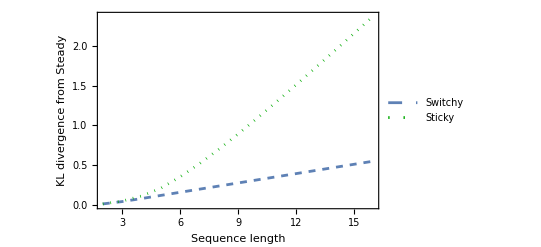

```mathematica
(*Initialize a list to store the KL divergences from Steady to Sticky/Switchy for various sequence lengths*)
klDivergences=Table[
(*Set the current sequence length*)
seqLength=indSeqLength;
(*Generate all possible sequences of heads and tails for the current sequence length*)
Length[allSeqs=Tuples[{0,1},seqLength]];
(*Calculate the likelihoods of each sorted sequence for the Switchy process*)listSwiSeqLikes=swi5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculate the likelihoods of each sorted sequence for the Steady process*)listSteSeqLikes=ste5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculate the likelihoods of each sorted sequence for the Sticky process*)listStiSeqLikes=sti5SeqLikes[allSeqs[[#]]]&/@Range[Length[allSeqs]];
(*Calculate the KL Divergence from Steady to Switchy and Stickky likelihoods, recording the sequence length along the way*){{seqLength,listSwiSeqLikes.Log[listSwiSeqLikes/listSteSeqLikes]},{seqLength,listStiSeqLikes.Log[listStiSeqLikes/listSteSeqLikes]}}
(*Repeat the above process for sequence lengths ranging from 2 to 16*),{indSeqLength,2,16,1}];

(*Plot the KL Divergences *)
ListLinePlot[{#[[1]]&/@klDivergences,#[[2]]&/@klDivergences},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotRange->{{2,16},Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","KL divergence from Steady"},
PlotLegends->Placed[{"Switchy","Sticky"},{0.2,0.8}]]
```

What this means is that, on average, if Bayesians start out unsure (say, uniform) between Switchy, Steady, and Sticky, and then observe a sequence of given length (seqLength) generated from a Steady process, their average probability for Sticky will fall faster than their average probability for Switchy. 

We can simulate and visualize these averages with the following code:  
(Note: this simulation takes awhile to run—about 1 -2 minutes on my machine.  To exponentially speed it up, drop the length-100 or even length-50 sequences

```mathematica
Clear[simPosts]
```

```mathematica
(*First, get a list of various sequence lengths and the average posteriors in {Switchy, Steady, Sticky} upon conditioning on them:*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)
prior={1/3,1/3,1/3};

(*For various sequence lengths (ranging from 1 to 100),simulate the beliefs of Bayesian agents*)
Timing[seqLengthAndPosts=Table[
(*Set the current sequence length*)
seqLength=indSeqLength;
(*For each sequence length,run a simulation 10,000 times*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform, these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10,000 times to get an average belief over the simulations*)
10000];
(*Calculate the mean posterior beliefs for Switchy,Steady,and Sticky over the 10,000 simulations*)
means=Mean[simPosts[seqLength]];
(*Store the sequence length and the mean beliefs for each process in a list*)
{indSeqLength,means[[1]],means[[2]],means[[3]]}
(*Repeat the entire simulation for sequence lengths 1,5,10,20,50,and 100*)
,{indSeqLength,{1,5,10,20,30,50,100,150}}]]
```

{103.029,{{1,0.333333,0.333333,0.333333},{5,0.343533,0.342062,0.314405},{10,0.351131,0.390971,0.257898},{20,0.322089,0.492632,0.185278},{30,0.275024,0.597249,0.127727},{50,0.196836,0.74665,0.0565139},{100,0.0884064,0.904127,0.00746617},{150,0.0398532,0.959298,0.000848834}}}

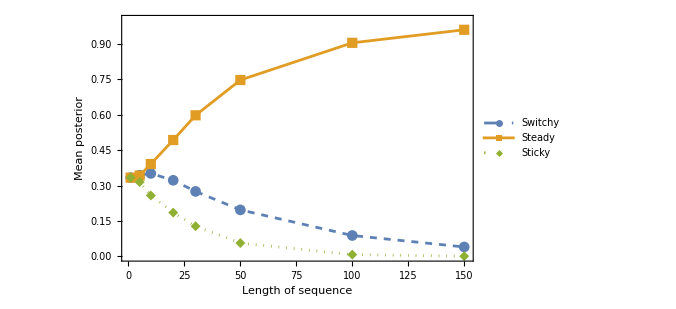

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)

(*Define the maximum sequence length to be used for setting the plot's x-axis range*)
maxSeqLength=150;

(*Extract Switchy means for each sequence length from the simulation results.The result will be a list of pairs where the first element is the sequence length and the second element is the mean.*)
swiMeans={#[[1]],#[[2]]}&/@seqLengthAndPosts;

(*Similarly,extract means for Steady and Sticky processes*)
steMeans={#[[1]],#[[3]]}&/@seqLengthAndPosts;
stiMeans={#[[1]],#[[4]]}&/@seqLengthAndPosts;

(*Plot the means for each process as the sequence length varies*)
ListLinePlot[{swiMeans,steMeans,stiMeans},PlotRange->{{0,maxSeqLength+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->12],None},{Style["Length of sequence",FontSize->12],None}},PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.5}],
ImageSize->500]
```

Note that the ratio of mean posterior probability in Switchy to that in Sticky is growing:

{1.,1.07795,1.34501,1.78331,2.25392,3.20479,10.163,28.9995}

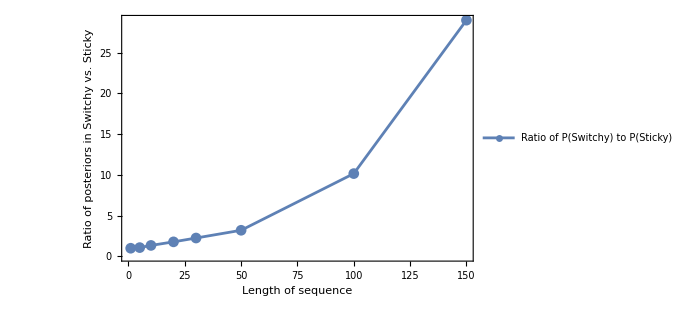

```mathematica
meanRatios=(#[[2]]&/@swiMeans )/ (#[[2]]&/@stiMeans)
ListLinePlot[Table[{swiMeans[[ind,1]],meanRatios[[ind]]},{ind,Length[meanRatios]}],
PlotRange->Full,
PlotRange->{{0,maxSeqLength+1},{0,1}},
PlotStyle->{Normal},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Ratio of posteriors in Switchy vs. Sticky",FontSize->12],None},{Style["Length of sequence",FontSize->12],None}},PlotLegends->Placed[{"Ratio of P(Switchy) to P(Sticky)"},{0.25,0.9}],
ImageSize->500]
```

Still, the fact that by the end of a 100-toss sequence people are so confident of Steady means that the degree to which they exhibit gambler’s or hot-hands reasoning will be fairly marginal.

For example, suppose we tell all our 10,000 Bayesians who’ve seen N-many tosses (for various N) that the coin has landed tails once in a row. This itself doesn’t provide evidence about whether the process is Switchy or Sticky, but it does tell them that if it’s Switchy, it’s 42% likely for the streak to continue—since then it’s in state 5 in the below Markov chain:

```mathematica
swi5
```

{{0.1,0,0,0,0,0.9,0,0,0,0},{0.18,0,0,0,0,0.82,0,0,0,0},{0,0.26,0,0,0,0.74,0,0,0,0},{0,0,0.34,0,0,0.66,0,0,0,0},{0,0,0,0.42,0,0.58,0,0,0,0},{0,0,0,0,0.58,0,0.42,0,0,0},{0,0,0,0,0.66,0,0,0.34,0,0},{0,0,0,0,0.74,0,0,0,0.26,0},{0,0,0,0,0.82,0,0,0,0,0.18},{0,0,0,0,0.9,0,0,0,0,0.1}}

Similarly, if it’s Steady, it’s 50% likely to continue and if it’s Sticky, it’s 58% likely to continue.

```mathematica
nextHeadsLikes = {swi5[[5,4]],ste5[[5,4]],sti5[[5,4]]}
```

{0.42,0.5,0.58}

Given this, we can calculate each agent’s credence in heads in the next toss by multiplying these likelihoods by their credences in the respective Switchy/Steady/Sticky hypotheses, and then plot the distribution of their credences in the next toss being heads.

For Bayesians that have only seen 20 tosses, there is quite a bit of variance:

0.48864

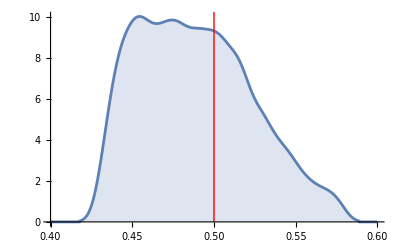

```mathematica
nextHeadsPosts=simPosts[20].nextHeadsLikes;
Mean[nextHeadsPosts]
SmoothHistogram[nextHeadsPosts,
 Filling->Axis,
PlotRange->{{0.4,0.6},Automatic},
Epilog->{Red,Line[{{0.5,0},{0.5,100}}]}]
```

But for those who’ve seen 100 tosses, they are almost all very close to 50%:

0.494011

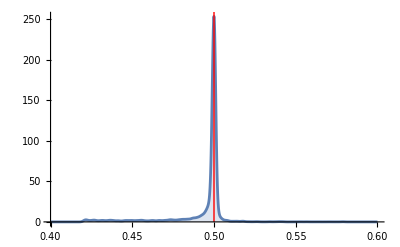

```mathematica
nextHeadsPosts=simPosts[100].nextHeadsLikes;
Mean[nextHeadsPosts]
SmoothHistogram[nextHeadsPosts,0.001,
 Filling->Axis,
PlotRange->{{0.4,0.6},Full},
Epilog->{Red,Line[{{0.5,0},{0.5,10^6}}]}]
```

Those with mean credences after seeing 150 tosses, then seeing it land heads 3 times in a row:

```mathematica
{0.037686263493794864,0.9612929221434305,0.0010208143627740028}.{0.26,0.5,0.74}
```

0.4912

### Limited memory: asymmetric closeness and convergence

As discussed in the paper [§___], I’ll use the unpacking model of limited memory. Given a sequence of 1000 tosses, the 1-unpacked memory of it records the total number of 1s; the 2-unpacked memory records both the number of 1s in the first half (500 tosses) and the number of 1s in the second half; and so on.  Clearly the 1000-unpacked memory is the full sequence.

Begin by noting that now that we are focusing on proportions-of-1s, we can now visualize the sense in which the Steady likelihood distribution is closer to Switchy than to Sticky.  

We can show this by looking at the likelihoods for the various possible numbers of 1s for various total numbers of outcomes, using our getInstantPropLikelihoods function from above:

```mathematica
swi5 = getInstantChain[0.1,5]
ste5=getInstantChain[0.5,5]
sti5 = getInstantChain[0.9,5]

(*Note that we don't need the ste5PropLikes, since those are encoded (more efficiently) in the built-in BinomialDistribution function: *)
getInstantPropLikelihoods[swi5PropLikes,swi5]

ste5PropLikes[numTosses_,numHeads_]:=PDF[BinomialDistribution[numTosses,0.5],numHeads]

getInstantPropLikelihoods[sti5PropLikes,sti5]
```

{{0.1,0,0,0,0,0.9,0,0,0,0},{0.18,0,0,0,0,0.82,0,0,0,0},{0,0.26,0,0,0,0.74,0,0,0,0},{0,0,0.34,0,0,0.66,0,0,0,0},{0,0,0,0.42,0,0.58,0,0,0,0},{0,0,0,0,0.58,0,0.42,0,0,0},{0,0,0,0,0.66,0,0,0.34,0,0},{0,0,0,0,0.74,0,0,0,0.26,0},{0,0,0,0,0.82,0,0,0,0,0.18},{0,0,0,0,0.9,0,0,0,0,0.1}}

{{0.5,0,0,0,0,0.5,0,0,0,0},{0.5,0,0,0,0,0.5,0,0,0,0},{0,0.5,0,0,0,0.5,0,0,0,0},{0,0,0.5,0,0,0.5,0,0,0,0},{0,0,0,0.5,0,0.5,0,0,0,0},{0,0,0,0,0.5,0,0.5,0,0,0},{0,0,0,0,0.5,0,0,0.5,0,0},{0,0,0,0,0.5,0,0,0,0.5,0},{0,0,0,0,0.5,0,0,0,0,0.5},{0,0,0,0,0.5,0,0,0,0,0.5}}

{{0.9,0,0,0,0,0.1,0,0,0,0},{0.82,0,0,0,0,0.18,0,0,0,0},{0,0.74,0,0,0,0.26,0,0,0,0},{0,0,0.66,0,0,0.34,0,0,0,0},{0,0,0,0.58,0,0.42,0,0,0,0},{0,0,0,0,0.42,0,0.58,0,0,0},{0,0,0,0,0.34,0,0,0.66,0,0},{0,0,0,0,0.26,0,0,0,0.74,0},{0,0,0,0,0.18,0,0,0,0,0.82},{0,0,0,0,0.1,0,0,0,0,0.9}}

```mathematica
(*put likelihood functions in a list:*)
chain5PropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

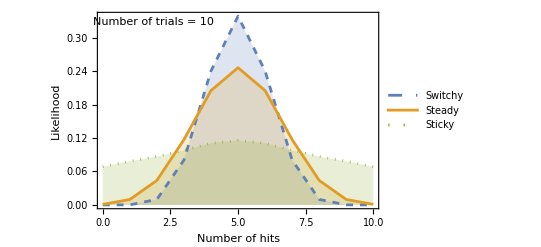

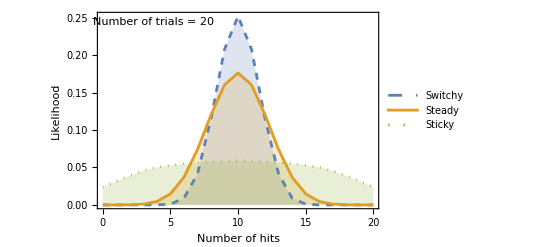

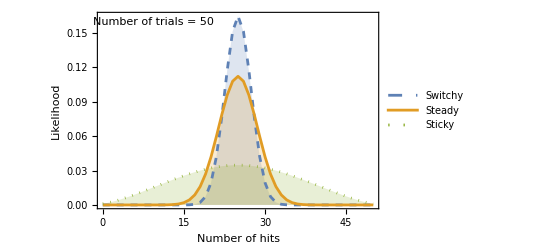

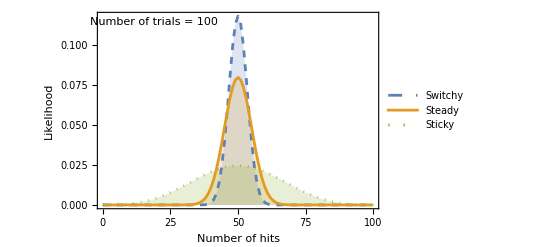

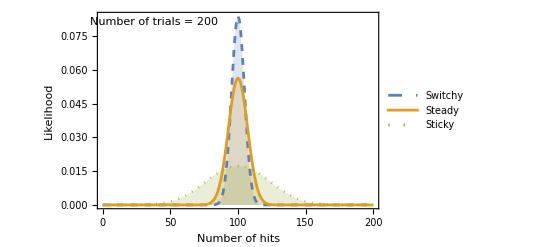

General::munfl: 3.34152×10^-308 0.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.47614×10^-308 0.18 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.49082×10^-308 0.26 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

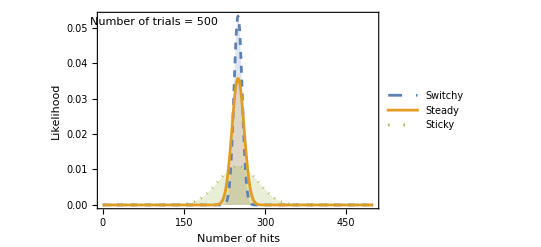

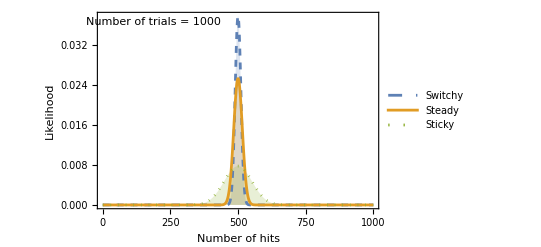

```mathematica
(*Plot likelihoods for various total tosses:*)

(*NOTES
1) the first time you run this, it'll take a few minutes, since swi5PropLikes and sti5PropLikes will needs to recursively calculate likelihoods out to 1000 tosses.  Afterwards it'll run instantly (unless you Clear those functions).
2) You will get a warning that precisino may be lost due to the small likkelihoods at the tails of the distribution. Don't worry about it——we'll virtually never sample from these tails anyways *)

(*iterate through various numbers of tosses:*)
Do[

(*Set the number of total tosses:*)
numTosses = indNumTosses;

(*get a list of {numHeads,likelihood} pairs for each chain:*)
listLikes=Table[{ind,#[numTosses,ind]},{ind,0,numTosses}]&/@chain5PropLikes;

(*Plot the three chain's likelihoods:*)
Print[ListLinePlot[listLikes,
Filling->Axis,
PlotRange->Full,
PlotStyle->{Dashed,Normal,Dotted},
PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.8}],
Frame->{True,True,False,False},
FrameLabel->{"Number of hits","Likelihood"},
Epilog->Text["Number of trials = "<>ToString[numTosses],Scaled[{0.2,0.95}]]]]

(*say what numbers of tosses to iterate through:*)
,{indNumTosses,{10,20, 50,100,200,500,1000}}]
```

To verify this intuition, we can again plot Euclidean distances and KL divergences between Steady and Switchy/Sticky likelihoods as the number of tosses grows.

Euclidean distances:

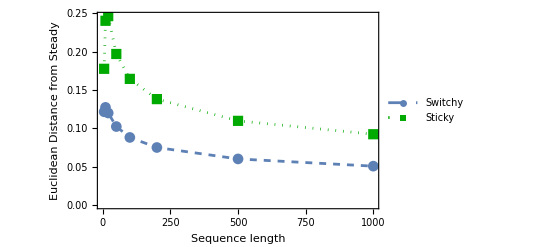

```mathematica
(*Initialize a list to store the Euclidean distances from Steady to Sticky/Switchy for various sequence lengths*)
euDistances=Table[
(*Set the current sequence length*)
(*Set the number of total tosses:*)
numTosses = indSeqLength;

(*get a list of likelihoods for each chain:*)
listLikes=Table[#[numTosses,ind],{ind,0,numTosses}]&/@chain5PropLikes;


(*Calculate the Euclidean distance from Steady to Switchy and Sticky likelihoods, recording the sequence-length along the way.*){{numTosses,Sqrt[Total[(listLikes[[1]]-listLikes[[2]])^2]]},{numTosses,Sqrt[Total[(listLikes[[3]]-listLikes[[2]])^2]]}}

(*Repeat the above process for various sequence lengths:*),{indSeqLength,{5,10,20,50,100,200,500,1000}}];

(*Plot the Euclidean distances: *)
ListLinePlot[{#[[1]]&/@euDistances,#[[2]]&/@euDistances},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotMarkers->Automatic,
PlotRange->{Automatic,Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","Euclidean Distance from Steady"},
PlotLegends->Placed[{"Switchy","Sticky"},{0.85,0.8}]]
```

KL divergences:
(NOTE: because of rounding errors (rounding small numbers down to 0), we can’t accurately calculate KL divergences for lengths greater than around 300; but the trend is clear)

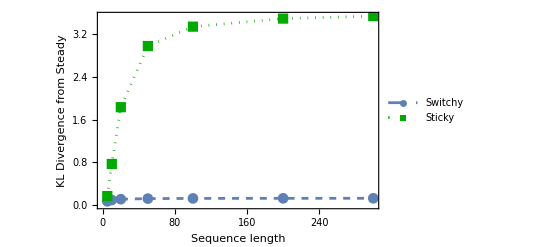

```mathematica
(*Initialize a list to store the KL divergences from Steady to Sticky/Switchy for various sequence lengths*)
klDivergences=Table[
(*Set the current sequence length*)
(*Set the number of total tosses:*)
numTosses = indSeqLength;

(*get a list of likelihoods for each chain:*)
listLikes=Table[#[numTosses,ind],{ind,0,numTosses}]&/@chain5PropLikes;


(*Calculate the KL divergence between the Sticky and Steady likelihoods, recording the sequence-length along the way.*)
{{numTosses,listLikes[[1]].Log[listLikes[[1]]/listLikes[[2]]]},{numTosses,listLikes[[3]].Log[listLikes[[3]]/listLikes[[2]]]}}

(*Repeat the above process for various sequence lengths:*),{indSeqLength,{5,10,20,50,100,200,300}}];

(*Plot the KL divergences: *)
ListLinePlot[{#[[1]]&/@klDivergences,#[[2]]&/@klDivergences},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotMarkers->Automatic,
PlotRange->{Automatic,Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","KL Divergence from Steady"},
PlotLegends->Placed[{"Switchy","Sticky"},{0.85,0.8}]]
```

Now we again plot the mean posteriors for agents who start out uniform over the process and condition on the memory-unpacked outcomes of 1000-toss sequences, for various depths of unpacking:

{{1,0.382972,0.39051,0.226519},{2,0.395835,0.44212,0.162046},{5,0.355465,0.586485,0.0580495},{10,0.276532,0.712726,0.010742},{15,0.214239,0.784557,0.00120431},{20,0.172869,0.826582,0.000548783},{30,0.108276,0.891721,2.48151×10^-6},{40,0.0725084,0.927492,4.3466×10^-8},{50,0.0457882,0.954212,8.52225×10^-10}}

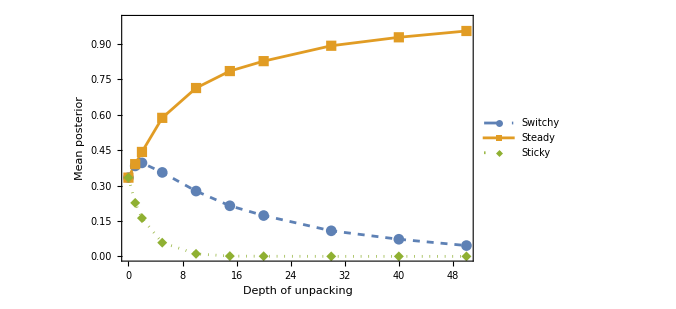

```mathematica
(*Create a list of simulations of Bayesians updating on the results of 1000 tosses, unpacked to various depths:*)

(*NOTE: unpacking of 1 is the hardest since this requires calcualting likelihoods out to 1000 tosses. This takes a couple minutes on the first run, but will be instant afterward*)

Clear[simPosts];

depthsAndPosts=Table[
(*Set the depth of memory unpacking and get number of tosses in each subsequence:*)
unpackDepth = indDepth;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=3000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;


(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*record mean posteriors in each hypothesis*)
means = Mean[simPosts[unpackDepth]];
{indDepth,means[[1]],means[[2]],means[[3]]}

(*iterate through various depths of unpacking:*)
,{indDepth,{1,2,5,10,15,20,30,40,50}}]


(*Extract Switchy means for each sequence length from the simulation results.The result will be a list of pairs where the first element is the depth of unpacking and the second element is the mean.
Prepend the 1/3 prior:*)
swiMeans=Prepend[{#[[1]],#[[2]]}&/@depthsAndPosts,{0,1/3}];

(*Similarly,extract means for Steady and Sticky processes*)
steMeans=Prepend[{#[[1]],#[[3]]}&/@depthsAndPosts,{0,1/3}];
stiMeans=Prepend[{#[[1]],#[[4]]}&/@depthsAndPosts,{0,1/3}];

(*Plot the mean posteriors for each process as the unpacking-depth varies*)
ListLinePlot[{swiMeans,steMeans,stiMeans},
PlotRange->{Automatic,{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of unpacking",FontSize->14],None}},
ImageSize->500,
PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.5}]]
```

The mean credence in a continuation after a streak of 2 and 3 with 20-unpacking are:

```mathematica
{0.17237372983501112,0.8271875906360768,0.00043867952891001147}.{0.34,0.5,0.66}
{0.17237372983501112,0.8271875906360768,0.00043867952891001147}.{0.26,0.5,0.74}
```

0.47249

0.458736

Mean ratios of posteriors in Switchy to Sticky:

```mathematica
swiMeans
```

{{0,1/3},{1,0.382972},{2,0.395835},{5,0.355465},{10,0.276532},{15,0.214239},{20,0.172869},{30,0.108276},{40,0.0725084},{50,0.0457882}}

```mathematica
swiMeans[[4,1]]
```

5

{1,1.69068,2.44274,6.12349,25.7431,177.893}

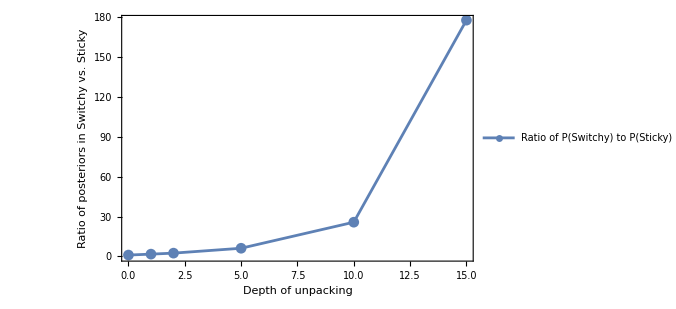

```mathematica
meanRatios=(#[[2]]&/@swiMeans [[;;6]])/ (#[[2]]&/@stiMeans[[;;6]])
plot=ListLinePlot[Table[{swiMeans[[ind,1]],meanRatios[[ind]]},{ind,Length[meanRatios]}],
PlotRange->Full,
PlotRange->{{0,20},{0,1}},
PlotStyle->{Normal},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Ratio of posteriors in Switchy vs. Sticky",FontSize->12],None},{Style["Depth of unpacking",FontSize->12],None}},PlotLegends->Placed[{"Ratio of P(Switchy) to P(Sticky)"},{0.25,0.9}],
ImageSize->500];
Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_swi_sti_ratios.pdf",plot];
```

### Fallacious Feature #1: Sequence Dependence

What if give subjects different sequences that are more or less switchy; will that shift their probabilities of switching?

```mathematica
(*make lists of different numbers of switches; from sequences in Bloomfield et al 2002*)
fewSwitchesList = {
{1,1,1,1,1,1,1,1},
{0,1,1,1,1,1,1,1},
{0,0,0,0,0,0,1,1},
{0,0,0,0,1,1,1,1}
};
medSwitchesList = {
{0,0,0,1,1,0,0,1}, (*3 switches*)
{1,1,1,0,1,1,0,1} (*4 switches*)
};
manySwitchesList = {
{1,0,1,0,1,0,1,1}, (*6 switches*)
{0,1,0,1,0,1,0,1} (*7 switches*)
};
```

```mathematica
(*DO NOT run the following if you're run the above sections, as it'll reset the Swi5PropLikes functions, etc, and they'll need to be calculated again*)

(*Generating the Markov chains for a Switchy,Steady,and Sticky process with 5 steps*)
MatrixForm[swi5=getChain[0.1,5]];
MatrixForm[ste5=getChain[0.5,5]];
MatrixForm[sti5=getChain[0.9,5]];

(*Calculating the likelihoods for individual outcomes based on the chains*)
getInstantPropLikelihoods[swi5PropLikes,swi5];
getInstantPropLikelihoods[ste5PropLikes,ste5];
getInstantPropLikelihoods[sti5PropLikes,sti5];

(*Calculating the likelihoods for entire sequences based on the chains*)
getInstantSeqLikes[swi5SeqLikes,swi5];
getInstantSeqLikes[ste5SeqLikes,ste5];
getInstantSeqLikes[sti5SeqLikes,sti5];
```

```mathematica
(*set chainList to default to the one we've been using:*)
chainList={swi5,ste5,sti5};

(*put likelihoods in lists*)
chainSeqLikes = {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes};
chainPropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

```mathematica
(*get posteriors with LIMITED DATA*)

(*get list of posteriors for agents who see limited data*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=30;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*label the posteriors*)
limDataPosts = simPosts[seqLength];

(*mean posteriors:*)
Mean[limDataPosts]
```

{0.274384,0.598086,0.12753}

```mathematica
(*give our LIMITED DATA agents each sequence in the different sets, and record their average probability of a continuation*)

(*put our sequence-groups in a list*)
listOfSeqTypes={fewSwitchesList,medSwitchesList,manySwitchesList};

(*get list of mean probability of switching within each sequence type*)
limDataProbContBySeqType=Table[

(*set the sequence type*)
seqType =indSeqType;

(*get mean probability of continuing for the given sequence type*)
Mean[
Table[
(*set the sequence*)
seq = indSeq;
(*get likelihoods for sequence:*)
likes = #[seq]&/@chainSeqLikes;

(*get updated posteriors in each hypothesis:*)
updatedLimDataPosts = Table[
updatedPost=(indPost*likes)/indPost.likes
,{indPost,limDataPosts}
];

(*get likelihoods of current streak continuing*)
(*get current state of each chain*)
curState = getInstantChainState[chainList[[1]],seq];
(*set continuation probabilities*)
If[seq[[-1]]==1, contLikes = (1-getProbTails[#,curState])&/@chainList];
If[seq[[-1]]==0, contLikes = (getProbTails[#,curState])&/@chainList];

(*get mean probability of continuing*)
Mean[Table[indPost.contLikes,{indPost,updatedLimDataPosts}]]

(*iterate through sequences in seqType*)
,{indSeq,indSeqType}]
]

(*iterate through sequence types*)
,{indSeqType,listOfSeqTypes}]
```

{0.626504,0.48272,0.462138}

```mathematica
(*Same thing with LIMITED MEMORY*)

(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 4;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chainPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.378282,0.54128,0.0804379}

```mathematica
(*give our LIMITED MEMORY agents each sequence in the different sets, and record their average probability of a continuation*)

(*put our sequence-groups in a list*)
listOfSeqTypes={fewSwitchesList,medSwitchesList,manySwitchesList};

(*get list of mean probability of switching within each sequence type*)
limMemProbContBySeqType=Table[

(*set the sequence type*)
seqType =indSeqType;

(*get mean probability of continuing for the given sequence type*)
Mean[
Table[
(*set the sequence*)
seq = indSeq;
(*get likelihoods for sequence:*)
likes = #[seq]&/@chainSeqLikes;

(*get updated posteriors in each hypothesis:*)
updatedLimMemPosts = Table[
updatedPost=(indPost*likes)/indPost.likes
,{indPost,limMemPosts}
];

(*get likelihoods of current streak continuing*)
(*get current state of each chain*)
curState = getInstantChainState[chainList[[1]],seq];
(*set continuation probabilities*)
If[seq[[-1]]==1, contLikes = (1-getProbTails[#,curState])&/@chainList];
If[seq[[-1]]==0, contLikes = (getProbTails[#,curState])&/@chainList];

(*get mean probability of continuing*)
Mean[Table[indPost.contLikes,{indPost,updatedLimMemPosts}]]

(*iterate through sequences in seqType*)
,{indSeq,indSeqType}]
]

(*iterate through sequence types*)
,{indSeqType,listOfSeqTypes}]
```

{0.592924,0.471326,0.441295}

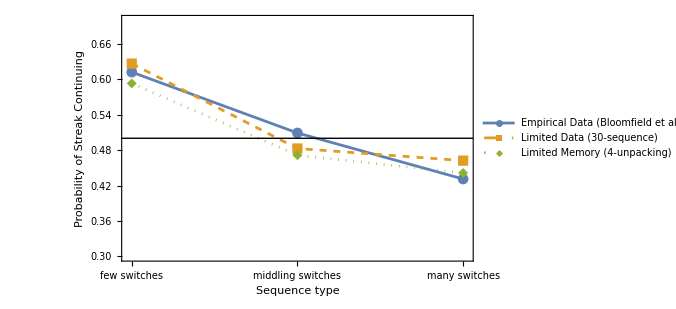
-Graphics-Probability of continuations by sequence-type

```mathematica
(*put Bloomfield et al. 2002 rates in a list*)
empProbContBySeqType ={0.612, 0.509, 0.431};

(*plot the results*)
plot=Labeled[ListLinePlot[
{empProbContBySeqType,limDataProbContBySeqType,limMemProbContBySeqType},
PlotRange->{{0.98,3.02},{0.3,0.7}},
PlotStyle->{Normal,Dashed,Dotted},
PlotMarkers->Automatic,
PlotLegends->Placed[{
"Empirical Data (Bloomfield et al. 2002)", 
"Limited Data (30-sequence)",
"Limited Memory (4-unpacking)"},{0.7,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Probability of Streak Continuing",FontSize->12],None},{Style["Sequence type",FontSize->12],None}},
FrameTicks->{{Automatic,None},{{{1,Style["few switches",FontWeight->Bold,FontSize->12]},{2,Style["middling switches",FontWeight->Bold,FontSize->12]},{3,Style["many switches",FontWeight->Bold,FontSize->12]}},None}},Epilog->{Thin,Line[{{0,0.5},{5,0.5}}]},
ImageSize->500],
Style["Probability of continuations by sequence-type",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/seq_dependence.pdf",plot];
```

### Fallacious Feature #2: Nonlinear Dynamics

Here we’ll show how, as streak-length increases, our agents will first increasingly predict switches, and then increasingly predict continuations.

This subsection presupposes the earlier ones in Instant-Fall Chains, as it needs to have the likelihoods for our relevant hypotheses calculated

```mathematica
(*DO NOT run the following if you're run the above sections, as it'll reset the Swi5PropLikes functions, etc, and they'll need to be calculated again*)

(*Generating the Markov chains for a Switchy,Steady,and Sticky process with 5 steps*)
MatrixForm[swi5=getChain[0.1,5]]
MatrixForm[ste5=getChain[0.5,5]]
MatrixForm[sti5=getChain[0.9,5]]

(*Calculating the likelihoods for individual outcomes based on the chains*)
getInstantPropLikelihoods[swi5PropLikes,swi5]
getInstantPropLikelihoods[ste5PropLikes,ste5]
getInstantPropLikelihoods[sti5PropLikes,sti5]

(*Calculating the likelihoods for entire sequences based on the chains*)
getInstantSeqLikes[swi5SeqLikes,swi5]
getInstantSeqLikes[ste5SeqLikes,ste5]
getInstantSeqLikes[sti5SeqLikes,sti5]
```

```mathematica
(*set chainList to default to the one we've been using:*)
chainList={swi5,ste5,sti5};

(*put likelihoods in lists*)
chainSeqLikes = {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes};
chainPropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

#### Limited data

As before, begin by taking agents who are uniform over our hypotheses and then having them condition on a short (in this case, length 50) full sequence, recording their posteriors in the three hypothess:

```mathematica
(*get list of posteriors for agents who see limited data*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=50;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*label the posteriors*)
limDataPosts = simPosts[seqLength];

(*mean posteriors:*)
Mean[limDataPosts]
```

{0.192077,0.747185,0.0607373}

Now observe how as condition on longer streaks, posteriors in each hypothesis change:

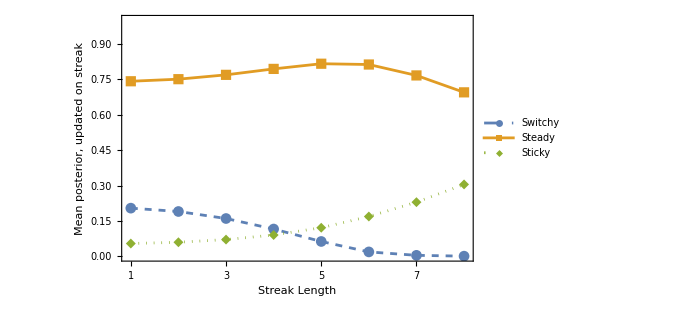
-Graphics-Limited Data (50-sequence)

```mathematica
(*create a list of pairs of streak length and updated posterior credences in each hypothesis*)

(*set the max streak length of interest:*)
maxStrLength=8;

(*create the list of pairs*)
limDataUpdatedMeanPosts=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimDataPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataPosts}
];

(*record mean posteriors be streak length*)
{strLength,
aroundCI[#[[1]]&/@updatedLimDataPosts],
aroundCI[#[[2]]&/@updatedLimDataPosts],
aroundCI[#[[3]]&/@updatedLimDataPosts]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}];

(*separate posteriors in each chain:*)
swiMeans ={ #[[1]],#[[2]]}&/@limDataUpdatedMeanPosts;
steMeans ={ #[[1]],#[[3]]}&/@limDataUpdatedMeanPosts;
stiMeans ={ #[[1]],#[[4]]}&/@limDataUpdatedMeanPosts;

(*plot the results*)
plot = Labeled[ListLinePlot[
{swiMeans,steMeans,stiMeans},
PlotRange->{{0.95,8.05},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
PlotLegends->Placed[{
"Switchy", 
"Steady",
"Sticky"},{0.15,0.9}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean posterior, updated on streak",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},
ImageSize->500],
Style["Limited Data (50-sequence)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];
Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_posts_by_str_len.pdf",plot];
```

Now run through various streak lengths, condition each posterior on it, and then elicit probability of a continuation:

{{1,0.48800.00050.0005},{2,0.47920.00110.0011},{3,0.47860.00150.0015},{4,0.49190.00190.0019},{5,0.52330.00210.0021},{6,0.55990.00190.0019},{7,0.59000.00200.0020},{8,0.62150.00210.0021}}

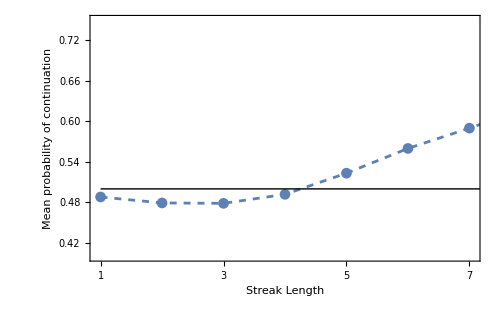
-Graphics-Limited Data

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=8;

(*create the list of pairs*)
limDataMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimDataPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimDataProbCont=Table[indPost.contLikes,{indPost,updatedLimDataPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimDataProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
(*put all results in a plot:*)
Labeled[ListLinePlot[
{limDataMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Data",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

#### Limited memory

As before, begin by taking agents who are uniform over our hypotheses and then having them condition on a partially-memory-unpacked long sequence, recording their posteriors in the three hypothess:

```mathematica
(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 7;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chainPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.320564,0.650673,0.0287633}

Now observe how as condition on longer streaks, posteriors in each hypothesis change:

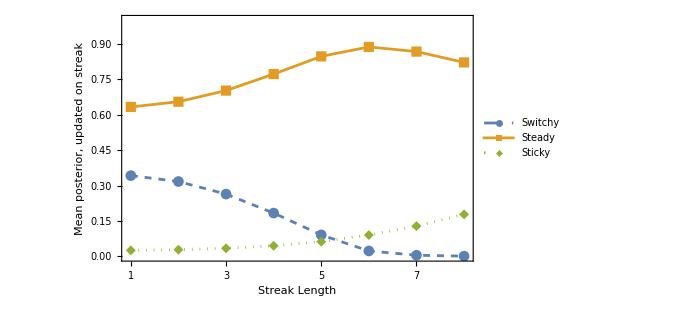
-Graphics-Limited Memory (7-unpacking)

```mathematica
(*create a list of pairs of streak length and updated posterior credences in each hypothesis*)

(*set the max streak length of interest:*)
maxStrLength=8;

(*create the list of pairs*)
limMemUpdatedMeanPosts=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*record mean posteriors be streak length*)
{strLength,
aroundCI[#[[1]]&/@updatedLimMemPosts],
aroundCI[#[[2]]&/@updatedLimMemPosts],
aroundCI[#[[3]]&/@updatedLimMemPosts]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}];

(*separate posteriors in each chain:*)
swiMeans ={ #[[1]],#[[2]]}&/@limMemUpdatedMeanPosts;
steMeans ={ #[[1]],#[[3]]}&/@limMemUpdatedMeanPosts;
stiMeans ={ #[[1]],#[[4]]}&/@limMemUpdatedMeanPosts;

(*plot the results*)
plot = Labeled[ListLinePlot[
{swiMeans,steMeans,stiMeans},
PlotRange->{{0.95,8.05},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
PlotLegends->Placed[{
"Switchy", 
"Steady",
"Sticky"},{0.15,0.9}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean posterior, updated on streak",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},
ImageSize->500],
Style["Limited Memory (7-unpacking)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];
Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_posts_by_str_len.pdf",plot];
```

Now run through various streak lengths, condition each posterior on it, and then elicit probability of a continuation

{{1,0.47470.00050.0005},{2,0.45380.00100.0010},{3,0.44490.00140.0014},{4,0.45570.00160.0016},{5,0.48850.00160.0016},{6,0.52700.00140.0014},{7,0.54930.00160.0016},{8,0.57070.00180.0018}}

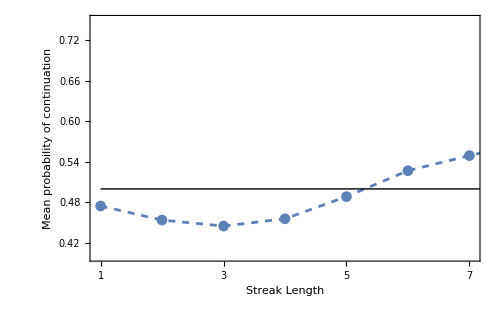
-Graphics-Limited Memory

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=8;

(*create the list of pairs*)
limMemMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemProbCont=Table[indPost.contLikes,{indPost,updatedLimMemPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
Labeled[ListLinePlot[
{limMemMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

#### Combined plots:

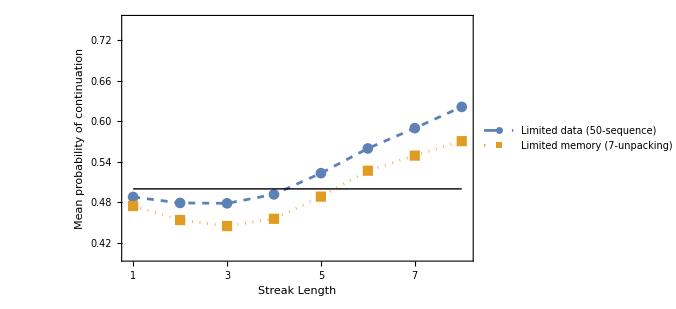
-Graphics-Simulations

```mathematica
plot = Labeled[ListLinePlot[
{limDataMeanProbContByStrLength,
limMemMeanProbContByStrLength},
PlotRange->{{0.9,8.1},{0.4,0.75}},
PlotStyle->{Dashed,Dotted},
PlotMarkers->Automatic,
PlotLegends->Placed[{
"Limited data (50-sequence)", 
"Limited memory (7-unpacking)"},{0.3,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Simulations",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/combined_cont_by_str_len.pdf",plot];
```

### Fallacious Feature #3: Variable Rates

Our third fallacious feature is that (1) the overall rates of gambler’s and hot-hands reasoning varies widely with the causal system, and (2) as streak-lengths grow, subjects transition from gambler’s to hot-hands reasoning much more quickly for unfamiliar systems than for familiar ones.

To show this, we will consider what happens when agents have (limited data:) either a little or a lot of data, and (limited memory) either a detailed or a coarse memory.

```mathematica
(*set chainList to default to the one we've been using:*)
chainList={swi5,ste5,sti5};

(*put likelihoods in lists*)
chainSeqLikes = {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes};
chainPropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

#### Limited data

Generate posteriors with a LONG (seqLength = 75) and SHORT (seqLength = 25) bit of data

```mathematica
(*get posteriors for LONG-sequence agents*)
(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=90;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*label the posteriors*)
limDataLONGPosts = simPosts[seqLength];

(*mean posteriors:*)
Mean[limDataLONGPosts]
```

{0.10061,0.887193,0.0121963}

```mathematica
(*get posteriors for SHORT-sequence agents*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=40;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*label the posteriors*)
limDataSHORTPosts = simPosts[seqLength];

(*mean posteriors:*)
Mean[limDataSHORTPosts]
```

{0.229112,0.684844,0.0860448}

Now generate random (Steady) sequences, have them update on them, observe credence it’ll continue, and count agents below 49% as doing gambler’s reasoning and above 51% as doing hot-hands reasoning:

```mathematica
(*get a list of updated LONG-sequence posteriors on a random sequence, record probability of continuation*)
limDataLONGProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},10];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limDataLONGPosts}];


(*get a list of updated SHORT-sequence posteriors on a random sequence, record probability of continuation*)
limDataSHORTProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},10];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limDataSHORTPosts}];
```

{{1,0.49230.00040.0004},{2,0.48600.00070.0007},{3,0.48310.00100.0010},{4,0.48570.00120.0012},{5,0.49510.00130.0013},{6,0.50860.00110.0011},{7,0.51780.00110.0011}}

{{1,0.48660.00060.0006},{2,0.47730.00120.0012},{3,0.47880.00170.0017},{4,0.49870.00210.0021},{5,0.54260.00230.0023},{6,0.59080.00200.0020},{7,0.63110.00200.0020}}

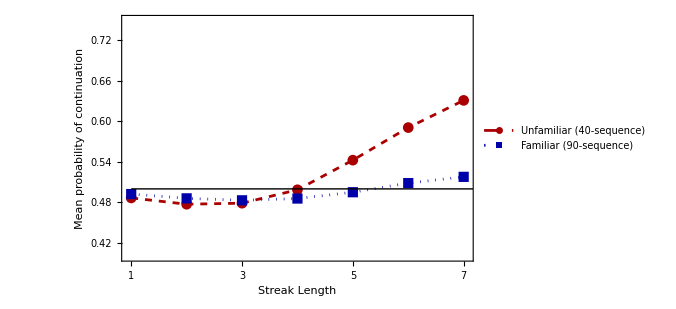
-Graphics-Limited Data

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*for LONG-sequence agents:*)
(*set the max streak length of interest:*)
maxStrLength=7;

(*create the list of pairs*)
limDataLONGMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemLONGPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataLONGPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemLONGProbCont=Table[indPost.contLikes,{indPost,updatedLimMemLONGPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemLONGProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]



(*for SHORT-sequence agents:*)
(*set the max streak length of interest:*)
maxStrLength=7;

(*create the list of pairs*)
limDataSHORTMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemSHORTPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataSHORTPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemSHORTProbCont=Table[indPost.contLikes,{indPost,updatedLimMemSHORTPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemSHORTProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]


(*plot the results*)
plot=Labeled[ListLinePlot[
{limDataSHORTMeanProbContByStrLength,limDataLONGMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{{Darker[Red],Dashed},{Darker[Blue],Dotted}},
PlotMarkers->{Automatic},
PlotLegends->Placed[{
"Unfamiliar (40-sequence)",
"Familiar (90-sequence)"},{0.25,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Data",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot];

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_familiarity.pdf",plot];
```

#### Limited Memory

Generate posteriors with DEEP and SHALLOW unpacking

```mathematica
(*get agents with DEEP unpacking:*)

(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 20;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemDEEPPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemDEEPPosts]
```

{0.169247,0.830392,0.000361657}

```mathematica
(*get agents with SHALLOW unpacking:*)

(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 4;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemSHALLOWPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemSHALLOWPosts]
```

{0.377717,0.540489,0.0817938}

Now generate random (Steady) sequences, have them update on them, observe credence it’ll continue, and count agents below 49% as doing gambler’s reasoning and above 51% as doing hot-hands reasoning:

```mathematica
(*get a list of updated DEEP-unpacking posteriors on a random sequence, record probability of continuation*)
limMemDEEPProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},10];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limMemDEEPPosts}];


(*get a list of updated SHALLOW-unpacking posteriors on a random sequence, record probability of continuation*)
limMemSHALLOWProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},10];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limMemSHALLOWPosts}];
```

{{1,0.48560.00040.0004},{2,0.47330.00080.0008},{3,0.46620.00110.0011},{4,0.46730.00120.0012},{5,0.47720.00110.0011},{6,0.49290.00050.0005},{7,0.498660.000240.00024}}

{{1,0.47340.00060.0006},{2,0.45310.00110.0011},{3,0.45030.00160.0016},{4,0.47680.00200.0020},{5,0.53750.00210.0021},{6,0.59950.00190.0019},{7,0.64530.00190.0019}}

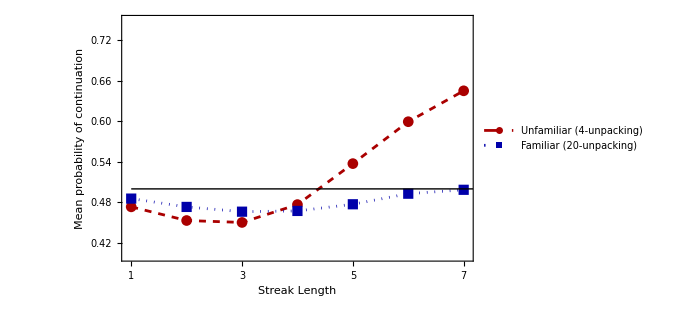
-Graphics-Limited Memory

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*for LONG sequence:*)
(*set the max streak length of interest:*)
maxStrLength=7;

(*create the list of pairs*)
limMemDEEPMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemLONGPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemDEEPPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemLONGProbCont=Table[indPost.contLikes,{indPost,updatedLimMemLONGPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemLONGProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]



(*for SHORT sequence:*)
(*set the max streak length of interest:*)
maxStrLength=7;

(*create the list of pairs*)
limMemSHALLOWMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemSHORTPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemSHALLOWPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemSHORTProbCont=Table[indPost.contLikes,{indPost,updatedLimMemSHORTPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemSHORTProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]


(*put all results in a plot:*)
plot = Labeled[ListLinePlot[
{limMemSHALLOWMeanProbContByStrLength,limMemDEEPMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{{Darker[Red],Dashed},{Darker[Blue],Dotted}},
PlotMarkers->{Automatic},
PlotLegends->Placed[{
"Unfamiliar (4-unpacking)","Familiar (20-unpacking)"},{0.25,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_familiarity.pdf",plot];
```

### Fallacious Feature #4: Too Switchy

I’ll now turn to showing how both limited data (conditioning on a short, full sequence) and limited memory (conditioning on a partially-memory-unpacked long sequence) leads to our four features.

First: the finding that people generate “random” sequences that are too switchy, and the rate increases with streak length

#### Empirical Data

From Rapoport and Budescu 1997 (via Rabin 2002, 781) we have the following overall and by-streak-length rates of streaks continuing in production tasks:

```mathematica
(*set empirical rates*)
empContRates = {{1,0.460},{2,0.380},{3,0.298}};
empContOverall = 0.415;
plotEmpContOverall = {{1,0.415},{3,0.415}};
```

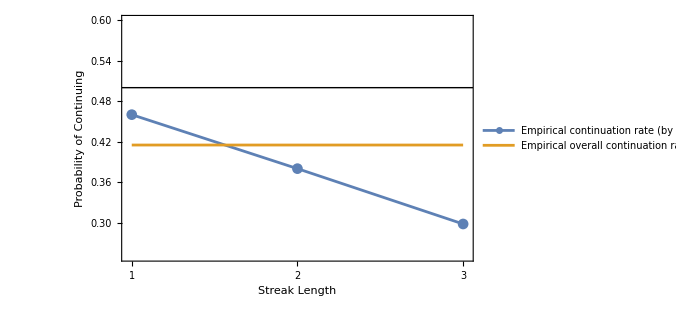
-Graphics-Empirical Continuation Rates (Rapoport & Budescu 1997)

```mathematica
(*put all results in a plot:*)
plot=Labeled[ListLinePlot[
{empContRates,
plotEmpContOverall},
PlotRange->{{0.98,3.02},{0.6,0.25}},
PlotStyle->{Normal,Normal},
PlotMarkers->{Automatic,None},
PlotLegends->Placed[{
"Empirical continuation rate (by streak length)", 
"Empirical overall continuation rate"},{0.35,0.15}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Probability of Continuing",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{{1,2,3},None}},
Epilog->{Thin,Line[{{0,0.5},{5,0.5}}]},
ImageSize->500],
Style["Empirical Continuation Rates (Rapoport & Budescu 1997)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],{Top}];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/emp_cont_rates.pdf",plot];
```

#### Setup

To generate realistic sequences, we have our agents sample from their posteriors

```mathematica
(*set chainList to default to the one we've been using:*)
chainList={swi5,ste5,sti5};
```

```mathematica
(*define a function that takes a posterior distribution over Switchy/Steady/Sticky, a list of the 3 chains, and a desired sequence-length, and generates a hypothetical sequence step by step by sampling from the posterior:*)

(*post = posterior;
chainList = list of markov chains;
seqLength = desired sequence length;
numSamps = number of samples drawn from posterior at each stage.  
If numSamps=1, this is probability-matching*)

getPostSampedSeq[post_,chainList_,seqLength_,numSamps_]:=(

genSeqLength = seqLength;


(*initialize squence randomly:*)
seq = {RandomChoice[{0,1}]};

(*generate sequence iteratively:*)
Do[
(*get current state of chain*)
curState=getInstantChainState[chainList[[1]],seq];

(*get credence in tails, given posterior and current state of chain*)
credTails=post.(getProbTails[#,curState]&/@chainList);

(*sample numSamps times from posterior*)
postSamps = RandomChoice[{credTails,1-credTails}->{0,1},numSamps];

(*if mean (mode) of samples is below 1/2, predict tails; if above, predict heads; if equal, randomize:*)
If[Mean[postSamps]<0.5,newPred=0];
If[Mean[postSamps]==0.5,newPred=RandomChoice[{0,1}]];
If[Mean[postSamps]>0.5,newPred=1];

(*append prediction to sequence*)
AppendTo[seq,newPred];

(*iterate to desired sequence length, subtracting 1 for the initial random one*)
,genSeqLength-1];

(*record sequence*)
Return[seq]
)
```

```mathematica
(*example switching rates*)
numSamps = 1;
(*if very confident of Switchy:*)
Mean[Table[getNumSwitches[getPostSampedSeq[{0.8,0.1,0.1},chainList,50,numSamps]]/(50-1)//N,200]]
(*if very confident of Sticky:*)
Mean[Table[getNumSwitches[getPostSampedSeq[{0.1,0.1,0.8},chainList,50,numSamps]]/(50-1)//N,200]]
```

0.593367

0.356224

```mathematica
(*example switching rates*)
numSamps = 20;
(*if very confident of Switchy:*)
Mean[Table[getNumSwitches[getPostSampedSeq[{0.8,0.1,0.1},chainList,50,numSamps]]/(50-1)//N,200]]
(*if very confident of Sticky:*)
Mean[Table[getNumSwitches[getPostSampedSeq[{0.1,0.1,0.8},chainList,50,numSamps]]/(50-1)//N,200]]
```

0.738061

0.0221429

Observe how likely agents are to generate a hit, based on their credence and the number of samples they draw:

```mathematica
(*iterate through noise levels; plot rates of generating heads as a function of true probability of heads (credHeads)*)

plotList={};
Do[

(*set noise level*)
numSamps = indSamps;

(*iterate through credences in heads, record rate of heads generation:*)
listCredAndGenRate=Table[
credTails=indCredTails;
credHeads = 1-credTails;

(*get rate of heads generation after that many samples)*)
Mean[Table[

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{credTails,credHeads}->{0,1},numSamps];


(*generate a heads (1) if mean of postSamps is above 0.5:*)
If[Mean[postSamps]>0.5,newOutcome=1];
If[Mean[postSamps]==0.5,newOutcome=RandomChoice[{0,1}]];
If[Mean[postSamps]<0.5,newOutcome=0];

(*record true credence in heads and whether generated a heads*)
{credHeads,newOutcome},20000]]//N
,{indCredTails,Range[0,1,0.05]}];

AppendTo[plotList,listCredAndGenRate];


(*iterate through noise levels*)
,{indSamps,{1,5,20,50}}]
```

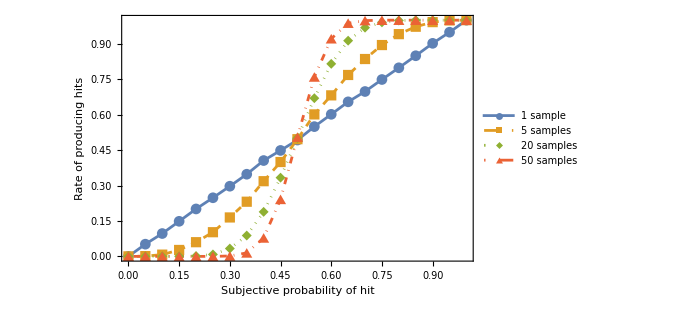
-Graphics-Rate of producing hits, by subjective probability and sample size

```mathematica
Print[plot=Labeled[
ListLinePlot[plotList,
PlotRange->{Automatic,Automatic},
Frame->{True,True,False,False},
FrameLabel->{Style["Subjective probability of hit",FontSize->12],Style["Rate of producing hits",FontSize->12]},
PlotMarkers->Automatic,
PlotStyle->{Normal, Dashed, Dotted, DotDashed},
PlotLegends->Placed[{"1 sample","5 samples","20 samples","50 samples"},{0.15,0.8}],
ImageSize->500]
,Style["Rate of producing hits, by subjective probability and sample size",FontFamily->"Arial",FontWeight->Bold,FontSize->14],{Top}]
];
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/posterior_sampling_production.pdf",plot];
```

#### Limited Data:

```mathematica
(*get list of posteriors for agents who see limited data*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=50;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*mean posteriors:*)
Mean[simPosts[seqLength]]
```

{0.198758,0.743603,0.057639}

```mathematica
(*use 1 sample (PROBABILITY MATCHING) to randomly generate sequences from random agents' posteriors*)
numSamps = 1;
genSeqList=Table[
(*get a random posterior:*)
post = RandomChoice[simPosts[seqLength]];

(*how long sequences to generate?*)
genSeqLength = 50;

(*get the sequence:*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps]

(*iterate through the desired number of agents*)
,5000];


(*output mean continuation rate along with a confidence interval. 
Note that the highest possible number of switches for a sequence of length genSeqLength is genSeqLength - 1.*)
propSwitches = (getNumSwitches[#]/(genSeqLength-1)//N)&/@genSeqList;
propConts = 1-propSwitches;
limDataProbMatchOverallCont=Mean[propConts]
MeanCI[propConts]
```

0.484996

{0.482591,0.487401}

Now generating more samples—say, numSamps = 20:

```mathematica
(*randomly generate sequences from random agents' posteriors*)
numSamps=20;

genSeqList=Table[
(*get a random posterior:*)
post = RandomChoice[simPosts[seqLength]];

(*how long sequences to generate?*)
genSeqLength = 50;

(*get the sequence:*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps]

(*iterate through the desired number of agents*)
,10000];


(*output mean continuation rate along with a confidence interval*)
propSwitches = (getNumSwitches[#]/(genSeqLength-1)//N)&/@genSeqList;
propConts = 1-propSwitches;
limDataNoiseOverallCont=Mean[propConts]
MeanCI[propConts]
```

0.464278

{0.46108,0.467475}

Turning to decreasing rates of continuations, we can see a base effect with probability-matched sequences:

```mathematica
(*how long sequences to generate?*)
genSeqLength = 50;
numSamps = 1;

(*randomly grab sequences from agent's priors, put proportions of switches after streak-lengths 1,2,3 in a list:*)
listOfProportions=Table[

(*make variables to count numbers of each streak-length and number of times switches from that*)
Do[
(*how many streaks of a given length? Plus 1 to make nonzero for now*)
strLenCt[ind]=0; 
(*how many streaks of that length switch?*)
strLenSwitch[ind]=0;
,{ind,genSeqLength}];


(* get a random sequence from a random posterior:*)
(*get a random posterior:*)
post = RandomChoice[simPosts[seqLength]];



(*get the sequence*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps];


(*increment counts by running through sequence:*)
Do[
(*get initial seqment*)
subSeq = sampSeq[[;;indSubSeq]];
(*get current streak*)
getCurStreak[subSeq];
(*record whether switches on next toss:*)
isSwi=Boole[sampSeq[[indSubSeq]]!=sampSeq[[indSubSeq+1]]];

(*increment count and switch if it does*)
strLenCt[curStr]+=1;
strLenSwitch[curStr]+=isSwi;
,{indSubSeq,genSeqLength-1}];

(*If instance of streak length, record:
NOTE: uses getMaxStrLength on the sequence dropping the last entry, since no record of whether that one switches*)

Table[strLenSwitch[indStr]/strLenCt[indStr]//N,{indStr,Min[3,getMaxStrLength[sampSeq[[;;-2]]]]}]

,{indCt,15000}];

(*pad the list so that any sequence with max Streak < 3 gets a "1" for the third position. This is rare*)
paddedList=PadRight[listOfProportions,Automatic,1];

(*Record mean switching rates*)
means=Mean[paddedList];
(*flip to continuations:*)
meanConts = 1-means

limDataProbMatchContByStr = Table[{ind,meanConts[[ind]]},{ind,3}]
```

{0.498528,0.484548,0.472149}

{{1,0.498528},{2,0.484548},{3,0.472149}}

Again we see the right qualitative trend, but quantitatively shallow.
It becomes more realistic (though still shallow) when we take more samples from the posterior:

```mathematica
(*how long sequences to generate?*)
genSeqLength = 50;
(*how many samples?*)
numSamps = 20;

(*randomly grab sequences from agent's priors, put proportions of switches after streak-lengths 1,2,3 in a list:*)
listOfProportions=Table[

(*make variables to count numbers of each streak-length and number of times switches from that*)
Do[
(*how many streaks of a given length? Plus 1 to make nonzero for now*)
strLenCt[ind]=0; 
(*how many streaks of that length switch?*)
strLenSwitch[ind]=0;
,{ind,genSeqLength}];


(* get a random sequence from a random posterior:*)
(*get a random posterior:*)
post = RandomChoice[simPosts[seqLength]];



(*get the sequence*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps];

(*increment counts by running through sequence:*)
Do[
(*get initial seqment*)
subSeq = sampSeq[[;;indSubSeq]];
(*get current streak*)
getCurStreak[subSeq];
(*record whether switches on next toss:*)
isSwi=Boole[sampSeq[[indSubSeq]]!=sampSeq[[indSubSeq+1]]];

(*increment count and switch if it does*)
strLenCt[curStr]+=1;
strLenSwitch[curStr]+=isSwi;
,{indSubSeq,genSeqLength-1}];

(*Record rate of switching at various streak lengths, up to 3:
NOTE: uses getMaxStrLength on the sequence dropping the last entry, since no record of whether that one switches*)
Table[strLenSwitch[indStr]/strLenCt[indStr]//N,{indStr,Min[3,getMaxStrLength[sampSeq[[;;-2]]]]}]

,{indCt,10000}];

(*pad the list so that any sequence with max Streak < 3 gets a "1" for the third position. This is rare*)
paddedList=PadRight[listOfProportions,Automatic,1];

(*Record mean switching rates*)
means=Mean[paddedList];
(*flip to continuations:*)
meanConts = 1-means

limDataNoiseContByStr = Table[{ind,meanConts[[ind]]},{ind,3}]
```

{0.475251,0.440065,0.41777}

{{1,0.475251},{2,0.440065},{3,0.41777}}

Plotting a summary of results for limited data:

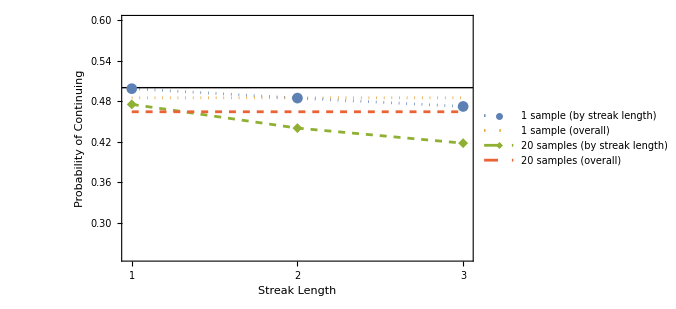
-Graphics-Limited Data (50-sequence)

```mathematica
(*put overall rates in plot form:*)
plotLimDataProbMatchOverall={{1,limDataProbMatchOverallCont},{3,limDataProbMatchOverallCont}};
plotLimDataNoiseOverall={{1,limDataNoiseOverallCont},{3,limDataNoiseOverallCont}};

(*put all results in a plot:*)
plot=Labeled[ListLinePlot[
{limDataProbMatchContByStr,
plotLimDataProbMatchOverall,
limDataNoiseContByStr,
plotLimDataNoiseOverall},
PlotRange->{{0.98,3.02},{0.6,0.25}},
PlotStyle->{Dotted,Dotted,Dashed,Dashed},
PlotMarkers->{Automatic,None},
PlotLegends->Placed[{
"1 sample (by streak length)", 
"1 sample (overall)",
"20 samples (by streak length)",
"20 samples (overall)"},{0.25,0.15}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Probability of Continuing",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{{1,2,3},None}},
Epilog->{Thin,Line[{{0,0.5},{5,0.5}}]},
ImageSize->500],
Style["Limited Data (50-sequence)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_cont_rates.pdf",plot];
```

#### Limited memory:

We get the same trends (but more extreme) using limited-depth memory unpacking.

```mathematica
(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 10;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*mean posteriors*)
Mean[simPosts[unpackDepth]]
```

{0.274552,0.716496,0.00895217}

First, the overall switching rate, with 1 sample:

```mathematica
(*use 1 sample (PROBABILITY MATCHING) to randomly generate sequences from random agents' posteriors*)
numSamps = 1;
genSeqList=Table[
(*get a random posterior:*)
post = RandomChoice[simPosts[unpackDepth]];

(*how long sequences to generate?*)
genSeqLength = 50;

(*get the sequence:*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps]

(*iterate through the desired number of agents*)
,5000];


(*output mean continuation rate along with a confidence interval. 
Note that the highest possible number of switches for a sequence of length genSeqLength is genSeqLength - 1.*)
propSwitches = (getNumSwitches[#]/(genSeqLength-1)//N)&/@genSeqList;
propConts = 1-propSwitches;
limMem1SampOverallCont=Mean[propConts]
MeanCI[propConts]
```

0.465833

{0.463629,0.468037}

```mathematica
(*randomly generate sequences from random agents' posteriors*)
numSamps=20;

genSeqList=Table[
(*get a random posterior:*)
post = RandomChoice[simPosts[unpackDepth]];

(*how long sequences to generate?*)
genSeqLength = 50;

(*get the sequence:*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps]

(*iterate through the desired number of agents*)
,10000];


(*output mean continuation rate along with a confidence interval*)
propSwitches = (getNumSwitches[#]/(genSeqLength-1)//N)&/@genSeqList;
propConts = 1-propSwitches;
limMem20SampOverallCont=Mean[propConts]
MeanCI[propConts]
```

0.405073

{0.402766,0.407381}

Now increasing-rates of switchy-ness:

With 1 sample:

```mathematica
(*how long sequences to generate?*)
genSeqLength = 50;
numSamps = 1;

(*randomly grab sequences from agent's priors, put proportions of switches after streak-lengths 1,2,3 in a list:*)
listOfProportions=Table[

(*make variables to count numbers of each streak-length and number of times switches from that*)
Do[
(*how many streaks of a given length? Plus 1 to make nonzero for now*)
strLenCt[ind]=0; 
(*how many streaks of that length switch?*)
strLenSwitch[ind]=0;
,{ind,genSeqLength}];


(* get a random sequence from a random posterior:*)
(*get a random posterior:*)
post = RandomChoice[simPosts[unpackDepth]];



(*get the sequence*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps];


(*increment counts by running through sequence:*)
Do[
(*get initial seqment*)
subSeq = sampSeq[[;;indSubSeq]];
(*get current streak*)
getCurStreak[subSeq];
(*record whether switches on next toss:*)
isSwi=Boole[sampSeq[[indSubSeq]]!=sampSeq[[indSubSeq+1]]];

(*increment count and switch if it does*)
strLenCt[curStr]+=1;
strLenSwitch[curStr]+=isSwi;
,{indSubSeq,genSeqLength-1}];

(*If instance of streak length, record:
NOTE: uses getMaxStrLength on the sequence dropping the last entry, since no record of whether that one switches*)

Table[strLenSwitch[indStr]/strLenCt[indStr]//N,{indStr,Min[3,getMaxStrLength[sampSeq[[;;-2]]]]}]

,{indCt,15000}];

(*pad the list so that any sequence with max Streak < 3 gets a "1" for the third position. This is rare*)
paddedList=PadRight[listOfProportions,Automatic,1];

(*Record mean switching rates*)
means=Mean[paddedList];
(*flip to continuations:*)
meanConts = 1-means

limMem1SampContByStr = Table[{ind,meanConts[[ind]]},{ind,3}]
```

{0.487941,0.464568,0.444528}

{{1,0.487941},{2,0.464568},{3,0.444528}}

With 20 samples:

```mathematica
(*how long sequences to generate?*)
genSeqLength = 50;
numSamps = 20;

(*randomly grab sequences from agent's priors, put proportions of switches after streak-lengths 1,2,3 in a list:*)
listOfProportions=Table[

(*make variables to count numbers of each streak-length and number of times switches from that*)
Do[
(*how many streaks of a given length? Plus 1 to make nonzero for now*)
strLenCt[ind]=0; 
(*how many streaks of that length switch?*)
strLenSwitch[ind]=0;
,{ind,genSeqLength}];


(* get a random sequence from a random posterior:*)
(*get a random posterior:*)
post = RandomChoice[simPosts[unpackDepth]];



(*get the sequence*)
sampSeq=getPostSampedSeq[post,chainList,genSeqLength,numSamps];


(*increment counts by running through sequence:*)
Do[
(*get initial seqment*)
subSeq = sampSeq[[;;indSubSeq]];
(*get current streak*)
getCurStreak[subSeq];
(*record whether switches on next toss:*)
isSwi=Boole[sampSeq[[indSubSeq]]!=sampSeq[[indSubSeq+1]]];

(*increment count and switch if it does*)
strLenCt[curStr]+=1;
strLenSwitch[curStr]+=isSwi;
,{indSubSeq,genSeqLength-1}];

(*If instance of streak length, record:
NOTE: uses getMaxStrLength on the sequence dropping the last entry, since no record of whether that one switches*)

Table[strLenSwitch[indStr]/strLenCt[indStr]//N,{indStr,Min[3,getMaxStrLength[sampSeq[[;;-2]]]]}]

,{indCt,15000}];

(*pad the list so that any sequence with max Streak < 3 gets a "1" for the third position. This is rare*)
paddedList=PadRight[listOfProportions,Automatic,1];

(*Record mean switching rates*)
means=Mean[paddedList];
(*flip to continuations:*)
meanConts = 1-means

limMem20SampContByStr = Table[{ind,meanConts[[ind]]},{ind,3}]
```

{0.435807,0.373762,0.322946}

{{1,0.435807},{2,0.373762},{3,0.322946}}

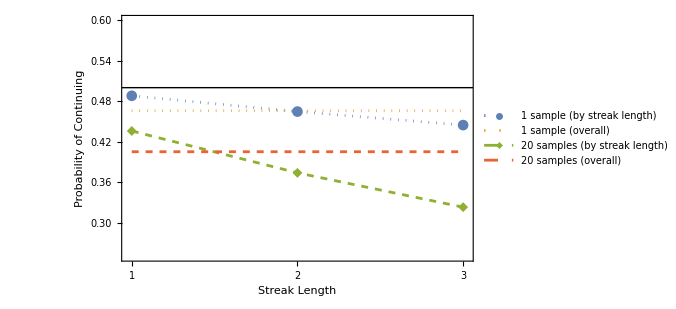
-Graphics-Limited Memory (10-unpacking)

```mathematica
(*put overall rates in plot form:*)
plotLimMemProbMatchOverall={{1,limMem1SampOverallCont},{3,limMem1SampOverallCont}};
plotLimMemNoiseOverall={{1,limMem20SampOverallCont},{3,limMem20SampOverallCont}};


(*put all results in a plot:*)
plot=Labeled[ListLinePlot[
{limMem1SampContByStr,
plotLimMemProbMatchOverall,
limMem20SampContByStr,
plotLimMemNoiseOverall},
PlotRange->{{0.98,3.02},{0.6,0.25}},
PlotStyle->{Dotted,Dotted,Dashed,Dashed},
PlotMarkers->{Automatic,None},
PlotLegends->Placed[{
"1 sample (by streak length)", 
"1 sample (overall)",
"20 samples (by streak length)",
"20 samples (overall)"},{0.25,0.15}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Probability of Continuing",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{{1,2,3},None}},
Epilog->{Thin,Line[{{0,0.5},{5,0.5}}]},
ImageSize->500],
Style["Limited Memory (10-unpacking)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],{Top}];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_cont_rates.pdf",plot];
```

### Fallacious Feature #5: Format Dependence

Our fourth feature is that rates of gambler’s reasoning (and their nonlinear trends) look much starker when we look at the proportion of subjects who predict a switch than when we look at their mean probability estimates.

This interacts with both the nonlinearity finding (#2) and the variable rates finding (#3).

```mathematica
(*set chainList to default to the one we've been using:*)
chainList={swi5,ste5,sti5};

(*put likelihoods in lists*)
chainSeqLikes = {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes};
chainPropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

#### Limited Data

```mathematica
(*get posteriors for LONG-sequence agents*)
(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*Set the sequence length to condition on*)
seqLength=50;

(*simulate the posteriors of Bayesian agents who condition on such sequences*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swi5SeqLikes[seq],ste5SeqLikes[seq],sti5SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10000 times to get an average belief over the simulations*)
10000];

(*label the posteriors*)
limDataPosts = simPosts[seqLength];

(*mean posteriors:*)
Mean[limDataPosts]
```

{0.196661,0.747446,0.0558925}

```mathematica
(*get a list of updated posteriors on a random sequence, record both PROBABILITY ESTIMATE (via sampling) of and RATE OF PREDICTING (via sampling) continuation*)

(*set number of samples to pull from posterior:*)
numSamps = 20;

(*first get probabilities of switching given random sequences:*)
limDataProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},seqLength];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limDataPosts}];

(*get realized probability estimates via sampling:*)
limDataNoisyProbConts = Table[

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{1-indProbCont,indProbCont}->{0,1},numSamps];

Mean[postSamps]//N
,{indProbCont,limDataProbConts}];


(*record mean probability with a confidence interval*)
{Mean[limDataNoisyProbConts],MeanCI[limDataNoisyProbConts]}

(*record whether predict continuation, setting to 0.5 if prob estimate is exactly 50%*)
limDataNoisyPredConts=(Boole[#>0.5] + 0.5Boole[#==0.5]&/@limDataNoisyProbConts);
(*record rate of predicting continuations with a confidence interval*)
{Mean[limDataNoisyPredConts],MeanCI[limDataNoisyPredConts]}
```

{0.48417,{0.48176,0.48658}}

{0.4445,{0.435584,0.453416}}

```mathematica
(*create a list of pairs of streak length and updated MEAN PROBABILITY ESTIAMTE and PROPORTION PREDICTING that the streak will continue*)

(*set number of samples*)
numSamps = 20;

(*set the max streak length of interest:*)
maxStrLength=7;

(*initialize lists to store results*)
limDataPropPredContByStrLength={};
limDataMeanProbContByStrLength={};

(*run through streak lengths to populate lists*)
Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimDataPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

(*get updated posterior probabilities of continuation, plus noise:*)
updatedLimDataNoisyProbCont=Table[
(*get probability of continuing*)
probCont = indPost.contLikes;

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{1-probCont,probCont}->{0,1},numSamps];

(*get mean of sample for probability estimate:*)
Mean[postSamps]//N

,{indPost,updatedLimDataPosts}];

(*record who predicts continuations, i.e. another 0, plus noise*)
updatedLimDataPreds = Table[Boole[indProbCont>0.5] + 0.5*Boole[indProbCont==0.5],{indProbCont,updatedLimDataNoisyProbCont}];

(*Append confidence-interval results to lists*)
AppendTo[limDataMeanProbContByStrLength,{strLength,aroundCI[updatedLimDataNoisyProbCont]}];
AppendTo[limDataPropPredContByStrLength,{strLength,aroundCI[updatedLimDataPreds]}];

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}];


limDataMeanProbContByStrLength
limDataPropPredContByStrLength
```

{{1,0.48550.00230.0023},{2,0.47770.00240.0024},{3,0.47460.00260.0026},{4,0.48640.00280.0028},{5,0.52200.00300.0030},{6,0.55790.00280.0028},{7,0.58660.00280.0028}}

{{1,0.4560.0090.009},{2,0.4310.0090.009},{3,0.4290.0090.009},{4,0.4650.0090.009},{5,0.5520.0090.009},{6,0.6410.0090.009},{7,0.7130.0080.008}}

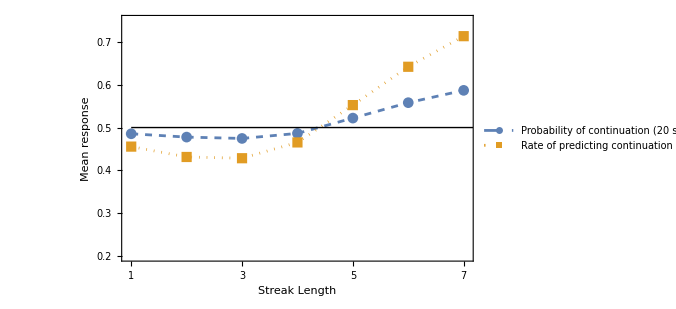
-Graphics-Limited Data (50-sequence)

```mathematica
(*plot the results*)
plot=Labeled[ListLinePlot[
{limDataMeanProbContByStrLength,limDataPropPredContByStrLength},
PlotRange->{{0.95,7.05},{0.2,0.75}},
PlotStyle->{Dashed,Dotted},
PlotMarkers->{Automatic},
PlotLegends->Placed[{
"Probability of continuation (20 samples)", 
"Rate of predicting continuation (20 samples)"},{0.35,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean response",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Data (50-sequence)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_format_dependence.pdf",plot];
```

#### Limited Memory

```mathematica
(*get agents with DEEP unpacking:*)

(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 5;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.357337,0.58326,0.059403}

{0.473824,0.452826,0.6024}

{0.3143,0.2584,0.7786}

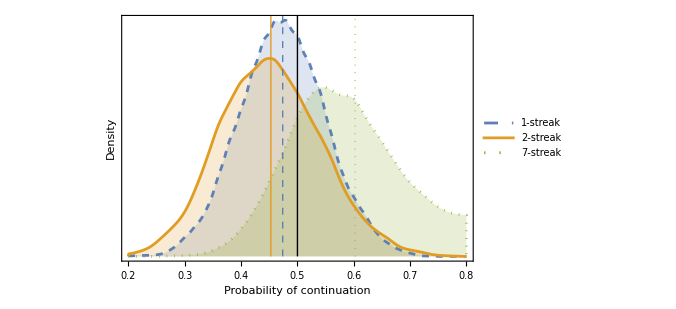
-Graphics-Limited Memory, distributions of probabilities of continuation

```mathematica
(*What does distribution of continuation probabilities look like after a short vs long streak? 
(run this with above as 5-unpacking and 50 samples to make the differences more visible)*)

(*set number of samples*)
numSamps = 50;

(*iterate through streak lengths to populate the lists*)
listAllProbContsByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)
(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

updatedLimMemNoisyProbCont=Table[
(*get probability of continuing*)
probCont = indPost.contLikes;

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{1-probCont,probCont}->{0,1},numSamps];

(*get mean of sample for probability estimate:*)
Mean[postSamps]//N

,{indPost,updatedLimMemPosts}]

,{indStrLength,{1,2,7}}];

Mean[#]&/@listAllProbContsByStrLength
Count[#,x_/;x>0.5]/10000&/@listAllProbContsByStrLength//N

(*plot the results*)
plot=Labeled[SmoothHistogram[listAllProbContsByStrLength,
Filling->Axis,
PlotStyle->{Dashed,Normal,Dotted},
PlotRange->{{0.2,0.8},Automatic},
PlotLegends->Placed[{"1-streak", "2-streak","7-streak"},{0.85,0.8}],
Frame->{{True,False},{True,False}},
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{{Style["Density",FontSize->12],None},{Style["Probability of continuation",FontSize->12],None}},
Epilog->{{Thin,Line[{{0.5,0},{0.5,10^6}}]},
{Dashed,RGBColor[0.368417, 0.506779, 0.709798],Line[{{Mean[listAllProbContsByStrLength[[1]]],0},{Mean[listAllProbContsByStrLength[[1]]],10^6}}]},
{RGBColor[0.880722, 0.611041, 0.142051],Line[{{Mean[listAllProbContsByStrLength[[2]]],0},{Mean[listAllProbContsByStrLength[[2]]],10^6}}]},
{Dotted,RGBColor[0.560181, 0.691569, 0.194885],Thick,Line[{{Mean[listAllProbContsByStrLength[[3]]],0},{Mean[listAllProbContsByStrLength[[3]]],10^6}}]}
},
ImageSize->500
],
Style["Limited Memory, distributions of probabilities of continuation",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/format_dependence_bell_curves.pdf",plot];
```

```mathematica
(*get agents with DEEP unpacking:*)

(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 10;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,chain5PropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.270724,0.720004,0.00927236}

```mathematica
(*set number of samples*)
numSamps = 20;

(*get a list of updated sequence posteriors on a random sequence, record both PROBABILITY ESTIMATE and RATE OF PREDICTING continuation*)
limMemProbConts=Table[ 
(*run through the posteriors:*)
post =indPost;

(*get a random sequence*)
seqLength = 5;
seq = RandomChoice[{0,1},seqLength];

(*get sequence likelihoods:*)
likes = (#[seq]&/@chainSeqLikes);

(*update posterior on sequence:*)
updatedPost=(post*likes)/(post.likes);

(*get chain state and likelihoods of continuation*)
curState=getInstantChainState[chainList[[1]],seq];
If[seq[[-1]]==0,contLikes=(getProbTails[#,curState]&/@chainList)];
If[seq[[-1]]==1,contLikes=1-(getProbTails[#,curState]&/@chainList)];

(*get posterior probability of continuation*)
probCont = updatedPost.contLikes

(*iterate through posteriors*)
,{indPost,limMemPosts}];

(*get realized probability estimates via sampling:*)
limMemNoisyProbConts = Table[

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{1-indProbCont,indProbCont}->{0,1},numSamps];

Mean[postSamps]//N
,{indProbCont,limMemProbConts}];

(*record mean probability with a confidence interval*)
{Mean[limMemNoisyProbConts],MeanCI[limMemNoisyProbConts]}

(*record whether predict continuation, setting to 0.5 if prob estimate is exactly 50%*)
limMemNoisyPredConts=(Boole[#>0.5] + 0.5Boole[#==0.5]&/@limMemNoisyProbConts);
(*record rate of predicting continuations with a confidence interval*)
{Mean[limMemNoisyPredConts],MeanCI[limMemNoisyPredConts]}
```

{0.4682,{0.465842,0.470558}}

{0.3979,{0.389168,0.406632}}

{{1,0.47730.00220.0022},{2,0.45830.00240.0024},{3,0.44840.00250.0025},{4,0.45440.00260.0026},{5,0.47470.00250.0025},{6,0.50260.00240.0024},{7,0.51390.00240.0024}}

{{1,0.4210.0090.009},{2,0.3680.0090.009},{3,0.3540.0090.009},{4,0.3700.0090.009},{5,0.4260.0090.009},{6,0.5010.0090.009},{7,0.5330.0090.009}}

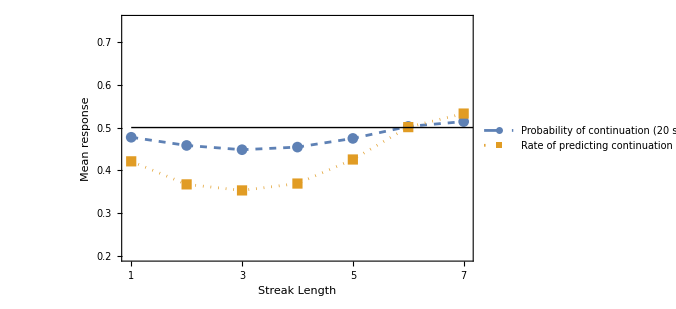
-Graphics-Limited Memory (10-unpacking)

```mathematica
(*create a list of pairs of streak length and updated proportion predicting that the streak will continue*)

(*set number of samples from posterior. If =1, probability matching*)
numSamps =20;

(*set the max streak length of interest:*)
maxStrLength=7;


(*initialize lists to store results*)
limMemMeanProbContByStrLength={};
limMemPropPredContByStrLength={};


(*iterate through streak lengths to populate the lists*)
Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@chainSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)
(*current chain state*)
curState = getInstantChainState[chainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@chainList;

updatedLimMemNoisyProbCont=Table[
(*get probability of continuing*)
probCont = indPost.contLikes;

(*get numSamps samples from that posterior:*)
postSamps = RandomChoice[{1-probCont,probCont}->{0,1},numSamps];

(*get mean of sample for probability estimate:*)
Mean[postSamps]//N

,{indPost,updatedLimMemPosts}];


(*record who predicts continuations, i.e. another 0*)
updatedLimMemPreds = Table[Boole[indProbCont>0.5]+0.5*Boole[indProbCont==0.5],{indProbCont,updatedLimMemNoisyProbCont}];


(*Append {strlength, confidence-interval} results to each list*)
AppendTo[limMemMeanProbContByStrLength,{strLength,aroundCI[updatedLimMemNoisyProbCont]}];
AppendTo[limMemPropPredContByStrLength,{strLength,aroundCI[updatedLimMemPreds]}];

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}];

(*output results*)
limMemMeanProbContByStrLength
limMemPropPredContByStrLength

(*plot the results*)
plot=Labeled[ListLinePlot[
{limMemMeanProbContByStrLength,limMemPropPredContByStrLength},
PlotRange->{{0.95,7.05},{0.2,0.75}},
PlotStyle->{Dashed,Dotted},
PlotMarkers->{Automatic},
PlotLegends->Placed[{
"Probability of continuation (20 samples)", 
"Rate of predicting continuation (20 samples)"},{0.35,0.85}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean response",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory (10-unpacking)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_format_dependence.pdf",plot];
```

### Objection: Non-50% long-run hit rates:

#### Generating chains:

I haven’t found an efficient analytic way to generate chains of the desired long-run hit rate, but we can easily get approximations

```mathematica
(*get a instant fall chain of a desired hit rate with a certain minimal maximum deviation from that hit rate*)

(*wantHR = desired long-run hit rate (stationary) of heads (1);
memLength = what's longest streak it tracks;
chainType = "swi" or "sti";
minDev = how far is minimal deviation at max streak from wantHR;
*)

getNon50InstantChain[wantHR_,memLength_,minDev_,chainType_]:=(

randHR = 0;
(*make deviation integer value for nice numbers*)
minDevInt=Round[minDev*100];

(*initialize a counter for a While loop*)
ticker=0;
(*get a random instant fall chain; check if close enough *)
While[Abs[randHR-wantHR]>0.005,
(*iterate counter; break loop if takes too long*)
ticker+=1;
If[ticker>100000,Print["Error: could not achieve desired hit rate"];Break[]];

(*get random deviations from hit rate:*)
(*degree heads probability can increase*)
maxUpInt=Round[(1-wantHR)*100];
upShift = RandomInteger[{minDevInt,maxUpInt}]/100//N;
(*degree heads prob can decrease*)
maxDownInt = Round[wantHR*100];
downShift = RandomInteger[{minDevInt,maxDownInt}]/100//N;

(*get probabilities of tails (0) at each level of streak, depending on chain type*)
If[chainType=="swi",
probsTailsAtEachStr=
Join[
Sort[Table[(1-wantHR)-ind*upShift/memLength,{ind,1,memLength}]],
Table[(1-wantHR)+ind*downShift/memLength,{ind,1,memLength}]
]
];
If[chainType=="sti",
probsTailsAtEachStr=
Join[
ReverseSort[Table[(1-wantHR)+ind*downShift/memLength,{ind,1,memLength}]],
Table[(1-wantHR)-ind*upShift/memLength,{ind,1,memLength}]
]
];

(*get overall chain length*)
chainLength=2*memLength;
(*get markov chain:*)
chain = Join[
(*set state 1 (long tails streak) transition probabilities:*)
{ReplacePart[Table[0,chainLength],{1->probsTailsAtEachStr[[1]],memLength+1->1-probsTailsAtEachStr[[1]]}]},
(*set intermediate tails-streak transition probabilities:*)
Table[ReplacePart[Table[0,chainLength],{ind-1->probsTailsAtEachStr[[ind]],memLength+1->1-probsTailsAtEachStr[[ind]]}],{ind,2,memLength}],
(*set intermediate heads-streak transition probabilities:*)
Table[ReplacePart[Table[0,chainLength],{memLength->probsTailsAtEachStr[[ind]],ind+1->1-probsTailsAtEachStr[[ind]]}],{ind,memLength+1,chainLength-1}],
(*set state chainLength (long heads streak) transition probabilities*)
{ReplacePart[Table[0,chainLength],{memLength->probsTailsAtEachStr[[chainLength]],chainLength->1-probsTailsAtEachStr[[chainLength]]}]}
];

(*check long-run hit rate*)
(*get vector of stationary distribution:*)
stationaryChain=MatrixPower[chain,100][[1]];
(*chcek long-run hit rate:*)
randHR  =Total[stationaryChain[[memLength+1;;chainLength]]];
];

Return[chain]
)
```

```mathematica
(*get a non-50% hit rate STEADY chain:*)
getNon50InstantSteady[wantHR_,memLength_]:=(
chainLength = 2*memLength;
chain = Join[
(*set state 1 (long tails streak) transition probabilities:*)
{ReplacePart[Table[0,chainLength],{1->1-wantHR,memLength+1->wantHR}]},
(*set intermediate tails-streak transition probabilities:*)
Table[ReplacePart[Table[0,chainLength],{ind-1->1-wantHR,memLength+1->wantHR}],{ind,2,memLength}],
(*set intermediate heads-streak transition probabilities:*)
Table[ReplacePart[Table[0,chainLength],{memLength->1-wantHR,ind+1->wantHR}],{ind,memLength+1,chainLength-1}],
(*set state chainLength (long heads streak) transition probabilities*)
{ReplacePart[Table[0,chainLength],{memLength->1-wantHR,chainLength->wantHR}]}
];
Return[chain]
)
```

```mathematica
(*testing*)
Do[
wantHR = RandomReal[{0.3,0.7}];
minDev = RandomReal[{0.05,0.15}];
memLength=RandomInteger[{2,4}];
chainType=RandomChoice[{"swi","sti"}];
Print[{wantHR,minDev,chainType,memLength,MatrixForm[getNon50InstantChain[wantHR,memLength,minDev,chainType]],randHR}],
5]
```

{0.508398,0.0743994,swi,2,(0.271602 | 0 | 0.728398 | 0
0.381602 | 0 | 0.618398 | 0
0 | 0.606602 | 0 | 0.393398
0 | 0.721602 | 0 | 0.278398),0.503467}

{0.323743,0.127443,sti,4,(0.866257 | 0 | 0 | 0 | 0.133743 | 0 | 0 | 0
0.818757 | 0 | 0 | 0 | 0.181243 | 0 | 0 | 0
0 | 0.771257 | 0 | 0 | 0.228743 | 0 | 0 | 0
0 | 0 | 0.723757 | 0 | 0.276243 | 0 | 0 | 0
0 | 0 | 0 | 0.551257 | 0 | 0.448743 | 0 | 0
0 | 0 | 0 | 0.426257 | 0 | 0 | 0.573743 | 0
0 | 0 | 0 | 0.301257 | 0 | 0 | 0 | 0.698743
0 | 0 | 0 | 0.176257 | 0 | 0 | 0 | 0.823743),0.323624}

{0.686769,0.0823919,swi,2,(0.103231 | 0 | 0.896769 | 0
0.208231 | 0 | 0.791769 | 0
0 | 0.353231 | 0 | 0.646769
0 | 0.393231 | 0 | 0.606769),0.682173}

{0.471403,0.0928112,sti,3,(0.728597 | 0 | 0 | 0.271403 | 0 | 0
0.66193 | 0 | 0 | 0.33807 | 0 | 0
0 | 0.595264 | 0 | 0.404736 | 0 | 0
0 | 0 | 0.448597 | 0 | 0.551403 | 0
0 | 0 | 0.368597 | 0 | 0 | 0.631403
0 | 0 | 0.288597 | 0 | 0 | 0.711403),0.475083}

{0.394135,0.0915729,swi,2,(0.415865 | 0 | 0.584135 | 0
0.510865 | 0 | 0.489135 | 0
0 | 0.790865 | 0 | 0.209135
0 | 0.975865 | 0 | 0.0241351),0.393123}

#### Asymmetric convergence for known non-50% stationary

```mathematica
(*set parameters:*)
wantHR = 0.45;
minDev = 0.3;
memLength=5;

(*get chains*)
swiNon50 = getNon50InstantChain[wantHR,memLength,minDev,"swi"]
(*print hit rate*)
randHR
(*ignore memory length for steady:*)
steNon50 ={{1-wantHR,wantHR},{1-wantHR,wantHR}}
stiNon50 = getNon50InstantChain[wantHR,memLength,minDev,"sti"]
(*print hit rate*)
randHR
```

{{0.25,0,0,0,0,0.75,0,0,0,0},{0.31,0,0,0,0,0.69,0,0,0,0},{0,0.37,0,0,0,0.63,0,0,0,0},{0,0,0.43,0,0,0.57,0,0,0,0},{0,0,0,0.49,0,0.51,0,0,0,0},{0,0,0,0,0.634,0,0.366,0,0,0},{0,0,0,0,0.718,0,0,0.282,0,0},{0,0,0,0,0.802,0,0,0,0.198,0},{0,0,0,0,0.886,0,0,0,0,0.114},{0,0,0,0,0.97,0,0,0,0,0.03}}

0.451735

{{0.55,0.45},{0.55,0.45}}

{{0.89,0,0,0,0,0.11,0,0,0,0},{0.822,0,0,0,0,0.178,0,0,0,0},{0,0.754,0,0,0,0.246,0,0,0,0},{0,0,0.686,0,0,0.314,0,0,0,0},{0,0,0,0.618,0,0.382,0,0,0,0},{0,0,0,0,0.462,0,0.538,0,0,0},{0,0,0,0,0.374,0,0,0.626,0,0},{0,0,0,0,0.286,0,0,0,0.714,0},{0,0,0,0,0.198,0,0,0,0,0.802},{0,0,0,0,0.11,0,0,0,0,0.89}}

0.448842

```mathematica
(*get sequence likelihoods*)
getInstantSeqLikes[swiNon50SeqLikes,swiNon50]
getInstantSeqLikes[steNon50SeqLikes,steNon50]
getInstantSeqLikes[stiNon50SeqLikes,stiNon50]

non50ChainSeqLikes={swiNon50SeqLikes,steNon50SeqLikes,stiNon50SeqLikes};


(*get proportions likelihoods*)
getInstantPropLikelihoods[swiNon50PropLikes,swiNon50]
steNon50PropLikes[numTosses_,numHeads_]:=PDF[BinomialDistribution[numTosses,wantHR],numHeads]
getInstantPropLikelihoods[stiNon50PropLikes,stiNon50]

non50ChainPropLikes = {swiNon50PropLikes,steNon50PropLikes,stiNon50PropLikes};
```

Plot proportion-heads likelihoods

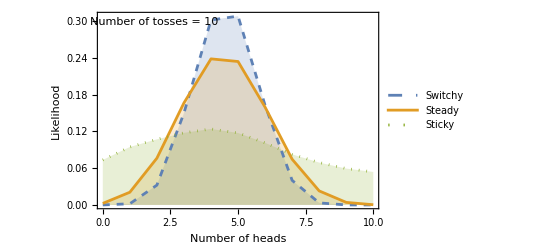

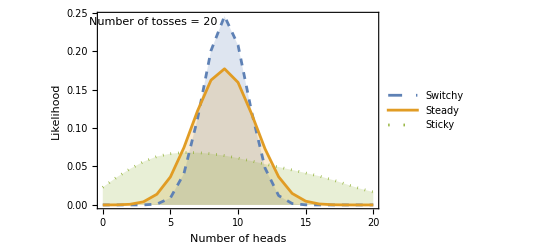

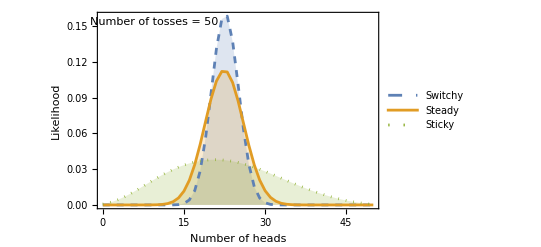

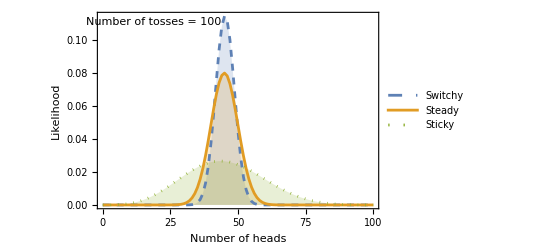

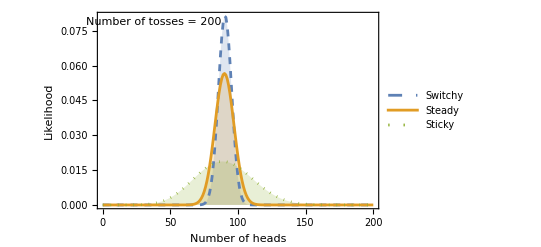

```mathematica
(*Plot likelihoods for various total tosses:*)

(*NOTES
1) the first time you run this, it'll take a few minutes, since swi5PropLikes and sti5PropLikes will needs to recursively calculate likelihoods out to 1000 tosses.  Afterwards it'll run instantly (unless you Clear those functions).
2) You will get a warning that precisino may be lost due to the small likkelihoods at the tails of the distribution. Don't worry about it——we'll virtually never sample from these tails anyways *)

(*iterate through various numbers of tosses:*)
Do[

(*Set the number of total tosses:*)
numTosses = indNumTosses;

(*get a list of {numHeads,likelihood} pairs for each chain:*)
listLikes=Table[{ind,#[numTosses,ind]},{ind,0,numTosses}]&/@non50ChainPropLikes;

(*Plot the three chain's likelihoods:*)
Print[ListLinePlot[listLikes,
Filling->Axis,
PlotRange->Full,
PlotStyle->{Dashed,Normal,Dotted},
PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.8}],
Frame->{True,True,False,False},
FrameLabel->{"Number of heads","Likelihood"},
Epilog->Text["Number of tosses = "<>ToString[numTosses],Scaled[{0.2,0.95}]]]]

(*say what numbers of tosses to iterate through:*)
,{indNumTosses,{10,20, 50,100,200}}]
```

Limited data convergence:

```mathematica
(*First, get a list of various sequence lengths and the average posteriors in {Switchy, Steady, Sticky} upon conditioning on them:*)

(*Define a uniform prior over the three processes:Switchy,Steady,and Sticky*)prior={1/3,1/3,1/3};

(*For various sequence lengths (ranging from 1 to 100),simulate the beliefs of Bayesian agents*)
Timing[seqLengthAndPosts=Table[
(*Set the current sequence length*)
seqLength=indSeqLength;
(*For each sequence length,run a simulation 10,000 times*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform, these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the three processes*)likes={swiNon50SeqLikes[seq],steNon50SeqLikes[seq],stiNon50SeqLikes[seq]};
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process 10,000 times to get an average belief over the simulations*)
10000];
(*Calculate the mean posterior beliefs for Switchy,Steady,and Sticky over the 10,000 simulations*)
means=Mean[simPosts[seqLength]];
(*Store the sequence length and the mean beliefs for each process in a list*)
{indSeqLength,means[[1]],means[[2]],means[[3]]}
(*Repeat the entire simulation for sequence lengths 1,5,10,20,50,and 100*)
,{indSeqLength,{1,5,10,20,30,50}}]]
```

{22.0253,{{1,0.333333,0.333333,0.333333},{5,0.338962,0.340289,0.320749},{10,0.348941,0.384011,0.267048},{20,0.319159,0.480068,0.200773},{30,0.283747,0.567184,0.149069},{50,0.208282,0.718779,0.0729391}}}

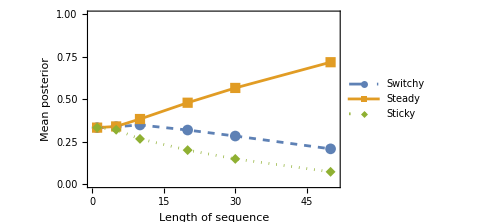

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)

(*Define the maximum sequence length to be used for setting the plot's x-axis range*)
maxSeqLength=50;

(*Extract Switchy means for each sequence length from the simulation results.The result will be a list of pairs where the first element is the sequence length and the second element is the mean.*)
swiMeans={#[[1]],#[[2]]}&/@seqLengthAndPosts;

(*Similarly,extract means for Steady and Sticky processes*)
steMeans={#[[1]],#[[3]]}&/@seqLengthAndPosts;
stiMeans={#[[1]],#[[4]]}&/@seqLengthAndPosts;

(*Plot the means for each process as the sequence length varies*)
ListLinePlot[{swiMeans,steMeans,stiMeans},PlotRange->{{0,maxSeqLength+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Length of sequence",FontSize->14],None}},PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.5}],
ImageSize->Medium]
```

Limited memory

General::munfl: 3.09401×10^-308 0.03 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.26589×10^-308 0.198 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.38052×10^-307 0.03 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1,0.383219,0.386134,0.230646},{2,0.40522,0.427943,0.166836},{5,0.37449,0.555547,0.0699623},{10,0.297799,0.686308,0.0158933},{20,0.184277,0.814569,0.00115419},{30,0.125195,0.874563,0.000241703},{50,0.0625012,0.937498,5.3301×10^-7},{100,0.0176713,0.982329,1.31872×10^-9}}

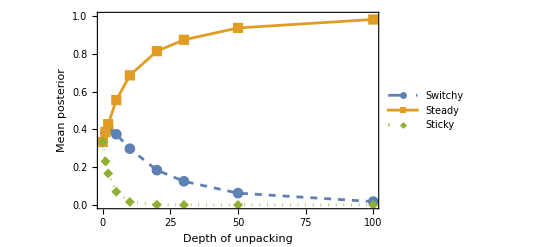

```mathematica
(*Create a list of simulations of Bayesians updating on the results of 1000 tosses, unpacked to various depths:*)

(*NOTE: unpacking of 1 is the hardest since this requires calcualting likelihoods out to 1000 tosses. This takes a couple minutes on the first run, but will be instant afterward*)

Clear[simPosts];

depthsAndPosts=Table[
(*Set the depth of memory unpacking and get number of tosses in each subsequence:*)
unpackDepth = indDepth;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=2000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = {1/3,1/3,1/3};

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{1-wantHR,wantHR}->{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;


(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,non50ChainPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*record mean posteriors in each hypothesis*)
means = Mean[simPosts[unpackDepth]];
{indDepth,means[[1]],means[[2]],means[[3]]}

(*iterate through various depths of unpacking:*)
,{indDepth,{1,2,5,10,20,30,50,100}}]


(*Extract Switchy means for each sequence length from the simulation results.The result will be a list of pairs where the first element is the depth of unpacking and the second element is the mean.
Prepend the 1/3 prior:*)
swiMeans=Prepend[{#[[1]],#[[2]]}&/@depthsAndPosts,{0,1/3}];

(*Similarly,extract means for Steady and Sticky processes*)
steMeans=Prepend[{#[[1]],#[[3]]}&/@depthsAndPosts,{0,1/3}];
stiMeans=Prepend[{#[[1]],#[[4]]}&/@depthsAndPosts,{0,1/3}];

(*Plot the mean posteriors for each process as the unpacking-depth varies*)
ListLinePlot[{swiMeans,steMeans,stiMeans},
PlotRange->{Automatic,{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.5}]]
```

#### Asymmetric convergence when unsure of the long-run hit rate

Suppose our agents start out uniformly (1/3) confident that the long-run hit rate is 45%, 50%, or 55%. Conditional on each hypotheses, they are uniform over Switchy/Steady/Stick.

Suppose in fact data is drawn from a Steady_50% distribution. Do we still get asymmetric convergence?

```mathematica
(*get 55% hit rate chains and likelihoods:*)

(*set parameters:*)
wantHR = 0.55;
minDev = 0.25;
memLength=5;

(*get chains*)
swiHR55 = getNon50InstantChain[wantHR,memLength,minDev,"swi"]
(*print hit rate*)
randHR
(*ignore memory length for steady:*)
steHR55 =getNon50InstantSteady[wantHR,memLength];
stiHR55 = getNon50InstantChain[wantHR,memLength,minDev,"sti"]
(*print hit rate*)
randHR

chainHR55List={swiHR55,steHR55,stiHR55};

(*get sequence likelihoods*)
getInstantSeqLikes[swiHR55SeqLikes,swiHR55]
getInstantSeqLikes[steHR55SeqLikes,steHR55]
getInstantSeqLikes[stiHR55SeqLikes,stiHR55]

HR55ChainSeqLikes={swiHR55SeqLikes,steHR55SeqLikes,stiHR55SeqLikes};


(*get proportions likelihoods*)
getInstantPropLikelihoods[swiHR55PropLikes,swiHR55]
steHR55PropLikes[numTosses_,numHeads_]:=PDF[BinomialDistribution[numTosses,wantHR],numHeads]
getInstantPropLikelihoods[stiHR55PropLikes,stiHR55]

HR55ChainPropLikes = {swiHR55PropLikes,steHR55PropLikes,stiHR55PropLikes};
```

{{0.1,0,0,0,0,0.9,0,0,0,0},{0.17,0,0,0,0,0.83,0,0,0,0},{0,0.24,0,0,0,0.76,0,0,0,0},{0,0,0.31,0,0,0.69,0,0,0,0},{0,0,0,0.38,0,0.62,0,0,0,0},{0,0,0,0,0.5,0,0.5,0,0,0},{0,0,0,0,0.55,0,0,0.45,0,0},{0,0,0,0,0.6,0,0,0,0.4,0},{0,0,0,0,0.65,0,0,0,0,0.35},{0,0,0,0,0.7,0,0,0,0,0.3}}

0.548444

{{0.83,0,0,0,0,0.17,0,0,0,0},{0.754,0,0,0,0,0.246,0,0,0,0},{0,0.678,0,0,0,0.322,0,0,0,0},{0,0,0.602,0,0,0.398,0,0,0,0},{0,0,0,0.526,0,0.474,0,0,0,0},{0,0,0,0,0.392,0,0.608,0,0,0},{0,0,0,0,0.334,0,0,0.666,0,0},{0,0,0,0,0.276,0,0,0,0.724,0},{0,0,0,0,0.218,0,0,0,0,0.782},{0,0,0,0,0.16,0,0,0,0,0.84}}

0.554041

```mathematica
(*get 50% hit rate chains and likelihoods:*)

swi5 = getInstantChain[0.1,5];
ste5=getInstantChain[0.5,5];
sti5 = getInstantChain[0.9,5];

chainHR50List={swi5,ste5,sti5};



(*Calculating the likelihoods for entire sequences based on the chains*)
getInstantSeqLikes[swi5SeqLikes,swi5];
getInstantSeqLikes[ste5SeqLikes,ste5];
getInstantSeqLikes[sti5SeqLikes,sti5];

HR50ChainSeqLikes = {swi5SeqLikes,ste5SeqLikes,sti5SeqLikes};

(*Calculating the likelihoods for individual outcomes based on the chains*)
getInstantPropLikelihoods[swi5PropLikes,swi5];
ste5PropLikes[numTosses_,numHeads_]:=PDF[BinomialDistribution[numTosses,0.5],numHeads];
getInstantPropLikelihoods[sti5PropLikes,sti5];

(*put likelihood functions in a list:*)
HR50chainPropLikes = {swi5PropLikes,ste5PropLikes,sti5PropLikes};
```

```mathematica
(*get 45% hit rate chains and likelihoods:*)

(*set parameters:*)
wantHR = 0.45;
minDev = 0.25;
memLength=5;

(*get chains*)
swiHR45 = getNon50InstantChain[wantHR,memLength,minDev,"swi"]
(*print hit rate*)
randHR
(*ignore memory length for steady:*)
steHR45 =getNon50InstantSteady[wantHR,memLength];
stiHR45 = getNon50InstantChain[wantHR,memLength,minDev,"sti"]
(*print hit rate*)
randHR

chainHR45List={swiHR45,steHR45,stiHR45};

(*get sequence likelihoods*)
getInstantSeqLikes[swiHR45SeqLikes,swiHR45]
getInstantSeqLikes[steHR45SeqLikes,steHR45]
getInstantSeqLikes[stiHR45SeqLikes,stiHR45]

HR45ChainSeqLikes={swiHR45SeqLikes,steHR45SeqLikes,stiHR45SeqLikes};


(*get proportions likelihoods*)
getInstantPropLikelihoods[swiHR45PropLikes,swiHR45]
steHR45PropLikes[numTosses_,numHeads_]:=PDF[BinomialDistribution[numTosses,wantHR],numHeads]
getInstantPropLikelihoods[stiHR45PropLikes,stiHR45]

HR45ChainPropLikes = {swiHR45PropLikes,steHR45PropLikes,stiHR45PropLikes};
```

{{0.29,0,0,0,0,0.71,0,0,0,0},{0.342,0,0,0,0,0.658,0,0,0,0},{0,0.394,0,0,0,0.606,0,0,0,0},{0,0,0.446,0,0,0.554,0,0,0,0},{0,0,0,0.498,0,0.502,0,0,0,0},{0,0,0,0,0.626,0,0.374,0,0,0},{0,0,0,0,0.702,0,0,0.298,0,0},{0,0,0,0,0.778,0,0,0,0.222,0},{0,0,0,0,0.854,0,0,0,0,0.146},{0,0,0,0,0.93,0,0,0,0,0.07}}

0.450103

{{0.88,0,0,0,0,0.12,0,0,0,0},{0.814,0,0,0,0,0.186,0,0,0,0},{0,0.748,0,0,0,0.252,0,0,0,0},{0,0,0.682,0,0,0.318,0,0,0,0},{0,0,0,0.616,0,0.384,0,0,0,0},{0,0,0,0,0.464,0,0.536,0,0,0},{0,0,0,0,0.378,0,0,0.622,0,0},{0,0,0,0,0.292,0,0,0,0.708,0},{0,0,0,0,0.206,0,0,0,0,0.794},{0,0,0,0,0.12,0,0,0,0,0.88}}

0.450011

Encode chains in order as
{swi45,ste45,sti45,swi50,ste50,sti50,swi55,ste55,sti55}

Check for for convergence rates.

Limited data:

```mathematica
(*First, get a list of various sequence lengths and the average posteriors in {Switchy, Steady, Sticky} upon conditioning on them:*)

(*put all chains in a list:*)
allChainList = Join[chainHR45List,chainHR50List,chainHR55List];
allSeqLikes=Join[HR45ChainSeqLikes,HR50ChainSeqLikes,HR55ChainSeqLikes];

(*set the desired seqLengths*)
wantSeqLengths={1,5,10,20,30,50,100};


(*Define a uniform prior over all the processes, in order*)prior=Table[1/Length[allChainList],Length[allChainList]];

(*For various sequence lengths simulate the beliefs of Bayesian agents after conditioning on a sequence drawn from Steady_50*)
Timing[
seqLengthAndPosts=Table[
(*Set the current sequence length*)
seqLength=indSeqLength;
(*For each sequence length,run a simulation 10,000 times*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform, these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the  processes*)
likes=#[seq]&/@allSeqLikes;
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process to get an average belief over the simulations*)
4000];
(*Calculate the mean posterior beliefs for Switchy,Steady,and Sticky over the simulations*)
means=Mean[simPosts[seqLength]];

(*record max sequence length so far*)
maxSeqLength = indSeqLength;

(*Store the sequence length and the mean beliefs for each process in a list*)
Prepend[means,indSeqLength]
(*Repeat the entire simulation for sequence lengths 1,5,10,20,50,and 100*)
,{indSeqLength,wantSeqLengths}]
]
```

{68.865,{{1,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111,0.111111},{5,0.115193,0.113247,0.104126,0.11533,0.113603,0.103718,0.115151,0.113471,0.106161},{10,0.120731,0.124028,0.0873978,0.118468,0.124722,0.0832836,0.120795,0.123882,0.0966929},{20,0.120924,0.148544,0.0635424,0.109274,0.14977,0.0548243,0.122649,0.147482,0.0829905},{30,0.114066,0.172465,0.045501,0.0939787,0.176291,0.0361941,0.118388,0.172527,0.0705887},{50,0.0954177,0.214884,0.0235553,0.0643303,0.22517,0.0155473,0.101656,0.210102,0.0493383},{100,0.0544338,0.263606,0.00354822,0.0281521,0.306636,0.00157974,0.0632997,0.263129,0.0156152}}}

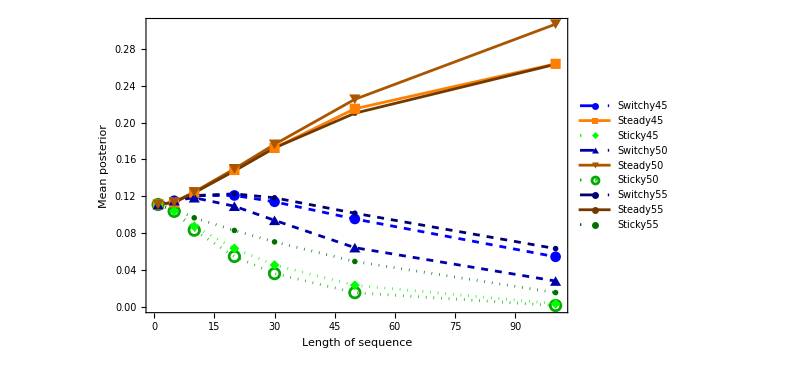
-Graphics-Limited Data

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)
(*Extract means for each sequence length*)
allMeans = Table[{#[[1]],#[[ind]]}&/@seqLengthAndPosts,{ind,2,Length[allChainList]+1}];

(*Plot the means for each process as the sequence length varies*)
plot=Labeled[
ListLinePlot[allMeans,PlotRange->{{0,maxSeqLength+1},{0,Automatic}},
PlotStyle->{
{Dashed,Blue},
{Normal,Orange},
{Dotted,Green},
{Dashed,Darker[Blue]},
{Normal,Darker[Orange]},
{Dotted,Darker[Green]},
{Dashed,Darker[Darker[Blue]]},
{Normal,Darker[Darker[Orange]]},
{Dotted,Darker[Darker[Green]]}
},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Length of sequence",FontSize->14],None}},PlotLegends->Placed[{"Switchy45",
"Steady45",
"Sticky45",
"Switchy50",
"Steady50",
"Sticky50",
"Switchy55",
"Steady55",
"Sticky55"},{0.11,0.72}],
ImageSize->600]
,Style["Limited Data",FontFamily->"Arial",FontWeight->Bold,FontSize->17],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_non50_conv.pdf",plot];
```

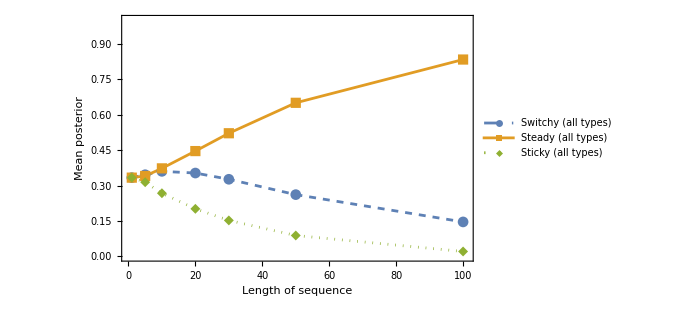
-Graphics-Limited Data

```mathematica
(*marginalize over hit-rates:*)

(*Extract means for each sequence length*)

(*add switchy posteriors:*)
swiMeans=Table[{wantSeqLengths[[ind]],allMeans[[1]][[ind,2]]+allMeans[[4]][[ind,2]]+allMeans[[7]][[ind,2]]},{ind,Length[wantSeqLengths]}];
(*add steady posteriors:*)
steMeans=Table[{wantSeqLengths[[ind]],allMeans[[2]][[ind,2]]+allMeans[[5]][[ind,2]]+allMeans[[8]][[ind,2]]},{ind,Length[wantSeqLengths]}];
(*add sticky posteriors:*)
stiMeans=Table[{wantSeqLengths[[ind]],allMeans[[3]][[ind,2]]+allMeans[[6]][[ind,2]]+allMeans[[9]][[ind,2]]},{ind,Length[wantSeqLengths]}];

(*Plot the means for each type of process as the sequence length varies*)
plot=Labeled[
ListLinePlot[{swiMeans,steMeans,stiMeans}
,PlotRange->{{0,maxSeqLength+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Length of sequence",FontSize->14],None}},PlotLegends->Placed[{"Switchy (all types)","Steady (all types)","Sticky (all types)"},{0.25,0.8}]
,
ImageSize->500]
,Style["Limited Data",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_data_non50_conv_marginalized.pdf",plot];
```

Now getting predictions of streak lengths:

```mathematica
(*First, get a list of various sequence lengths and the average posteriors in {Switchy, Steady, Sticky} upon conditioning on them:*)


(*Define a uniform prior over all the processes, in order*)prior=Table[1/Length[allChainList],Length[allChainList]];

(*For various sequence lengths simulate the beliefs of Bayesian agents after conditioning on a sequence drawn from Steady_50*)

(*Set the current sequence length*)
seqLength=50;
(*For each sequence length,run a simulation 10,000 times*)
simPosts[seqLength]=Table[
(*Generate a random sequence of heads (1) and tails (0) of the current sequence length; since uniform, these are from a Steady distribution:*)
seq=RandomChoice[{0,1},seqLength];
(*Calculate the likelihoods of the generated sequence for each of the  processes*)
likes=#[seq]&/@allSeqLikes;
(*Update the prior based on the calculated likelihoods to get the posterior beliefs*)
post=(prior*likes)/prior.likes,
(*Repeat the above process to get an average belief over the simulations*)
4000];
(*Calculate the mean posterior beliefs for Switchy,Steady,and Sticky over the simulations*)
means=Mean[simPosts[seqLength]];


(*label the list of posteriors*)
limDataPosts =simPosts[seqLength];
```

{{1,0.48910.00100.0010},{2,0.48220.00170.0017},{3,0.48420.00230.0023},{4,0.49980.00280.0028},{5,0.53190.00320.0032},{6,0.56910.00300.0030},{7,0.60140.00300.0030}}

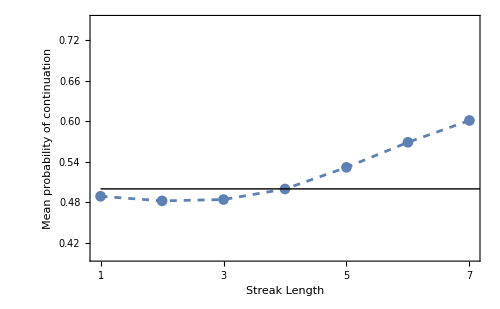
-Graphics-Limited Data

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=7;

(*put all seqlikes functions in order*)
allSeqLikes = {swiHR45SeqLikes,steHR45SeqLikes,stiHR45SeqLikes,swi5SeqLikes,ste5SeqLikes,sti5SeqLikes,swiHR55SeqLikes,steHR55SeqLikes,stiHR55SeqLikes};

(*put all chains in a list*)
allChainList = Join[chainHR45List,chainHR50List,chainHR55List];

(*create the list of pairs*)
limDataMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@allSeqLikes;

(*update each posterior on the sequence:*)
updatedlimDataPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limDataPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[allChainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@allChainList;

(*get updated posterior probabilities of continuation:*)
updatedlimDataProbCont=Table[indPost.contLikes,{indPost,updatedlimDataPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedlimDataProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
(*put all results in a plot:*)
Labeled[ListLinePlot[
{limDataMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Data",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

Limited Memory

```mathematica
(*Create a list of simulations of Bayesians updating on the results of 1000 tosses, unpacked to various depths:*)

(*NOTE: unpacking of 1 is the hardest since this requires calcualting likelihoods out to 1000 tosses. This takes a couple minutes on the first run, but will be instant afterward*)

Clear[simPosts];

wantUnpackDepth={1,5,10,15,20,30,50};

allPropLikes = Join[HR45ChainPropLikes,HR50chainPropLikes,HR55ChainPropLikes];

Timing[depthsAndPosts=Table[
(*Set the depth of memory unpacking and get number of tosses in each subsequence:*)
unpackDepth = indDepth;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=3000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;


(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*record mean posteriors in each hypothesis*)
means = Mean[simPosts[unpackDepth]];

(*record max unpacking  so far*)
maxUnpackDepth = indDepth;

Prepend[means,indDepth]

(*iterate through various depths of unpacking:*)
,{indDepth,wantUnpackDepth}];]
```

General::munfl: 2.30487×10^-308 0.07 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.43348×10^-308 0.146 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.74919×10^-308 0.298 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{131.42,Null}

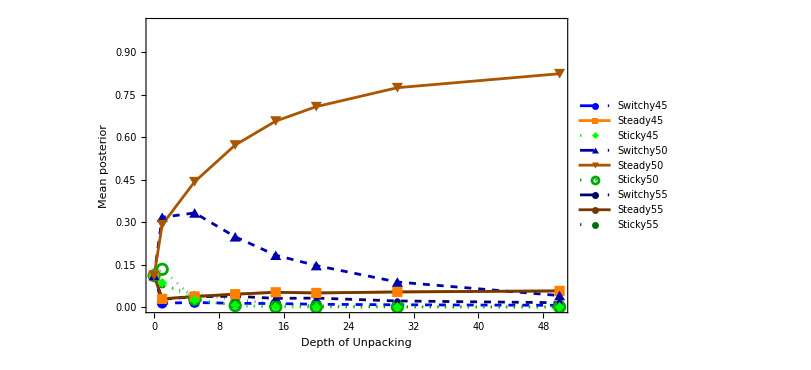
-Graphics-Limited Memory

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)
(*Extract means for each sequence length*)
allMeans = 
(*pre-pend priors at 0*)
Table[Prepend[{#[[1]],#[[ind]]}&/@depthsAndPosts,{0,1/Length[allChainList]}],{ind,2,Length[allChainList]+1}];

(*Plot the means for each process as the sequence length varies*)
plot=Labeled[
ListLinePlot[allMeans,PlotRange->{{0,maxUnpackDepth},{0,1}},
PlotStyle->{
{Dashed,Blue},
{Normal,Orange},
{Dotted,Green},
{Dashed,Darker[Blue]},
{Normal,Darker[Orange]},
{Dotted,Darker[Green]},
{Dashed,Darker[Darker[Blue]]},
{Normal,Darker[Darker[Orange]]},
{Dotted,Darker[Darker[Green]]}
},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy45","Steady45","Sticky45","Switchy50","Steady50","Sticky50","Switchy55","Steady55","Sticky55"},{0.9,0.45}],
ImageSize->600]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->16],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_non50_conv.pdf",plot];
```

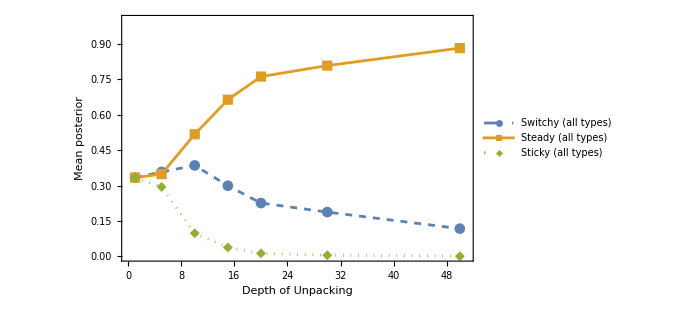
-Graphics-Limited Memory

```mathematica
(*marginalize over hit-rates:*)

(*Extract means for each sequence length*)

(*add switchy posteriors:*)
swiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[1]][[ind,2]]+allMeans[[4]][[ind,2]]+allMeans[[7]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add steady posteriors:*)
steMeans=Table[{wantUnpackDepth[[ind]],allMeans[[2]][[ind,2]]+allMeans[[5]][[ind,2]]+allMeans[[8]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add sticky posteriors:*)
stiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[3]][[ind,2]]+allMeans[[6]][[ind,2]]+allMeans[[9]][[ind,2]]},{ind,Length[wantUnpackDepth]}];

(*Plot the means for each type of process as the sequence length varies*)
plot=Labeled[
ListLinePlot[{swiMeans,steMeans,stiMeans}
,PlotRange->{{0,maxUnpackDepth+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy (all types)","Steady (all types)","Sticky (all types)"},{0.85,0.45}],
ImageSize->500]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_non50_conv_marginalized.pdf",plot];
```

As a result, we can get the same nonlinearities in probability estimates of continuation as before:

```mathematica
(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 10;
numTosses = Floor[1000/unpackDepth];

(*put all chains likes in order*)
allPropLikes = Join[HR45ChainPropLikes,HR50chainPropLikes,HR55ChainPropLikes];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over all hypotheses for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.0144125,0.045365,0.00549783,0.248919,0.578346,0.00394081,0.0354731,0.045365,0.0226808}

{{1,0.47640.00060.0006},{2,0.45830.00100.0010},{3,0.45040.00140.0014},{4,0.45890.00170.0017},{5,0.48660.00160.0016},{6,0.52130.00130.0013},{7,0.54060.00140.0014}}

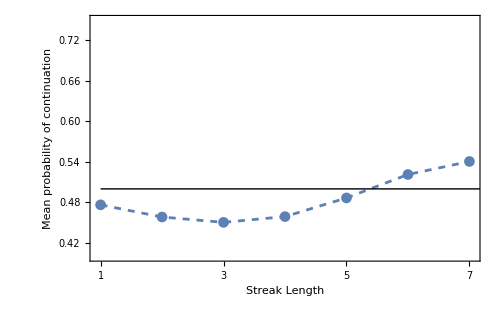
-Graphics-Limited Memory

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=7;

(*put all seqlikes functions in order*)
allSeqLikes = {swiHR45SeqLikes,steHR45SeqLikes,stiHR45SeqLikes,swi5SeqLikes,ste5SeqLikes,sti5SeqLikes,swiHR55SeqLikes,steHR55SeqLikes,stiHR55SeqLikes};

(*put all chains in a list*)
allChainList = Join[chainHR45List,chainHR50List,chainHR55List];

(*create the list of pairs*)
limMemMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@allSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[allChainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@allChainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemProbCont=Table[indPost.contLikes,{indPost,updatedLimMemPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
(*put all results in a plot:*)
Labeled[ListLinePlot[
{limMemMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

### Objection: Unsure about degree of shifty-ness (extremity of chains)

What if unsure the degree of shifty-ness?
Worry: do they quickly learn it’s not very shifty?

```mathematica
(*small-deviation chains, to-60 shift rate*)
swi10=getInstantChain[0.5-0.1,5];
sti10 = getInstantChain[0.5+0.1,5];

(*medium-deviation, to 75 shift rate*)
swi25=getInstantChain[0.5-0.25,5];
sti25=getInstantChain[0.5+0.25,5];

(*big deviation, to 90 shift rate*)
swi40 = getInstantChain[0.5-0.4,5];
sti40=getInstantChain[0.5+0.4,5];

(*no deviation)*)
ste = getInstantChain[0.5,5];

(*put all chains in a list*)
allChainList={swi10,swi25,swi40,ste,sti10,sti25,sti40};

(*get lists of functions for sequence and proportion likelihoods*)
Clear[allChainSeqLikes];
Clear[allChainPropLikes];
allChainSeqLikesList =allChainSeqLikes[#]&/@Range[Length[allChainList]];
allChainPropLikesList =allChainPropLikes[#]&/@Range[Length[allChainList]];

(*define likelihoods*)
Quiet[Table[getInstantSeqLikes[allChainSeqLikes[ind],allChainList[[ind]]],{ind,Length[allChainList]}]];
Quiet[Table[getInstantPropLikes[allChainPropLikes[ind],allChainList[[ind]]],{ind,Length[allChainList]}]];
```

```mathematica
(*Create a list of simulations of Bayesians updating on the results of 1000 tosses, unpacked to various depths:*)

(*NOTE: unpacking of 1 is the hardest since this requires calcualting likelihoods out to 1000 tosses. This takes a couple minutes on the first run, but will be instant afterward*)

Clear[simPosts];

(*what levels of unpacking do you want to do?*)
wantUnpackDepth={1,3,5,10,20,30,50,100};

allPropLikes = allChainPropLikesList;


Timing[depthsAndPosts=Table[
(*Set the depth of memory unpacking and get number of tosses in each subsequence:*)
unpackDepth = indDepth;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=3000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;


(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*record mean posteriors in each hypothesis*)
means = Mean[simPosts[unpackDepth]];

(*record max unpacking  so far*)
maxUnpackDepth = indDepth;

Prepend[means,indDepth]

(*iterate through various depths of unpacking:*)
,{indDepth,wantUnpackDepth}];]
```

General::munfl: 3.34152×10^-308 0.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.47614×10^-308 0.18 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.49082×10^-308 0.26 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{171.125,Null}

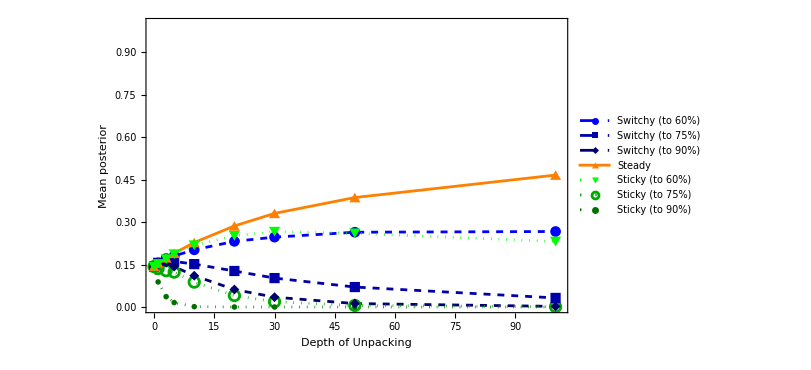
-Graphics-Limited Memory

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)
(*Extract means for each sequence length*)
allMeans = 
(*pre-pend priors at 0*)
Table[Prepend[{#[[1]],#[[ind]]}&/@depthsAndPosts,{0,1/Length[allChainList]}],{ind,2,Length[allChainList]+1}];

(*Plot the means for each process as the sequence length varies*)
plot=Labeled[
ListLinePlot[allMeans,PlotRange->{{0,maxUnpackDepth+1},{0,1}},
PlotStyle->{
{Dashed,Blue},
{Dashed,Darker[Blue]},
{Dashed,Darker[Darker[Blue]]},
{Normal,Orange},
{Dotted,Green},
{Dotted,Darker[Green]},
{Dotted,Darker[Darker[Green]]}
},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy (to 60%)","Switchy (to 75%)","Switchy (to 90%)","Steady","Sticky (to 60%)","Sticky (to 75%)","Sticky (to 90%)"},{0.2,0.75}],
ImageSize->600]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->17],
Top];

Print[plot];

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_unsure_shifty_conv.pdf",plot];
```

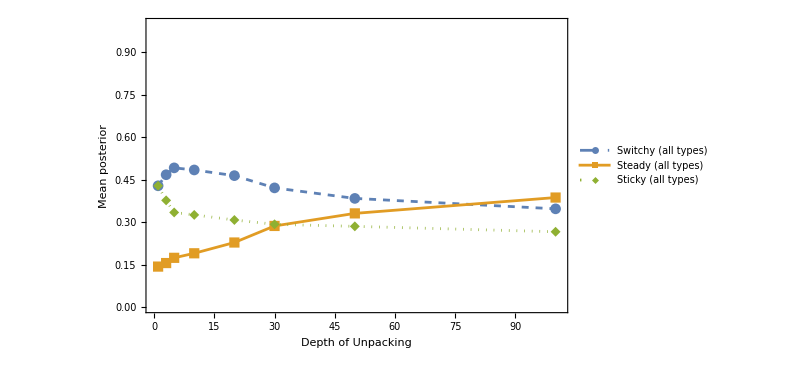
-Graphics-Limited Memory

```mathematica
(*marginalize over hit-rates:*)

(*Extract means for each sequence length*)

(*add switchy posteriors:*)
swiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[1]][[ind,2]]+allMeans[[2]][[ind,2]]+allMeans[[3]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add steady posteriors:*)
steMeans=Table[{wantUnpackDepth[[ind]],allMeans[[4]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add sticky posteriors:*)
stiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[5]][[ind,2]]+allMeans[[6]][[ind,2]]+allMeans[[7]][[ind,2]]},{ind,Length[wantUnpackDepth]}];

(*Plot the means for each type of process as the sequence length varies*)
Labeled[
ListLinePlot[{swiMeans,steMeans,stiMeans}
,PlotRange->{{0,maxUnpackDepth+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy (all types)","Steady (all types)","Sticky (all types)"},{0.2,0.9}],
ImageSize->600]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

```mathematica
(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 10;
numTosses = Floor[1000/unpackDepth];

(*put all chains likes in order*)
allPropLikes = allChainPropLikesList;

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over all hypotheses for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.203086,0.152932,0.111552,0.227714,0.216682,0.0868107,0.00122187}

{{1,0.48660.00050.0005},{2,0.47650.00090.0009},{3,0.47520.00130.0013},{4,0.48770.00160.0016},{5,0.51670.00170.0017},{6,0.55010.00140.0014},{7,0.57550.00130.0013}}

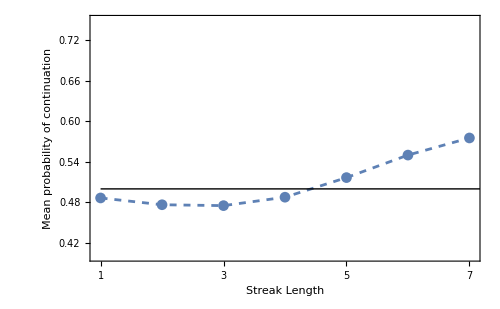
-Graphics-Limited Memory (10-unpacking)

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=7;

(*put all seqlikes functions in order*)
allSeqLikes = allChainSeqLikesList;

(*create the list of pairs*)
limMemMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@allSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[allChainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@allChainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemProbCont=Table[indPost.contLikes,{indPost,updatedLimMemPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
(*put all results in a plot:*)
plot=Labeled[ListLinePlot[
{limMemMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory (10-unpacking)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];


Print[plot];

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_unsure_shifty_prob_cont.pdf",plot];
```

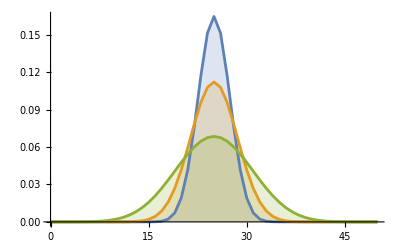

```mathematica
numTosses = 50;

swi40Likes = Table[{ind,allChainPropLikes[3][numTosses,ind]},{ind,0,numTosses}];
steLikes = Table[{ind,allChainPropLikes[4][numTosses,ind]},{ind,0,numTosses}];
sti25Likes=Table[{ind,allChainPropLikes[6][numTosses,ind]},{ind,0,numTosses}];

ListLinePlot[{swi40Likes,steLikes,sti25Likes},
Filling->Axis,
PlotRange->Full]
```

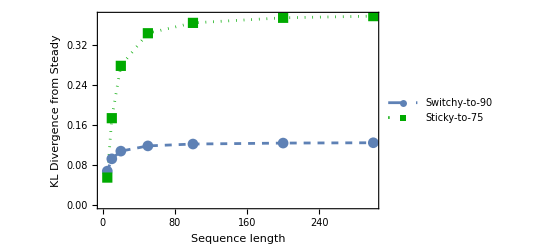

```mathematica
(*Initialize a list to store the KL divergences from Steady to Sticky/Switchy for various sequence lengths*)
klDivergences=Table[
(*Set the current sequence length*)
(*Set the number of total tosses:*)
numTosses = indSeqLength;

(*get a list of likelihoods for each chain:*)
listLikes=Table[#[numTosses,ind],{ind,0,numTosses}]&/@{allChainPropLikes[3],allChainPropLikes[4],allChainPropLikes[6]};


(*Calculate the KL divergence between the Sticky and Steady likelihoods, recording the sequence-length along the way.*)
{{numTosses,listLikes[[1]].Log[listLikes[[1]]/listLikes[[2]]]},{numTosses,listLikes[[3]].Log[listLikes[[3]]/listLikes[[2]]]}}

(*Repeat the above process for various sequence lengths:*),{indSeqLength,{5,10,20,50,100,200,300}}];

(*Plot the KL divergences: *)
ListLinePlot[{#[[1]]&/@klDivergences,#[[2]]&/@klDivergences},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotMarkers->Automatic,
PlotRange->{Automatic,Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","KL Divergence from Steady"},
PlotLegends->Placed[{"Switchy-to-90","Sticky-to-75"},{0.8,0.6}]]
```

### Objection: Unsure about memory length

What if unsure the length of memories?

```mathematica
(*short-memory chains*)
swiShort=getInstantChain[0.1,3];
stiShort = getInstantChain[0.9,3];

(*medium-memory chains*)
swiMed=getInstantChain[0.1,5];
stiMed=getInstantChain[0.9,5];

(*long-memory chains*)
swiLong = getInstantChain[0.1,7];
stiLong=getInstantChain[0.9,7];

(*no deviation)*)
ste = getInstantChain[0.5,5];

(*put all chains in a list*)
allChainList={swiShort,swiMed,swiLong,ste,stiShort,stiMed,stiLong};

(*get lists of functions for sequence and proportion likelihoods*)
Clear[allChainSeqLikes];
Clear[allChainPropLikes];
allChainSeqLikesList =allChainSeqLikes[#]&/@Range[Length[allChainList]];
allChainPropLikesList =allChainPropLikes[#]&/@Range[Length[allChainList]];

(*define likelihoods*)
Quiet[Table[getInstantSeqLikes[allChainSeqLikes[ind],allChainList[[ind]]],{ind,Length[allChainList]}]];
Quiet[Table[getInstantPropLikes[allChainPropLikes[ind],allChainList[[ind]]],{ind,Length[allChainList]}]];
```

```mathematica
(*Create a list of simulations of Bayesians updating on the results of 1000 tosses, unpacked to various depths:*)

(*NOTE: unpacking of 1 is the hardest since this requires calcualting likelihoods out to 1000 tosses. This takes a couple minutes on the first run, but will be instant afterward*)

Clear[simPosts];

(*what levels of unpacking do you want to do?*)
wantUnpackDepth={1,3,5,10,20,30,50};

allPropLikes = allChainPropLikesList;


Timing[depthsAndPosts=Table[
(*Set the depth of memory unpacking and get number of tosses in each subsequence:*)
unpackDepth = indDepth;
numTosses = Floor[1000/unpackDepth];

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=3000;
simPosts[unpackDepth] = Table[
(*set the prior over {Switchy,Steady,Sticky} for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;


(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*record mean posteriors in each hypothesis*)
means = Mean[simPosts[unpackDepth]];

(*record max unpacking  so far*)
maxUnpackDepth = indDepth;

Prepend[means,indDepth]

(*iterate through various depths of unpacking:*)
,{indDepth,wantUnpackDepth}];]
```

General::munfl: 4.27778×10^-308 0.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.94056×10^-308 0.233333 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.43833×10^-308 0.366667 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{169.229,Null}

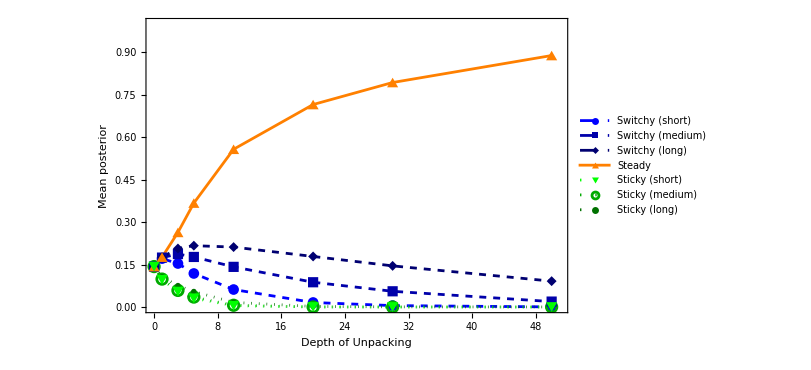
-Graphics-Limited Memory

```mathematica
(*Now visualize the trajectories at various sequence lengths:*)
(*Extract means for each sequence length*)
allMeans = 
(*pre-pend priors at 0*)
Table[Prepend[{#[[1]],#[[ind]]}&/@depthsAndPosts,{0,1/Length[allChainList]}],{ind,2,Length[allChainList]+1}];

(*Plot the means for each process as the sequence length varies*)
plot = Labeled[
ListLinePlot[allMeans,PlotRange->{{0,maxUnpackDepth+1},{0,1}},
PlotStyle->{
{Dashed,Blue},
{Dashed,Darker[Blue]},
{Dashed,Darker[Darker[Blue]]},
{Normal,Orange},
{Dotted,Green},
{Dotted,Darker[Green]},
{Dotted,Darker[Darker[Green]]}
},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy (short)","Switchy (medium)","Switchy (long)","Steady","Sticky (short)","Sticky (medium)","Sticky (long)"},{0.85,0.5}],
ImageSize->600]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->17],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_unsure_memory.pdf",plot];
```

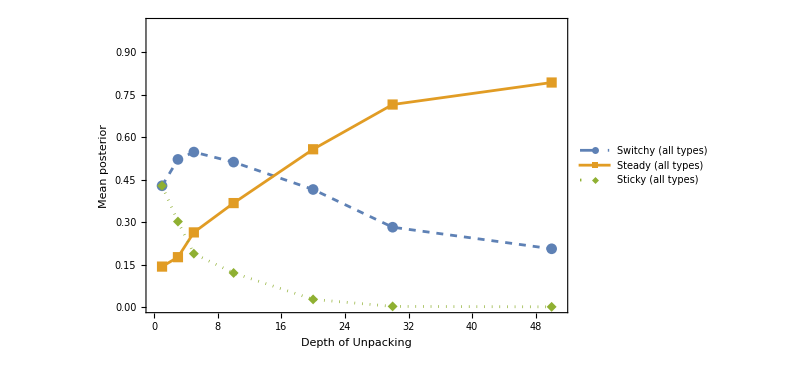
-Graphics-Limited Memory

```mathematica
(*marginalize over hit-rates:*)

(*Extract means for each sequence length*)

(*add switchy posteriors:*)
swiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[1]][[ind,2]]+allMeans[[2]][[ind,2]]+allMeans[[3]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add steady posteriors:*)
steMeans=Table[{wantUnpackDepth[[ind]],allMeans[[4]][[ind,2]]},{ind,Length[wantUnpackDepth]}];
(*add sticky posteriors:*)
stiMeans=Table[{wantUnpackDepth[[ind]],allMeans[[5]][[ind,2]]+allMeans[[6]][[ind,2]]+allMeans[[7]][[ind,2]]},{ind,Length[wantUnpackDepth]}];

(*Plot the means for each type of process as the sequence length varies*)
Labeled[
ListLinePlot[{swiMeans,steMeans,stiMeans}
,PlotRange->{{0,maxUnpackDepth+1},{0,1}},
PlotStyle->{Dashed,Normal,Dotted},
PlotMarkers->Automatic,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean posterior",FontSize->14],None},{Style["Depth of Unpacking",FontSize->14],None}},PlotLegends->Placed[{"Switchy (all types)","Steady (all types)","Sticky (all types)"},{0.2,0.9}],
ImageSize->600]
,Style["Limited Memory",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

```mathematica
(*simulate agents learning from a sequence of length 1000 but unpacking the memory to depth unpackDepth:*)

(*Set the depth of unpacking and subsequence length*)
unpackDepth = 25;
numTosses = Floor[1000/unpackDepth];

(*put all chains likes in order*)
allPropLikes = allChainPropLikesList;

(*simulate a set of numAgents Bayesians updating on evidence about a 1000-toss sequence unpacked to the specified depth:*)
numAgents=10000;
simPosts[unpackDepth] = Table[
(*set the prior over all hypotheses for our agent*)
prior = Table[1/Length[allPropLikes],Length[allPropLikes]];

(*Generate a random length-1000 sequence from Steady likelihoods*)
seq = RandomChoice[{0,1},1000];

(*Partition sequence into subsequences based on the depth of memory unpacking:*)
subSeqs = Partition[seq,numTosses];

(*get the total number of heads in each subsequence*)
headsTotals=Total[#]&/@subSeqs;

(*update the prior on each headsTotal in sequence:*)
Do[
(*get the likelihoods for the given headsTotal:*)
likes = Table[indChain[numTosses,indHeadsTotal],{indChain,allPropLikes}];
(*update the prior on those likelihoods:*)
prior =(prior*likes)/prior.likes;

(*iterate through each headsTotal for each subsequence:*)
,{indHeadsTotal,headsTotals}];

(*record the agent's posterior:*)
prior

(*iterate through all agents*)
,numAgents];

(*label the list of posteriors*)
limMemPosts =simPosts[unpackDepth];

(*mean posteriors*)
Mean[limMemPosts]
```

{0.00856747,0.0674057,0.158831,0.764294,5.96279×10^-6,0.0000241109,0.000871975}

{{1,0.43470.00150.0015},{2,0.42250.00190.0019},{3,0.41750.00220.0022},{4,0.43330.00190.0019},{5,0.45310.00160.0016},{6,0.47380.00110.0011},{7,0.48970.00070.0007}}

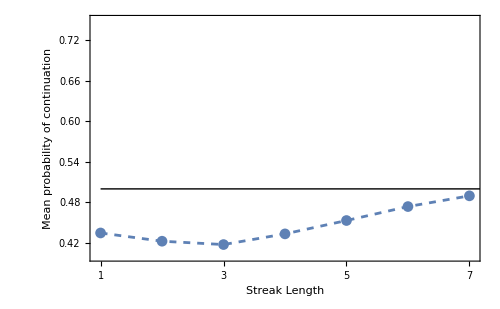
-Graphics-Limited Memory (25-unpacking)

```mathematica
(*create a list of pairs of streak length and updated posterior credences that the streak will continue*)

(*set the max streak length of interest:*)
maxStrLength=7;

(*put all seqlikes functions in order*)
allSeqLikes = allChainSeqLikesList;

(*create the list of pairs*)
limMemMeanProbContByStrLength=Table[
(*set streak length*)
strLength =indStrLength;
(*construct sequence of tails of that streak length*)
seq = Prepend[Table[0,strLength],1];
(*get the likelihoods of that streak from each chain. 
Note that as the strLength grows the likelihoods increasingly provide evidence for Sticky*)
seqLikes = #[seq]&/@allSeqLikes;

(*update each posterior on the sequence:*)
updatedLimMemPosts=Table[
(indPost*seqLikes)/(indPost.seqLikes)
,{indPost,limMemPosts}
];

(*get the probabilities of the streak continuing (another tails) for each updated posterior:*)

(*current chain state*)
curState = getInstantChainState[allChainList[[1]],seq];

(*get likelihoods of continuation:*)
contLikes=getProbTails[#,curState]&/@allChainList;

(*get updated posterior probabilities of continuation:*)
updatedLimMemProbCont=Table[indPost.contLikes,{indPost,updatedLimMemPosts}];

(*record streak length and mean (with confidence intervals) probability of continuation*)
{strLength,aroundCI[updatedLimMemProbCont]}

(*iterate through streak lengths*)
,{indStrLength,maxStrLength}]

(*plot the results*)
(*put all results in a plot:*)
plot=Labeled[ListLinePlot[
{limMemMeanProbContByStrLength},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Memory (25-unpacking)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/lim_mem_unsure_memory_prob_cont.pdf",plot];
```

Note: even a short-memory Switchy sequence (the most farthest from Steady) is closer to Steady than a long-length Sticky sequence (the  closest to Steady):

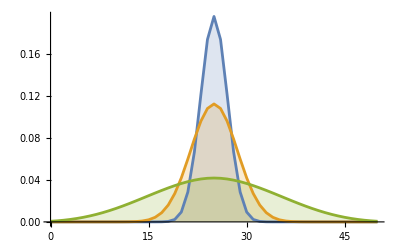

```mathematica
numTosses = 50;

swiShortLikes = Table[{ind,allChainPropLikes[1][numTosses,ind]},{ind,0,numTosses}];
steLikes = Table[{ind,allChainPropLikes[4][numTosses,ind]},{ind,0,numTosses}];
stiLongLikes = Table[{ind,allChainPropLikes[7][numTosses,ind]},{ind,0,numTosses}];
(*stiMedLikes=Table[{ind,allChainPropLikes[6][numTosses,ind]},{ind,0,numTosses}];*)

ListLinePlot[{swiShortLikes,steLikes,stiLongLikes},
Filling->Axis,
PlotRange->Full]
```

```mathematica
4
```

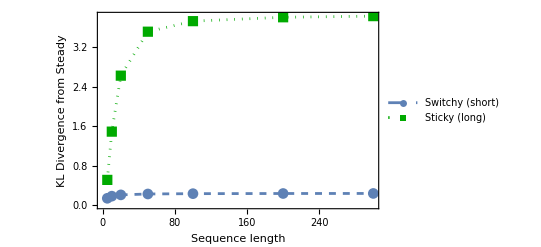

```mathematica
(*Initialize a list to store the KL divergences from Steady to Sticky/Switchy for various sequence lengths*)
klDivergences=Table[
(*Set the current sequence length*)
(*Set the number of total tosses:*)
numTosses = indSeqLength;

(*get a list of likelihoods for each chain:*)
listLikes=Table[#[numTosses,ind],{ind,0,numTosses}]&/@{allChainPropLikes[1],allChainPropLikes[4],allChainPropLikes[5]};


(*Calculate the KL divergence between the Sticky and Steady likelihoods, recording the sequence-length along the way.*)
{{numTosses,listLikes[[1]].Log[listLikes[[1]]/listLikes[[2]]]},{numTosses,listLikes[[3]].Log[listLikes[[3]]/listLikes[[2]]]}}

(*Repeat the above process for various sequence lengths:*),{indSeqLength,{5,10,20,50,100,200,300}}];

(*Plot the KL divergences: *)
ListLinePlot[{#[[1]]&/@klDivergences,#[[2]]&/@klDivergences},
PlotStyle->{Dashed,{Dotted,Darker[Green]}},
PlotMarkers->Automatic,
PlotRange->{Automatic,Full},
Frame->{True,True,False,False},
FrameLabel->{"Sequence length","KL Divergence from Steady"},
PlotLegends->Placed[{"Switchy (short)","Sticky (long)"},{0.8,0.6}]]
```

## Objection: Counting chains

This section replicates the above results using counting chains, which keep track of the last N tosses and use the proportion of heads amongst them—rather than just the current streak—to determine the probabilities of a success.
For example, given the streak 
HTTTTTTTH
An streak Sticky chain would now say that the current streak is heads, and so a heads is more likely. But a counting chain would say that since there’ve been so many recent tails, tails are still “hot”, and so a tails is still more likely.
These chains are complicated because they have to track all possible N-length sequences, meaning they very quickly get very big and hard to visualize.

### Constructing counting chains

```mathematica
(*getSteps function calculates the steps (deviations) away from a 50% chance of either heads or tails for each state in the chain.*)getSteps[states_,memLength_]:=((*Calculate the deviation for each state by subtracting the expected number of heads in a fair sequence from the actual number of heads*)deviations=Total[#]-0.5*memLength&/@states;
(*Round the deviations to the nearest integer.Negative deviations are rounded down,and positive deviations are rounded up.*)deviations/. {x_/;x<0:>Floor[x],y_/;y>0:>Ceiling[y]})


(*getCountChain function constructs a counting chain matrix given the final probability of heads and the memory length.*)
getCountChain[finHeadsProb_,memLength_]:=((*Generate all possible states of length memLength,sorted by the number of heads in each state*)states=SortBy[Tuples[{0,1},memLength],Total];
(*Get the number of steps (deviations) away from 50% for each state*)steps=getSteps[states,memLength];
(*Calculate the incremental probability to move away from 50% towards the final heads probability*)incProb=(finHeadsProb-0.5)/Ceiling[memLength/2];
(*Apply the incremental probability to each state's deviation to get the probability of flipping to heads*)probs=(#*incProb+0.5)&/@steps;
(*Initialize an empty chain matrix*)MatrixForm[chain=Table[Table[0,2^memLength],2^memLength]];
(*Populate the chain matrix*)Table[(*Get the current state and its corresponding next states when flipping to heads or tails*)state=states[[indState]];
headsState=Delete[Append[state,1],1];
headsPos=Position[states,headsState][[1,1]];
tailsState=Delete[Append[state,0],1];
tailsPos=Position[states,tailsState][[1,1]];
(*Update the transition probabilities in the chain matrix for flipping to heads and tails*)chain=ReplacePart[chain,{indState,headsPos}->probs[[indState]]];
chain=ReplacePart[chain,{indState,tailsPos}->1-probs[[indState]]];,{indState,Length[chain]}];
(*Return the final chain matrix*)Return[chain])
```

```mathematica
(*examples*)
(*sticky*)
MatrixForm[getCountChain[0.9,2]]

(*switchy*)
MatrixForm[getCountChain[0.1,2]]
```

(0.9 | 0.1 | 0 | 0
0 | 0 | 0.5 | 0.5
0.5 | 0.5 | 0 | 0
0 | 0 | 0.1 | 0.9)

(0.1 | 0.9 | 0 | 0
0 | 0 | 0.5 | 0.5
0.5 | 0.5 | 0 | 0
0 | 0 | 0.9 | 0.1)

```mathematica
(*3-step switchy:*)
MatrixForm[getCountChain[0.1,3]]
```

(0.1 | 0.9 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.3 | 0 | 0.7 | 0 | 0 | 0
0 | 0 | 0 | 0.3 | 0 | 0.7 | 0 | 0
0.3 | 0.7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.7 | 0.3
0 | 0 | 0.7 | 0 | 0.3 | 0 | 0 | 0
0 | 0 | 0 | 0.7 | 0 | 0.3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.9 | 0.1)

```mathematica
(*getCountSequence generates a sequence of outcomes (Heads or Tails) based on the provided counting chain and the desired sequence length*)getCountSequence[countChain_,length_]:=((*Retrieve the states of the counting chain,sorted by the total number of heads in each state.*)states=SortBy[Tuples[{0,1},Log[2,Length[countChain]]],Total];
(*Randomly initialize the first state as either Heads (1) or Tails (0)*)state1=RandomChoice[{{0},{1}}];
(*Determine the memory length of the counting chain*)junkMemLength=Log[2,Length[countChain]];
(*Extend the initial state to the length of the counting chain's memory, alternating 1s and 0s*)
While[Length[state1]<junkMemLength,If[state1[[1]]==0,PrependTo[state1,1],PrependTo[state1,0]]];
(*Initialize the sequence with the starting state*)
state=state1;
(*Generate the sequence based on the counting chain*)stateSeq=Prepend[Table[(*Find the position of the current state in the list of states*)statePos=Position[states,state][[1,1]];
(*Update the state based on the transition probabilities in the counting chain*)state=states[[RandomChoice[countChain[[statePos]]->Range[Length[countChain]]]]];
state,(*Repeat the above process for the desired sequence length*){length-1}],state1];
(*Extract and return the outcome (Head or Tail) from each state in the sequence*)Return[outcomeSeq=#[[-1]]&/@stateSeq])
```

```mathematica
getCountSequence[getCountChain[0.1,2],10]
getCountSequence[getCountChain[0.9,2],10]
```

{1,1,0,1,0,0,1,1,0,1}

{1,0,1,0,0,0,0,0,0,0}

Now we transition to calculating likelihoods given a coutning chain.

```mathematica
(*getCountChainState determines the state of a counting chain given the current sequence of outcomes——basically we want the recent outcomes up to the memLength*)

(*Initialize in states right near the middle for sequences with a single toss*)

(*If the sequence has only a Tails (0)*)
getCountChainState[countChain_,{0}]:=(
(*Initialize state with Tails*)
state={0};(*Determine the memory length of the counting chain*)junkMemLength=Log[2,Length[countChain]];
(*Extend the initial state to match the counting chain's memory length*)While[Length[state]<junkMemLength,If[state[[1]]==0,PrependTo[state,1],PrependTo[state,0]];];
Return[state])

(*If the sequence has only a Heads (1)*)
getCountChainState[countChain_,{1}]:=(state={1};(*Initialize state with Heads*)(*Determine the memory length of the counting chain*)junkMemLength=Log[2,Length[countChain]];
(*Extend the initial state to match the counting chain's memory length*)While[Length[state]<junkMemLength,If[state[[1]]==0,PrependTo[state,1],PrependTo[state,0]];];
Return[state])

(*For sequences with more than one toss*)
getCountChainState[countChain_,seq_]:=((*Store the value:*)getCountChainState[countChain,seq]=((*Retrieve the states of the counting chain*)states=SortBy[Tuples[{0,1},Log[2,Length[countChain]]],Total];
(*Determine the prior state based on the sequence without the last toss*)priorState=getCountChainState[countChain,seq[[;;-2]]];
(*Update the state based on the last outcome in the sequence*)If[seq[[-1]]==1,newState=Append[priorState[[2;;]],1]];
If[seq[[-1]]==0,newState=Append[priorState[[2;;]],0]];
Return[newState]))
```

```mathematica
(*examples*)
swiCount3 = getCountChain[0.1,3];
getCountChainState[swiCount3,{0}]
getCountChainState[swiCount3,{0,1}]
getCountChainState[swiCount3,{0,1,1}]
getCountChainState[swiCount3,{0,1,1,1}]
```

{0,1,0}

{1,0,1}

{0,1,1}

{1,1,1}

```mathematica
(*getCountChainTailsProb calculates the probability of getting a Tails (0) given a particular state in a counting chain*)getCountChainTailsProb[countChain_,state_]:=(
(*Generate the list of possible states sorted by the total number of Heads*)states=SortBy[Tuples[{0,1},Log[2,Length[countChain]]],Total];

(*Find the row corresponding to the current state in the counting chain's transition matrix*)
rowOfState=countChain[[Position[states,state][[1,1]]]];

(*The first non-zero value in the row is the probability of transitioning to Tails (since the states are sorted by total number of Heads)*)Return[SelectFirst[rowOfState,#>0&]])
```

```mathematica
(*examples*)
swiCount3 = getCountChain[0.1,3];
getCountChainTailsProb[swiCount3,getCountChainState[swiCount3,{0}]]
getCountChainTailsProb[swiCount3,getCountChainState[swiCount3,{0,1}]]
getCountChainTailsProb[swiCount3,getCountChainState[swiCount3,{0,1,1}]]
getCountChainTailsProb[swiCount3,getCountChainState[swiCount3,{0,1,1,1}]]
```

0.3

0.7

0.7

0.9

```mathematica
(*getCountChainSeqLikes defines a function fxn that recursively calculates the likelihood of observing a particular sequence given a counting chain.*)getCountChainSeqLikes[fxn_,chain_]:=(
(*Clear any previous definitions of the function fxn*)
Clear[fxn];
(*Initialize the likelihoods for single-element sequences.If the first toss is Heads (1) or Tails (0),the likelihood is 0.5.*)
fxn[{0}]=0.5;
fxn[{1}]=0.5;

(*Define the recursive function fxn for arbitrary sequences*)fxn[seq_]:=(fxn[seq]=((*If the last element of the sequence is Tails (0),then the likelihood of the sequence is the likelihood of the sequence without the last element times the probability of getting Tails given the state without the last element.*)
If[seq[[-1]]==0,Return[fxn[seq[[;;-2]]]*getCountChainTailsProb[chain,getCountChainState[chain,seq[[;;-2]]]]]];
(*Similarly,if the last element is Heads (1),then the likelihood of the sequence is the likelihood of the sequence without the last element times the probability of getting Heads given the state without the last element.*)
If[seq[[-1]]==1,Return[fxn[seq[[;;-2]]]*(1-getCountChainTailsProb[chain,getCountChainState[chain,seq[[;;-2]]]])]];)))
```

### Limited Data: asymmetric convergence and nonlinear dynamics

Unfortunately, there doesn’t seem to be a simple way to recursively calculated the likelihoods of proportions of heads in N tosses in such a chain, because it’s challenging to figure out what state it should move to.

If we wanted, we could model memory-unpacking by simulating the chains  (using getCountSequence) to approximate their likelihoods over sequences.  

Here I’ll just show the results for Limited Data.  As usual, memory-unpacking would lead to more extreme deviations from 50%.

```mathematica
(*Define counting chains for Switchy,Steady,and Sticky types with a memory length of memLength*)

memLength=4;
swi=getCountChain[0.05,memLength];
ste=getCountChain[0.5,memLength];
sti=getCountChain[0.95,memLength];

(*Generate sequence likelihood functions for each chain type*)
getCountChainSeqLikes[swiSeqLikes,swi]
getCountChainSeqLikes[steSeqLikes,ste]
getCountChainSeqLikes[stiSeqLikes,sti]
```

{19.2301,{{1,0.333333,0.333333,0.333333},{5,0.344379,0.343488,0.312132},{10,0.359368,0.432718,0.207913},{20,0.285007,0.601895,0.113098},{50,0.102956,0.880771,0.0162726},{100,0.0286629,0.971291,0.0000462052}}}

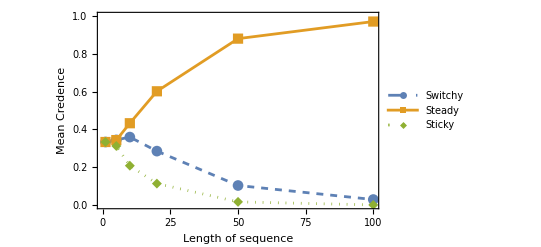

```mathematica
(*Initialize prior probabilities for each chain type to be 1/3*)prior={1/3,1/3,1/3};

(*Compute the posterior probabilities for sequences of different lengths*)

Timing[seqLengthAndPosts=Table[seqLength=indSeqLength;

(*Simulate 1000 sequences of length seqLength and compute posterior probabilities*)
simPosts=Table[
seq=RandomChoice[{0,1},seqLength];
likes={swiSeqLikes[seq],steSeqLikes[seq],stiSeqLikes[seq]};

(*Compute the posterior probabilities based on the likelihoods and prior*)post=(prior*likes)/(prior.likes),1000];

(*Compute the mean posterior probabilities for each chain type*)means=Mean[simPosts];
(*Store the sequence length and mean posterior probabilities*){indSeqLength,means[[1]],means[[2]],means[[3]]},{indSeqLength,{1,5,10,20,50,100}}]]


(*Extract the mean posterior probabilities for plotting*)
maxSeqLength=100;
swiMeans={#[[1]],#[[2]]}&/@seqLengthAndPosts;
steMeans={#[[1]],#[[3]]}&/@seqLengthAndPosts;
stiMeans={#[[1]],#[[4]]}&/@seqLengthAndPosts;

(*Plot the mean posterior probabilities against sequence length*)
ListLinePlot[
{swiMeans,steMeans,stiMeans}
,PlotRange->{{0,maxSeqLength},{0,1}},PlotStyle->{Dashed,Normal,Dotted},PlotMarkers->Automatic,Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Style["Mean Credence",FontSize->14],None},{Style["Length of sequence",FontSize->14],None}},PlotLegends->Placed[{"Switchy","Steady","Sticky"},{0.85,0.5}]]
```

```mathematica
(*Initialize prior probabilities for Switchy,Steady,and Sticky types to be 1/3 each*)
prior={1/3,1/3,1/3};

(*Define the length of the sequence to be simulated*)
seqLength=50;

(*Start a timer to measure the computational time*)
Timing[(*Perform 500 simulations to generate posterior probabilities and other measures*)simPosts=Table[(*Generate a random sequence of coin tosses (0 for tails,1 for heads) of length seqLength*)seq=RandomChoice[{0,1},seqLength];
(*Compute the likelihoods of the sequence for each chain type*)likes={swiSeqLikes[seq],steSeqLikes[seq],stiSeqLikes[seq]};
(*Calculate the posterior probabilities based on the likelihoods and prior*)post=(prior*likes)/(prior.likes);
(*Use Switchy (swi) chain as a representative to get the current state of the chain*)
state=getCountChainState[swi,seq];
(*Get the length of the current streak of heads or tails in the sequence*)strLength=getCurStreak[seq];
(*Calculate the probabilities of tails continuing for Switchy and Sticky chains*)
swiTails=getCountChainTailsProb[swi,state];
stiTails=getCountChainTailsProb[sti,state];
(*Compute the agent's credence that the current streak will continue*)If[seq[[-1]]==0,credCont=post.{swiTails,0.5,stiTails}];
If[seq[[-1]]==1,credCont=post.{1-swiTails,0.5,1-stiTails}];

(*Store the current streak length,chain state,posterior probabilities,and credence*)
{strLength,state,post,credCont}

,20000];]
```

{101.991,Null}

{{1,9880},{2,5171},{3,2497},{4,1207},{5,626},{6,307},{7,155}}

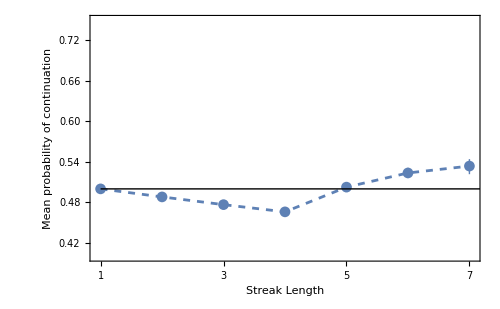
-Graphics-Limited Data (Counting Chains)

```mathematica
(*Create a table of posterior probabilities and credences filtered by streak length*)
Table[
(*For each streak length,filter the simulation data to only include entries with that streak length*)postsByStrLength[indStrLength]=Select[simPosts,#[[1]]==indStrLength&]
  (*Iterate for streak lengths up to 7*)
,{indStrLength,7}];

(*how many entries at each streak length?*)
Table[{ind,Length[postsByStrLength[ind]]},{ind,7}]

(*Create a table of mean posterior probabilities and mean credences by streak length*)
listStrAndProbCont=Table[
{indStrLength,
(*Calculate the mean posterior probabilities for the given streak length*)aroundCI[Table[postsByStrLength[indStrLength][[ind,3]],{ind,Length[postsByStrLength[indStrLength]]}]],

(*Calculate the mean credence that the streak will continue for the given streak length*)aroundCI[Table[postsByStrLength[indStrLength][[ind,4]],{ind,Length[postsByStrLength[indStrLength]]}]]}

,{indStrLength,7}  (*Iterate for streak lengths up to 7*)
];

(*Plot the data*)

Labeled[ListLinePlot[
{{#[[1]],#[[3]]}&/@listStrAndProbCont},
PlotRange->{{0.95,7.05},{0.4,0.75}},
PlotStyle->{Dashed,Dashed,Dotted,Dotted},
PlotMarkers->{Automatic,None},
(*PlotLegends->Placed[{
"Probability matching (by streak length)", 
"Probability matching (overall)",
"Noisy sampling (by streak length)",
"Noisy sampling (overall)"},{0.3,0.85}],*)
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Limited Data (Counting Chains)",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top]
```

## Plots from Rao and Hastie 2023, and Asparouhova et al. 2009

This section does includes the data from Rao and Hastie 2023, available at https://osf.io/2d93t/

### Load data

```mathematica
rawData = {{{"DOCUMENT KEY",""},{"",""},{"Each subsequent tab in this document contains the predictions participants made on each trial in one of the present studies.  Tab titles follow the naming conventions in the main text. The table below provides descriptions for the data found under each Column Header in the subsequent tabs.",""},{"",""},{"",""},{"",""},{"",""},{"",""},{"",""},{"Column Header","Description"},{"study","The Study in which the participant took part.  Study labels follow the same convention as the main text."},{"participant_id","Numerical ID assigned to participant (unique within a given Study)."},{"generator","The qualitative description of the sequence generator.  Naming conventions follow those in main text."},{"rate","The base rate information provided to participants in the instructions."},{"trial","The trial number, in increasing order from the start of the procedure."},{"sequence","The sequence of 8 outcomes shown to the participant, with each outcome coded as 1 (Up/Red) or 0 (Down/Blue)."},{"type","The sequence type. Either a target sequence ending in a streak, or a filler sequence ending in reversal."},{"terminal_streak_length","The length of the streak at the end of the sequence (all filler sequences end in a reversal, or a streak of \"1\")."},{"prediction_raw","The prediction entered by the participant during the procedure (for \"A\" versions, the prediction is a probability that the 9th signal will be Up/Red; for \"B\" versions, the prediction is a dichotomous choice of Up/Red - coded as \"1\" - or Blue/Down - coded as \"0\")"},{"prediction_recode","Raw predictions for sequences ending in Down/Blue outcomes are recoded to indicate participants' prediction of repetition; raw predictions ending in Up/Red are retained in their original format."}},{{"study","participant_id","generator","rate","trial","sequence","type","terminal_streak_length","prediction_raw","prediction_recode"},{"1A",1.,"analyst","unknown",1.,"00110110","filler",1.,75.,25.},{"1A",1.,"analyst","unknown",2.,"00001101","filler",1.,51.,51.},{"1A",1.,"analyst","unknown",3.,"10110100","target",2.,69.,31.},{"1A",1.,"analyst","unknown",4.,"01011110","filler",1.,25.,75.},{"1A",1.,"analyst","unknown",5.,"01010111","target",3.,83.,83.},{"1A",1.,"analyst","unknown",6.,"01011101","filler",1.,49.,49.},{"1A",1.,"analyst","unknown",7.,"00111111","target",6.,92.,92.},{"1A",1.,"analyst","unknown",8.,"01010010","filler",1.,22.,78.},{"1A",1.,"analyst","unknown",9.,"10000101","filler",1.,18.,18.},{"1A",1.,"analyst","unknown",10.,"00110101","filler",1.,9.,9.},{"1A",1.,"analyst","unknown",11.,"01000101","filler",1.,3.,3.},{"1A",1.,"analyst","unknown",12.,"10000000","target",7.,2.,98.},{"1A",1.,"analyst","unknown",13.,"11000110","filler",1.,2.,98.},{"1A",1.,"analyst","unknown",14.,"00101111","target",4.,90.,90.},{"1A",1.,"analyst","unknown",15.,"10001010","filler",1.,71.,29.},{"1A",1.,"analyst","unknown",16.,"00100000","target",5.,5.,95.},{"1A",1.,"analyst","unknown",17.,"01110010","filler",1.,29.,71.},{"1A",1.,"analyst","unknown",18.,"11111010","filler",1.,73.,27.},{"1A",3.,"analyst","unknown",1.,"11110010","filler",1.,36.,64.},{"1A",3.,"analyst","unknown",2.,"10101111","target",4.,57.,57.},{"1A",3.,"analyst","unknown",3.,"11011001","filler",1.,38.,38.},{"1A",3.,"analyst","unknown",4.,"01011000","target",3.,25.,75.},{"1A",3.,"analyst","unknown",5.,"01101010","filler",1.,49.,51.},{"1A",3.,"analyst","unknown",6.,"10000101","filler",1.,36.,36.},{"1A",3.,"analyst","unknown",7.,"11010010","filler",1.,37.,63.},{"1A",3.,"analyst","unknown",8.,"01011110","filler",1.,50.,50.},{"1A",3.,"analyst","unknown",9.,"00110101","filler",1.,43.,43.},{"1A",3.,"analyst","unknown",10.,"01111111","target",7.,45.,45.},{"1A",3.,"analyst","unknown",11.,"11000000","target",6.,62.,38.},{"1A",3.,"analyst","unknown",12.,"01000001","filler",1.,75.,75.},{"1A",3.,"analyst","unknown",13.,"10001010","filler",1.,58.,42.},{"1A",3.,"analyst","unknown",14.,"11000110","filler",1.,38.,62.},{"1A",3.,"analyst","unknown",15.,"01110010","filler",1.,39.,61.},{"1A",3.,"analyst","unknown",16.,"00110110","filler",1.,40.,60.},{"1A",3.,"analyst","unknown",17.,"10100000","target",5.,32.,68.},{"1A",3.,"analyst","unknown",18.,"10101011","target",2.,34.,34.},{"1A",6.,"analyst","unknown",1.,"11101010","filler",1.,100.,0.},{"1A",6.,"analyst","unknown",2.,"10001010","filler",1.,0.,100.},{"1A",6.,"analyst","unknown",3.,"11111010","filler",1.,85.,15.},{"1A",6.,"analyst","unknown",4.,"01000000","target",6.,4.,96.},{"1A",6.,"analyst","unknown",5.,"10000101","filler",1.,33.,33.},{"1A",6.,"analyst","unknown",6.,"00001101","filler",1.,89.,89.},{"1A",6.,"analyst","unknown",7.,"10100110","filler",1.,15.,85.},{"1A",6.,"analyst","unknown",8.,"01011101","filler",1.,4.,4.},{"1A",6.,"analyst","unknown",9.,"01101010","filler",1.,88.,12.},{"1A",6.,"analyst","unknown",10.,"10101011","target",2.,3.,3.},{"1A",6.,"analyst","unknown",11.,"11000110","filler",1.,3.,97.},{"1A",6.,"analyst","unknown",12.,"11110010","filler",1.,4.,96.},{"1A",6.,"analyst","unknown",13.,"11011111","target",5.,2.,2.},{"1A",6.,"analyst","unknown",14.,"01110010","filler",1.,84.,16.},{"1A",6.,"analyst","unknown",15.,"10101010","filler",1.,100.,0.},{"1A",6.,"analyst","unknown",16.,"11010000","target",4.,5.,95.},{"1A",6.,"analyst","unknown",17.,"01111111","target",7.,90.,90.},{"1A",6.,"analyst","unknown",18.,"01011000","target",3.,90.,10.},{"1A",8.,"analyst","unknown",1.,"10101010","filler",1.,94.,6.},{"1A",8.,"analyst","unknown",2.,"00001101","filler",1.,28.,28.},{"1A",8.,"analyst","unknown",3.,"10000001","filler",1.,15.,15.},{"1A",8.,"analyst","unknown",4.,"01011110","filler",1.,70.,30.},{"1A",8.,"analyst","unknown",5.,"10101111","target",4.,76.,76.},{"1A",8.,"analyst","unknown",6.,"01011101","filler",1.,63.,63.},{"1A",8.,"analyst","unknown",7.,"11111101","filler",1.,90.,90.},{"1A",8.,"analyst","unknown",8.,"01110010","filler",1.,54.,46.},{"1A",8.,"analyst","unknown",9.,"11011001","filler",1.,55.,55.},{"1A",8.,"analyst","unknown",10.,"01011111","target",5.,76.,76.},{"1A",8.,"analyst","unknown",11.,"00111111","target",6.,90.,90.},{"1A",8.,"analyst","unknown",12.,"01000101","filler",1.,12.,12.},{"1A",8.,"analyst","unknown",13.,"10000101","filler",1.,12.,12.},{"1A",8.,"analyst","unknown",14.,"11111010","filler",1.,72.,28.},{"1A",8.,"analyst","unknown",15.,"01111111","target",7.,95.,95.},{"1A",8.,"analyst","unknown",16.,"11000110","filler",1.,41.,59.},{"1A",8.,"analyst","unknown",17.,"10100111","target",3.,57.,57.},{"1A",8.,"analyst","unknown",18.,"01001011","target",2.,39.,39.},{"1A",14.,"analyst","unknown",1.,"10000001","filler",1.,15.,15.},{"1A",14.,"analyst","unknown",2.,"11101010","filler",1.,85.,15.},{"1A",14.,"analyst","unknown",3.,"11110010","filler",1.,28.,72.},{"1A",14.,"analyst","unknown",4.,"10101010","filler",1.,51.,49.},{"1A",14.,"analyst","unknown",5.,"11111010","filler",1.,62.,38.},{"1A",14.,"analyst","unknown",6.,"10001010","filler",1.,68.,32.},{"1A",14.,"analyst","unknown",7.,"10110100","target",2.,71.,29.},{"1A",14.,"analyst","unknown",8.,"10100111","target",3.,29.,29.},{"1A",14.,"analyst","unknown",9.,"11011001","filler",1.,72.,72.},{"1A",14.,"analyst","unknown",10.,"01010101","filler",1.,13.,13.},{"1A",14.,"analyst","unknown",11.,"01000101","filler",1.,26.,26.},{"1A",14.,"analyst","unknown",12.,"01000000","target",6.,7.,93.},{"1A",14.,"analyst","unknown",13.,"10100000","target",5.,68.,32.},{"1A",14.,"analyst","unknown",14.,"10101111","target",4.,76.,76.},{"1A",14.,"analyst","unknown",15.,"11111101","filler",1.,79.,79.},{"1A",14.,"analyst","unknown",16.,"01011110","filler",1.,69.,31.},{"1A",14.,"analyst","unknown",17.,"10100110","filler",1.,24.,76.},{"1A",14.,"analyst","unknown",18.,"01111111","target",7.,84.,84.},{"1A",17.,"analyst","unknown",1.,"10100110","filler",1.,14.,86.},{"1A",17.,"analyst","unknown",2.,"11010000","target",4.,8.,92.},{"1A",17.,"analyst","unknown",3.,"10000001","filler",1.,9.,9.},{"1A",17.,"analyst","unknown",4.,"01011101","filler",1.,82.,82.},{"1A",17.,"analyst","unknown",5.,"01000101","filler",1.,8.,8.},{"1A",17.,"analyst","unknown",6.,"01110010","filler",1.,93.,7.},{"1A",17.,"analyst","unknown",7.,"00111111","target",6.,100.,100.},{"1A",17.,"analyst","unknown",8.,"10100000","target",5.,0.,100.},{"1A",17.,"analyst","unknown",9.,"01010111","target",3.,100.,100.},{"1A",17.,"analyst","unknown",10.,"11110010","filler",1.,78.,22.},{"1A",17.,"analyst","unknown",11.,"01101010","filler",1.,88.,12.},{"1A",17.,"analyst","unknown",12.,"10110100","target",2.,84.,16.},{"1A",17.,"analyst","unknown",13.,"01010010","filler",1.,11.,89.},{"1A",17.,"analyst","unknown",14.,"00110101","filler",1.,10.,10.},{"1A",17.,"analyst","unknown",15.,"10000101","filler",1.,5.,5.},{"1A",17.,"analyst","unknown",16.,"11101010","filler",1.,1.,99.},{"1A",17.,"analyst","unknown",17.,"10000000","target",7.,5.,95.},{"1A",17.,"analyst","unknown",18.,"01010101","filler",1.,7.,7.},{"1A",20.,"analyst","unknown",1.,"11111101","filler",1.,93.,93.},{"1A",20.,"analyst","unknown",2.,"10100000","target",5.,85.,15.},{"1A",20.,"analyst","unknown",3.,"00110110","filler",1.,64.,36.},{"1A",20.,"analyst","unknown",4.,"01001011","target",2.,51.,51.},{"1A",20.,"analyst","unknown",5.,"10000000","target",7.,4.,96.},{"1A",20.,"analyst","unknown",6.,"00110101","filler",1.,42.,42.},{"1A",20.,"analyst","unknown",7.,"01000001","filler",1.,9.,9.},{"1A",20.,"analyst","unknown",8.,"10000001","filler",1.,3.,3.},{"1A",20.,"analyst","unknown",9.,"11011001","filler",1.,63.,63.},{"1A",20.,"analyst","unknown",10.,"10001010","filler",1.,20.,80.},{"1A",20.,"analyst","unknown",11.,"10100110","filler",1.,29.,71.},{"1A",20.,"analyst","unknown",12.,"10000101","filler",1.,10.,10.},{"1A",20.,"analyst","unknown",13.,"11000000","target",6.,6.,94.},{"1A",20.,"analyst","unknown",14.,"10101111","target",4.,64.,64.},{"1A",20.,"analyst","unknown",15.,"11101010","filler",1.,57.,43.},{"1A",20.,"analyst","unknown",16.,"01011000","target",3.,17.,83.},{"1A",20.,"analyst","unknown",17.,"01011101","filler",1.,62.,62.},{"1A",20.,"analyst","unknown",18.,"01011110","filler",1.,74.,26.},{"1A",24.,"analyst","unknown",1.,"10101010","filler",1.,68.,32.},{"1A",24.,"analyst","unknown",2.,"11101010","filler",1.,72.,28.},{"1A",24.,"analyst","unknown",3.,"01010101","filler",1.,38.,38.},{"1A",24.,"analyst","unknown",4.,"01010100","target",2.,79.,21.},{"1A",24.,"analyst","unknown",5.,"00100000","target",5.,9.,91.},{"1A",24.,"analyst","unknown",6.,"11000000","target",6.,26.,74.},{"1A",24.,"analyst","unknown",7.,"01010111","target",3.,51.,51.},{"1A",24.,"analyst","unknown",8.,"11011001","filler",1.,63.,63.},{"1A",24.,"analyst","unknown",9.,"00001101","filler",1.,33.,33.},{"1A",24.,"analyst","unknown",10.,"01111111","target",7.,83.,83.},{"1A",24.,"analyst","unknown",11.,"01110010","filler",1.,60.,40.},{"1A",24.,"analyst","unknown",12.,"11111101","filler",1.,83.,83.},{"1A",24.,"analyst","unknown",13.,"01010000","target",4.,34.,66.},{"1A",24.,"analyst","unknown",14.,"10100110","filler",1.,62.,38.},{"1A",24.,"analyst","unknown",15.,"01011101","filler",1.,50.,50.},{"1A",24.,"analyst","unknown",16.,"11111010","filler",1.,76.,24.},{"1A",24.,"analyst","unknown",17.,"00110110","filler",1.,59.,41.},{"1A",24.,"analyst","unknown",18.,"11010010","filler",1.,45.,55.},{"1A",28.,"analyst","unknown",1.,"01000101","filler",1.,29.,29.},{"1A",28.,"analyst","unknown",2.,"10000001","filler",1.,9.,9.},{"1A",28.,"analyst","unknown",3.,"00110101","filler",1.,50.,50.},{"1A",28.,"analyst","unknown",4.,"11110010","filler",1.,61.,39.},{"1A",28.,"analyst","unknown",5.,"00100000","target",5.,9.,91.},{"1A",28.,"analyst","unknown",6.,"11001101","filler",1.,38.,38.},{"1A",28.,"analyst","unknown",7.,"00110110","filler",1.,63.,37.},{"1A",28.,"analyst","unknown",8.,"01010010","filler",1.,38.,62.},{"1A",28.,"analyst","unknown",9.,"01111111","target",7.,91.,91.},{"1A",28.,"analyst","unknown",10.,"01010101","filler",1.,43.,43.},{"1A",28.,"analyst","unknown",11.,"10001010","filler",1.,33.,67.},{"1A",28.,"analyst","unknown",12.,"10100111","target",3.,56.,56.},{"1A",28.,"analyst","unknown",13.,"11010010","filler",1.,51.,49.},{"1A",28.,"analyst","unknown",14.,"01010100","target",2.,38.,62.},{"1A",28.,"analyst","unknown",15.,"11000000","target",6.,11.,89.},{"1A",28.,"analyst","unknown",16.,"10101111","target",4.,68.,68.},{"1A",28.,"analyst","unknown",17.,"01011110","filler",1.,68.,32.},{"1A",28.,"analyst","unknown",18.,"11111101","filler",1.,93.,93.},{"1A",32.,"analyst","unknown",1.,"10001010","filler",1.,51.,49.},{"1A",32.,"analyst","unknown",2.,"10101111","target",4.,2.,2.},{"1A",32.,"analyst","unknown",3.,"10000000","target",7.,41.,59.},{"1A",32.,"analyst","unknown",4.,"11110010","filler",1.,8.,92.},{"1A",32.,"analyst","unknown",5.,"01011101","filler",1.,37.,37.},{"1A",32.,"analyst","unknown",6.,"11111101","filler",1.,93.,93.},{"1A",32.,"analyst","unknown",7.,"01110010","filler",1.,76.,24.},{"1A",32.,"analyst","unknown",8.,"11000110","filler",1.,24.,76.},{"1A",32.,"analyst","unknown",9.,"11000000","target",6.,66.,34.},{"1A",32.,"analyst","unknown",10.,"11001101","filler",1.,16.,16.},{"1A",32.,"analyst","unknown",11.,"01010101","filler",1.,0.,0.},{"1A",32.,"analyst","unknown",12.,"10101010","filler",1.,97.,3.},{"1A",32.,"analyst","unknown",13.,"01011000","target",3.,47.,53.},{"1A",32.,"analyst","unknown",14.,"01000001","filler",1.,6.,6.},{"1A",32.,"analyst","unknown",15.,"10100110","filler",1.,85.,15.},{"1A",32.,"analyst","unknown",16.,"11011111","target",5.,54.,54.},{"1A",32.,"analyst","unknown",17.,"01010100","target",2.,85.,15.},{"1A",32.,"analyst","unknown",18.,"11101010","filler",1.,76.,24.},{"1A",34.,"analyst","unknown",1.,"01101010","filler",1.,52.,48.},{"1A",34.,"analyst","unknown",2.,"10001010","filler",1.,31.,69.},{"1A",34.,"analyst","unknown",3.,"10101010","filler",1.,49.,51.},{"1A",34.,"analyst","unknown",4.,"01010000","target",4.,18.,82.},{"1A",34.,"analyst","unknown",5.,"01010101","filler",1.,52.,52.},{"1A",34.,"analyst","unknown",6.,"11011001","filler",1.,73.,73.},{"1A",34.,"analyst","unknown",7.,"01010100","target",2.,30.,70.},{"1A",34.,"analyst","unknown",8.,"10000000","target",7.,7.,93.},{"1A",34.,"analyst","unknown",9.,"11110010","filler",1.,73.,27.},{"1A",34.,"analyst","unknown",10.,"11010010","filler",1.,51.,49.},{"1A",34.,"analyst","unknown",11.,"01110010","filler",1.,52.,48.},{"1A",34.,"analyst","unknown",12.,"01000000","target",6.,7.,93.},{"1A",34.,"analyst","unknown",13.,"01010010","filler",1.,24.,76.},{"1A",34.,"analyst","unknown",14.,"11011111","target",5.,90.,90.},{"1A",34.,"analyst","unknown",15.,"01000001","filler",1.,18.,18.},{"1A",34.,"analyst","unknown",16.,"10000001","filler",1.,20.,20.},{"1A",34.,"analyst","unknown",17.,"01010111","target",3.,68.,68.},{"1A",34.,"analyst","unknown",18.,"00001101","filler",1.,32.,32.},{"1A",37.,"analyst","unknown",1.,"11111101","filler",1.,69.,69.},{"1A",37.,"analyst","unknown",2.,"01101010","filler",1.,24.,76.},{"1A",37.,"analyst","unknown",3.,"10000000","target",7.,5.,95.},{"1A",37.,"analyst","unknown",4.,"01010010","filler",1.,55.,45.},{"1A",37.,"analyst","unknown",5.,"01010111","target",3.,68.,68.},{"1A",37.,"analyst","unknown",6.,"00101111","target",4.,40.,40.},{"1A",37.,"analyst","unknown",7.,"10000101","filler",1.,22.,22.},{"1A",37.,"analyst","unknown",8.,"10110100","target",2.,55.,45.},{"1A",37.,"analyst","unknown",9.,"00111111","target",6.,81.,81.},{"1A",37.,"analyst","unknown",10.,"00001101","filler",1.,28.,28.},{"1A",37.,"analyst","unknown",11.,"01011110","filler",1.,68.,32.},{"1A",37.,"analyst","unknown",12.,"11010010","filler",1.,89.,11.},{"1A",37.,"analyst","unknown",13.,"00110101","filler",1.,24.,24.},{"1A",37.,"analyst","unknown",14.,"11101010","filler",1.,70.,30.},{"1A",37.,"analyst","unknown",15.,"10100000","target",5.,5.,95.},{"1A",37.,"analyst","unknown",16.,"01011101","filler",1.,18.,18.},{"1A",37.,"analyst","unknown",17.,"01000101","filler",1.,15.,15.},{"1A",37.,"analyst","unknown",18.,"10001010","filler",1.,24.,76.},{"1A",39.,"analyst","unknown",1.,"11011001","filler",1.,68.,68.},{"1A",39.,"analyst","unknown",2.,"11111010","filler",1.,81.,19.},{"1A",39.,"analyst","unknown",3.,"10100110","filler",1.,27.,73.},{"1A",39.,"analyst","unknown",4.,"01010101","filler",1.,21.,21.},{"1A",39.,"analyst","unknown",5.,"11111101","filler",1.,91.,91.},{"1A",39.,"analyst","unknown",6.,"01010010","filler",1.,47.,53.},{"1A",39.,"analyst","unknown",7.,"11110010","filler",1.,63.,37.},{"1A",39.,"analyst","unknown",8.,"11101010","filler",1.,60.,40.},{"1A",39.,"analyst","unknown",9.,"00110101","filler",1.,34.,34.},{"1A",39.,"analyst","unknown",10.,"10101011","target",2.,67.,67.},{"1A",39.,"analyst","unknown",11.,"11010000","target",4.,22.,78.},{"1A",39.,"analyst","unknown",12.,"10000101","filler",1.,11.,11.},{"1A",39.,"analyst","unknown",13.,"01010111","target",3.,65.,65.},{"1A",39.,"analyst","unknown",14.,"11001101","filler",1.,67.,67.},{"1A",39.,"analyst","unknown",15.,"00100000","target",5.,4.,96.},{"1A",39.,"analyst","unknown",16.,"10001010","filler",1.,18.,82.},{"1A",39.,"analyst","unknown",17.,"10000000","target",7.,5.,95.},{"1A",39.,"analyst","unknown",18.,"10111111","target",6.,91.,91.},{"1A",40.,"analyst","unknown",1.,"00110110","filler",1.,18.,82.},{"1A",40.,"analyst","unknown",2.,"01011110","filler",1.,92.,8.},{"1A",40.,"analyst","unknown",3.,"10100110","filler",1.,100.,0.},{"1A",40.,"analyst","unknown",4.,"00101111","target",4.,4.,4.},{"1A",40.,"analyst","unknown",5.,"11000000","target",6.,91.,9.},{"1A",40.,"analyst","unknown",6.,"01101010","filler",1.,89.,11.},{"1A",40.,"analyst","unknown",7.,"11110010","filler",1.,12.,88.},{"1A",40.,"analyst","unknown",8.,"01010101","filler",1.,7.,7.},{"1A",40.,"analyst","unknown",9.,"00110101","filler",1.,67.,67.},{"1A",40.,"analyst","unknown",10.,"00100000","target",5.,0.,100.},{"1A",40.,"analyst","unknown",11.,"11101010","filler",1.,100.,0.},{"1A",40.,"analyst","unknown",12.,"01010100","target",2.,91.,9.},{"1A",40.,"analyst","unknown",13.,"10101010","filler",1.,100.,0.},{"1A",40.,"analyst","unknown",14.,"10000000","target",7.,6.,94.},{"1A",40.,"analyst","unknown",15.,"10001010","filler",1.,79.,21.},{"1A",40.,"analyst","unknown",16.,"01011101","filler",1.,85.,85.},{"1A",40.,"analyst","unknown",17.,"10101000","target",3.,85.,15.},{"1A",40.,"analyst","unknown",18.,"01000001","filler",1.,59.,59.},{"1A",43.,"analyst","unknown",1.,"01110010","filler",1.,52.,48.},{"1A",43.,"analyst","unknown",2.,"11101010","filler",1.,69.,31.},{"1A",43.,"analyst","unknown",3.,"01010101","filler",1.,34.,34.},{"1A",43.,"analyst","unknown",4.,"11010010","filler",1.,53.,47.},{"1A",43.,"analyst","unknown",5.,"01000000","target",6.,26.,74.},{"1A",43.,"analyst","unknown",6.,"10100000","target",5.,36.,64.},{"1A",43.,"analyst","unknown",7.,"00110101","filler",1.,57.,57.},{"1A",43.,"analyst","unknown",8.,"10101000","target",3.,57.,43.},{"1A",43.,"analyst","unknown",9.,"10101011","target",2.,34.,34.},{"1A",43.,"analyst","unknown",10.,"01000001","filler",1.,31.,31.},{"1A",43.,"analyst","unknown",11.,"10101010","filler",1.,59.,41.},{"1A",43.,"analyst","unknown",12.,"10001010","filler",1.,51.,49.},{"1A",43.,"analyst","unknown",13.,"10000001","filler",1.,36.,36.},{"1A",43.,"analyst","unknown",14.,"10100110","filler",1.,53.,47.},{"1A",43.,"analyst","unknown",15.,"01111111","target",7.,63.,63.},{"1A",43.,"analyst","unknown",16.,"10000101","filler",1.,47.,47.},{"1A",43.,"analyst","unknown",17.,"00101111","target",4.,50.,50.},{"1A",43.,"analyst","unknown",18.,"01101010","filler",1.,54.,46.},{"1A",46.,"analyst","unknown",1.,"11011001","filler",1.,70.,70.},{"1A",46.,"analyst","unknown",2.,"11000000","target",6.,8.,92.},{"1A",46.,"analyst","unknown",3.,"01011000","target",3.,51.,49.},{"1A",46.,"analyst","unknown",4.,"01000001","filler",1.,13.,13.},{"1A",46.,"analyst","unknown",5.,"01110010","filler",1.,68.,32.},{"1A",46.,"analyst","unknown",6.,"10101111","target",4.,90.,90.},{"1A",46.,"analyst","unknown",7.,"01011111","target",5.,91.,91.},{"1A",46.,"analyst","unknown",8.,"00110110","filler",1.,75.,25.},{"1A",46.,"analyst","unknown",9.,"11101010","filler",1.,75.,25.},{"1A",46.,"analyst","unknown",10.,"10101010","filler",1.,83.,17.},{"1A",46.,"analyst","unknown",11.,"11010010","filler",1.,67.,33.},{"1A",46.,"analyst","unknown",12.,"10000000","target",7.,5.,95.},{"1A",46.,"analyst","unknown",13.,"11111101","filler",1.,90.,90.},{"1A",46.,"analyst","unknown",14.,"01000101","filler",1.,15.,15.},{"1A",46.,"analyst","unknown",15.,"10000001","filler",1.,30.,30.},{"1A",46.,"analyst","unknown",16.,"10001010","filler",1.,28.,72.},{"1A",46.,"analyst","unknown",17.,"11001101","filler",1.,62.,62.},{"1A",46.,"analyst","unknown",18.,"01001011","target",2.,52.,52.},{"1A",52.,"analyst","unknown",1.,"11110010","filler",1.,53.,47.},{"1A",52.,"analyst","unknown",2.,"00110101","filler",1.,58.,58.},{"1A",52.,"analyst","unknown",3.,"11011001","filler",1.,69.,69.},{"1A",52.,"analyst","unknown",4.,"01011000","target",3.,38.,62.},{"1A",52.,"analyst","unknown",5.,"10100110","filler",1.,57.,43.},{"1A",52.,"analyst","unknown",6.,"10000000","target",7.,18.,82.},{"1A",52.,"analyst","unknown",7.,"00111111","target",6.,72.,72.},{"1A",52.,"analyst","unknown",8.,"01011110","filler",1.,65.,35.},{"1A",52.,"analyst","unknown",9.,"01011111","target",5.,76.,76.},{"1A",52.,"analyst","unknown",10.,"10001010","filler",1.,39.,61.},{"1A",52.,"analyst","unknown",11.,"11001101","filler",1.,58.,58.},{"1A",52.,"analyst","unknown",12.,"11101010","filler",1.,68.,32.},{"1A",52.,"analyst","unknown",13.,"00001101","filler",1.,24.,24.},{"1A",52.,"analyst","unknown",14.,"11010000","target",4.,21.,79.},{"1A",52.,"analyst","unknown",15.,"10101011","target",2.,60.,60.},{"1A",52.,"analyst","unknown",16.,"01110010","filler",1.,53.,47.},{"1A",52.,"analyst","unknown",17.,"11010010","filler",1.,51.,49.},{"1A",52.,"analyst","unknown",18.,"01010101","filler",1.,52.,52.},{"1A",54.,"analyst","unknown",1.,"11000110","filler",1.,89.,11.},{"1A",54.,"analyst","unknown",2.,"10000000","target",7.,21.,79.},{"1A",54.,"analyst","unknown",3.,"01010010","filler",1.,81.,19.},{"1A",54.,"analyst","unknown",4.,"11111101","filler",1.,76.,76.},{"1A",54.,"analyst","unknown",5.,"10100000","target",5.,54.,46.},{"1A",54.,"analyst","unknown",6.,"11000000","target",6.,41.,59.},{"1A",54.,"analyst","unknown",7.,"01000001","filler",1.,32.,32.},{"1A",54.,"analyst","unknown",8.,"10001010","filler",1.,61.,39.},{"1A",54.,"analyst","unknown",9.,"10000101","filler",1.,61.,61.},{"1A",54.,"analyst","unknown",10.,"01010101","filler",1.,21.,21.},{"1A",54.,"analyst","unknown",11.,"01010000","target",4.,66.,34.},{"1A",54.,"analyst","unknown",12.,"10100110","filler",1.,59.,41.},{"1A",54.,"analyst","unknown",13.,"10101010","filler",1.,78.,22.},{"1A",54.,"analyst","unknown",14.,"10101011","target",2.,85.,85.},{"1A",54.,"analyst","unknown",15.,"01000101","filler",1.,73.,73.},{"1A",54.,"analyst","unknown",16.,"01010111","target",3.,90.,90.},{"1A",54.,"analyst","unknown",17.,"11101010","filler",1.,93.,7.},{"1A",54.,"analyst","unknown",18.,"11001101","filler",1.,91.,91.},{"1A",57.,"analyst","unknown",1.,"01011101","filler",1.,76.,76.},{"1A",57.,"analyst","unknown",2.,"10100000","target",5.,21.,79.},{"1A",57.,"analyst","unknown",3.,"10101000","target",3.,59.,41.},{"1A",57.,"analyst","unknown",4.,"11111010","filler",1.,74.,26.},{"1A",57.,"analyst","unknown",5.,"11111101","filler",1.,87.,87.},{"1A",57.,"analyst","unknown",6.,"11011001","filler",1.,60.,60.},{"1A",57.,"analyst","unknown",7.,"11000000","target",6.,5.,95.},{"1A",57.,"analyst","unknown",8.,"01111111","target",7.,96.,96.},{"1A",57.,"analyst","unknown",9.,"10001010","filler",1.,51.,49.},{"1A",57.,"analyst","unknown",10.,"10101010","filler",1.,58.,42.},{"1A",57.,"analyst","unknown",11.,"11010010","filler",1.,66.,34.},{"1A",57.,"analyst","unknown",12.,"10000101","filler",1.,32.,32.},{"1A",57.,"analyst","unknown",13.,"01010101","filler",1.,51.,51.},{"1A",57.,"analyst","unknown",14.,"01000001","filler",1.,38.,38.},{"1A",57.,"analyst","unknown",15.,"11110010","filler",1.,64.,36.},{"1A",57.,"analyst","unknown",16.,"10101011","target",2.,71.,71.},{"1A",57.,"analyst","unknown",17.,"01011110","filler",1.,68.,32.},{"1A",57.,"analyst","unknown",18.,"01010000","target",4.,7.,93.},{"1A",59.,"analyst","unknown",1.,"10000001","filler",1.,78.,78.},{"1A",59.,"analyst","unknown",2.,"01001011","target",2.,92.,92.},{"1A",59.,"analyst","unknown",3.,"10100111","target",3.,97.,97.},{"1A",59.,"analyst","unknown",4.,"11000110","filler",1.,51.,49.},{"1A",59.,"analyst","unknown",5.,"01011101","filler",1.,72.,72.},{"1A",59.,"analyst","unknown",6.,"00001101","filler",1.,40.,40.},{"1A",59.,"analyst","unknown",7.,"01000001","filler",1.,34.,34.},{"1A",59.,"analyst","unknown",8.,"11101010","filler",1.,49.,51.},{"1A",59.,"analyst","unknown",9.,"10000101","filler",1.,39.,39.},{"1A",59.,"analyst","unknown",10.,"00110110","filler",1.,51.,49.},{"1A",59.,"analyst","unknown",11.,"01000000","target",6.,14.,86.},{"1A",59.,"analyst","unknown",12.,"10101111","target",4.,87.,87.},{"1A",59.,"analyst","unknown",13.,"11110010","filler",1.,72.,28.},{"1A",59.,"analyst","unknown",14.,"11111010","filler",1.,76.,24.},{"1A",59.,"analyst","unknown",15.,"11011111","target",5.,97.,97.},{"1A",59.,"analyst","unknown",16.,"01111111","target",7.,97.,97.},{"1A",59.,"analyst","unknown",17.,"01010010","filler",1.,39.,61.},{"1A",59.,"analyst","unknown",18.,"11010010","filler",1.,58.,42.},{"1A",64.,"analyst","unknown",1.,"00110110","filler",1.,50.,50.},{"1A",64.,"analyst","unknown",2.,"01011101","filler",1.,50.,50.},{"1A",64.,"analyst","unknown",3.,"10001010","filler",1.,45.,55.},{"1A",64.,"analyst","unknown",4.,"11010000","target",4.,75.,25.},{"1A",64.,"analyst","unknown",5.,"10101011","target",2.,72.,72.},{"1A",64.,"analyst","unknown",6.,"01011110","filler",1.,55.,45.},{"1A",64.,"analyst","unknown",7.,"10111111","target",6.,63.,63.},{"1A",64.,"analyst","unknown",8.,"10000001","filler",1.,74.,74.},{"1A",64.,"analyst","unknown",9.,"10101010","filler",1.,58.,42.},{"1A",64.,"analyst","unknown",10.,"00110101","filler",1.,60.,60.},{"1A",64.,"analyst","unknown",11.,"01010111","target",3.,93.,93.},{"1A",64.,"analyst","unknown",12.,"11001101","filler",1.,80.,80.},{"1A",64.,"analyst","unknown",13.,"11011111","target",5.,63.,63.},{"1A",64.,"analyst","unknown",14.,"11111010","filler",1.,64.,36.},{"1A",64.,"analyst","unknown",15.,"01111111","target",7.,75.,75.},{"1A",64.,"analyst","unknown",16.,"01000101","filler",1.,76.,76.},{"1A",64.,"analyst","unknown",17.,"11000110","filler",1.,82.,18.},{"1A",64.,"analyst","unknown",18.,"01000001","filler",1.,72.,72.},{"1A",69.,"analyst","unknown",1.,"10100110","filler",1.,51.,49.},{"1A",69.,"analyst","unknown",2.,"00110101","filler",1.,23.,23.},{"1A",69.,"analyst","unknown",3.,"11000110","filler",1.,47.,53.},{"1A",69.,"analyst","unknown",4.,"00100000","target",5.,52.,48.},{"1A",69.,"analyst","unknown",5.,"01011110","filler",1.,10.,90.},{"1A",69.,"analyst","unknown",6.,"11001101","filler",1.,11.,11.},{"1A",69.,"analyst","unknown",7.,"10000000","target",7.,71.,29.},{"1A",69.,"analyst","unknown",8.,"10001010","filler",1.,75.,25.},{"1A",69.,"analyst","unknown",9.,"01010101","filler",1.,7.,7.},{"1A",69.,"analyst","unknown",10.,"00101111","target",4.,11.,11.},{"1A",69.,"analyst","unknown",11.,"10000101","filler",1.,6.,6.},{"1A",69.,"analyst","unknown",12.,"11101010","filler",1.,80.,20.},{"1A",69.,"analyst","unknown",13.,"11111010","filler",1.,81.,19.},{"1A",69.,"analyst","unknown",14.,"10101010","filler",1.,81.,19.},{"1A",69.,"analyst","unknown",15.,"00111111","target",6.,8.,8.},{"1A",69.,"analyst","unknown",16.,"01010010","filler",1.,78.,22.},{"1A",69.,"analyst","unknown",17.,"10101000","target",3.,77.,23.},{"1A",69.,"analyst","unknown",18.,"10110100","target",2.,83.,17.},{"1A",72.,"analyst","unknown",1.,"01010010","filler",1.,72.,28.},{"1A",72.,"analyst","unknown",2.,"01101010","filler",1.,55.,45.},{"1A",72.,"analyst","unknown",3.,"10100110","filler",1.,44.,56.},{"1A",72.,"analyst","unknown",4.,"11001101","filler",1.,71.,71.},{"1A",72.,"analyst","unknown",5.,"01011101","filler",1.,69.,69.},{"1A",72.,"analyst","unknown",6.,"10101111","target",4.,38.,38.},{"1A",72.,"analyst","unknown",7.,"10001010","filler",1.,61.,39.},{"1A",72.,"analyst","unknown",8.,"00001101","filler",1.,51.,51.},{"1A",72.,"analyst","unknown",9.,"01000001","filler",1.,61.,61.},{"1A",72.,"analyst","unknown",10.,"10111111","target",6.,66.,66.},{"1A",72.,"analyst","unknown",11.,"10000001","filler",1.,45.,45.},{"1A",72.,"analyst","unknown",12.,"11011001","filler",1.,69.,69.},{"1A",72.,"analyst","unknown",13.,"01010111","target",3.,66.,66.},{"1A",72.,"analyst","unknown",14.,"01011110","filler",1.,63.,37.},{"1A",72.,"analyst","unknown",15.,"00110110","filler",1.,47.,53.},{"1A",72.,"analyst","unknown",16.,"01001011","target",2.,57.,57.},{"1A",72.,"analyst","unknown",17.,"10000000","target",7.,0.,100.},{"1A",72.,"analyst","unknown",18.,"10100000","target",5.,2.,98.},{"1A",74.,"analyst","unknown",1.,"01011101","filler",1.,17.,17.},{"1A",74.,"analyst","unknown",2.,"11011001","filler",1.,63.,63.},{"1A",74.,"analyst","unknown",3.,"10111111","target",6.,49.,49.},{"1A",74.,"analyst","unknown",4.,"01011111","target",5.,51.,51.},{"1A",74.,"analyst","unknown",5.,"01000001","filler",1.,63.,63.},{"1A",74.,"analyst","unknown",6.,"11001101","filler",1.,63.,63.},{"1A",74.,"analyst","unknown",7.,"11110010","filler",1.,61.,39.},{"1A",74.,"analyst","unknown",8.,"01111111","target",7.,52.,52.},{"1A",74.,"analyst","unknown",9.,"01101010","filler",1.,64.,36.},{"1A",74.,"analyst","unknown",10.,"01010010","filler",1.,29.,71.},{"1A",74.,"analyst","unknown",11.,"11101010","filler",1.,73.,27.},{"1A",74.,"analyst","unknown",12.,"01011110","filler",1.,67.,33.},{"1A",74.,"analyst","unknown",13.,"11010010","filler",1.,26.,74.},{"1A",74.,"analyst","unknown",14.,"01001011","target",2.,12.,12.},{"1A",74.,"analyst","unknown",15.,"01010000","target",4.,57.,43.},{"1A",74.,"analyst","unknown",16.,"01010101","filler",1.,8.,8.},{"1A",74.,"analyst","unknown",17.,"10101000","target",3.,36.,64.},{"1A",74.,"analyst","unknown",18.,"10000101","filler",1.,7.,7.},{"1A",76.,"analyst","unknown",1.,"01000101","filler",1.,84.,84.},{"1A",76.,"analyst","unknown",2.,"01011110","filler",1.,49.,51.},{"1A",76.,"analyst","unknown",3.,"10111111","target",6.,86.,86.},{"1A",76.,"analyst","unknown",4.,"01110010","filler",1.,84.,16.},{"1A",76.,"analyst","unknown",5.,"11010000","target",4.,61.,39.},{"1A",76.,"analyst","unknown",6.,"10100000","target",5.,72.,28.},{"1A",76.,"analyst","unknown",7.,"11111101","filler",1.,66.,66.},{"1A",76.,"analyst","unknown",8.,"10000001","filler",1.,70.,70.},{"1A",76.,"analyst","unknown",9.,"10000101","filler",1.,58.,58.},{"1A",76.,"analyst","unknown",10.,"11000110","filler",1.,64.,36.},{"1A",76.,"analyst","unknown",11.,"11101010","filler",1.,59.,41.},{"1A",76.,"analyst","unknown",12.,"10101010","filler",1.,50.,50.},{"1A",76.,"analyst","unknown",13.,"01001011","target",2.,66.,66.},{"1A",76.,"analyst","unknown",14.,"10000000","target",7.,86.,14.},{"1A",76.,"analyst","unknown",15.,"11001101","filler",1.,61.,61.},{"1A",76.,"analyst","unknown",16.,"10101000","target",3.,75.,25.},{"1A",76.,"analyst","unknown",17.,"00001101","filler",1.,71.,71.},{"1A",76.,"analyst","unknown",18.,"01011101","filler",1.,64.,64.},{"1A",82.,"analyst","unknown",1.,"00110110","filler",1.,50.,50.},{"1A",82.,"analyst","unknown",2.,"01011111","target",5.,64.,64.},{"1A",82.,"analyst","unknown",3.,"00101111","target",4.,16.,16.},{"1A",82.,"analyst","unknown",4.,"10101010","filler",1.,90.,10.},{"1A",82.,"analyst","unknown",5.,"11101010","filler",1.,61.,39.},{"1A",82.,"analyst","unknown",6.,"11110010","filler",1.,63.,37.},{"1A",82.,"analyst","unknown",7.,"11000110","filler",1.,52.,48.},{"1A",82.,"analyst","unknown",8.,"01000101","filler",1.,27.,27.},{"1A",82.,"analyst","unknown",9.,"00110101","filler",1.,50.,50.},{"1A",82.,"analyst","unknown",10.,"01111111","target",7.,57.,57.},{"1A",82.,"analyst","unknown",11.,"01110010","filler",1.,44.,56.},{"1A",82.,"analyst","unknown",12.,"10111111","target",6.,71.,71.},{"1A",82.,"analyst","unknown",13.,"10000001","filler",1.,10.,10.},{"1A",82.,"analyst","unknown",14.,"01101010","filler",1.,48.,52.},{"1A",82.,"analyst","unknown",15.,"11111010","filler",1.,84.,16.},{"1A",82.,"analyst","unknown",16.,"10101011","target",2.,46.,46.},{"1A",82.,"analyst","unknown",17.,"01011110","filler",1.,73.,27.},{"1A",82.,"analyst","unknown",18.,"10100111","target",3.,37.,37.},{"1A",85.,"analyst","unknown",1.,"01000101","filler",1.,20.,20.},{"1A",85.,"analyst","unknown",2.,"00111111","target",6.,90.,90.},{"1A",85.,"analyst","unknown",3.,"10110100","target",2.,52.,48.},{"1A",85.,"analyst","unknown",4.,"10001010","filler",1.,27.,73.},{"1A",85.,"analyst","unknown",5.,"01011000","target",3.,41.,59.},{"1A",85.,"analyst","unknown",6.,"01011110","filler",1.,79.,21.},{"1A",85.,"analyst","unknown",7.,"00101111","target",4.,85.,85.},{"1A",85.,"analyst","unknown",8.,"11010010","filler",1.,63.,37.},{"1A",85.,"analyst","unknown",9.,"00001101","filler",1.,31.,31.},{"1A",85.,"analyst","unknown",10.,"11111010","filler",1.,80.,20.},{"1A",85.,"analyst","unknown",11.,"10000001","filler",1.,22.,22.},{"1A",85.,"analyst","unknown",12.,"00110101","filler",1.,53.,53.},{"1A",85.,"analyst","unknown",13.,"01111111","target",7.,90.,90.},{"1A",85.,"analyst","unknown",14.,"11011111","target",5.,95.,95.},{"1A",85.,"analyst","unknown",15.,"11001101","filler",1.,59.,59.},{"1A",85.,"analyst","unknown",16.,"11000110","filler",1.,37.,63.},{"1A",85.,"analyst","unknown",17.,"11011001","filler",1.,72.,72.},{"1A",85.,"analyst","unknown",18.,"11110010","filler",1.,67.,33.},{"1A",88.,"analyst","unknown",1.,"11011001","filler",1.,87.,87.},{"1A",88.,"analyst","unknown",2.,"01010101","filler",1.,0.,0.},{"1A",88.,"analyst","unknown",3.,"11011111","target",5.,67.,67.},{"1A",88.,"analyst","unknown",4.,"01000000","target",6.,6.,94.},{"1A",88.,"analyst","unknown",5.,"11001101","filler",1.,78.,78.},{"1A",88.,"analyst","unknown",6.,"01000001","filler",1.,18.,18.},{"1A",88.,"analyst","unknown",7.,"00001101","filler",1.,67.,67.},{"1A",88.,"analyst","unknown",8.,"11111101","filler",1.,84.,84.},{"1A",88.,"analyst","unknown",9.,"10100110","filler",1.,30.,70.},{"1A",88.,"analyst","unknown",10.,"01010000","target",4.,3.,97.},{"1A",88.,"analyst","unknown",11.,"11010010","filler",1.,72.,28.},{"1A",88.,"analyst","unknown",12.,"01011110","filler",1.,83.,17.},{"1A",88.,"analyst","unknown",13.,"00110101","filler",1.,80.,80.},{"1A",88.,"analyst","unknown",14.,"11101010","filler",1.,75.,25.},{"1A",88.,"analyst","unknown",15.,"01010100","target",2.,27.,73.},{"1A",88.,"analyst","unknown",16.,"01111111","target",7.,96.,96.},{"1A",88.,"analyst","unknown",17.,"01011101","filler",1.,84.,84.},{"1A",88.,"analyst","unknown",18.,"01010111","target",3.,26.,26.},{"1A",90.,"analyst","unknown",1.,"11111101","filler",1.,16.,16.},{"1A",90.,"analyst","unknown",2.,"10100110","filler",1.,5.,95.},{"1A",90.,"analyst","unknown",3.,"01010100","target",2.,2.,98.},{"1A",90.,"analyst","unknown",4.,"11011001","filler",1.,28.,28.},{"1A",90.,"analyst","unknown",5.,"10000101","filler",1.,5.,5.},{"1A",90.,"analyst","unknown",6.,"11101010","filler",1.,15.,85.},{"1A",90.,"analyst","unknown",7.,"11000110","filler",1.,11.,89.},{"1A",90.,"analyst","unknown",8.,"01010111","target",3.,19.,19.},{"1A",90.,"analyst","unknown",9.,"00001101","filler",1.,1.,1.},{"1A",90.,"analyst","unknown",10.,"10001010","filler",1.,5.,95.},{"1A",90.,"analyst","unknown",11.,"11001101","filler",1.,18.,18.},{"1A",90.,"analyst","unknown",12.,"10000000","target",7.,1.,99.},{"1A",90.,"analyst","unknown",13.,"01010000","target",4.,4.,96.},{"1A",90.,"analyst","unknown",14.,"10000001","filler",1.,4.,4.},{"1A",90.,"analyst","unknown",15.,"11011111","target",5.,19.,19.},{"1A",90.,"analyst","unknown",16.,"11110010","filler",1.,9.,91.},{"1A",90.,"analyst","unknown",17.,"11111010","filler",1.,21.,79.},{"1A",90.,"analyst","unknown",18.,"00111111","target",6.,25.,25.},{"1A",93.,"analyst","unknown",1.,"01011101","filler",1.,80.,80.},{"1A",93.,"analyst","unknown",2.,"01010010","filler",1.,15.,85.},{"1A",93.,"analyst","unknown",3.,"01000000","target",6.,0.,100.},{"1A",93.,"analyst","unknown",4.,"11101010","filler",1.,48.,52.},{"1A",93.,"analyst","unknown",5.,"01010000","target",4.,18.,82.},{"1A",93.,"analyst","unknown",6.,"10001010","filler",1.,65.,35.},{"1A",93.,"analyst","unknown",7.,"11001101","filler",1.,18.,18.},{"1A",93.,"analyst","unknown",8.,"01000101","filler",1.,18.,18.},{"1A",93.,"analyst","unknown",9.,"11011001","filler",1.,78.,78.},{"1A",93.,"analyst","unknown",10.,"00100000","target",5.,13.,87.},{"1A",93.,"analyst","unknown",11.,"01010101","filler",1.,72.,72.},{"1A",93.,"analyst","unknown",12.,"10000000","target",7.,18.,82.},{"1A",93.,"analyst","unknown",13.,"11010010","filler",1.,76.,24.},{"1A",93.,"analyst","unknown",14.,"10101010","filler",1.,46.,54.},{"1A",93.,"analyst","unknown",15.,"10000101","filler",1.,71.,71.},{"1A",93.,"analyst","unknown",16.,"01001011","target",2.,78.,78.},{"1A",93.,"analyst","unknown",17.,"10100111","target",3.,25.,25.},{"1A",93.,"analyst","unknown",18.,"01011110","filler",1.,31.,69.},{"1A",96.,"analyst","unknown",1.,"10000101","filler",1.,77.,77.},{"1A",96.,"analyst","unknown",2.,"10100111","target",3.,26.,26.},{"1A",96.,"analyst","unknown",3.,"11110010","filler",1.,80.,20.},{"1A",96.,"analyst","unknown",4.,"00111111","target",6.,89.,89.},{"1A",96.,"analyst","unknown",5.,"01011101","filler",1.,18.,18.},{"1A",96.,"analyst","unknown",6.,"01000101","filler",1.,21.,21.},{"1A",96.,"analyst","unknown",7.,"10001010","filler",1.,70.,30.},{"1A",96.,"analyst","unknown",8.,"11000110","filler",1.,25.,75.},{"1A",96.,"analyst","unknown",9.,"11111010","filler",1.,69.,31.},{"1A",96.,"analyst","unknown",10.,"01101010","filler",1.,70.,30.},{"1A",96.,"analyst","unknown",11.,"01010000","target",4.,23.,77.},{"1A",96.,"analyst","unknown",12.,"01111111","target",7.,80.,80.},{"1A",96.,"analyst","unknown",13.,"11010010","filler",1.,22.,78.},{"1A",96.,"analyst","unknown",14.,"10100000","target",5.,61.,39.},{"1A",96.,"analyst","unknown",15.,"00110101","filler",1.,76.,76.},{"1A",96.,"analyst","unknown",16.,"01000001","filler",1.,77.,77.},{"1A",96.,"analyst","unknown",17.,"10101011","target",2.,69.,69.},{"1A",96.,"analyst","unknown",18.,"00110110","filler",1.,30.,70.},{"1A",99.,"analyst","unknown",1.,"01000101","filler",1.,5.,5.},{"1A",99.,"analyst","unknown",2.,"10000101","filler",1.,27.,27.},{"1A",99.,"analyst","unknown",3.,"01110010","filler",1.,50.,50.},{"1A",99.,"analyst","unknown",4.,"01010000","target",4.,21.,79.},{"1A",99.,"analyst","unknown",5.,"00001101","filler",1.,26.,26.},{"1A",99.,"analyst","unknown",6.,"10101000","target",3.,13.,87.},{"1A",99.,"analyst","unknown",7.,"01010010","filler",1.,16.,84.},{"1A",99.,"analyst","unknown",8.,"11000110","filler",1.,49.,51.},{"1A",99.,"analyst","unknown",9.,"01010101","filler",1.,50.,50.},{"1A",99.,"analyst","unknown",10.,"00111111","target",6.,83.,83.},{"1A",99.,"analyst","unknown",11.,"00110110","filler",1.,50.,50.},{"1A",99.,"analyst","unknown",12.,"10110100","target",2.,24.,76.},{"1A",99.,"analyst","unknown",13.,"01011110","filler",1.,61.,39.},{"1A",99.,"analyst","unknown",14.,"01000001","filler",1.,10.,10.},{"1A",99.,"analyst","unknown",15.,"01011111","target",5.,90.,90.},{"1A",99.,"analyst","unknown",16.,"11001101","filler",1.,62.,62.},{"1A",99.,"analyst","unknown",17.,"10101010","filler",1.,51.,49.},{"1A",99.,"analyst","unknown",18.,"01111111","target",7.,94.,94.},{"1A",102.,"analyst","unknown",1.,"10101010","filler",1.,100.,0.},{"1A",102.,"analyst","unknown",2.,"11101010","filler",1.,51.,49.},{"1A",102.,"analyst","unknown",3.,"00001101","filler",1.,59.,59.},{"1A",102.,"analyst","unknown",4.,"11111101","filler",1.,72.,72.},{"1A",102.,"analyst","unknown",5.,"01011111","target",5.,76.,76.},{"1A",102.,"analyst","unknown",6.,"11110010","filler",1.,51.,49.},{"1A",102.,"analyst","unknown",7.,"11000110","filler",1.,27.,73.},{"1A",102.,"analyst","unknown",8.,"01000001","filler",1.,22.,22.},{"1A",102.,"analyst","unknown",9.,"01010101","filler",1.,12.,12.},{"1A",102.,"analyst","unknown",10.,"01000000","target",6.,14.,86.},{"1A",102.,"analyst","unknown",11.,"01011101","filler",1.,11.,11.},{"1A",102.,"analyst","unknown",12.,"01010100","target",2.,54.,46.},{"1A",102.,"analyst","unknown",13.,"10000001","filler",1.,24.,24.},{"1A",102.,"analyst","unknown",14.,"10000000","target",7.,14.,86.},{"1A",102.,"analyst","unknown",15.,"11001101","filler",1.,36.,36.},{"1A",102.,"analyst","unknown",16.,"01011000","target",3.,31.,69.},{"1A",102.,"analyst","unknown",17.,"11010000","target",4.,15.,85.},{"1A",102.,"analyst","unknown",18.,"11010010","filler",1.,42.,58.},{"1A",105.,"analyst","unknown",1.,"11010010","filler",1.,60.,40.},{"1A",105.,"analyst","unknown",2.,"01010101","filler",1.,9.,9.},{"1A",105.,"analyst","unknown",3.,"00001101","filler",1.,12.,12.},{"1A",105.,"analyst","unknown",4.,"01111111","target",7.,89.,89.},{"1A",105.,"analyst","unknown",5.,"11000110","filler",1.,51.,49.},{"1A",105.,"analyst","unknown",6.,"10111111","target",6.,95.,95.},{"1A",105.,"analyst","unknown",7.,"01000101","filler",1.,33.,33.},{"1A",105.,"analyst","unknown",8.,"10110100","target",2.,56.,44.},{"1A",105.,"analyst","unknown",9.,"11001101","filler",1.,65.,65.},{"1A",105.,"analyst","unknown",10.,"10101000","target",3.,36.,64.},{"1A",105.,"analyst","unknown",11.,"10000001","filler",1.,7.,7.},{"1A",105.,"analyst","unknown",12.,"11011001","filler",1.,48.,48.},{"1A",105.,"analyst","unknown",13.,"01010000","target",4.,16.,84.},{"1A",105.,"analyst","unknown",14.,"10100110","filler",1.,47.,53.},{"1A",105.,"analyst","unknown",15.,"11110010","filler",1.,76.,24.},{"1A",105.,"analyst","unknown",16.,"11111101","filler",1.,96.,96.},{"1A",105.,"analyst","unknown",17.,"10101010","filler",1.,92.,8.},{"1A",105.,"analyst","unknown",18.,"00100000","target",5.,4.,96.},{"1A",108.,"analyst","unknown",1.,"11111010","filler",1.,84.,16.},{"1A",108.,"analyst","unknown",2.,"10000001","filler",1.,9.,9.},{"1A",108.,"analyst","unknown",3.,"10100000","target",5.,27.,73.},{"1A",108.,"analyst","unknown",4.,"10100110","filler",1.,52.,48.},{"1A",108.,"analyst","unknown",5.,"01110010","filler",1.,73.,27.},{"1A",108.,"analyst","unknown",6.,"01000001","filler",1.,11.,11.},{"1A",108.,"analyst","unknown",7.,"10101000","target",3.,33.,67.},{"1A",108.,"analyst","unknown",8.,"11110010","filler",1.,74.,26.},{"1A",108.,"analyst","unknown",9.,"11101010","filler",1.,57.,43.},{"1A",108.,"analyst","unknown",10.,"10000101","filler",1.,35.,35.},{"1A",108.,"analyst","unknown",11.,"01011101","filler",1.,69.,69.},{"1A",108.,"analyst","unknown",12.,"01011110","filler",1.,79.,21.},{"1A",108.,"analyst","unknown",13.,"01000000","target",6.,5.,95.},{"1A",108.,"analyst","unknown",14.,"10101011","target",2.,52.,52.},{"1A",108.,"analyst","unknown",15.,"11111101","filler",1.,95.,95.},{"1A",108.,"analyst","unknown",16.,"10000000","target",7.,0.,100.},{"1A",108.,"analyst","unknown",17.,"00101111","target",4.,58.,58.},{"1A",108.,"analyst","unknown",18.,"01000101","filler",1.,24.,24.},{"1A",110.,"analyst","unknown",1.,"00110110","filler",1.,61.,39.},{"1A",110.,"analyst","unknown",2.,"11011001","filler",1.,77.,77.},{"1A",110.,"analyst","unknown",3.,"11101010","filler",1.,51.,49.},{"1A",110.,"analyst","unknown",4.,"01010010","filler",1.,57.,43.},{"1A",110.,"analyst","unknown",5.,"11111101","filler",1.,86.,86.},{"1A",110.,"analyst","unknown",6.,"11110010","filler",1.,41.,59.},{"1A",110.,"analyst","unknown",7.,"11011111","target",5.,78.,78.},{"1A",110.,"analyst","unknown",8.,"10110100","target",2.,32.,68.},{"1A",110.,"analyst","unknown",9.,"10101000","target",3.,56.,44.},{"1A",110.,"analyst","unknown",10.,"01110010","filler",1.,55.,45.},{"1A",110.,"analyst","unknown",11.,"10000000","target",7.,19.,81.},{"1A",110.,"analyst","unknown",12.,"10000001","filler",1.,39.,39.},{"1A",110.,"analyst","unknown",13.,"00001101","filler",1.,19.,19.},{"1A",110.,"analyst","unknown",14.,"10001010","filler",1.,37.,63.},{"1A",110.,"analyst","unknown",15.,"10000101","filler",1.,20.,20.},{"1A",110.,"analyst","unknown",16.,"01010101","filler",1.,31.,31.},{"1A",110.,"analyst","unknown",17.,"01010000","target",4.,44.,56.},{"1A",110.,"analyst","unknown",18.,"01000000","target",6.,8.,92.},{"1A",112.,"analyst","unknown",1.,"10000001","filler",1.,10.,10.},{"1A",112.,"analyst","unknown",2.,"11010010","filler",1.,44.,56.},{"1A",112.,"analyst","unknown",3.,"11011001","filler",1.,78.,78.},{"1A",112.,"analyst","unknown",4.,"11101010","filler",1.,61.,39.},{"1A",112.,"analyst","unknown",5.,"01110010","filler",1.,40.,60.},{"1A",112.,"analyst","unknown",6.,"11000000","target",6.,91.,9.},{"1A",112.,"analyst","unknown",7.,"10000101","filler",1.,26.,26.},{"1A",112.,"analyst","unknown",8.,"11111101","filler",1.,96.,96.},{"1A",112.,"analyst","unknown",9.,"01010100","target",2.,43.,57.},{"1A",112.,"analyst","unknown",10.,"01011000","target",3.,23.,77.},{"1A",112.,"analyst","unknown",11.,"01111111","target",7.,93.,93.},{"1A",112.,"analyst","unknown",12.,"01101010","filler",1.,56.,44.},{"1A",112.,"analyst","unknown",13.,"10100000","target",5.,12.,88.},{"1A",112.,"analyst","unknown",14.,"00110110","filler",1.,56.,44.},{"1A",112.,"analyst","unknown",15.,"01011101","filler",1.,77.,77.},{"1A",112.,"analyst","unknown",16.,"11010000","target",4.,16.,84.},{"1A",112.,"analyst","unknown",17.,"11111010","filler",1.,72.,28.},{"1A",112.,"analyst","unknown",18.,"01000001","filler",1.,6.,6.},{"1A",114.,"analyst","unknown",1.,"10101010","filler",1.,100.,0.},{"1A",114.,"analyst","unknown",2.,"01011110","filler",1.,88.,12.},{"1A",114.,"analyst","unknown",3.,"01010010","filler",1.,88.,12.},{"1A",114.,"analyst","unknown",4.,"10101000","target",3.,59.,41.},{"1A",114.,"analyst","unknown",5.,"11011111","target",5.,96.,96.},{"1A",114.,"analyst","unknown",6.,"00110101","filler",1.,54.,54.},{"1A",114.,"analyst","unknown",7.,"11111101","filler",1.,99.,99.},{"1A",114.,"analyst","unknown",8.,"10000000","target",7.,5.,95.},{"1A",114.,"analyst","unknown",9.,"11110010","filler",1.,65.,35.},{"1A",114.,"analyst","unknown",10.,"00001101","filler",1.,40.,40.},{"1A",114.,"analyst","unknown",11.,"01001011","target",2.,51.,51.},{"1A",114.,"analyst","unknown",12.,"01000101","filler",1.,34.,34.},{"1A",114.,"analyst","unknown",13.,"11000000","target",6.,20.,80.},{"1A",114.,"analyst","unknown",14.,"11000110","filler",1.,50.,50.},{"1A",114.,"analyst","unknown",15.,"01011101","filler",1.,62.,62.},{"1A",114.,"analyst","unknown",16.,"11001101","filler",1.,74.,74.},{"1A",114.,"analyst","unknown",17.,"11011001","filler",1.,58.,58.},{"1A",114.,"analyst","unknown",18.,"00101111","target",4.,76.,76.},{"1A",117.,"analyst","unknown",1.,"10000001","filler",1.,67.,67.},{"1A",117.,"analyst","unknown",2.,"01010101","filler",1.,51.,51.},{"1A",117.,"analyst","unknown",3.,"10100111","target",3.,56.,56.},{"1A",117.,"analyst","unknown",4.,"10000000","target",7.,7.,93.},{"1A",117.,"analyst","unknown",5.,"01010000","target",4.,21.,79.},{"1A",117.,"analyst","unknown",6.,"00111111","target",6.,77.,77.},{"1A",117.,"analyst","unknown",7.,"11000110","filler",1.,51.,49.},{"1A",117.,"analyst","unknown",8.,"10110100","target",2.,50.,50.},{"1A",117.,"analyst","unknown",9.,"01110010","filler",1.,49.,51.},{"1A",117.,"analyst","unknown",10.,"11011001","filler",1.,59.,59.},{"1A",117.,"analyst","unknown",11.,"10001010","filler",1.,36.,64.},{"1A",117.,"analyst","unknown",12.,"11010010","filler",1.,48.,52.},{"1A",117.,"analyst","unknown",13.,"01010010","filler",1.,35.,65.},{"1A",117.,"analyst","unknown",14.,"00110110","filler",1.,49.,51.},{"1A",117.,"analyst","unknown",15.,"01011110","filler",1.,64.,36.},{"1A",117.,"analyst","unknown",16.,"00100000","target",5.,6.,94.},{"1A",117.,"analyst","unknown",17.,"11110010","filler",1.,59.,41.},{"1A",117.,"analyst","unknown",18.,"01000001","filler",1.,19.,19.},{"1A",120.,"analyst","unknown",1.,"01010101","filler",1.,10.,10.},{"1A",120.,"analyst","unknown",2.,"00110101","filler",1.,28.,28.},{"1A",120.,"analyst","unknown",3.,"01101010","filler",1.,84.,16.},{"1A",120.,"analyst","unknown",4.,"01000001","filler",1.,16.,16.},{"1A",120.,"analyst","unknown",5.,"00001101","filler",1.,35.,35.},{"1A",120.,"analyst","unknown",6.,"11000110","filler",1.,80.,20.},{"1A",120.,"analyst","unknown",7.,"01000000","target",6.,61.,39.},{"1A",120.,"analyst","unknown",8.,"10000001","filler",1.,18.,18.},{"1A",120.,"analyst","unknown",9.,"01010010","filler",1.,67.,33.},{"1A",120.,"analyst","unknown",10.,"00101111","target",4.,36.,36.},{"1A",120.,"analyst","unknown",11.,"01111111","target",7.,65.,65.},{"1A",120.,"analyst","unknown",12.,"10100000","target",5.,48.,52.},{"1A",120.,"analyst","unknown",13.,"10001010","filler",1.,72.,28.},{"1A",120.,"analyst","unknown",14.,"11111010","filler",1.,63.,37.},{"1A",120.,"analyst","unknown",15.,"01010100","target",2.,73.,27.},{"1A",120.,"analyst","unknown",16.,"01010111","target",3.,53.,53.},{"1A",120.,"analyst","unknown",17.,"01110010","filler",1.,49.,51.},{"1A",120.,"analyst","unknown",18.,"10101010","filler",1.,62.,38.},{"1A",122.,"analyst","unknown",1.,"11001101","filler",1.,65.,65.},{"1A",122.,"analyst","unknown",2.,"00111111","target",6.,85.,85.},{"1A",122.,"analyst","unknown",3.,"10100111","target",3.,71.,71.},{"1A",122.,"analyst","unknown",4.,"11010010","filler",1.,51.,49.},{"1A",122.,"analyst","unknown",5.,"11011111","target",5.,86.,86.},{"1A",122.,"analyst","unknown",6.,"10000000","target",7.,7.,93.},{"1A",122.,"analyst","unknown",7.,"00001101","filler",1.,25.,25.},{"1A",122.,"analyst","unknown",8.,"01011101","filler",1.,62.,62.},{"1A",122.,"analyst","unknown",9.,"01010101","filler",1.,51.,51.},{"1A",122.,"analyst","unknown",10.,"10110100","target",2.,55.,45.},{"1A",122.,"analyst","unknown",11.,"11110010","filler",1.,54.,46.},{"1A",122.,"analyst","unknown",12.,"01011110","filler",1.,68.,32.},{"1A",122.,"analyst","unknown",13.,"10001010","filler",1.,27.,73.},{"1A",122.,"analyst","unknown",14.,"01010010","filler",1.,27.,73.},{"1A",122.,"analyst","unknown",15.,"01010000","target",4.,19.,81.},{"1A",122.,"analyst","unknown",16.,"10100110","filler",1.,50.,50.},{"1A",122.,"analyst","unknown",17.,"11111101","filler",1.,87.,87.},{"1A",122.,"analyst","unknown",18.,"01000101","filler",1.,19.,19.},{"1A",125.,"analyst","unknown",1.,"11000110","filler",1.,57.,43.},{"1A",125.,"analyst","unknown",2.,"01001011","target",2.,47.,47.},{"1A",125.,"analyst","unknown",3.,"01010111","target",3.,40.,40.},{"1A",125.,"analyst","unknown",4.,"00001101","filler",1.,59.,59.},{"1A",125.,"analyst","unknown",5.,"00110101","filler",1.,51.,51.},{"1A",125.,"analyst","unknown",6.,"01010000","target",4.,45.,55.},{"1A",125.,"analyst","unknown",7.,"11110010","filler",1.,59.,41.},{"1A",125.,"analyst","unknown",8.,"11001101","filler",1.,34.,34.},{"1A",125.,"analyst","unknown",9.,"01111111","target",7.,59.,59.},{"1A",125.,"analyst","unknown",10.,"10001010","filler",1.,43.,57.},{"1A",125.,"analyst","unknown",11.,"01000101","filler",1.,46.,46.},{"1A",125.,"analyst","unknown",12.,"01011111","target",5.,60.,60.},{"1A",125.,"analyst","unknown",13.,"01110010","filler",1.,43.,57.},{"1A",125.,"analyst","unknown",14.,"01000001","filler",1.,36.,36.},{"1A",125.,"analyst","unknown",15.,"10000101","filler",1.,44.,44.},{"1A",125.,"analyst","unknown",16.,"11000000","target",6.,36.,64.},{"1A",125.,"analyst","unknown",17.,"01011101","filler",1.,63.,63.},{"1A",125.,"analyst","unknown",18.,"11111010","filler",1.,65.,35.},{"1A",128.,"analyst","unknown",1.,"01000101","filler",1.,95.,95.},{"1A",128.,"analyst","unknown",2.,"01011101","filler",1.,93.,93.},{"1A",128.,"analyst","unknown",3.,"11001101","filler",1.,85.,85.},{"1A",128.,"analyst","unknown",4.,"11111010","filler",1.,87.,13.},{"1A",128.,"analyst","unknown",5.,"10100110","filler",1.,90.,10.},{"1A",128.,"analyst","unknown",6.,"01010111","target",3.,92.,92.},{"1A",128.,"analyst","unknown",7.,"01010101","filler",1.,90.,90.},{"1A",128.,"analyst","unknown",8.,"00101111","target",4.,92.,92.},{"1A",128.,"analyst","unknown",9.,"11011001","filler",1.,90.,90.},{"1A",128.,"analyst","unknown",10.,"10001010","filler",1.,87.,13.},{"1A",128.,"analyst","unknown",11.,"01111111","target",7.,95.,95.},{"1A",128.,"analyst","unknown",12.,"11101010","filler",1.,88.,12.},{"1A",128.,"analyst","unknown",13.,"10101011","target",2.,87.,87.},{"1A",128.,"analyst","unknown",14.,"11000110","filler",1.,95.,5.},{"1A",128.,"analyst","unknown",15.,"10111111","target",6.,90.,90.},{"1A",128.,"analyst","unknown",16.,"11111101","filler",1.,83.,83.},{"1A",128.,"analyst","unknown",17.,"11011111","target",5.,92.,92.},{"1A",128.,"analyst","unknown",18.,"10000101","filler",1.,91.,91.},{"1A",132.,"analyst","unknown",1.,"11001101","filler",1.,95.,95.},{"1A",132.,"analyst","unknown",2.,"01010101","filler",1.,3.,3.},{"1A",132.,"analyst","unknown",3.,"01000000","target",6.,73.,27.},{"1A",132.,"analyst","unknown",4.,"00110101","filler",1.,84.,84.},{"1A",132.,"analyst","unknown",5.,"10001010","filler",1.,15.,85.},{"1A",132.,"analyst","unknown",6.,"11000110","filler",1.,4.,96.},{"1A",132.,"analyst","unknown",7.,"11011111","target",5.,19.,19.},{"1A",132.,"analyst","unknown",8.,"11010010","filler",1.,12.,88.},{"1A",132.,"analyst","unknown",9.,"11111101","filler",1.,16.,16.},{"1A",132.,"analyst","unknown",10.,"10101011","target",2.,17.,17.},{"1A",132.,"analyst","unknown",11.,"01011110","filler",1.,14.,86.},{"1A",132.,"analyst","unknown",12.,"10000001","filler",1.,89.,89.},{"1A",132.,"analyst","unknown",13.,"01010000","target",4.,88.,12.},{"1A",132.,"analyst","unknown",14.,"10000101","filler",1.,39.,39.},{"1A",132.,"analyst","unknown",15.,"01011000","target",3.,63.,37.},{"1A",132.,"analyst","unknown",16.,"10000000","target",7.,63.,37.},{"1A",132.,"analyst","unknown",17.,"11011001","filler",1.,81.,81.},{"1A",132.,"analyst","unknown",18.,"10100110","filler",1.,49.,51.},{"1A",134.,"analyst","unknown",1.,"10001010","filler",1.,35.,65.},{"1A",134.,"analyst","unknown",2.,"00101111","target",4.,64.,64.},{"1A",134.,"analyst","unknown",3.,"11111010","filler",1.,78.,22.},{"1A",134.,"analyst","unknown",4.,"00110101","filler",1.,49.,49.},{"1A",134.,"analyst","unknown",5.,"10000000","target",7.,4.,96.},{"1A",134.,"analyst","unknown",6.,"10101010","filler",1.,50.,50.},{"1A",134.,"analyst","unknown",7.,"00110110","filler",1.,50.,50.},{"1A",134.,"analyst","unknown",8.,"11011001","filler",1.,58.,58.},{"1A",134.,"analyst","unknown",9.,"01001011","target",2.,50.,50.},{"1A",134.,"analyst","unknown",10.,"01011111","target",5.,74.,74.},{"1A",134.,"analyst","unknown",11.,"00111111","target",6.,76.,76.},{"1A",134.,"analyst","unknown",12.,"10100111","target",3.,62.,62.},{"1A",134.,"analyst","unknown",13.,"11110010","filler",1.,62.,38.},{"1A",134.,"analyst","unknown",14.,"11001101","filler",1.,61.,61.},{"1A",134.,"analyst","unknown",15.,"10000001","filler",1.,21.,21.},{"1A",134.,"analyst","unknown",16.,"11000110","filler",1.,51.,49.},{"1A",134.,"analyst","unknown",17.,"10100110","filler",1.,50.,50.},{"1A",134.,"analyst","unknown",18.,"01101010","filler",1.,50.,50.},{"1A",136.,"analyst","unknown",1.,"11101010","filler",1.,50.,50.},{"1A",136.,"analyst","unknown",2.,"10001010","filler",1.,49.,51.},{"1A",136.,"analyst","unknown",3.,"10100111","target",3.,40.,40.},{"1A",136.,"analyst","unknown",4.,"10110100","target",2.,84.,16.},{"1A",136.,"analyst","unknown",5.,"11110010","filler",1.,63.,37.},{"1A",136.,"analyst","unknown",6.,"01111111","target",7.,48.,48.},{"1A",136.,"analyst","unknown",7.,"00101111","target",4.,83.,83.},{"1A",136.,"analyst","unknown",8.,"10000001","filler",1.,52.,52.},{"1A",136.,"analyst","unknown",9.,"01011110","filler",1.,71.,29.},{"1A",136.,"analyst","unknown",10.,"01000001","filler",1.,44.,44.},{"1A",136.,"analyst","unknown",11.,"01011111","target",5.,72.,72.},{"1A",136.,"analyst","unknown",12.,"11111101","filler",1.,55.,55.},{"1A",136.,"analyst","unknown",13.,"10111111","target",6.,78.,78.},{"1A",136.,"analyst","unknown",14.,"01110010","filler",1.,55.,45.},{"1A",136.,"analyst","unknown",15.,"10101010","filler",1.,67.,33.},{"1A",136.,"analyst","unknown",16.,"01000101","filler",1.,52.,52.},{"1A",136.,"analyst","unknown",17.,"10000101","filler",1.,65.,65.},{"1A",136.,"analyst","unknown",18.,"00001101","filler",1.,77.,77.},{"1A",139.,"analyst","unknown",1.,"10000001","filler",1.,12.,12.},{"1A",139.,"analyst","unknown",2.,"10101010","filler",1.,90.,10.},{"1A",139.,"analyst","unknown",3.,"01010000","target",4.,84.,16.},{"1A",139.,"analyst","unknown",4.,"11000000","target",6.,44.,56.},{"1A",139.,"analyst","unknown",5.,"00110110","filler",1.,83.,17.},{"1A",139.,"analyst","unknown",6.,"10110100","target",2.,80.,20.},{"1A",139.,"analyst","unknown",7.,"11011001","filler",1.,68.,68.},{"1A",139.,"analyst","unknown",8.,"11101010","filler",1.,87.,13.},{"1A",139.,"analyst","unknown",9.,"01010111","target",3.,90.,90.},{"1A",139.,"analyst","unknown",10.,"01000001","filler",1.,46.,46.},{"1A",139.,"analyst","unknown",11.,"11011111","target",5.,96.,96.},{"1A",139.,"analyst","unknown",12.,"11110010","filler",1.,87.,13.},{"1A",139.,"analyst","unknown",13.,"10100110","filler",1.,65.,35.},{"1A",139.,"analyst","unknown",14.,"01111111","target",7.,99.,99.},{"1A",139.,"analyst","unknown",15.,"00001101","filler",1.,67.,67.},{"1A",139.,"analyst","unknown",16.,"01011101","filler",1.,83.,83.},{"1A",139.,"analyst","unknown",17.,"11111010","filler",1.,94.,6.},{"1A",139.,"analyst","unknown",18.,"11001101","filler",1.,81.,81.},{"1A",141.,"analyst","unknown",1.,"00001101","filler",1.,27.,27.},{"1A",141.,"analyst","unknown",2.,"00110101","filler",1.,50.,50.},{"1A",141.,"analyst","unknown",3.,"01001011","target",2.,52.,52.},{"1A",141.,"analyst","unknown",4.,"10000000","target",7.,50.,50.},{"1A",141.,"analyst","unknown",5.,"10100000","target",5.,50.,50.},{"1A",141.,"analyst","unknown",6.,"01010010","filler",1.,50.,50.},{"1A",141.,"analyst","unknown",7.,"10111111","target",6.,49.,49.},{"1A",141.,"analyst","unknown",8.,"01110010","filler",1.,52.,48.},{"1A",141.,"analyst","unknown",9.,"01010101","filler",1.,49.,49.},{"1A",141.,"analyst","unknown",10.,"11010010","filler",1.,48.,52.},{"1A",141.,"analyst","unknown",11.,"11111101","filler",1.,50.,50.},{"1A",141.,"analyst","unknown",12.,"10000001","filler",1.,51.,51.},{"1A",141.,"analyst","unknown",13.,"01011000","target",3.,52.,48.},{"1A",141.,"analyst","unknown",14.,"11000110","filler",1.,50.,50.},{"1A",141.,"analyst","unknown",15.,"10000101","filler",1.,52.,52.},{"1A",141.,"analyst","unknown",16.,"11011001","filler",1.,52.,52.},{"1A",141.,"analyst","unknown",17.,"00101111","target",4.,50.,50.},{"1A",141.,"analyst","unknown",18.,"01101010","filler",1.,51.,49.},{"1A",144.,"analyst","unknown",1.,"11010010","filler",1.,85.,15.},{"1A",144.,"analyst","unknown",2.,"10101010","filler",1.,85.,15.},{"1A",144.,"analyst","unknown",3.,"00110110","filler",1.,19.,81.},{"1A",144.,"analyst","unknown",4.,"11011001","filler",1.,71.,71.},{"1A",144.,"analyst","unknown",5.,"10101111","target",4.,72.,72.},{"1A",144.,"analyst","unknown",6.,"11110010","filler",1.,70.,30.},{"1A",144.,"analyst","unknown",7.,"01000101","filler",1.,31.,31.},{"1A",144.,"analyst","unknown",8.,"10100110","filler",1.,53.,47.},{"1A",144.,"analyst","unknown",9.,"10000000","target",7.,14.,86.},{"1A",144.,"analyst","unknown",10.,"00110101","filler",1.,66.,66.},{"1A",144.,"analyst","unknown",11.,"10000001","filler",1.,21.,21.},{"1A",144.,"analyst","unknown",12.,"01010101","filler",1.,27.,27.},{"1A",144.,"analyst","unknown",13.,"10100000","target",5.,20.,80.},{"1A",144.,"analyst","unknown",14.,"10111111","target",6.,93.,93.},{"1A",144.,"analyst","unknown",15.,"11001101","filler",1.,52.,52.},{"1A",144.,"analyst","unknown",16.,"01001011","target",2.,52.,52.},{"1A",144.,"analyst","unknown",17.,"01011101","filler",1.,69.,69.},{"1A",144.,"analyst","unknown",18.,"01011000","target",3.,40.,60.},{"1A",147.,"analyst","unknown",1.,"01000001","filler",1.,7.,7.},{"1A",147.,"analyst","unknown",2.,"11110010","filler",1.,89.,11.},{"1A",147.,"analyst","unknown",3.,"10101010","filler",1.,76.,24.},{"1A",147.,"analyst","unknown",4.,"10000000","target",7.,0.,100.},{"1A",147.,"analyst","unknown",5.,"01011110","filler",1.,82.,18.},{"1A",147.,"analyst","unknown",6.,"01011000","target",3.,2.,98.},{"1A",147.,"analyst","unknown",7.,"01010101","filler",1.,0.,0.},{"1A",147.,"analyst","unknown",8.,"11111101","filler",1.,89.,89.},{"1A",147.,"analyst","unknown",9.,"00001101","filler",1.,40.,40.},{"1A",147.,"analyst","unknown",10.,"01110010","filler",1.,51.,49.},{"1A",147.,"analyst","unknown",11.,"01000000","target",6.,0.,100.},{"1A",147.,"analyst","unknown",12.,"11011111","target",5.,98.,98.},{"1A",147.,"analyst","unknown",13.,"00110110","filler",1.,74.,26.},{"1A",147.,"analyst","unknown",14.,"11010010","filler",1.,67.,33.},{"1A",147.,"analyst","unknown",15.,"10101011","target",2.,74.,74.},{"1A",147.,"analyst","unknown",16.,"10000101","filler",1.,41.,41.},{"1A",147.,"analyst","unknown",17.,"11010000","target",4.,4.,96.},{"1A",147.,"analyst","unknown",18.,"01101010","filler",1.,52.,48.},{"1A",151.,"bingo","unknown",1.,"10100110","filler",1.,77.,23.},{"1A",151.,"bingo","unknown",2.,"01011110","filler",1.,18.,82.},{"1A",151.,"bingo","unknown",3.,"11010000","target",4.,86.,14.},{"1A",151.,"bingo","unknown",4.,"11111010","filler",1.,96.,4.},{"1A",151.,"bingo","unknown",5.,"01011000","target",3.,13.,87.},{"1A",151.,"bingo","unknown",6.,"11001101","filler",1.,24.,24.},{"1A",151.,"bingo","unknown",7.,"01101010","filler",1.,88.,12.},{"1A",151.,"bingo","unknown",8.,"01000101","filler",1.,92.,92.},{"1A",151.,"bingo","unknown",9.,"00001101","filler",1.,4.,4.},{"1A",151.,"bingo","unknown",10.,"10000000","target",7.,23.,77.},{"1A",151.,"bingo","unknown",11.,"11000000","target",6.,27.,73.},{"1A",151.,"bingo","unknown",12.,"01010010","filler",1.,90.,10.},{"1A",151.,"bingo","unknown",13.,"11011111","target",5.,94.,94.},{"1A",151.,"bingo","unknown",14.,"10000001","filler",1.,13.,13.},{"1A",151.,"bingo","unknown",15.,"01010101","filler",1.,6.,6.},{"1A",151.,"bingo","unknown",16.,"10110100","target",2.,88.,12.},{"1A",151.,"bingo","unknown",17.,"01011101","filler",1.,52.,52.},{"1A",151.,"bingo","unknown",18.,"10000101","filler",1.,11.,11.},{"1A",152.,"bingo","unknown",1.,"11001101","filler",1.,61.,61.},{"1A",152.,"bingo","unknown",2.,"11000110","filler",1.,51.,49.},{"1A",152.,"bingo","unknown",3.,"01010101","filler",1.,49.,49.},{"1A",152.,"bingo","unknown",4.,"11110010","filler",1.,58.,42.},{"1A",152.,"bingo","unknown",5.,"10101000","target",3.,48.,52.},{"1A",152.,"bingo","unknown",6.,"00110101","filler",1.,52.,52.},{"1A",152.,"bingo","unknown",7.,"00001101","filler",1.,37.,37.},{"1A",152.,"bingo","unknown",8.,"01110010","filler",1.,54.,46.},{"1A",152.,"bingo","unknown",9.,"11101010","filler",1.,54.,46.},{"1A",152.,"bingo","unknown",10.,"10000101","filler",1.,43.,43.},{"1A",152.,"bingo","unknown",11.,"01011110","filler",1.,63.,37.},{"1A",152.,"bingo","unknown",12.,"10111111","target",6.,84.,84.},{"1A",152.,"bingo","unknown",13.,"10101011","target",2.,64.,64.},{"1A",152.,"bingo","unknown",14.,"01000001","filler",1.,25.,25.},{"1A",152.,"bingo","unknown",15.,"10100000","target",5.,39.,61.},{"1A",152.,"bingo","unknown",16.,"11010000","target",4.,49.,51.},{"1A",152.,"bingo","unknown",17.,"11111101","filler",1.,92.,92.},{"1A",152.,"bingo","unknown",18.,"10000000","target",7.,13.,87.},{"1A",153.,"bingo","unknown",1.,"10101010","filler",1.,50.,50.},{"1A",153.,"bingo","unknown",2.,"01011101","filler",1.,65.,65.},{"1A",153.,"bingo","unknown",3.,"11011001","filler",1.,69.,69.},{"1A",153.,"bingo","unknown",4.,"10100111","target",3.,59.,59.},{"1A",153.,"bingo","unknown",5.,"11001101","filler",1.,74.,74.},{"1A",153.,"bingo","unknown",6.,"00101111","target",4.,52.,52.},{"1A",153.,"bingo","unknown",7.,"11000000","target",6.,28.,72.},{"1A",153.,"bingo","unknown",8.,"10101011","target",2.,53.,53.},{"1A",153.,"bingo","unknown",9.,"10000000","target",7.,5.,95.},{"1A",153.,"bingo","unknown",10.,"00110110","filler",1.,51.,49.},{"1A",153.,"bingo","unknown",11.,"01011110","filler",1.,70.,30.},{"1A",153.,"bingo","unknown",12.,"00001101","filler",1.,30.,30.},{"1A",153.,"bingo","unknown",13.,"01010010","filler",1.,51.,49.},{"1A",153.,"bingo","unknown",14.,"00110101","filler",1.,51.,51.},{"1A",153.,"bingo","unknown",15.,"11110010","filler",1.,68.,32.},{"1A",153.,"bingo","unknown",16.,"11011111","target",5.,90.,90.},{"1A",153.,"bingo","unknown",17.,"01010101","filler",1.,51.,51.},{"1A",153.,"bingo","unknown",18.,"10001010","filler",1.,30.,70.},{"1A",154.,"bingo","unknown",1.,"11111010","filler",1.,87.,13.},{"1A",154.,"bingo","unknown",2.,"11111101","filler",1.,97.,97.},{"1A",154.,"bingo","unknown",3.,"00001101","filler",1.,46.,46.},{"1A",154.,"bingo","unknown",4.,"00101111","target",4.,57.,57.},{"1A",154.,"bingo","unknown",5.,"01000001","filler",1.,25.,25.},{"1A",154.,"bingo","unknown",6.,"01011110","filler",1.,76.,24.},{"1A",154.,"bingo","unknown",7.,"01101010","filler",1.,51.,49.},{"1A",154.,"bingo","unknown",8.,"10101000","target",3.,46.,54.},{"1A",154.,"bingo","unknown",9.,"00110110","filler",1.,52.,48.},{"1A",154.,"bingo","unknown",10.,"11000110","filler",1.,63.,37.},{"1A",154.,"bingo","unknown",11.,"01110010","filler",1.,58.,42.},{"1A",154.,"bingo","unknown",12.,"01111111","target",7.,94.,94.},{"1A",154.,"bingo","unknown",13.,"10000001","filler",1.,4.,4.},{"1A",154.,"bingo","unknown",14.,"01010010","filler",1.,51.,49.},{"1A",154.,"bingo","unknown",15.,"10111111","target",6.,95.,95.},{"1A",154.,"bingo","unknown",16.,"10101011","target",2.,46.,46.},{"1A",154.,"bingo","unknown",17.,"11010010","filler",1.,56.,44.},{"1A",154.,"bingo","unknown",18.,"00100000","target",5.,4.,96.},{"1A",155.,"bingo","unknown",1.,"00001101","filler",1.,13.,13.},{"1A",155.,"bingo","unknown",2.,"11000110","filler",1.,76.,24.},{"1A",155.,"bingo","unknown",3.,"01011000","target",3.,73.,27.},{"1A",155.,"bingo","unknown",4.,"11010010","filler",1.,49.,51.},{"1A",155.,"bingo","unknown",5.,"01010010","filler",1.,57.,43.},{"1A",155.,"bingo","unknown",6.,"10100000","target",5.,72.,28.},{"1A",155.,"bingo","unknown",7.,"00111111","target",6.,8.,8.},{"1A",155.,"bingo","unknown",8.,"01101010","filler",1.,48.,52.},{"1A",155.,"bingo","unknown",9.,"10101010","filler",1.,56.,44.},{"1A",155.,"bingo","unknown",10.,"11110010","filler",1.,75.,25.},{"1A",155.,"bingo","unknown",11.,"00110101","filler",1.,28.,28.},{"1A",155.,"bingo","unknown",12.,"10101011","target",2.,75.,75.},{"1A",155.,"bingo","unknown",13.,"01000001","filler",1.,9.,9.},{"1A",155.,"bingo","unknown",14.,"11111010","filler",1.,74.,26.},{"1A",155.,"bingo","unknown",15.,"10001010","filler",1.,47.,53.},{"1A",155.,"bingo","unknown",16.,"01011110","filler",1.,78.,22.},{"1A",155.,"bingo","unknown",17.,"01111111","target",7.,22.,22.},{"1A",155.,"bingo","unknown",18.,"10101111","target",4.,13.,13.},{"1A",156.,"bingo","unknown",1.,"01000001","filler",1.,11.,11.},{"1A",156.,"bingo","unknown",2.,"10111111","target",6.,90.,90.},{"1A",156.,"bingo","unknown",3.,"10000101","filler",1.,27.,27.},{"1A",156.,"bingo","unknown",4.,"10000000","target",7.,6.,94.},{"1A",156.,"bingo","unknown",5.,"01011000","target",3.,41.,59.},{"1A",156.,"bingo","unknown",6.,"01000101","filler",1.,37.,37.},{"1A",156.,"bingo","unknown",7.,"00101111","target",4.,62.,62.},{"1A",156.,"bingo","unknown",8.,"11010010","filler",1.,58.,42.},{"1A",156.,"bingo","unknown",9.,"01010010","filler",1.,41.,59.},{"1A",156.,"bingo","unknown",10.,"10001010","filler",1.,38.,62.},{"1A",156.,"bingo","unknown",11.,"10000001","filler",1.,22.,22.},{"1A",156.,"bingo","unknown",12.,"01101010","filler",1.,51.,49.},{"1A",156.,"bingo","unknown",13.,"01010101","filler",1.,51.,51.},{"1A",156.,"bingo","unknown",14.,"01010100","target",2.,36.,64.},{"1A",156.,"bingo","unknown",15.,"01110010","filler",1.,51.,49.},{"1A",156.,"bingo","unknown",16.,"10100110","filler",1.,51.,49.},{"1A",156.,"bingo","unknown",17.,"01011111","target",5.,74.,74.},{"1A",156.,"bingo","unknown",18.,"01011101","filler",1.,62.,62.},{"1A",157.,"bingo","unknown",1.,"00110110","filler",1.,18.,82.},{"1A",157.,"bingo","unknown",2.,"01111111","target",7.,14.,14.},{"1A",157.,"bingo","unknown",3.,"11001101","filler",1.,34.,34.},{"1A",157.,"bingo","unknown",4.,"01010000","target",4.,85.,15.},{"1A",157.,"bingo","unknown",5.,"11011001","filler",1.,50.,50.},{"1A",157.,"bingo","unknown",6.,"11101010","filler",1.,36.,64.},{"1A",157.,"bingo","unknown",7.,"10101010","filler",1.,50.,50.},{"1A",157.,"bingo","unknown",8.,"10000101","filler",1.,93.,93.},{"1A",157.,"bingo","unknown",9.,"01000000","target",6.,88.,12.},{"1A",157.,"bingo","unknown",10.,"00100000","target",5.,96.,4.},{"1A",157.,"bingo","unknown",11.,"10001010","filler",1.,68.,32.},{"1A",157.,"bingo","unknown",12.,"10101000","target",3.,62.,38.},{"1A",157.,"bingo","unknown",13.,"00110101","filler",1.,64.,64.},{"1A",157.,"bingo","unknown",14.,"01000101","filler",1.,85.,85.},{"1A",157.,"bingo","unknown",15.,"10000001","filler",1.,88.,88.},{"1A",157.,"bingo","unknown",16.,"10100110","filler",1.,52.,48.},{"1A",157.,"bingo","unknown",17.,"11110010","filler",1.,17.,83.},{"1A",157.,"bingo","unknown",18.,"01001011","target",2.,20.,20.},{"1A",158.,"bingo","unknown",1.,"11011001","filler",1.,82.,82.},{"1A",158.,"bingo","unknown",2.,"01000001","filler",1.,84.,84.},{"1A",158.,"bingo","unknown",3.,"11001101","filler",1.,18.,18.},{"1A",158.,"bingo","unknown",4.,"01010000","target",4.,97.,3.},{"1A",158.,"bingo","unknown",5.,"00110110","filler",1.,24.,76.},{"1A",158.,"bingo","unknown",6.,"11000000","target",6.,99.,1.},{"1A",158.,"bingo","unknown",7.,"01011101","filler",1.,7.,7.},{"1A",158.,"bingo","unknown",8.,"01111111","target",7.,2.,2.},{"1A",158.,"bingo","unknown",9.,"01101010","filler",1.,68.,32.},{"1A",158.,"bingo","unknown",10.,"10001010","filler",1.,89.,11.},{"1A",158.,"bingo","unknown",11.,"01000101","filler",1.,63.,63.},{"1A",158.,"bingo","unknown",12.,"11111010","filler",1.,18.,82.},{"1A",158.,"bingo","unknown",13.,"01010100","target",2.,84.,16.},{"1A",158.,"bingo","unknown",14.,"01011110","filler",1.,16.,84.},{"1A",158.,"bingo","unknown",15.,"00001101","filler",1.,56.,56.},{"1A",158.,"bingo","unknown",16.,"01011000","target",3.,88.,12.},{"1A",158.,"bingo","unknown",17.,"11011111","target",5.,8.,8.},{"1A",158.,"bingo","unknown",18.,"01010101","filler",1.,53.,53.},{"1A",159.,"bingo","unknown",1.,"11101010","filler",1.,38.,62.},{"1A",159.,"bingo","unknown",2.,"01000001","filler",1.,8.,8.},{"1A",159.,"bingo","unknown",3.,"01101010","filler",1.,85.,15.},{"1A",159.,"bingo","unknown",4.,"01011000","target",3.,49.,51.},{"1A",159.,"bingo","unknown",5.,"11000110","filler",1.,31.,69.},{"1A",159.,"bingo","unknown",6.,"11111010","filler",1.,100.,0.},{"1A",159.,"bingo","unknown",7.,"00100000","target",5.,11.,89.},{"1A",159.,"bingo","unknown",8.,"01010100","target",2.,72.,28.},{"1A",159.,"bingo","unknown",9.,"10100110","filler",1.,81.,19.},{"1A",159.,"bingo","unknown",10.,"11010000","target",4.,15.,85.},{"1A",159.,"bingo","unknown",11.,"00110101","filler",1.,38.,38.},{"1A",159.,"bingo","unknown",12.,"00110110","filler",1.,61.,39.},{"1A",159.,"bingo","unknown",13.,"10000101","filler",1.,25.,25.},{"1A",159.,"bingo","unknown",14.,"10111111","target",6.,94.,94.},{"1A",159.,"bingo","unknown",15.,"10000001","filler",1.,4.,4.},{"1A",159.,"bingo","unknown",16.,"11011001","filler",1.,51.,51.},{"1A",159.,"bingo","unknown",17.,"01111111","target",7.,99.,99.},{"1A",159.,"bingo","unknown",18.,"11111101","filler",1.,100.,100.},{"1A",160.,"bingo","unknown",1.,"10100110","filler",1.,52.,48.},{"1A",160.,"bingo","unknown",2.,"10000001","filler",1.,54.,54.},{"1A",160.,"bingo","unknown",3.,"01010100","target",2.,72.,28.},{"1A",160.,"bingo","unknown",4.,"11010010","filler",1.,52.,48.},{"1A",160.,"bingo","unknown",5.,"00111111","target",6.,31.,31.},{"1A",160.,"bingo","unknown",6.,"10000000","target",7.,66.,34.},{"1A",160.,"bingo","unknown",7.,"01010101","filler",1.,51.,51.},{"1A",160.,"bingo","unknown",8.,"00110110","filler",1.,52.,48.},{"1A",160.,"bingo","unknown",9.,"01010000","target",4.,69.,31.},{"1A",160.,"bingo","unknown",10.,"11011001","filler",1.,40.,40.},{"1A",160.,"bingo","unknown",11.,"01011000","target",3.,52.,48.},{"1A",160.,"bingo","unknown",12.,"00110101","filler",1.,52.,52.},{"1A",160.,"bingo","unknown",13.,"11111101","filler",1.,34.,34.},{"1A",160.,"bingo","unknown",14.,"10000101","filler",1.,60.,60.},{"1A",160.,"bingo","unknown",15.,"01011110","filler",1.,52.,48.},{"1A",160.,"bingo","unknown",16.,"00001101","filler",1.,52.,52.},{"1A",160.,"bingo","unknown",17.,"01000001","filler",1.,51.,51.},{"1A",160.,"bingo","unknown",18.,"00100000","target",5.,67.,33.},{"1A",161.,"bingo","unknown",1.,"11111101","filler",1.,55.,55.},{"1A",161.,"bingo","unknown",2.,"01000000","target",6.,51.,49.},{"1A",161.,"bingo","unknown",3.,"10101010","filler",1.,53.,47.},{"1A",161.,"bingo","unknown",4.,"11010010","filler",1.,48.,52.},{"1A",161.,"bingo","unknown",5.,"11111010","filler",1.,48.,52.},{"1A",161.,"bingo","unknown",6.,"10000001","filler",1.,53.,53.},{"1A",161.,"bingo","unknown",7.,"00110101","filler",1.,53.,53.},{"1A",161.,"bingo","unknown",8.,"10100110","filler",1.,53.,47.},{"1A",161.,"bingo","unknown",9.,"11011001","filler",1.,48.,48.},{"1A",161.,"bingo","unknown",10.,"11011111","target",5.,48.,48.},{"1A",161.,"bingo","unknown",11.,"10110100","target",2.,49.,51.},{"1A",161.,"bingo","unknown",12.,"10000101","filler",1.,50.,50.},{"1A",161.,"bingo","unknown",13.,"11000110","filler",1.,51.,49.},{"1A",161.,"bingo","unknown",14.,"10000000","target",7.,52.,48.},{"1A",161.,"bingo","unknown",15.,"11010000","target",4.,53.,47.},{"1A",161.,"bingo","unknown",16.,"11001101","filler",1.,52.,52.},{"1A",161.,"bingo","unknown",17.,"01010111","target",3.,51.,51.},{"1A",161.,"bingo","unknown",18.,"01000001","filler",1.,52.,52.},{"1A",162.,"bingo","unknown",1.,"11111101","filler",1.,94.,94.},{"1A",162.,"bingo","unknown",2.,"10100111","target",3.,58.,58.},{"1A",162.,"bingo","unknown",3.,"01000001","filler",1.,13.,13.},{"1A",162.,"bingo","unknown",4.,"10001010","filler",1.,36.,64.},{"1A",162.,"bingo","unknown",5.,"10000001","filler",1.,9.,9.},{"1A",162.,"bingo","unknown",6.,"10101010","filler",1.,49.,51.},{"1A",162.,"bingo","unknown",7.,"10000000","target",7.,3.,97.},{"1A",162.,"bingo","unknown",8.,"00110110","filler",1.,49.,51.},{"1A",162.,"bingo","unknown",9.,"01001011","target",2.,49.,49.},{"1A",162.,"bingo","unknown",10.,"11010010","filler",1.,48.,52.},{"1A",162.,"bingo","unknown",11.,"11111010","filler",1.,77.,23.},{"1A",162.,"bingo","unknown",12.,"11000110","filler",1.,49.,51.},{"1A",162.,"bingo","unknown",13.,"01000000","target",6.,4.,96.},{"1A",162.,"bingo","unknown",14.,"01010000","target",4.,13.,87.},{"1A",162.,"bingo","unknown",15.,"01010101","filler",1.,49.,49.},{"1A",162.,"bingo","unknown",16.,"10000101","filler",1.,31.,31.},{"1A",162.,"bingo","unknown",17.,"00100000","target",5.,5.,95.},{"1A",162.,"bingo","unknown",18.,"10100110","filler",1.,49.,51.},{"1A",163.,"bingo","unknown",1.,"01000101","filler",1.,15.,15.},{"1A",163.,"bingo","unknown",2.,"11010000","target",4.,89.,11.},{"1A",163.,"bingo","unknown",3.,"01001011","target",2.,10.,10.},{"1A",163.,"bingo","unknown",4.,"00001101","filler",1.,85.,85.},{"1A",163.,"bingo","unknown",5.,"11010010","filler",1.,14.,86.},{"1A",163.,"bingo","unknown",6.,"10101000","target",3.,87.,13.},{"1A",163.,"bingo","unknown",7.,"01101010","filler",1.,78.,22.},{"1A",163.,"bingo","unknown",8.,"01010101","filler",1.,0.,0.},{"1A",163.,"bingo","unknown",9.,"01000001","filler",1.,1.,1.},{"1A",163.,"bingo","unknown",10.,"11011111","target",5.,66.,66.},{"1A",163.,"bingo","unknown",11.,"10000000","target",7.,25.,75.},{"1A",163.,"bingo","unknown",12.,"11011001","filler",1.,79.,79.},{"1A",163.,"bingo","unknown",13.,"01011101","filler",1.,97.,97.},{"1A",163.,"bingo","unknown",14.,"10000101","filler",1.,18.,18.},{"1A",163.,"bingo","unknown",15.,"10001010","filler",1.,62.,38.},{"1A",163.,"bingo","unknown",16.,"00111111","target",6.,58.,58.},{"1A",163.,"bingo","unknown",17.,"11001101","filler",1.,6.,6.},{"1A",163.,"bingo","unknown",18.,"00110101","filler",1.,46.,46.},{"1A",164.,"bingo","unknown",1.,"11001101","filler",1.,61.,61.},{"1A",164.,"bingo","unknown",2.,"01010101","filler",1.,19.,19.},{"1A",164.,"bingo","unknown",3.,"10100110","filler",1.,66.,34.},{"1A",164.,"bingo","unknown",4.,"00100000","target",5.,34.,66.},{"1A",164.,"bingo","unknown",5.,"11101010","filler",1.,47.,53.},{"1A",164.,"bingo","unknown",6.,"11111010","filler",1.,75.,25.},{"1A",164.,"bingo","unknown",7.,"01000001","filler",1.,30.,30.},{"1A",164.,"bingo","unknown",8.,"01010010","filler",1.,59.,41.},{"1A",164.,"bingo","unknown",9.,"00110110","filler",1.,53.,47.},{"1A",164.,"bingo","unknown",10.,"01011101","filler",1.,69.,69.},{"1A",164.,"bingo","unknown",11.,"10000000","target",7.,28.,72.},{"1A",164.,"bingo","unknown",12.,"01011110","filler",1.,77.,23.},{"1A",164.,"bingo","unknown",13.,"10101010","filler",1.,81.,19.},{"1A",164.,"bingo","unknown",14.,"01010111","target",3.,68.,68.},{"1A",164.,"bingo","unknown",15.,"10101111","target",4.,61.,61.},{"1A",164.,"bingo","unknown",16.,"10110100","target",2.,56.,44.},{"1A",164.,"bingo","unknown",17.,"10000101","filler",1.,63.,63.},{"1A",164.,"bingo","unknown",18.,"10111111","target",6.,82.,82.},{"1A",165.,"bingo","unknown",1.,"11000110","filler",1.,52.,48.},{"1A",165.,"bingo","unknown",2.,"10000000","target",7.,10.,90.},{"1A",165.,"bingo","unknown",3.,"10101010","filler",1.,51.,49.},{"1A",165.,"bingo","unknown",4.,"10101111","target",4.,76.,76.},{"1A",165.,"bingo","unknown",5.,"10001010","filler",1.,31.,69.},{"1A",165.,"bingo","unknown",6.,"10000101","filler",1.,14.,14.},{"1A",165.,"bingo","unknown",7.,"10000001","filler",1.,15.,15.},{"1A",165.,"bingo","unknown",8.,"01101010","filler",1.,65.,35.},{"1A",165.,"bingo","unknown",9.,"11101010","filler",1.,61.,39.},{"1A",165.,"bingo","unknown",10.,"01010101","filler",1.,50.,50.},{"1A",165.,"bingo","unknown",11.,"11111010","filler",1.,80.,20.},{"1A",165.,"bingo","unknown",12.,"01010111","target",3.,68.,68.},{"1A",165.,"bingo","unknown",13.,"11110010","filler",1.,72.,28.},{"1A",165.,"bingo","unknown",14.,"01000000","target",6.,6.,94.},{"1A",165.,"bingo","unknown",15.,"11001101","filler",1.,76.,76.},{"1A",165.,"bingo","unknown",16.,"01110010","filler",1.,71.,29.},{"1A",165.,"bingo","unknown",17.,"10100000","target",5.,15.,85.},{"1A",165.,"bingo","unknown",18.,"01010100","target",2.,20.,80.},{"1A",166.,"bingo","unknown",1.,"10000101","filler",1.,19.,19.},{"1A",166.,"bingo","unknown",2.,"11000110","filler",1.,49.,51.},{"1A",166.,"bingo","unknown",3.,"11111010","filler",1.,83.,17.},{"1A",166.,"bingo","unknown",4.,"11010000","target",4.,21.,79.},{"1A",166.,"bingo","unknown",5.,"10101000","target",3.,32.,68.},{"1A",166.,"bingo","unknown",6.,"01011110","filler",1.,67.,33.},{"1A",166.,"bingo","unknown",7.,"01010010","filler",1.,28.,72.},{"1A",166.,"bingo","unknown",8.,"11011001","filler",1.,65.,65.},{"1A",166.,"bingo","unknown",9.,"11000000","target",6.,10.,90.},{"1A",166.,"bingo","unknown",10.,"01001011","target",2.,51.,51.},{"1A",166.,"bingo","unknown",11.,"11111101","filler",1.,95.,95.},{"1A",166.,"bingo","unknown",12.,"01010101","filler",1.,51.,51.},{"1A",166.,"bingo","unknown",13.,"11011111","target",5.,94.,94.},{"1A",166.,"bingo","unknown",14.,"10101010","filler",1.,51.,49.},{"1A",166.,"bingo","unknown",15.,"11101010","filler",1.,51.,49.},{"1A",166.,"bingo","unknown",16.,"10000000","target",7.,0.,100.},{"1A",166.,"bingo","unknown",17.,"11010010","filler",1.,50.,50.},{"1A",166.,"bingo","unknown",18.,"00001101","filler",1.,24.,24.},{"1A",167.,"bingo","unknown",1.,"00001101","filler",1.,35.,35.},{"1A",167.,"bingo","unknown",2.,"01000101","filler",1.,15.,15.},{"1A",167.,"bingo","unknown",3.,"01001011","target",2.,74.,74.},{"1A",167.,"bingo","unknown",4.,"01010010","filler",1.,91.,9.},{"1A",167.,"bingo","unknown",5.,"01000001","filler",1.,8.,8.},{"1A",167.,"bingo","unknown",6.,"00101111","target",4.,77.,77.},{"1A",167.,"bingo","unknown",7.,"11000110","filler",1.,38.,62.},{"1A",167.,"bingo","unknown",8.,"10000001","filler",1.,3.,3.},{"1A",167.,"bingo","unknown",9.,"11011111","target",5.,93.,93.},{"1A",167.,"bingo","unknown",10.,"01111111","target",7.,83.,83.},{"1A",167.,"bingo","unknown",11.,"11101010","filler",1.,52.,48.},{"1A",167.,"bingo","unknown",12.,"10100110","filler",1.,66.,34.},{"1A",167.,"bingo","unknown",13.,"11001101","filler",1.,28.,28.},{"1A",167.,"bingo","unknown",14.,"10111111","target",6.,82.,82.},{"1A",167.,"bingo","unknown",15.,"11111010","filler",1.,62.,38.},{"1A",167.,"bingo","unknown",16.,"10101000","target",3.,69.,31.},{"1A",167.,"bingo","unknown",17.,"01010101","filler",1.,1.,1.},{"1A",167.,"bingo","unknown",18.,"01101010","filler",1.,80.,20.},{"1A",168.,"bingo","unknown",1.,"01011101","filler",1.,24.,24.},{"1A",168.,"bingo","unknown",2.,"11101010","filler",1.,87.,13.},{"1A",168.,"bingo","unknown",3.,"11111010","filler",1.,90.,10.},{"1A",168.,"bingo","unknown",4.,"11111101","filler",1.,80.,80.},{"1A",168.,"bingo","unknown",5.,"11000110","filler",1.,46.,54.},{"1A",168.,"bingo","unknown",6.,"00001101","filler",1.,19.,19.},{"1A",168.,"bingo","unknown",7.,"01011110","filler",1.,69.,31.},{"1A",168.,"bingo","unknown",8.,"10001010","filler",1.,41.,59.},{"1A",168.,"bingo","unknown",9.,"10000000","target",7.,8.,92.},{"1A",168.,"bingo","unknown",10.,"01101010","filler",1.,53.,47.},{"1A",168.,"bingo","unknown",11.,"10101000","target",3.,38.,62.},{"1A",168.,"bingo","unknown",12.,"10100110","filler",1.,54.,46.},{"1A",168.,"bingo","unknown",13.,"00101111","target",4.,83.,83.},{"1A",168.,"bingo","unknown",14.,"01001011","target",2.,49.,49.},{"1A",168.,"bingo","unknown",15.,"00110110","filler",1.,46.,54.},{"1A",168.,"bingo","unknown",16.,"11011111","target",5.,84.,84.},{"1A",168.,"bingo","unknown",17.,"11110010","filler",1.,74.,26.},{"1A",168.,"bingo","unknown",18.,"11000000","target",6.,19.,81.},{"1A",169.,"bingo","unknown",1.,"10100110","filler",1.,51.,49.},{"1A",169.,"bingo","unknown",2.,"10101010","filler",1.,51.,49.},{"1A",169.,"bingo","unknown",3.,"01010010","filler",1.,72.,28.},{"1A",169.,"bingo","unknown",4.,"11001101","filler",1.,21.,21.},{"1A",169.,"bingo","unknown",5.,"11111010","filler",1.,3.,97.},{"1A",169.,"bingo","unknown",6.,"10001010","filler",1.,74.,26.},{"1A",169.,"bingo","unknown",7.,"00001101","filler",1.,90.,90.},{"1A",169.,"bingo","unknown",8.,"00111111","target",6.,8.,8.},{"1A",169.,"bingo","unknown",9.,"00101111","target",4.,9.,9.},{"1A",169.,"bingo","unknown",10.,"01010101","filler",1.,49.,49.},{"1A",169.,"bingo","unknown",11.,"01010100","target",2.,77.,23.},{"1A",169.,"bingo","unknown",12.,"01110010","filler",1.,50.,50.},{"1A",169.,"bingo","unknown",13.,"10100000","target",5.,89.,11.},{"1A",169.,"bingo","unknown",14.,"01011110","filler",1.,10.,90.},{"1A",169.,"bingo","unknown",15.,"10100111","target",3.,10.,10.},{"1A",169.,"bingo","unknown",16.,"10000000","target",7.,97.,3.},{"1A",169.,"bingo","unknown",17.,"11011001","filler",1.,18.,18.},{"1A",169.,"bingo","unknown",18.,"11000110","filler",1.,48.,52.},{"1A",170.,"bingo","unknown",1.,"00001101","filler",1.,49.,49.},{"1A",170.,"bingo","unknown",2.,"00101111","target",4.,28.,28.},{"1A",170.,"bingo","unknown",3.,"11110010","filler",1.,22.,78.},{"1A",170.,"bingo","unknown",4.,"11111010","filler",1.,62.,38.},{"1A",170.,"bingo","unknown",5.,"00110110","filler",1.,59.,41.},{"1A",170.,"bingo","unknown",6.,"01011110","filler",1.,25.,75.},{"1A",170.,"bingo","unknown",7.,"00111111","target",6.,66.,66.},{"1A",170.,"bingo","unknown",8.,"11011001","filler",1.,80.,80.},{"1A",170.,"bingo","unknown",9.,"01010100","target",2.,48.,52.},{"1A",170.,"bingo","unknown",10.,"11111101","filler",1.,81.,81.},{"1A",170.,"bingo","unknown",11.,"01010101","filler",1.,13.,13.},{"1A",170.,"bingo","unknown",12.,"11011111","target",5.,26.,26.},{"1A",170.,"bingo","unknown",13.,"01000001","filler",1.,38.,38.},{"1A",170.,"bingo","unknown",14.,"10001010","filler",1.,29.,71.},{"1A",170.,"bingo","unknown",15.,"10101010","filler",1.,92.,8.},{"1A",170.,"bingo","unknown",16.,"01011101","filler",1.,28.,28.},{"1A",170.,"bingo","unknown",17.,"10000000","target",7.,17.,83.},{"1A",170.,"bingo","unknown",18.,"01010111","target",3.,20.,20.},{"1A",171.,"bingo","unknown",1.,"11011001","filler",1.,51.,51.},{"1A",171.,"bingo","unknown",2.,"11001101","filler",1.,21.,21.},{"1A",171.,"bingo","unknown",3.,"01011101","filler",1.,50.,50.},{"1A",171.,"bingo","unknown",4.,"10001010","filler",1.,49.,51.},{"1A",171.,"bingo","unknown",5.,"10000101","filler",1.,18.,18.},{"1A",171.,"bingo","unknown",6.,"11111010","filler",1.,80.,20.},{"1A",171.,"bingo","unknown",7.,"00001101","filler",1.,51.,51.},{"1A",171.,"bingo","unknown",8.,"00110110","filler",1.,50.,50.},{"1A",171.,"bingo","unknown",9.,"10101011","target",2.,51.,51.},{"1A",171.,"bingo","unknown",10.,"11110010","filler",1.,51.,49.},{"1A",171.,"bingo","unknown",11.,"11011111","target",5.,85.,85.},{"1A",171.,"bingo","unknown",12.,"10101000","target",3.,51.,49.},{"1A",171.,"bingo","unknown",13.,"01000001","filler",1.,24.,24.},{"1A",171.,"bingo","unknown",14.,"01000101","filler",1.,51.,51.},{"1A",171.,"bingo","unknown",15.,"11000000","target",6.,18.,82.},{"1A",171.,"bingo","unknown",16.,"00101111","target",4.,85.,85.},{"1A",171.,"bingo","unknown",17.,"11000110","filler",1.,51.,49.},{"1A",171.,"bingo","unknown",18.,"01111111","target",7.,85.,85.},{"1A",172.,"bingo","unknown",1.,"00001101","filler",1.,59.,59.},{"1A",172.,"bingo","unknown",2.,"11001101","filler",1.,72.,72.},{"1A",172.,"bingo","unknown",3.,"10000000","target",7.,19.,81.},{"1A",172.,"bingo","unknown",4.,"01001011","target",2.,44.,44.},{"1A",172.,"bingo","unknown",5.,"11010010","filler",1.,39.,61.},{"1A",172.,"bingo","unknown",6.,"11111101","filler",1.,40.,40.},{"1A",172.,"bingo","unknown",7.,"10001010","filler",1.,22.,78.},{"1A",172.,"bingo","unknown",8.,"10111111","target",6.,81.,81.},{"1A",172.,"bingo","unknown",9.,"10100000","target",5.,18.,82.},{"1A",172.,"bingo","unknown",10.,"10101010","filler",1.,81.,19.},{"1A",172.,"bingo","unknown",11.,"01101010","filler",1.,28.,72.},{"1A",172.,"bingo","unknown",12.,"10100110","filler",1.,63.,37.},{"1A",172.,"bingo","unknown",13.,"01010000","target",4.,15.,85.},{"1A",172.,"bingo","unknown",14.,"11000110","filler",1.,53.,47.},{"1A",172.,"bingo","unknown",15.,"10000101","filler",1.,9.,9.},{"1A",172.,"bingo","unknown",16.,"11101010","filler",1.,74.,26.},{"1A",172.,"bingo","unknown",17.,"01110010","filler",1.,65.,35.},{"1A",172.,"bingo","unknown",18.,"10100111","target",3.,30.,30.},{"1A",173.,"bingo","unknown",1.,"10100110","filler",1.,50.,50.},{"1A",173.,"bingo","unknown",2.,"01000101","filler",1.,0.,0.},{"1A",173.,"bingo","unknown",3.,"00110101","filler",1.,51.,51.},{"1A",173.,"bingo","unknown",4.,"11001101","filler",1.,0.,0.},{"1A",173.,"bingo","unknown",5.,"01010101","filler",1.,0.,0.},{"1A",173.,"bingo","unknown",6.,"00110110","filler",1.,100.,0.},{"1A",173.,"bingo","unknown",7.,"01010111","target",3.,0.,0.},{"1A",173.,"bingo","unknown",8.,"11000000","target",6.,53.,47.},{"1A",173.,"bingo","unknown",9.,"01010100","target",2.,100.,0.},{"1A",173.,"bingo","unknown",10.,"01011101","filler",1.,50.,50.},{"1A",173.,"bingo","unknown",11.,"01011110","filler",1.,79.,21.},{"1A",173.,"bingo","unknown",12.,"01010010","filler",1.,25.,75.},{"1A",173.,"bingo","unknown",13.,"11111010","filler",1.,68.,32.},{"1A",173.,"bingo","unknown",14.,"11011111","target",5.,49.,49.},{"1A",173.,"bingo","unknown",15.,"01010000","target",4.,52.,48.},{"1A",173.,"bingo","unknown",16.,"01101010","filler",1.,100.,0.},{"1A",173.,"bingo","unknown",17.,"10000001","filler",1.,0.,0.},{"1A",173.,"bingo","unknown",18.,"10000000","target",7.,13.,87.},{"1A",174.,"bingo","unknown",1.,"11010010","filler",1.,53.,47.},{"1A",174.,"bingo","unknown",2.,"01110010","filler",1.,63.,37.},{"1A",174.,"bingo","unknown",3.,"10100000","target",5.,42.,58.},{"1A",174.,"bingo","unknown",4.,"01010101","filler",1.,77.,77.},{"1A",174.,"bingo","unknown",5.,"01010000","target",4.,68.,32.},{"1A",174.,"bingo","unknown",6.,"10110100","target",2.,80.,20.},{"1A",174.,"bingo","unknown",7.,"10101010","filler",1.,49.,51.},{"1A",174.,"bingo","unknown",8.,"11111101","filler",1.,92.,92.},{"1A",174.,"bingo","unknown",9.,"00110110","filler",1.,17.,83.},{"1A",174.,"bingo","unknown",10.,"01011101","filler",1.,39.,39.},{"1A",174.,"bingo","unknown",11.,"01101010","filler",1.,76.,24.},{"1A",174.,"bingo","unknown",12.,"10100111","target",3.,66.,66.},{"1A",174.,"bingo","unknown",13.,"11101010","filler",1.,47.,53.},{"1A",174.,"bingo","unknown",14.,"01111111","target",7.,65.,65.},{"1A",174.,"bingo","unknown",15.,"01000001","filler",1.,83.,83.},{"1A",174.,"bingo","unknown",16.,"00001101","filler",1.,63.,63.},{"1A",174.,"bingo","unknown",17.,"01000000","target",6.,48.,52.},{"1A",174.,"bingo","unknown",18.,"11001101","filler",1.,70.,70.},{"1A",175.,"bingo","unknown",1.,"01000001","filler",1.,10.,10.},{"1A",175.,"bingo","unknown",2.,"01010000","target",4.,22.,78.},{"1A",175.,"bingo","unknown",3.,"01111111","target",7.,88.,88.},{"1A",175.,"bingo","unknown",4.,"01011111","target",5.,89.,89.},{"1A",175.,"bingo","unknown",5.,"01000000","target",6.,3.,97.},{"1A",175.,"bingo","unknown",6.,"01000101","filler",1.,40.,40.},{"1A",175.,"bingo","unknown",7.,"11111101","filler",1.,95.,95.},{"1A",175.,"bingo","unknown",8.,"11011001","filler",1.,64.,64.},{"1A",175.,"bingo","unknown",9.,"11000110","filler",1.,51.,49.},{"1A",175.,"bingo","unknown",10.,"11110010","filler",1.,83.,17.},{"1A",175.,"bingo","unknown",11.,"10000101","filler",1.,7.,7.},{"1A",175.,"bingo","unknown",12.,"11111010","filler",1.,91.,9.},{"1A",175.,"bingo","unknown",13.,"01010010","filler",1.,10.,90.},{"1A",175.,"bingo","unknown",14.,"10101010","filler",1.,51.,49.},{"1A",175.,"bingo","unknown",15.,"11001101","filler",1.,70.,70.},{"1A",175.,"bingo","unknown",16.,"01010100","target",2.,14.,86.},{"1A",175.,"bingo","unknown",17.,"11101010","filler",1.,51.,49.},{"1A",175.,"bingo","unknown",18.,"10101000","target",3.,15.,85.},{"1A",176.,"bingo","unknown",1.,"01011110","filler",1.,88.,12.},{"1A",176.,"bingo","unknown",2.,"01010010","filler",1.,30.,70.},{"1A",176.,"bingo","unknown",3.,"11110010","filler",1.,96.,4.},{"1A",176.,"bingo","unknown",4.,"10000001","filler",1.,8.,8.},{"1A",176.,"bingo","unknown",5.,"00001101","filler",1.,6.,6.},{"1A",176.,"bingo","unknown",6.,"00110110","filler",1.,49.,51.},{"1A",176.,"bingo","unknown",7.,"10101010","filler",1.,49.,51.},{"1A",176.,"bingo","unknown",8.,"10000101","filler",1.,12.,12.},{"1A",176.,"bingo","unknown",9.,"01010000","target",4.,30.,70.},{"1A",176.,"bingo","unknown",10.,"10100000","target",5.,13.,87.},{"1A",176.,"bingo","unknown",11.,"00111111","target",6.,96.,96.},{"1A",176.,"bingo","unknown",12.,"10100111","target",3.,69.,69.},{"1A",176.,"bingo","unknown",13.,"10001010","filler",1.,29.,71.},{"1A",176.,"bingo","unknown",14.,"01011101","filler",1.,81.,81.},{"1A",176.,"bingo","unknown",15.,"01110010","filler",1.,61.,39.},{"1A",176.,"bingo","unknown",16.,"01000001","filler",1.,7.,7.},{"1A",176.,"bingo","unknown",17.,"01010100","target",2.,50.,50.},{"1A",176.,"bingo","unknown",18.,"01111111","target",7.,95.,95.},{"1A",177.,"bingo","unknown",1.,"00110101","filler",1.,48.,48.},{"1A",177.,"bingo","unknown",2.,"10100000","target",5.,30.,70.},{"1A",177.,"bingo","unknown",3.,"01010010","filler",1.,42.,58.},{"1A",177.,"bingo","unknown",4.,"10110100","target",2.,62.,38.},{"1A",177.,"bingo","unknown",5.,"01010101","filler",1.,49.,49.},{"1A",177.,"bingo","unknown",6.,"11010010","filler",1.,49.,51.},{"1A",177.,"bingo","unknown",7.,"11010000","target",4.,37.,63.},{"1A",177.,"bingo","unknown",8.,"01010111","target",3.,58.,58.},{"1A",177.,"bingo","unknown",9.,"00001101","filler",1.,37.,37.},{"1A",177.,"bingo","unknown",10.,"10001010","filler",1.,38.,62.},{"1A",177.,"bingo","unknown",11.,"10100110","filler",1.,49.,51.},{"1A",177.,"bingo","unknown",12.,"01111111","target",7.,83.,83.},{"1A",177.,"bingo","unknown",13.,"10000101","filler",1.,28.,28.},{"1A",177.,"bingo","unknown",14.,"01011101","filler",1.,56.,56.},{"1A",177.,"bingo","unknown",15.,"11111101","filler",1.,81.,81.},{"1A",177.,"bingo","unknown",16.,"11001101","filler",1.,65.,65.},{"1A",177.,"bingo","unknown",17.,"11110010","filler",1.,72.,28.},{"1A",177.,"bingo","unknown",18.,"01000000","target",6.,19.,81.},{"1A",178.,"bingo","unknown",1.,"10001010","filler",1.,11.,89.},{"1A",178.,"bingo","unknown",2.,"11011001","filler",1.,67.,67.},{"1A",178.,"bingo","unknown",3.,"11111010","filler",1.,99.,1.},{"1A",178.,"bingo","unknown",4.,"11101010","filler",1.,49.,51.},{"1A",178.,"bingo","unknown",5.,"11010000","target",4.,16.,84.},{"1A",178.,"bingo","unknown",6.,"01001011","target",2.,45.,45.},{"1A",178.,"bingo","unknown",7.,"01011110","filler",1.,90.,10.},{"1A",178.,"bingo","unknown",8.,"00111111","target",6.,100.,100.},{"1A",178.,"bingo","unknown",9.,"01110010","filler",1.,46.,54.},{"1A",178.,"bingo","unknown",10.,"01010010","filler",1.,27.,73.},{"1A",178.,"bingo","unknown",11.,"11111101","filler",1.,99.,99.},{"1A",178.,"bingo","unknown",12.,"01011111","target",5.,90.,90.},{"1A",178.,"bingo","unknown",13.,"00001101","filler",1.,10.,10.},{"1A",178.,"bingo","unknown",14.,"00110110","filler",1.,52.,48.},{"1A",178.,"bingo","unknown",15.,"01111111","target",7.,99.,99.},{"1A",178.,"bingo","unknown",16.,"01010101","filler",1.,55.,55.},{"1A",178.,"bingo","unknown",17.,"01011000","target",3.,36.,64.},{"1A",178.,"bingo","unknown",18.,"11000110","filler",1.,83.,17.},{"1A",179.,"bingo","unknown",1.,"10000101","filler",1.,29.,29.},{"1A",179.,"bingo","unknown",2.,"01010010","filler",1.,20.,80.},{"1A",179.,"bingo","unknown",3.,"11001101","filler",1.,69.,69.},{"1A",179.,"bingo","unknown",4.,"11011111","target",5.,95.,95.},{"1A",179.,"bingo","unknown",5.,"10100110","filler",1.,51.,49.},{"1A",179.,"bingo","unknown",6.,"00111111","target",6.,83.,83.},{"1A",179.,"bingo","unknown",7.,"11101010","filler",1.,48.,52.},{"1A",179.,"bingo","unknown",8.,"11011001","filler",1.,61.,61.},{"1A",179.,"bingo","unknown",9.,"01011110","filler",1.,64.,36.},{"1A",179.,"bingo","unknown",10.,"01010101","filler",1.,52.,52.},{"1A",179.,"bingo","unknown",11.,"11010010","filler",1.,49.,51.},{"1A",179.,"bingo","unknown",12.,"01101010","filler",1.,54.,46.},{"1A",179.,"bingo","unknown",13.,"01000101","filler",1.,30.,30.},{"1A",179.,"bingo","unknown",14.,"11111101","filler",1.,94.,94.},{"1A",179.,"bingo","unknown",15.,"10101011","target",2.,60.,60.},{"1A",179.,"bingo","unknown",16.,"10000000","target",7.,11.,89.},{"1A",179.,"bingo","unknown",17.,"01010111","target",3.,72.,72.},{"1A",179.,"bingo","unknown",18.,"00101111","target",4.,67.,67.},{"1A",180.,"bingo","unknown",1.,"11110010","filler",1.,80.,20.},{"1A",180.,"bingo","unknown",2.,"11000000","target",6.,94.,6.},{"1A",180.,"bingo","unknown",3.,"01000101","filler",1.,32.,32.},{"1A",180.,"bingo","unknown",4.,"10110100","target",2.,51.,49.},{"1A",180.,"bingo","unknown",5.,"10000001","filler",1.,10.,10.},{"1A",180.,"bingo","unknown",6.,"01010000","target",4.,26.,74.},{"1A",180.,"bingo","unknown",7.,"01011110","filler",1.,78.,22.},{"1A",180.,"bingo","unknown",8.,"11010010","filler",1.,53.,47.},{"1A",180.,"bingo","unknown",9.,"10100110","filler",1.,90.,10.},{"1A",180.,"bingo","unknown",10.,"00001101","filler",1.,65.,65.},{"1A",180.,"bingo","unknown",11.,"01011111","target",5.,88.,88.},{"1A",180.,"bingo","unknown",12.,"01101010","filler",1.,89.,11.},{"1A",180.,"bingo","unknown",13.,"10100111","target",3.,55.,55.},{"1A",180.,"bingo","unknown",14.,"11011001","filler",1.,88.,88.},{"1A",180.,"bingo","unknown",15.,"01111111","target",7.,87.,87.},{"1A",180.,"bingo","unknown",16.,"11000110","filler",1.,36.,64.},{"1A",180.,"bingo","unknown",17.,"10000101","filler",1.,28.,28.},{"1A",180.,"bingo","unknown",18.,"01110010","filler",1.,24.,76.},{"1A",181.,"bingo","unknown",1.,"11000110","filler",1.,40.,60.},{"1A",181.,"bingo","unknown",2.,"01010101","filler",1.,50.,50.},{"1A",181.,"bingo","unknown",3.,"10100000","target",5.,15.,85.},{"1A",181.,"bingo","unknown",4.,"11110010","filler",1.,61.,39.},{"1A",181.,"bingo","unknown",5.,"01000000","target",6.,13.,87.},{"1A",181.,"bingo","unknown",6.,"10000001","filler",1.,21.,21.},{"1A",181.,"bingo","unknown",7.,"10000000","target",7.,11.,89.},{"1A",181.,"bingo","unknown",8.,"01011000","target",3.,46.,54.},{"1A",181.,"bingo","unknown",9.,"10100110","filler",1.,50.,50.},{"1A",181.,"bingo","unknown",10.,"11010000","target",4.,39.,61.},{"1A",181.,"bingo","unknown",11.,"10000101","filler",1.,41.,41.},{"1A",181.,"bingo","unknown",12.,"11101010","filler",1.,50.,50.},{"1A",181.,"bingo","unknown",13.,"01010010","filler",1.,40.,60.},{"1A",181.,"bingo","unknown",14.,"11010010","filler",1.,51.,49.},{"1A",181.,"bingo","unknown",15.,"01000001","filler",1.,22.,22.},{"1A",181.,"bingo","unknown",16.,"11011001","filler",1.,34.,34.},{"1A",181.,"bingo","unknown",17.,"00110110","filler",1.,50.,50.},{"1A",181.,"bingo","unknown",18.,"01010100","target",2.,37.,63.},{"1A",182.,"bingo","unknown",1.,"11110010","filler",1.,30.,70.},{"1A",182.,"bingo","unknown",2.,"01010010","filler",1.,25.,75.},{"1A",182.,"bingo","unknown",3.,"00001101","filler",1.,14.,14.},{"1A",182.,"bingo","unknown",4.,"11010000","target",4.,19.,81.},{"1A",182.,"bingo","unknown",5.,"00111111","target",6.,76.,76.},{"1A",182.,"bingo","unknown",6.,"10100110","filler",1.,54.,46.},{"1A",182.,"bingo","unknown",7.,"01010111","target",3.,75.,75.},{"1A",182.,"bingo","unknown",8.,"11001101","filler",1.,51.,51.},{"1A",182.,"bingo","unknown",9.,"00110110","filler",1.,53.,47.},{"1A",182.,"bingo","unknown",10.,"10000000","target",7.,6.,94.},{"1A",182.,"bingo","unknown",11.,"10110100","target",2.,52.,48.},{"1A",182.,"bingo","unknown",12.,"11101010","filler",1.,52.,48.},{"1A",182.,"bingo","unknown",13.,"01011101","filler",1.,68.,68.},{"1A",182.,"bingo","unknown",14.,"01101010","filler",1.,51.,49.},{"1A",182.,"bingo","unknown",15.,"10100000","target",5.,23.,77.},{"1A",182.,"bingo","unknown",16.,"01110010","filler",1.,51.,49.},{"1A",182.,"bingo","unknown",17.,"10101010","filler",1.,51.,49.},{"1A",182.,"bingo","unknown",18.,"01000101","filler",1.,38.,38.},{"1A",183.,"bingo","unknown",1.,"11110010","filler",1.,48.,52.},{"1A",183.,"bingo","unknown",2.,"11000000","target",6.,63.,37.},{"1A",183.,"bingo","unknown",3.,"11001101","filler",1.,43.,43.},{"1A",183.,"bingo","unknown",4.,"10000000","target",7.,60.,40.},{"1A",183.,"bingo","unknown",5.,"10000001","filler",1.,54.,54.},{"1A",183.,"bingo","unknown",6.,"11011111","target",5.,40.,40.},{"1A",183.,"bingo","unknown",7.,"01011110","filler",1.,38.,62.},{"1A",183.,"bingo","unknown",8.,"01010111","target",3.,40.,40.},{"1A",183.,"bingo","unknown",9.,"10101011","target",2.,39.,39.},{"1A",183.,"bingo","unknown",10.,"11011001","filler",1.,43.,43.},{"1A",183.,"bingo","unknown",11.,"10001010","filler",1.,63.,37.},{"1A",183.,"bingo","unknown",12.,"11101010","filler",1.,48.,52.},{"1A",183.,"bingo","unknown",13.,"01011101","filler",1.,45.,45.},{"1A",183.,"bingo","unknown",14.,"00101111","target",4.,41.,41.},{"1A",183.,"bingo","unknown",15.,"11010010","filler",1.,50.,50.},{"1A",183.,"bingo","unknown",16.,"11000110","filler",1.,49.,51.},{"1A",183.,"bingo","unknown",17.,"10100110","filler",1.,53.,47.},{"1A",183.,"bingo","unknown",18.,"00110110","filler",1.,54.,46.},{"1A",184.,"bingo","unknown",1.,"00110110","filler",1.,53.,47.},{"1A",184.,"bingo","unknown",2.,"01000101","filler",1.,83.,83.},{"1A",184.,"bingo","unknown",3.,"11111010","filler",1.,21.,79.},{"1A",184.,"bingo","unknown",4.,"10110100","target",2.,51.,49.},{"1A",184.,"bingo","unknown",5.,"00001101","filler",1.,76.,76.},{"1A",184.,"bingo","unknown",6.,"01011101","filler",1.,19.,19.},{"1A",184.,"bingo","unknown",7.,"10111111","target",6.,82.,82.},{"1A",184.,"bingo","unknown",8.,"11010010","filler",1.,48.,52.},{"1A",184.,"bingo","unknown",9.,"01011111","target",5.,67.,67.},{"1A",184.,"bingo","unknown",10.,"01000001","filler",1.,8.,8.},{"1A",184.,"bingo","unknown",11.,"01110010","filler",1.,49.,51.},{"1A",184.,"bingo","unknown",12.,"11001101","filler",1.,36.,36.},{"1A",184.,"bingo","unknown",13.,"10101010","filler",1.,95.,5.},{"1A",184.,"bingo","unknown",14.,"01111111","target",7.,89.,89.},{"1A",184.,"bingo","unknown",15.,"11011001","filler",1.,51.,51.},{"1A",184.,"bingo","unknown",16.,"11110010","filler",1.,63.,37.},{"1A",184.,"bingo","unknown",17.,"10100111","target",3.,24.,24.},{"1A",184.,"bingo","unknown",18.,"10101111","target",4.,70.,70.},{"1A",185.,"bingo","unknown",1.,"11011001","filler",1.,68.,68.},{"1A",185.,"bingo","unknown",2.,"01010101","filler",1.,50.,50.},{"1A",185.,"bingo","unknown",3.,"00110101","filler",1.,51.,51.},{"1A",185.,"bingo","unknown",4.,"10100110","filler",1.,51.,49.},{"1A",185.,"bingo","unknown",5.,"10101111","target",4.,84.,84.},{"1A",185.,"bingo","unknown",6.,"01010010","filler",1.,22.,78.},{"1A",185.,"bingo","unknown",7.,"01001011","target",2.,51.,51.},{"1A",185.,"bingo","unknown",8.,"00100000","target",5.,0.,100.},{"1A",185.,"bingo","unknown",9.,"10000000","target",7.,1.,99.},{"1A",185.,"bingo","unknown",10.,"10001010","filler",1.,16.,84.},{"1A",185.,"bingo","unknown",11.,"01011000","target",3.,20.,80.},{"1A",185.,"bingo","unknown",12.,"11010010","filler",1.,49.,51.},{"1A",185.,"bingo","unknown",13.,"11111010","filler",1.,89.,11.},{"1A",185.,"bingo","unknown",14.,"01000001","filler",1.,10.,10.},{"1A",185.,"bingo","unknown",15.,"01000101","filler",1.,19.,19.},{"1A",185.,"bingo","unknown",16.,"11111101","filler",1.,97.,97.},{"1A",185.,"bingo","unknown",17.,"01110010","filler",1.,52.,48.},{"1A",185.,"bingo","unknown",18.,"10111111","target",6.,96.,96.},{"1A",186.,"bingo","unknown",1.,"11111101","filler",1.,76.,76.},{"1A",186.,"bingo","unknown",2.,"01101010","filler",1.,77.,23.},{"1A",186.,"bingo","unknown",3.,"01010101","filler",1.,100.,100.},{"1A",186.,"bingo","unknown",4.,"01011101","filler",1.,84.,84.},{"1A",186.,"bingo","unknown",5.,"00111111","target",6.,80.,80.},{"1A",186.,"bingo","unknown",6.,"10101011","target",2.,30.,30.},{"1A",186.,"bingo","unknown",7.,"10100110","filler",1.,66.,34.},{"1A",186.,"bingo","unknown",8.,"11010010","filler",1.,43.,57.},{"1A",186.,"bingo","unknown",9.,"11011111","target",5.,88.,88.},{"1A",186.,"bingo","unknown",10.,"01110010","filler",1.,65.,35.},{"1A",186.,"bingo","unknown",11.,"01111111","target",7.,82.,82.},{"1A",186.,"bingo","unknown",12.,"01011000","target",3.,31.,69.},{"1A",186.,"bingo","unknown",13.,"00110110","filler",1.,22.,78.},{"1A",186.,"bingo","unknown",14.,"11111010","filler",1.,75.,25.},{"1A",186.,"bingo","unknown",15.,"01010000","target",4.,16.,84.},{"1A",186.,"bingo","unknown",16.,"10000001","filler",1.,13.,13.},{"1A",186.,"bingo","unknown",17.,"11101010","filler",1.,50.,50.},{"1A",186.,"bingo","unknown",18.,"00110101","filler",1.,61.,61.},{"1A",187.,"bingo","unknown",1.,"10101010","filler",1.,62.,38.},{"1A",187.,"bingo","unknown",2.,"01010010","filler",1.,28.,72.},{"1A",187.,"bingo","unknown",3.,"10111111","target",6.,90.,90.},{"1A",187.,"bingo","unknown",4.,"10000001","filler",1.,13.,13.},{"1A",187.,"bingo","unknown",5.,"11001101","filler",1.,89.,89.},{"1A",187.,"bingo","unknown",6.,"00100000","target",5.,15.,85.},{"1A",187.,"bingo","unknown",7.,"11010010","filler",1.,56.,44.},{"1A",187.,"bingo","unknown",8.,"11010000","target",4.,22.,78.},{"1A",187.,"bingo","unknown",9.,"00110110","filler",1.,25.,75.},{"1A",187.,"bingo","unknown",10.,"10101000","target",3.,85.,15.},{"1A",187.,"bingo","unknown",11.,"01011101","filler",1.,89.,89.},{"1A",187.,"bingo","unknown",12.,"11110010","filler",1.,74.,26.},{"1A",187.,"bingo","unknown",13.,"10101011","target",2.,27.,27.},{"1A",187.,"bingo","unknown",14.,"10000101","filler",1.,35.,35.},{"1A",187.,"bingo","unknown",15.,"11101010","filler",1.,68.,32.},{"1A",187.,"bingo","unknown",16.,"01010101","filler",1.,48.,48.},{"1A",187.,"bingo","unknown",17.,"01111111","target",7.,68.,68.},{"1A",187.,"bingo","unknown",18.,"11000110","filler",1.,51.,49.},{"1A",188.,"bingo","unknown",1.,"10001010","filler",1.,57.,43.},{"1A",188.,"bingo","unknown",2.,"01110010","filler",1.,66.,34.},{"1A",188.,"bingo","unknown",3.,"00110110","filler",1.,68.,32.},{"1A",188.,"bingo","unknown",4.,"11110010","filler",1.,28.,72.},{"1A",188.,"bingo","unknown",5.,"01011111","target",5.,46.,46.},{"1A",188.,"bingo","unknown",6.,"01111111","target",7.,11.,11.},{"1A",188.,"bingo","unknown",7.,"10110100","target",2.,42.,58.},{"1A",188.,"bingo","unknown",8.,"10111111","target",6.,77.,77.},{"1A",188.,"bingo","unknown",9.,"11010000","target",4.,75.,25.},{"1A",188.,"bingo","unknown",10.,"01000101","filler",1.,74.,74.},{"1A",188.,"bingo","unknown",11.,"11111101","filler",1.,100.,100.},{"1A",188.,"bingo","unknown",12.,"11010010","filler",1.,33.,67.},{"1A",188.,"bingo","unknown",13.,"01010010","filler",1.,68.,32.},{"1A",188.,"bingo","unknown",14.,"00110101","filler",1.,80.,80.},{"1A",188.,"bingo","unknown",15.,"01010111","target",3.,82.,82.},{"1A",188.,"bingo","unknown",16.,"01011110","filler",1.,79.,21.},{"1A",188.,"bingo","unknown",17.,"11001101","filler",1.,5.,5.},{"1A",188.,"bingo","unknown",18.,"11011001","filler",1.,52.,52.},{"1A",189.,"bingo","unknown",1.,"01010101","filler",1.,0.,0.},{"1A",189.,"bingo","unknown",2.,"10000000","target",7.,9.,91.},{"1A",189.,"bingo","unknown",3.,"01011111","target",5.,82.,82.},{"1A",189.,"bingo","unknown",4.,"11001101","filler",1.,51.,51.},{"1A",189.,"bingo","unknown",5.,"11101010","filler",1.,49.,51.},{"1A",189.,"bingo","unknown",6.,"01011110","filler",1.,71.,29.},{"1A",189.,"bingo","unknown",7.,"01001011","target",2.,49.,49.},{"1A",189.,"bingo","unknown",8.,"10101111","target",4.,76.,76.},{"1A",189.,"bingo","unknown",9.,"00111111","target",6.,89.,89.},{"1A",189.,"bingo","unknown",10.,"11011001","filler",1.,65.,65.},{"1A",189.,"bingo","unknown",11.,"11000110","filler",1.,52.,48.},{"1A",189.,"bingo","unknown",12.,"01000001","filler",1.,5.,5.},{"1A",189.,"bingo","unknown",13.,"10100110","filler",1.,50.,50.},{"1A",189.,"bingo","unknown",14.,"00110101","filler",1.,52.,52.},{"1A",189.,"bingo","unknown",15.,"01110010","filler",1.,52.,48.},{"1A",189.,"bingo","unknown",16.,"01010010","filler",1.,40.,60.},{"1A",189.,"bingo","unknown",17.,"11010010","filler",1.,49.,51.},{"1A",189.,"bingo","unknown",18.,"10101000","target",3.,38.,62.},{"1A",190.,"bingo","unknown",1.,"11010010","filler",1.,100.,0.},{"1A",190.,"bingo","unknown",2.,"11000110","filler",1.,0.,100.},{"1A",190.,"bingo","unknown",3.,"01101010","filler",1.,71.,29.},{"1A",190.,"bingo","unknown",4.,"10111111","target",6.,96.,96.},{"1A",190.,"bingo","unknown",5.,"01000001","filler",1.,5.,5.},{"1A",190.,"bingo","unknown",6.,"01011111","target",5.,21.,21.},{"1A",190.,"bingo","unknown",7.,"01010101","filler",1.,0.,0.},{"1A",190.,"bingo","unknown",8.,"10101111","target",4.,9.,9.},{"1A",190.,"bingo","unknown",9.,"11110010","filler",1.,89.,11.},{"1A",190.,"bingo","unknown",10.,"01010111","target",3.,51.,51.},{"1A",190.,"bingo","unknown",11.,"10000000","target",7.,47.,53.},{"1A",190.,"bingo","unknown",12.,"11011001","filler",1.,82.,82.},{"1A",190.,"bingo","unknown",13.,"10101010","filler",1.,87.,13.},{"1A",190.,"bingo","unknown",14.,"01000101","filler",1.,13.,13.},{"1A",190.,"bingo","unknown",15.,"11111101","filler",1.,54.,54.},{"1A",190.,"bingo","unknown",16.,"10100110","filler",1.,76.,24.},{"1A",190.,"bingo","unknown",17.,"10001010","filler",1.,68.,32.},{"1A",190.,"bingo","unknown",18.,"01001011","target",2.,69.,69.},{"1A",191.,"bingo","unknown",1.,"10000001","filler",1.,9.,9.},{"1A",191.,"bingo","unknown",2.,"10100110","filler",1.,47.,53.},{"1A",191.,"bingo","unknown",3.,"11101010","filler",1.,61.,39.},{"1A",191.,"bingo","unknown",4.,"11010000","target",4.,35.,65.},{"1A",191.,"bingo","unknown",5.,"01010010","filler",1.,52.,48.},{"1A",191.,"bingo","unknown",6.,"11110010","filler",1.,61.,39.},{"1A",191.,"bingo","unknown",7.,"11000110","filler",1.,51.,49.},{"1A",191.,"bingo","unknown",8.,"10000000","target",7.,6.,94.},{"1A",191.,"bingo","unknown",9.,"01000001","filler",1.,21.,21.},{"1A",191.,"bingo","unknown",10.,"00110110","filler",1.,49.,51.},{"1A",191.,"bingo","unknown",11.,"00111111","target",6.,20.,20.},{"1A",191.,"bingo","unknown",12.,"00110101","filler",1.,52.,52.},{"1A",191.,"bingo","unknown",13.,"00001101","filler",1.,26.,26.},{"1A",191.,"bingo","unknown",14.,"10100111","target",3.,50.,50.},{"1A",191.,"bingo","unknown",15.,"10000101","filler",1.,27.,27.},{"1A",191.,"bingo","unknown",16.,"11001101","filler",1.,65.,65.},{"1A",191.,"bingo","unknown",17.,"01010100","target",2.,34.,66.},{"1A",191.,"bingo","unknown",18.,"11011111","target",5.,94.,94.},{"1A",192.,"bingo","unknown",1.,"11001101","filler",1.,0.,0.},{"1A",192.,"bingo","unknown",2.,"11011001","filler",1.,52.,52.},{"1A",192.,"bingo","unknown",3.,"01010101","filler",1.,0.,0.},{"1A",192.,"bingo","unknown",4.,"11111101","filler",1.,91.,91.},{"1A",192.,"bingo","unknown",5.,"10000001","filler",1.,14.,14.},{"1A",192.,"bingo","unknown",6.,"10001010","filler",1.,35.,65.},{"1A",192.,"bingo","unknown",7.,"00111111","target",6.,89.,89.},{"1A",192.,"bingo","unknown",8.,"10000000","target",7.,4.,96.},{"1A",192.,"bingo","unknown",9.,"01001011","target",2.,52.,52.},{"1A",192.,"bingo","unknown",10.,"01110010","filler",1.,52.,48.},{"1A",192.,"bingo","unknown",11.,"11111010","filler",1.,83.,17.},{"1A",192.,"bingo","unknown",12.,"11101010","filler",1.,52.,48.},{"1A",192.,"bingo","unknown",13.,"00110101","filler",1.,51.,51.},{"1A",192.,"bingo","unknown",14.,"11010010","filler",1.,51.,49.},{"1A",192.,"bingo","unknown",15.,"10100000","target",5.,23.,77.},{"1A",192.,"bingo","unknown",16.,"10101111","target",4.,80.,80.},{"1A",192.,"bingo","unknown",17.,"10100111","target",3.,64.,64.},{"1A",192.,"bingo","unknown",18.,"01011110","filler",1.,62.,38.},{"1A",193.,"bingo","unknown",1.,"01010101","filler",1.,67.,67.},{"1A",193.,"bingo","unknown",2.,"10000101","filler",1.,63.,63.},{"1A",193.,"bingo","unknown",3.,"11011111","target",5.,66.,66.},{"1A",193.,"bingo","unknown",4.,"10101000","target",3.,35.,65.},{"1A",193.,"bingo","unknown",5.,"01010100","target",2.,51.,49.},{"1A",193.,"bingo","unknown",6.,"00111111","target",6.,7.,7.},{"1A",193.,"bingo","unknown",7.,"00001101","filler",1.,36.,36.},{"1A",193.,"bingo","unknown",8.,"11111101","filler",1.,84.,84.},{"1A",193.,"bingo","unknown",9.,"11011001","filler",1.,70.,70.},{"1A",193.,"bingo","unknown",10.,"10100110","filler",1.,61.,39.},{"1A",193.,"bingo","unknown",11.,"10101010","filler",1.,99.,1.},{"1A",193.,"bingo","unknown",12.,"00101111","target",4.,17.,17.},{"1A",193.,"bingo","unknown",13.,"10000000","target",7.,58.,42.},{"1A",193.,"bingo","unknown",14.,"01010010","filler",1.,15.,85.},{"1A",193.,"bingo","unknown",15.,"11110010","filler",1.,21.,79.},{"1A",193.,"bingo","unknown",16.,"11000110","filler",1.,74.,26.},{"1A",193.,"bingo","unknown",17.,"01000101","filler",1.,11.,11.},{"1A",193.,"bingo","unknown",18.,"01000001","filler",1.,37.,37.},{"1A",194.,"bingo","unknown",1.,"10000101","filler",1.,29.,29.},{"1A",194.,"bingo","unknown",2.,"11011001","filler",1.,64.,64.},{"1A",194.,"bingo","unknown",3.,"10000000","target",7.,7.,93.},{"1A",194.,"bingo","unknown",4.,"10110100","target",2.,52.,48.},{"1A",194.,"bingo","unknown",5.,"01010010","filler",1.,32.,68.},{"1A",194.,"bingo","unknown",6.,"00110101","filler",1.,45.,45.},{"1A",194.,"bingo","unknown",7.,"01011110","filler",1.,65.,35.},{"1A",194.,"bingo","unknown",8.,"10101111","target",4.,78.,78.},{"1A",194.,"bingo","unknown",9.,"01011000","target",3.,41.,59.},{"1A",194.,"bingo","unknown",10.,"01000101","filler",1.,29.,29.},{"1A",194.,"bingo","unknown",11.,"11011111","target",5.,90.,90.},{"1A",194.,"bingo","unknown",12.,"11001101","filler",1.,68.,68.},{"1A",194.,"bingo","unknown",13.,"10001010","filler",1.,35.,65.},{"1A",194.,"bingo","unknown",14.,"11000000","target",6.,25.,75.},{"1A",194.,"bingo","unknown",15.,"10100110","filler",1.,51.,49.},{"1A",194.,"bingo","unknown",16.,"01010101","filler",1.,50.,50.},{"1A",194.,"bingo","unknown",17.,"01000001","filler",1.,13.,13.},{"1A",194.,"bingo","unknown",18.,"00110110","filler",1.,51.,49.},{"1A",195.,"bingo","unknown",1.,"11110010","filler",1.,80.,20.},{"1A",195.,"bingo","unknown",2.,"11010010","filler",1.,35.,65.},{"1A",195.,"bingo","unknown",3.,"10101011","target",2.,43.,43.},{"1A",195.,"bingo","unknown",4.,"01110010","filler",1.,62.,38.},{"1A",195.,"bingo","unknown",5.,"10101000","target",3.,61.,39.},{"1A",195.,"bingo","unknown",6.,"10000001","filler",1.,33.,33.},{"1A",195.,"bingo","unknown",7.,"01010101","filler",1.,30.,30.},{"1A",195.,"bingo","unknown",8.,"01011101","filler",1.,59.,59.},{"1A",195.,"bingo","unknown",9.,"11000000","target",6.,35.,65.},{"1A",195.,"bingo","unknown",10.,"11101010","filler",1.,61.,39.},{"1A",195.,"bingo","unknown",11.,"01011110","filler",1.,82.,18.},{"1A",195.,"bingo","unknown",12.,"11001101","filler",1.,57.,57.},{"1A",195.,"bingo","unknown",13.,"10100110","filler",1.,34.,66.},{"1A",195.,"bingo","unknown",14.,"00101111","target",4.,73.,73.},{"1A",195.,"bingo","unknown",15.,"01000101","filler",1.,25.,25.},{"1A",195.,"bingo","unknown",16.,"10100000","target",5.,21.,79.},{"1A",195.,"bingo","unknown",17.,"10000101","filler",1.,36.,36.},{"1A",195.,"bingo","unknown",18.,"01111111","target",7.,88.,88.},{"1A",196.,"bingo","unknown",1.,"01101010","filler",1.,79.,21.},{"1A",196.,"bingo","unknown",2.,"10100111","target",3.,0.,0.},{"1A",196.,"bingo","unknown",3.,"10000000","target",7.,0.,100.},{"1A",196.,"bingo","unknown",4.,"10001010","filler",1.,0.,100.},{"1A",196.,"bingo","unknown",5.,"00101111","target",4.,100.,100.},{"1A",196.,"bingo","unknown",6.,"11101010","filler",1.,100.,0.},{"1A",196.,"bingo","unknown",7.,"00001101","filler",1.,38.,38.},{"1A",196.,"bingo","unknown",8.,"11110010","filler",1.,13.,87.},{"1A",196.,"bingo","unknown",9.,"11111010","filler",1.,8.,92.},{"1A",196.,"bingo","unknown",10.,"01010100","target",2.,100.,0.},{"1A",196.,"bingo","unknown",11.,"11001101","filler",1.,28.,28.},{"1A",196.,"bingo","unknown",12.,"11010010","filler",1.,88.,12.},{"1A",196.,"bingo","unknown",13.,"00111111","target",6.,0.,0.},{"1A",196.,"bingo","unknown",14.,"11011111","target",5.,0.,0.},{"1A",196.,"bingo","unknown",15.,"11111101","filler",1.,99.,99.},{"1A",196.,"bingo","unknown",16.,"00110101","filler",1.,57.,57.},{"1A",196.,"bingo","unknown",17.,"11000110","filler",1.,88.,12.},{"1A",196.,"bingo","unknown",18.,"01011110","filler",1.,9.,91.},{"1A",197.,"bingo","unknown",1.,"01000101","filler",1.,0.,0.},{"1A",197.,"bingo","unknown",2.,"11011111","target",5.,50.,50.},{"1A",197.,"bingo","unknown",3.,"11010000","target",4.,43.,57.},{"1A",197.,"bingo","unknown",4.,"10101000","target",3.,75.,25.},{"1A",197.,"bingo","unknown",5.,"01010101","filler",1.,18.,18.},{"1A",197.,"bingo","unknown",6.,"11000110","filler",1.,77.,23.},{"1A",197.,"bingo","unknown",7.,"10000101","filler",1.,58.,58.},{"1A",197.,"bingo","unknown",8.,"01010010","filler",1.,51.,49.},{"1A",197.,"bingo","unknown",9.,"01000000","target",6.,54.,46.},{"1A",197.,"bingo","unknown",10.,"00110101","filler",1.,53.,53.},{"1A",197.,"bingo","unknown",11.,"11001101","filler",1.,54.,54.},{"1A",197.,"bingo","unknown",12.,"10001010","filler",1.,75.,25.},{"1A",197.,"bingo","unknown",13.,"10101010","filler",1.,73.,27.},{"1A",197.,"bingo","unknown",14.,"10000000","target",7.,67.,33.},{"1A",197.,"bingo","unknown",15.,"11011001","filler",1.,43.,43.},{"1A",197.,"bingo","unknown",16.,"11111101","filler",1.,80.,80.},{"1A",197.,"bingo","unknown",17.,"01001011","target",2.,60.,60.},{"1A",197.,"bingo","unknown",18.,"11111010","filler",1.,60.,40.},{"1A",198.,"bingo","unknown",1.,"01101010","filler",1.,62.,38.},{"1A",198.,"bingo","unknown",2.,"10000000","target",7.,8.,92.},{"1A",198.,"bingo","unknown",3.,"10100110","filler",1.,67.,33.},{"1A",198.,"bingo","unknown",4.,"01010111","target",3.,12.,12.},{"1A",198.,"bingo","unknown",5.,"11010010","filler",1.,74.,26.},{"1A",198.,"bingo","unknown",6.,"11111010","filler",1.,70.,30.},{"1A",198.,"bingo","unknown",7.,"11101010","filler",1.,86.,14.},{"1A",198.,"bingo","unknown",8.,"10000001","filler",1.,69.,69.},{"1A",198.,"bingo","unknown",9.,"11110010","filler",1.,72.,28.},{"1A",198.,"bingo","unknown",10.,"00001101","filler",1.,69.,69.},{"1A",198.,"bingo","unknown",11.,"01010100","target",2.,71.,29.},{"1A",198.,"bingo","unknown",12.,"10101111","target",4.,72.,72.},{"1A",198.,"bingo","unknown",13.,"01000001","filler",1.,75.,75.},{"1A",198.,"bingo","unknown",14.,"01110010","filler",1.,69.,31.},{"1A",198.,"bingo","unknown",15.,"10100000","target",5.,75.,25.},{"1A",198.,"bingo","unknown",16.,"01010101","filler",1.,69.,69.},{"1A",198.,"bingo","unknown",17.,"00111111","target",6.,63.,63.},{"1A",198.,"bingo","unknown",18.,"00110110","filler",1.,72.,28.},{"1A",199.,"bingo","unknown",1.,"01101010","filler",1.,84.,16.},{"1A",199.,"bingo","unknown",2.,"01110010","filler",1.,49.,51.},{"1A",199.,"bingo","unknown",3.,"11000000","target",6.,20.,80.},{"1A",199.,"bingo","unknown",4.,"10000101","filler",1.,39.,39.},{"1A",199.,"bingo","unknown",5.,"00110110","filler",1.,49.,51.},{"1A",199.,"bingo","unknown",6.,"10101000","target",3.,55.,45.},{"1A",199.,"bingo","unknown",7.,"01011111","target",5.,78.,78.},{"1A",199.,"bingo","unknown",8.,"11111101","filler",1.,91.,91.},{"1A",199.,"bingo","unknown",9.,"01011101","filler",1.,68.,68.},{"1A",199.,"bingo","unknown",10.,"10100110","filler",1.,57.,43.},{"1A",199.,"bingo","unknown",11.,"11110010","filler",1.,69.,31.},{"1A",199.,"bingo","unknown",12.,"11011001","filler",1.,68.,68.},{"1A",199.,"bingo","unknown",13.,"10101010","filler",1.,85.,15.},{"1A",199.,"bingo","unknown",14.,"11010010","filler",1.,52.,48.},{"1A",199.,"bingo","unknown",15.,"10101111","target",4.,62.,62.},{"1A",199.,"bingo","unknown",16.,"01001011","target",2.,42.,42.},{"1A",199.,"bingo","unknown",17.,"00001101","filler",1.,26.,26.},{"1A",199.,"bingo","unknown",18.,"01111111","target",7.,95.,95.},{"1A",200.,"bingo","unknown",1.,"10001010","filler",1.,20.,80.},{"1A",200.,"bingo","unknown",2.,"11011111","target",5.,82.,82.},{"1A",200.,"bingo","unknown",3.,"01010000","target",4.,27.,73.},{"1A",200.,"bingo","unknown",4.,"00111111","target",6.,34.,34.},{"1A",200.,"bingo","unknown",5.,"01110010","filler",1.,86.,14.},{"1A",200.,"bingo","unknown",6.,"11101010","filler",1.,87.,13.},{"1A",200.,"bingo","unknown",7.,"10000001","filler",1.,73.,73.},{"1A",200.,"bingo","unknown",8.,"01011000","target",3.,77.,23.},{"1A",200.,"bingo","unknown",9.,"10101011","target",2.,91.,91.},{"1A",200.,"bingo","unknown",10.,"11001101","filler",1.,61.,61.},{"1A",200.,"bingo","unknown",11.,"11111101","filler",1.,82.,82.},{"1A",200.,"bingo","unknown",12.,"11000110","filler",1.,38.,62.},{"1A",200.,"bingo","unknown",13.,"01011110","filler",1.,62.,38.},{"1A",200.,"bingo","unknown",14.,"01000001","filler",1.,31.,31.},{"1A",200.,"bingo","unknown",15.,"00110110","filler",1.,60.,40.},{"1A",200.,"bingo","unknown",16.,"01111111","target",7.,88.,88.},{"1A",200.,"bingo","unknown",17.,"11010010","filler",1.,54.,46.},{"1A",200.,"bingo","unknown",18.,"01011101","filler",1.,80.,80.},{"1A",4.,"stock","unknown",1.,"11110010","filler",1.,33.,67.},{"1A",4.,"stock","unknown",2.,"10100111","target",3.,63.,63.},{"1A",4.,"stock","unknown",3.,"01000000","target",6.,6.,94.},{"1A",4.,"stock","unknown",4.,"11000110","filler",1.,44.,56.},{"1A",4.,"stock","unknown",5.,"10000000","target",7.,2.,98.},{"1A",4.,"stock","unknown",6.,"10101010","filler",1.,74.,26.},{"1A",4.,"stock","unknown",7.,"11011111","target",5.,90.,90.},{"1A",4.,"stock","unknown",8.,"01010010","filler",1.,20.,80.},{"1A",4.,"stock","unknown",9.,"10001010","filler",1.,47.,53.},{"1A",4.,"stock","unknown",10.,"10000001","filler",1.,16.,16.},{"1A",4.,"stock","unknown",11.,"10110100","target",2.,40.,60.},{"1A",4.,"stock","unknown",12.,"01010000","target",4.,17.,83.},{"1A",4.,"stock","unknown",13.,"01011110","filler",1.,65.,35.},{"1A",4.,"stock","unknown",14.,"10000101","filler",1.,48.,48.},{"1A",4.,"stock","unknown",15.,"10100110","filler",1.,49.,51.},{"1A",4.,"stock","unknown",16.,"01010101","filler",1.,32.,32.},{"1A",4.,"stock","unknown",17.,"00001101","filler",1.,60.,60.},{"1A",4.,"stock","unknown",18.,"11111010","filler",1.,70.,30.},{"1A",7.,"stock","unknown",1.,"11110010","filler",1.,30.,70.},{"1A",7.,"stock","unknown",2.,"01110010","filler",1.,23.,77.},{"1A",7.,"stock","unknown",3.,"01010010","filler",1.,78.,22.},{"1A",7.,"stock","unknown",4.,"10110100","target",2.,79.,21.},{"1A",7.,"stock","unknown",5.,"01010101","filler",1.,9.,9.},{"1A",7.,"stock","unknown",6.,"11111010","filler",1.,17.,83.},{"1A",7.,"stock","unknown",7.,"10000000","target",7.,77.,23.},{"1A",7.,"stock","unknown",8.,"10101000","target",3.,66.,34.},{"1A",7.,"stock","unknown",9.,"10111111","target",6.,14.,14.},{"1A",7.,"stock","unknown",10.,"11000110","filler",1.,30.,70.},{"1A",7.,"stock","unknown",11.,"01000101","filler",1.,4.,4.},{"1A",7.,"stock","unknown",12.,"11001101","filler",1.,87.,87.},{"1A",7.,"stock","unknown",13.,"10000001","filler",1.,74.,74.},{"1A",7.,"stock","unknown",14.,"00110101","filler",1.,65.,65.},{"1A",7.,"stock","unknown",15.,"11111101","filler",1.,11.,11.},{"1A",7.,"stock","unknown",16.,"01101010","filler",1.,91.,9.},{"1A",7.,"stock","unknown",17.,"11010000","target",4.,90.,10.},{"1A",7.,"stock","unknown",18.,"11011111","target",5.,7.,7.},{"1A",9.,"stock","unknown",1.,"11101010","filler",1.,76.,24.},{"1A",9.,"stock","unknown",2.,"01011110","filler",1.,67.,33.},{"1A",9.,"stock","unknown",3.,"11111101","filler",1.,89.,89.},{"1A",9.,"stock","unknown",4.,"01010010","filler",1.,40.,60.},{"1A",9.,"stock","unknown",5.,"11000110","filler",1.,29.,71.},{"1A",9.,"stock","unknown",6.,"01101010","filler",1.,62.,38.},{"1A",9.,"stock","unknown",7.,"01111111","target",7.,90.,90.},{"1A",9.,"stock","unknown",8.,"11111010","filler",1.,93.,7.},{"1A",9.,"stock","unknown",9.,"01001011","target",2.,23.,23.},{"1A",9.,"stock","unknown",10.,"11110010","filler",1.,63.,37.},{"1A",9.,"stock","unknown",11.,"01010101","filler",1.,18.,18.},{"1A",9.,"stock","unknown",12.,"10101000","target",3.,59.,41.},{"1A",9.,"stock","unknown",13.,"11000000","target",6.,14.,86.},{"1A",9.,"stock","unknown",14.,"00100000","target",5.,24.,76.},{"1A",9.,"stock","unknown",15.,"11011001","filler",1.,62.,62.},{"1A",9.,"stock","unknown",16.,"10000101","filler",1.,46.,46.},{"1A",9.,"stock","unknown",17.,"00101111","target",4.,66.,66.},{"1A",9.,"stock","unknown",18.,"00110110","filler",1.,75.,25.},{"1A",11.,"stock","unknown",1.,"11111101","filler",1.,90.,90.},{"1A",11.,"stock","unknown",2.,"01000101","filler",1.,12.,12.},{"1A",11.,"stock","unknown",3.,"00110110","filler",1.,46.,54.},{"1A",11.,"stock","unknown",4.,"00110101","filler",1.,75.,75.},{"1A",11.,"stock","unknown",5.,"01111111","target",7.,98.,98.},{"1A",11.,"stock","unknown",6.,"00100000","target",5.,4.,96.},{"1A",11.,"stock","unknown",7.,"01101010","filler",1.,25.,75.},{"1A",11.,"stock","unknown",8.,"00101111","target",4.,72.,72.},{"1A",11.,"stock","unknown",9.,"11011001","filler",1.,77.,77.},{"1A",11.,"stock","unknown",10.,"01010010","filler",1.,43.,57.},{"1A",11.,"stock","unknown",11.,"00001101","filler",1.,45.,45.},{"1A",11.,"stock","unknown",12.,"10000101","filler",1.,21.,21.},{"1A",11.,"stock","unknown",13.,"10101011","target",2.,26.,26.},{"1A",11.,"stock","unknown",14.,"11000000","target",6.,4.,96.},{"1A",11.,"stock","unknown",15.,"01010101","filler",1.,70.,70.},{"1A",11.,"stock","unknown",16.,"01010111","target",3.,87.,87.},{"1A",11.,"stock","unknown",17.,"11001101","filler",1.,93.,93.},{"1A",11.,"stock","unknown",18.,"11110010","filler",1.,80.,20.},{"1A",15.,"stock","unknown",1.,"10001010","filler",1.,34.,66.},{"1A",15.,"stock","unknown",2.,"01011110","filler",1.,66.,34.},{"1A",15.,"stock","unknown",3.,"01000001","filler",1.,13.,13.},{"1A",15.,"stock","unknown",4.,"01101010","filler",1.,44.,56.},{"1A",15.,"stock","unknown",5.,"01010100","target",2.,30.,70.},{"1A",15.,"stock","unknown",6.,"11011001","filler",1.,60.,60.},{"1A",15.,"stock","unknown",7.,"11001101","filler",1.,52.,52.},{"1A",15.,"stock","unknown",8.,"11000000","target",6.,17.,83.},{"1A",15.,"stock","unknown",9.,"01010111","target",3.,60.,60.},{"1A",15.,"stock","unknown",10.,"01000101","filler",1.,27.,27.},{"1A",15.,"stock","unknown",11.,"01010000","target",4.,20.,80.},{"1A",15.,"stock","unknown",12.,"00110101","filler",1.,48.,48.},{"1A",15.,"stock","unknown",13.,"11011111","target",5.,83.,83.},{"1A",15.,"stock","unknown",14.,"00001101","filler",1.,38.,38.},{"1A",15.,"stock","unknown",15.,"01111111","target",7.,77.,77.},{"1A",15.,"stock","unknown",16.,"10101010","filler",1.,48.,52.},{"1A",15.,"stock","unknown",17.,"11010010","filler",1.,42.,58.},{"1A",15.,"stock","unknown",18.,"01110010","filler",1.,64.,36.},{"1A",18.,"stock","unknown",1.,"11110010","filler",1.,38.,62.},{"1A",18.,"stock","unknown",2.,"10100110","filler",1.,49.,51.},{"1A",18.,"stock","unknown",3.,"01000001","filler",1.,17.,17.},{"1A",18.,"stock","unknown",4.,"11000110","filler",1.,45.,55.},{"1A",18.,"stock","unknown",5.,"11111010","filler",1.,79.,21.},{"1A",18.,"stock","unknown",6.,"01000101","filler",1.,19.,19.},{"1A",18.,"stock","unknown",7.,"01011111","target",5.,78.,78.},{"1A",18.,"stock","unknown",8.,"10001010","filler",1.,33.,67.},{"1A",18.,"stock","unknown",9.,"11101010","filler",1.,74.,26.},{"1A",18.,"stock","unknown",10.,"00101111","target",4.,74.,74.},{"1A",18.,"stock","unknown",11.,"01011110","filler",1.,74.,26.},{"1A",18.,"stock","unknown",12.,"10000000","target",7.,10.,90.},{"1A",18.,"stock","unknown",13.,"00110110","filler",1.,47.,53.},{"1A",18.,"stock","unknown",14.,"00111111","target",6.,79.,79.},{"1A",18.,"stock","unknown",15.,"01010111","target",3.,70.,70.},{"1A",18.,"stock","unknown",16.,"10101011","target",2.,63.,63.},{"1A",18.,"stock","unknown",17.,"01101010","filler",1.,51.,49.},{"1A",18.,"stock","unknown",18.,"11011001","filler",1.,47.,47.},{"1A",21.,"stock","unknown",1.,"01101010","filler",1.,78.,22.},{"1A",21.,"stock","unknown",2.,"00101111","target",4.,67.,67.},{"1A",21.,"stock","unknown",3.,"01111111","target",7.,76.,76.},{"1A",21.,"stock","unknown",4.,"01110010","filler",1.,51.,49.},{"1A",21.,"stock","unknown",5.,"11111010","filler",1.,39.,61.},{"1A",21.,"stock","unknown",6.,"01011110","filler",1.,60.,40.},{"1A",21.,"stock","unknown",7.,"10101010","filler",1.,76.,24.},{"1A",21.,"stock","unknown",8.,"01010010","filler",1.,33.,67.},{"1A",21.,"stock","unknown",9.,"01011111","target",5.,62.,62.},{"1A",21.,"stock","unknown",10.,"01010111","target",3.,52.,52.},{"1A",21.,"stock","unknown",11.,"01000001","filler",1.,12.,12.},{"1A",21.,"stock","unknown",12.,"10000001","filler",1.,12.,12.},{"1A",21.,"stock","unknown",13.,"10100110","filler",1.,52.,48.},{"1A",21.,"stock","unknown",14.,"01001011","target",2.,60.,60.},{"1A",21.,"stock","unknown",15.,"00001101","filler",1.,35.,35.},{"1A",21.,"stock","unknown",16.,"11010010","filler",1.,46.,54.},{"1A",21.,"stock","unknown",17.,"11000000","target",6.,14.,86.},{"1A",21.,"stock","unknown",18.,"10000101","filler",1.,51.,51.},{"1A",22.,"stock","unknown",1.,"10000101","filler",1.,19.,19.},{"1A",22.,"stock","unknown",2.,"11001101","filler",1.,78.,78.},{"1A",22.,"stock","unknown",3.,"11111101","filler",1.,92.,92.},{"1A",22.,"stock","unknown",4.,"00101111","target",4.,71.,71.},{"1A",22.,"stock","unknown",5.,"01000101","filler",1.,15.,15.},{"1A",22.,"stock","unknown",6.,"00110110","filler",1.,68.,32.},{"1A",22.,"stock","unknown",7.,"10110100","target",2.,53.,47.},{"1A",22.,"stock","unknown",8.,"10001010","filler",1.,35.,65.},{"1A",22.,"stock","unknown",9.,"01111111","target",7.,90.,90.},{"1A",22.,"stock","unknown",10.,"00001101","filler",1.,38.,38.},{"1A",22.,"stock","unknown",11.,"11110010","filler",1.,76.,24.},{"1A",22.,"stock","unknown",12.,"10101010","filler",1.,77.,23.},{"1A",22.,"stock","unknown",13.,"11101010","filler",1.,71.,29.},{"1A",22.,"stock","unknown",14.,"01011111","target",5.,80.,80.},{"1A",22.,"stock","unknown",15.,"01000000","target",6.,10.,90.},{"1A",22.,"stock","unknown",16.,"01110010","filler",1.,53.,47.},{"1A",22.,"stock","unknown",17.,"01011000","target",3.,31.,69.},{"1A",22.,"stock","unknown",18.,"01010010","filler",1.,28.,72.},{"1A",26.,"stock","unknown",1.,"01011101","filler",1.,73.,73.},{"1A",26.,"stock","unknown",2.,"10101010","filler",1.,91.,9.},{"1A",26.,"stock","unknown",3.,"11101010","filler",1.,86.,14.},{"1A",26.,"stock","unknown",4.,"10100111","target",3.,12.,12.},{"1A",26.,"stock","unknown",5.,"01000001","filler",1.,0.,0.},{"1A",26.,"stock","unknown",6.,"10000000","target",7.,0.,100.},{"1A",26.,"stock","unknown",7.,"10101011","target",2.,70.,70.},{"1A",26.,"stock","unknown",8.,"11000110","filler",1.,10.,90.},{"1A",26.,"stock","unknown",9.,"10001010","filler",1.,24.,76.},{"1A",26.,"stock","unknown",10.,"01011111","target",5.,84.,84.},{"1A",26.,"stock","unknown",11.,"00111111","target",6.,84.,84.},{"1A",26.,"stock","unknown",12.,"11010010","filler",1.,29.,71.},{"1A",26.,"stock","unknown",13.,"11001101","filler",1.,88.,88.},{"1A",26.,"stock","unknown",14.,"00001101","filler",1.,51.,51.},{"1A",26.,"stock","unknown",15.,"01011110","filler",1.,83.,17.},{"1A",26.,"stock","unknown",16.,"00101111","target",4.,81.,81.},{"1A",26.,"stock","unknown",17.,"11111010","filler",1.,58.,42.},{"1A",26.,"stock","unknown",18.,"11111101","filler",1.,93.,93.},{"1A",30.,"stock","unknown",1.,"11101010","filler",1.,87.,13.},{"1A",30.,"stock","unknown",2.,"10101000","target",3.,22.,78.},{"1A",30.,"stock","unknown",3.,"01011101","filler",1.,62.,62.},{"1A",30.,"stock","unknown",4.,"10100110","filler",1.,67.,33.},{"1A",30.,"stock","unknown",5.,"11000000","target",6.,11.,89.},{"1A",30.,"stock","unknown",6.,"10100000","target",5.,6.,94.},{"1A",30.,"stock","unknown",7.,"11111010","filler",1.,73.,27.},{"1A",30.,"stock","unknown",8.,"01111111","target",7.,90.,90.},{"1A",30.,"stock","unknown",9.,"11000110","filler",1.,44.,56.},{"1A",30.,"stock","unknown",10.,"11110010","filler",1.,67.,33.},{"1A",30.,"stock","unknown",11.,"01000101","filler",1.,56.,56.},{"1A",30.,"stock","unknown",12.,"01011110","filler",1.,50.,50.},{"1A",30.,"stock","unknown",13.,"00001101","filler",1.,24.,24.},{"1A",30.,"stock","unknown",14.,"11010000","target",4.,20.,80.},{"1A",30.,"stock","unknown",15.,"01010010","filler",1.,66.,34.},{"1A",30.,"stock","unknown",16.,"00110101","filler",1.,66.,66.},{"1A",30.,"stock","unknown",17.,"11001101","filler",1.,64.,64.},{"1A",30.,"stock","unknown",18.,"10101011","target",2.,40.,40.},{"1A",33.,"stock","unknown",1.,"11110010","filler",1.,50.,50.},{"1A",33.,"stock","unknown",2.,"10001010","filler",1.,51.,49.},{"1A",33.,"stock","unknown",3.,"01011111","target",5.,50.,50.},{"1A",33.,"stock","unknown",4.,"01110010","filler",1.,50.,50.},{"1A",33.,"stock","unknown",5.,"00001101","filler",1.,51.,51.},{"1A",33.,"stock","unknown",6.,"01010010","filler",1.,51.,49.},{"1A",33.,"stock","unknown",7.,"01101010","filler",1.,51.,49.},{"1A",33.,"stock","unknown",8.,"00101111","target",4.,51.,51.},{"1A",33.,"stock","unknown",9.,"01000000","target",6.,50.,50.},{"1A",33.,"stock","unknown",10.,"10110100","target",2.,51.,49.},{"1A",33.,"stock","unknown",11.,"01111111","target",7.,50.,50.},{"1A",33.,"stock","unknown",12.,"10101010","filler",1.,51.,49.},{"1A",33.,"stock","unknown",13.,"00110110","filler",1.,51.,49.},{"1A",33.,"stock","unknown",14.,"10101000","target",3.,51.,49.},{"1A",33.,"stock","unknown",15.,"11001101","filler",1.,51.,51.},{"1A",33.,"stock","unknown",16.,"10000101","filler",1.,51.,51.},{"1A",33.,"stock","unknown",17.,"11010010","filler",1.,51.,49.},{"1A",33.,"stock","unknown",18.,"10000001","filler",1.,50.,50.},{"1A",35.,"stock","unknown",1.,"11001101","filler",1.,65.,65.},{"1A",35.,"stock","unknown",2.,"01011101","filler",1.,73.,73.},{"1A",35.,"stock","unknown",3.,"01101010","filler",1.,83.,17.},{"1A",35.,"stock","unknown",4.,"11011001","filler",1.,65.,65.},{"1A",35.,"stock","unknown",5.,"01010010","filler",1.,63.,37.},{"1A",35.,"stock","unknown",6.,"11110010","filler",1.,85.,15.},{"1A",35.,"stock","unknown",7.,"10100111","target",3.,22.,22.},{"1A",35.,"stock","unknown",8.,"00100000","target",5.,10.,90.},{"1A",35.,"stock","unknown",9.,"00110101","filler",1.,93.,93.},{"1A",35.,"stock","unknown",10.,"10000001","filler",1.,14.,14.},{"1A",35.,"stock","unknown",11.,"11010000","target",4.,13.,87.},{"1A",35.,"stock","unknown",12.,"00111111","target",6.,93.,93.},{"1A",35.,"stock","unknown",13.,"01110010","filler",1.,60.,40.},{"1A",35.,"stock","unknown",14.,"01010101","filler",1.,3.,3.},{"1A",35.,"stock","unknown",15.,"11111101","filler",1.,91.,91.},{"1A",35.,"stock","unknown",16.,"10110100","target",2.,82.,18.},{"1A",35.,"stock","unknown",17.,"01111111","target",7.,77.,77.},{"1A",35.,"stock","unknown",18.,"01000001","filler",1.,7.,7.},{"1A",44.,"stock","unknown",1.,"11001101","filler",1.,33.,33.},{"1A",44.,"stock","unknown",2.,"10000000","target",7.,8.,92.},{"1A",44.,"stock","unknown",3.,"10100111","target",3.,91.,91.},{"1A",44.,"stock","unknown",4.,"11010010","filler",1.,71.,29.},{"1A",44.,"stock","unknown",5.,"10000101","filler",1.,32.,32.},{"1A",44.,"stock","unknown",6.,"00001101","filler",1.,21.,21.},{"1A",44.,"stock","unknown",7.,"01011110","filler",1.,55.,45.},{"1A",44.,"stock","unknown",8.,"10000001","filler",1.,71.,71.},{"1A",44.,"stock","unknown",9.,"11111010","filler",1.,91.,9.},{"1A",44.,"stock","unknown",10.,"11000000","target",6.,17.,83.},{"1A",44.,"stock","unknown",11.,"10001010","filler",1.,66.,34.},{"1A",44.,"stock","unknown",12.,"00101111","target",4.,88.,88.},{"1A",44.,"stock","unknown",13.,"00100000","target",5.,0.,100.},{"1A",44.,"stock","unknown",14.,"11101010","filler",1.,89.,11.},{"1A",44.,"stock","unknown",15.,"01000001","filler",1.,10.,10.},{"1A",44.,"stock","unknown",16.,"01000101","filler",1.,20.,20.},{"1A",44.,"stock","unknown",17.,"10101011","target",2.,68.,68.},{"1A",44.,"stock","unknown",18.,"00110110","filler",1.,77.,23.},{"1A",47.,"stock","unknown",1.,"11011001","filler",1.,30.,30.},{"1A",47.,"stock","unknown",2.,"10101010","filler",1.,80.,20.},{"1A",47.,"stock","unknown",3.,"11111010","filler",1.,58.,42.},{"1A",47.,"stock","unknown",4.,"01000101","filler",1.,28.,28.},{"1A",47.,"stock","unknown",5.,"01011111","target",5.,48.,48.},{"1A",47.,"stock","unknown",6.,"10000001","filler",1.,70.,70.},{"1A",47.,"stock","unknown",7.,"11010000","target",4.,59.,41.},{"1A",47.,"stock","unknown",8.,"00001101","filler",1.,80.,80.},{"1A",47.,"stock","unknown",9.,"01010101","filler",1.,14.,14.},{"1A",47.,"stock","unknown",10.,"10100111","target",3.,42.,42.},{"1A",47.,"stock","unknown",11.,"11110010","filler",1.,29.,71.},{"1A",47.,"stock","unknown",12.,"00110101","filler",1.,58.,58.},{"1A",47.,"stock","unknown",13.,"11000000","target",6.,21.,79.},{"1A",47.,"stock","unknown",14.,"01001011","target",2.,69.,69.},{"1A",47.,"stock","unknown",15.,"01101010","filler",1.,72.,28.},{"1A",47.,"stock","unknown",16.,"11101010","filler",1.,70.,30.},{"1A",47.,"stock","unknown",17.,"01011101","filler",1.,60.,60.},{"1A",47.,"stock","unknown",18.,"01111111","target",7.,53.,53.},{"1A",49.,"stock","unknown",1.,"11011001","filler",1.,73.,73.},{"1A",49.,"stock","unknown",2.,"11010000","target",4.,34.,66.},{"1A",49.,"stock","unknown",3.,"01110010","filler",1.,64.,36.},{"1A",49.,"stock","unknown",4.,"11000110","filler",1.,59.,41.},{"1A",49.,"stock","unknown",5.,"10101011","target",2.,48.,48.},{"1A",49.,"stock","unknown",6.,"11111010","filler",1.,63.,37.},{"1A",49.,"stock","unknown",7.,"01010101","filler",1.,14.,14.},{"1A",49.,"stock","unknown",8.,"01011101","filler",1.,66.,66.},{"1A",49.,"stock","unknown",9.,"00001101","filler",1.,32.,32.},{"1A",49.,"stock","unknown",10.,"10100110","filler",1.,45.,55.},{"1A",49.,"stock","unknown",11.,"01010111","target",3.,64.,64.},{"1A",49.,"stock","unknown",12.,"10000000","target",7.,12.,88.},{"1A",49.,"stock","unknown",13.,"11110010","filler",1.,49.,51.},{"1A",49.,"stock","unknown",14.,"11011111","target",5.,67.,67.},{"1A",49.,"stock","unknown",15.,"01000101","filler",1.,23.,23.},{"1A",49.,"stock","unknown",16.,"01011110","filler",1.,58.,42.},{"1A",49.,"stock","unknown",17.,"00111111","target",6.,68.,68.},{"1A",49.,"stock","unknown",18.,"01101010","filler",1.,43.,57.},{"1A",55.,"stock","unknown",1.,"01010101","filler",1.,52.,52.},{"1A",55.,"stock","unknown",2.,"11000110","filler",1.,41.,59.},{"1A",55.,"stock","unknown",3.,"10101010","filler",1.,59.,41.},{"1A",55.,"stock","unknown",4.,"01111111","target",7.,93.,93.},{"1A",55.,"stock","unknown",5.,"11111010","filler",1.,69.,31.},{"1A",55.,"stock","unknown",6.,"01000000","target",6.,7.,93.},{"1A",55.,"stock","unknown",7.,"11001101","filler",1.,58.,58.},{"1A",55.,"stock","unknown",8.,"01011111","target",5.,84.,84.},{"1A",55.,"stock","unknown",9.,"10100110","filler",1.,56.,44.},{"1A",55.,"stock","unknown",10.,"01011101","filler",1.,61.,61.},{"1A",55.,"stock","unknown",11.,"01011110","filler",1.,63.,37.},{"1A",55.,"stock","unknown",12.,"00101111","target",4.,70.,70.},{"1A",55.,"stock","unknown",13.,"10110100","target",2.,44.,56.},{"1A",55.,"stock","unknown",14.,"11010010","filler",1.,51.,49.},{"1A",55.,"stock","unknown",15.,"01110010","filler",1.,43.,57.},{"1A",55.,"stock","unknown",16.,"01000101","filler",1.,38.,38.},{"1A",55.,"stock","unknown",17.,"01011000","target",3.,30.,70.},{"1A",55.,"stock","unknown",18.,"01010010","filler",1.,29.,71.},{"1A",58.,"stock","unknown",1.,"11010010","filler",1.,16.,84.},{"1A",58.,"stock","unknown",2.,"01010010","filler",1.,70.,30.},{"1A",58.,"stock","unknown",3.,"00110110","filler",1.,33.,67.},{"1A",58.,"stock","unknown",4.,"10110100","target",2.,70.,30.},{"1A",58.,"stock","unknown",5.,"11011001","filler",1.,86.,86.},{"1A",58.,"stock","unknown",6.,"01011110","filler",1.,15.,85.},{"1A",58.,"stock","unknown",7.,"10001010","filler",1.,79.,21.},{"1A",58.,"stock","unknown",8.,"10101010","filler",1.,5.,95.},{"1A",58.,"stock","unknown",9.,"00001101","filler",1.,70.,70.},{"1A",58.,"stock","unknown",10.,"01011000","target",3.,71.,29.},{"1A",58.,"stock","unknown",11.,"01111111","target",7.,79.,79.},{"1A",58.,"stock","unknown",12.,"11110010","filler",1.,70.,30.},{"1A",58.,"stock","unknown",13.,"00110101","filler",1.,67.,67.},{"1A",58.,"stock","unknown",14.,"01000000","target",6.,79.,21.},{"1A",58.,"stock","unknown",15.,"01010000","target",4.,72.,28.},{"1A",58.,"stock","unknown",16.,"01000101","filler",1.,70.,70.},{"1A",58.,"stock","unknown",17.,"00100000","target",5.,69.,31.},{"1A",58.,"stock","unknown",18.,"11111010","filler",1.,69.,31.},{"1A",60.,"stock","unknown",1.,"00001101","filler",1.,63.,63.},{"1A",60.,"stock","unknown",2.,"01101010","filler",1.,48.,52.},{"1A",60.,"stock","unknown",3.,"10101010","filler",1.,70.,30.},{"1A",60.,"stock","unknown",4.,"11011001","filler",1.,75.,75.},{"1A",60.,"stock","unknown",5.,"10100000","target",5.,7.,93.},{"1A",60.,"stock","unknown",6.,"10101111","target",4.,87.,87.},{"1A",60.,"stock","unknown",7.,"11010010","filler",1.,63.,37.},{"1A",60.,"stock","unknown",8.,"00110101","filler",1.,60.,60.},{"1A",60.,"stock","unknown",9.,"10001010","filler",1.,28.,72.},{"1A",60.,"stock","unknown",10.,"11111010","filler",1.,74.,26.},{"1A",60.,"stock","unknown",11.,"10111111","target",6.,91.,91.},{"1A",60.,"stock","unknown",12.,"01110010","filler",1.,58.,42.},{"1A",60.,"stock","unknown",13.,"10000000","target",7.,4.,96.},{"1A",60.,"stock","unknown",14.,"11110010","filler",1.,43.,57.},{"1A",60.,"stock","unknown",15.,"11111101","filler",1.,72.,72.},{"1A",60.,"stock","unknown",16.,"10100110","filler",1.,48.,52.},{"1A",60.,"stock","unknown",17.,"01011000","target",3.,24.,76.},{"1A",60.,"stock","unknown",18.,"01001011","target",2.,56.,56.},{"1A",62.,"stock","unknown",1.,"11111101","filler",1.,76.,76.},{"1A",62.,"stock","unknown",2.,"10111111","target",6.,78.,78.},{"1A",62.,"stock","unknown",3.,"01101010","filler",1.,73.,27.},{"1A",62.,"stock","unknown",4.,"10100110","filler",1.,9.,91.},{"1A",62.,"stock","unknown",5.,"00101111","target",4.,38.,38.},{"1A",62.,"stock","unknown",6.,"11101010","filler",1.,75.,25.},{"1A",62.,"stock","unknown",7.,"10101010","filler",1.,58.,42.},{"1A",62.,"stock","unknown",8.,"01011000","target",3.,64.,36.},{"1A",62.,"stock","unknown",9.,"11000110","filler",1.,24.,76.},{"1A",62.,"stock","unknown",10.,"00001101","filler",1.,54.,54.},{"1A",62.,"stock","unknown",11.,"10100000","target",5.,51.,49.},{"1A",62.,"stock","unknown",12.,"11111010","filler",1.,44.,56.},{"1A",62.,"stock","unknown",13.,"11010010","filler",1.,63.,37.},{"1A",62.,"stock","unknown",14.,"01110010","filler",1.,65.,35.},{"1A",62.,"stock","unknown",15.,"01011101","filler",1.,36.,36.},{"1A",62.,"stock","unknown",16.,"00110110","filler",1.,58.,42.},{"1A",62.,"stock","unknown",17.,"10000000","target",7.,34.,66.},{"1A",62.,"stock","unknown",18.,"01001011","target",2.,64.,64.},{"1A",65.,"stock","unknown",1.,"01110010","filler",1.,64.,36.},{"1A",65.,"stock","unknown",2.,"10101000","target",3.,17.,83.},{"1A",65.,"stock","unknown",3.,"11010000","target",4.,14.,86.},{"1A",65.,"stock","unknown",4.,"01010010","filler",1.,65.,35.},{"1A",65.,"stock","unknown",5.,"01000101","filler",1.,21.,21.},{"1A",65.,"stock","unknown",6.,"01011110","filler",1.,70.,30.},{"1A",65.,"stock","unknown",7.,"10101011","target",2.,64.,64.},{"1A",65.,"stock","unknown",8.,"10000101","filler",1.,25.,25.},{"1A",65.,"stock","unknown",9.,"00110110","filler",1.,58.,42.},{"1A",65.,"stock","unknown",10.,"10000001","filler",1.,23.,23.},{"1A",65.,"stock","unknown",11.,"00100000","target",5.,13.,87.},{"1A",65.,"stock","unknown",12.,"11000000","target",6.,14.,86.},{"1A",65.,"stock","unknown",13.,"11011001","filler",1.,70.,70.},{"1A",65.,"stock","unknown",14.,"10100110","filler",1.,30.,70.},{"1A",65.,"stock","unknown",15.,"01101010","filler",1.,51.,49.},{"1A",65.,"stock","unknown",16.,"11111101","filler",1.,88.,88.},{"1A",65.,"stock","unknown",17.,"10000000","target",7.,6.,94.},{"1A",65.,"stock","unknown",18.,"10001010","filler",1.,39.,61.},{"1A",67.,"stock","unknown",1.,"10000101","filler",1.,72.,72.},{"1A",67.,"stock","unknown",2.,"11000110","filler",1.,6.,94.},{"1A",67.,"stock","unknown",3.,"00001101","filler",1.,74.,74.},{"1A",67.,"stock","unknown",4.,"00111111","target",6.,98.,98.},{"1A",67.,"stock","unknown",5.,"10101010","filler",1.,93.,7.},{"1A",67.,"stock","unknown",6.,"11101010","filler",1.,41.,59.},{"1A",67.,"stock","unknown",7.,"11001101","filler",1.,39.,39.},{"1A",67.,"stock","unknown",8.,"11111101","filler",1.,93.,93.},{"1A",67.,"stock","unknown",9.,"01010000","target",4.,32.,68.},{"1A",67.,"stock","unknown",10.,"10100110","filler",1.,15.,85.},{"1A",67.,"stock","unknown",11.,"01000101","filler",1.,72.,72.},{"1A",67.,"stock","unknown",12.,"01010111","target",3.,78.,78.},{"1A",67.,"stock","unknown",13.,"10110100","target",2.,78.,22.},{"1A",67.,"stock","unknown",14.,"00100000","target",5.,14.,86.},{"1A",67.,"stock","unknown",15.,"01111111","target",7.,98.,98.},{"1A",67.,"stock","unknown",16.,"01011110","filler",1.,25.,75.},{"1A",67.,"stock","unknown",17.,"10001010","filler",1.,76.,24.},{"1A",67.,"stock","unknown",18.,"01010101","filler",1.,91.,91.},{"1A",70.,"stock","unknown",1.,"10100110","filler",1.,87.,13.},{"1A",70.,"stock","unknown",2.,"00110110","filler",1.,89.,11.},{"1A",70.,"stock","unknown",3.,"10000000","target",7.,93.,7.},{"1A",70.,"stock","unknown",4.,"01011101","filler",1.,90.,90.},{"1A",70.,"stock","unknown",5.,"11010010","filler",1.,86.,14.},{"1A",70.,"stock","unknown",6.,"11011111","target",5.,87.,87.},{"1A",70.,"stock","unknown",7.,"01011110","filler",1.,84.,16.},{"1A",70.,"stock","unknown",8.,"10101111","target",4.,94.,94.},{"1A",70.,"stock","unknown",9.,"10101010","filler",1.,87.,13.},{"1A",70.,"stock","unknown",10.,"01010111","target",3.,88.,88.},{"1A",70.,"stock","unknown",11.,"11111101","filler",1.,85.,85.},{"1A",70.,"stock","unknown",12.,"01010101","filler",1.,85.,85.},{"1A",70.,"stock","unknown",13.,"01000101","filler",1.,91.,91.},{"1A",70.,"stock","unknown",14.,"01101010","filler",1.,86.,14.},{"1A",70.,"stock","unknown",15.,"11101010","filler",1.,94.,6.},{"1A",70.,"stock","unknown",16.,"10110100","target",2.,87.,13.},{"1A",70.,"stock","unknown",17.,"01000000","target",6.,89.,11.},{"1A",70.,"stock","unknown",18.,"11111010","filler",1.,82.,18.},{"1A",77.,"stock","unknown",1.,"10101010","filler",1.,75.,25.},{"1A",77.,"stock","unknown",2.,"01011000","target",3.,69.,31.},{"1A",77.,"stock","unknown",3.,"11001101","filler",1.,56.,56.},{"1A",77.,"stock","unknown",4.,"11011001","filler",1.,4.,4.},{"1A",77.,"stock","unknown",5.,"00101111","target",4.,0.,0.},{"1A",77.,"stock","unknown",6.,"10100110","filler",1.,86.,14.},{"1A",77.,"stock","unknown",7.,"00111111","target",6.,100.,100.},{"1A",77.,"stock","unknown",8.,"01000101","filler",1.,13.,13.},{"1A",77.,"stock","unknown",9.,"11111010","filler",1.,75.,25.},{"1A",77.,"stock","unknown",10.,"01110010","filler",1.,15.,85.},{"1A",77.,"stock","unknown",11.,"01101010","filler",1.,81.,19.},{"1A",77.,"stock","unknown",12.,"10000101","filler",1.,19.,19.},{"1A",77.,"stock","unknown",13.,"01010101","filler",1.,13.,13.},{"1A",77.,"stock","unknown",14.,"01111111","target",7.,93.,93.},{"1A",77.,"stock","unknown",15.,"10100000","target",5.,6.,94.},{"1A",77.,"stock","unknown",16.,"11111101","filler",1.,83.,83.},{"1A",77.,"stock","unknown",17.,"01011110","filler",1.,67.,33.},{"1A",77.,"stock","unknown",18.,"01001011","target",2.,24.,24.},{"1A",79.,"stock","unknown",1.,"01011101","filler",1.,74.,74.},{"1A",79.,"stock","unknown",2.,"00101111","target",4.,92.,92.},{"1A",79.,"stock","unknown",3.,"10111111","target",6.,74.,74.},{"1A",79.,"stock","unknown",4.,"10101010","filler",1.,19.,81.},{"1A",79.,"stock","unknown",5.,"11111101","filler",1.,91.,91.},{"1A",79.,"stock","unknown",6.,"10101000","target",3.,6.,94.},{"1A",79.,"stock","unknown",7.,"01010101","filler",1.,51.,51.},{"1A",79.,"stock","unknown",8.,"11011001","filler",1.,45.,45.},{"1A",79.,"stock","unknown",9.,"01000001","filler",1.,20.,20.},{"1A",79.,"stock","unknown",10.,"10000000","target",7.,1.,99.},{"1A",79.,"stock","unknown",11.,"10000001","filler",1.,21.,21.},{"1A",79.,"stock","unknown",12.,"01101010","filler",1.,50.,50.},{"1A",79.,"stock","unknown",13.,"10000101","filler",1.,6.,6.},{"1A",79.,"stock","unknown",14.,"11001101","filler",1.,73.,73.},{"1A",79.,"stock","unknown",15.,"11010010","filler",1.,32.,68.},{"1A",79.,"stock","unknown",16.,"01010100","target",2.,23.,77.},{"1A",79.,"stock","unknown",17.,"11111010","filler",1.,80.,20.},{"1A",79.,"stock","unknown",18.,"01011111","target",5.,88.,88.},{"1A",81.,"stock","unknown",1.,"01010010","filler",1.,71.,29.},{"1A",81.,"stock","unknown",2.,"10101010","filler",1.,93.,7.},{"1A",81.,"stock","unknown",3.,"10000000","target",7.,2.,98.},{"1A",81.,"stock","unknown",4.,"01011111","target",5.,76.,76.},{"1A",81.,"stock","unknown",5.,"01000101","filler",1.,18.,18.},{"1A",81.,"stock","unknown",6.,"11000110","filler",1.,32.,68.},{"1A",81.,"stock","unknown",7.,"10100111","target",3.,59.,59.},{"1A",81.,"stock","unknown",8.,"11010000","target",4.,32.,68.},{"1A",81.,"stock","unknown",9.,"10001010","filler",1.,69.,31.},{"1A",81.,"stock","unknown",10.,"11001101","filler",1.,53.,53.},{"1A",81.,"stock","unknown",11.,"01000001","filler",1.,24.,24.},{"1A",81.,"stock","unknown",12.,"11000000","target",6.,5.,95.},{"1A",81.,"stock","unknown",13.,"10100110","filler",1.,55.,45.},{"1A",81.,"stock","unknown",14.,"11010010","filler",1.,60.,40.},{"1A",81.,"stock","unknown",15.,"00110101","filler",1.,42.,42.},{"1A",81.,"stock","unknown",16.,"01010100","target",2.,54.,46.},{"1A",81.,"stock","unknown",17.,"01010101","filler",1.,17.,17.},{"1A",81.,"stock","unknown",18.,"01110010","filler",1.,53.,47.},{"1A",83.,"stock","unknown",1.,"01010101","filler",1.,100.,100.},{"1A",83.,"stock","unknown",2.,"10000101","filler",1.,18.,18.},{"1A",83.,"stock","unknown",3.,"11011001","filler",1.,57.,57.},{"1A",83.,"stock","unknown",4.,"10000001","filler",1.,72.,72.},{"1A",83.,"stock","unknown",5.,"01011101","filler",1.,68.,68.},{"1A",83.,"stock","unknown",6.,"10100110","filler",1.,49.,51.},{"1A",83.,"stock","unknown",7.,"11101010","filler",1.,65.,35.},{"1A",83.,"stock","unknown",8.,"10001010","filler",1.,67.,33.},{"1A",83.,"stock","unknown",9.,"10101010","filler",1.,53.,47.},{"1A",83.,"stock","unknown",10.,"10101000","target",3.,39.,61.},{"1A",83.,"stock","unknown",11.,"01101010","filler",1.,49.,51.},{"1A",83.,"stock","unknown",12.,"01000000","target",6.,14.,86.},{"1A",83.,"stock","unknown",13.,"10101111","target",4.,75.,75.},{"1A",83.,"stock","unknown",14.,"01111111","target",7.,83.,83.},{"1A",83.,"stock","unknown",15.,"01010010","filler",1.,33.,67.},{"1A",83.,"stock","unknown",16.,"01000101","filler",1.,29.,29.},{"1A",83.,"stock","unknown",17.,"10110100","target",2.,49.,51.},{"1A",83.,"stock","unknown",18.,"01011111","target",5.,76.,76.},{"1A",86.,"stock","unknown",1.,"10001010","filler",1.,65.,35.},{"1A",86.,"stock","unknown",2.,"01110010","filler",1.,32.,68.},{"1A",86.,"stock","unknown",3.,"01010100","target",2.,81.,19.},{"1A",86.,"stock","unknown",4.,"01000101","filler",1.,32.,32.},{"1A",86.,"stock","unknown",5.,"11000000","target",6.,14.,86.},{"1A",86.,"stock","unknown",6.,"00110101","filler",1.,56.,56.},{"1A",86.,"stock","unknown",7.,"01010111","target",3.,62.,62.},{"1A",86.,"stock","unknown",8.,"10000001","filler",1.,12.,12.},{"1A",86.,"stock","unknown",9.,"01011101","filler",1.,58.,58.},{"1A",86.,"stock","unknown",10.,"01101010","filler",1.,65.,35.},{"1A",86.,"stock","unknown",11.,"01010010","filler",1.,42.,58.},{"1A",86.,"stock","unknown",12.,"11110010","filler",1.,41.,59.},{"1A",86.,"stock","unknown",13.,"11011111","target",5.,78.,78.},{"1A",86.,"stock","unknown",14.,"10000000","target",7.,13.,87.},{"1A",86.,"stock","unknown",15.,"01010000","target",4.,28.,72.},{"1A",86.,"stock","unknown",16.,"11001101","filler",1.,59.,59.},{"1A",86.,"stock","unknown",17.,"01000001","filler",1.,7.,7.},{"1A",86.,"stock","unknown",18.,"10101010","filler",1.,82.,18.},{"1A",91.,"stock","unknown",1.,"01010101","filler",1.,11.,11.},{"1A",91.,"stock","unknown",2.,"01111111","target",7.,89.,89.},{"1A",91.,"stock","unknown",3.,"11111010","filler",1.,33.,67.},{"1A",91.,"stock","unknown",4.,"10101011","target",2.,76.,76.},{"1A",91.,"stock","unknown",5.,"10100110","filler",1.,51.,49.},{"1A",91.,"stock","unknown",6.,"10000101","filler",1.,38.,38.},{"1A",91.,"stock","unknown",7.,"10101111","target",4.,82.,82.},{"1A",91.,"stock","unknown",8.,"01011000","target",3.,19.,81.},{"1A",91.,"stock","unknown",9.,"11000110","filler",1.,51.,49.},{"1A",91.,"stock","unknown",10.,"11111101","filler",1.,86.,86.},{"1A",91.,"stock","unknown",11.,"11011001","filler",1.,50.,50.},{"1A",91.,"stock","unknown",12.,"11110010","filler",1.,29.,71.},{"1A",91.,"stock","unknown",13.,"01011111","target",5.,82.,82.},{"1A",91.,"stock","unknown",14.,"10001010","filler",1.,30.,70.},{"1A",91.,"stock","unknown",15.,"00110110","filler",1.,59.,41.},{"1A",91.,"stock","unknown",16.,"01000000","target",6.,8.,92.},{"1A",91.,"stock","unknown",17.,"01000001","filler",1.,27.,27.},{"1A",91.,"stock","unknown",18.,"01110010","filler",1.,38.,62.},{"1A",94.,"stock","unknown",1.,"11111101","filler",1.,97.,97.},{"1A",94.,"stock","unknown",2.,"11111010","filler",1.,100.,0.},{"1A",94.,"stock","unknown",3.,"10000000","target",7.,0.,100.},{"1A",94.,"stock","unknown",4.,"11010010","filler",1.,29.,71.},{"1A",94.,"stock","unknown",5.,"01010000","target",4.,10.,90.},{"1A",94.,"stock","unknown",6.,"11000000","target",6.,3.,97.},{"1A",94.,"stock","unknown",7.,"01110010","filler",1.,72.,28.},{"1A",94.,"stock","unknown",8.,"01010010","filler",1.,79.,21.},{"1A",94.,"stock","unknown",9.,"01010101","filler",1.,5.,5.},{"1A",94.,"stock","unknown",10.,"11101010","filler",1.,99.,1.},{"1A",94.,"stock","unknown",11.,"10100110","filler",1.,69.,31.},{"1A",94.,"stock","unknown",12.,"10100000","target",5.,0.,100.},{"1A",94.,"stock","unknown",13.,"10100111","target",3.,96.,96.},{"1A",94.,"stock","unknown",14.,"01010100","target",2.,65.,35.},{"1A",94.,"stock","unknown",15.,"00110101","filler",1.,15.,15.},{"1A",94.,"stock","unknown",16.,"01101010","filler",1.,4.,96.},{"1A",94.,"stock","unknown",17.,"01000001","filler",1.,26.,26.},{"1A",94.,"stock","unknown",18.,"00110110","filler",1.,81.,19.},{"1A",97.,"stock","unknown",1.,"01010101","filler",1.,34.,34.},{"1A",97.,"stock","unknown",2.,"11111101","filler",1.,92.,92.},{"1A",97.,"stock","unknown",3.,"11001101","filler",1.,48.,48.},{"1A",97.,"stock","unknown",4.,"01000101","filler",1.,10.,10.},{"1A",97.,"stock","unknown",5.,"10101000","target",3.,25.,75.},{"1A",97.,"stock","unknown",6.,"01000001","filler",1.,13.,13.},{"1A",97.,"stock","unknown",7.,"11011001","filler",1.,70.,70.},{"1A",97.,"stock","unknown",8.,"01000000","target",6.,14.,86.},{"1A",97.,"stock","unknown",9.,"01010000","target",4.,13.,87.},{"1A",97.,"stock","unknown",10.,"01110010","filler",1.,18.,82.},{"1A",97.,"stock","unknown",11.,"10100110","filler",1.,36.,64.},{"1A",97.,"stock","unknown",12.,"11010010","filler",1.,41.,59.},{"1A",97.,"stock","unknown",13.,"01111111","target",7.,87.,87.},{"1A",97.,"stock","unknown",14.,"01011101","filler",1.,58.,58.},{"1A",97.,"stock","unknown",15.,"01011110","filler",1.,77.,23.},{"1A",97.,"stock","unknown",16.,"11110010","filler",1.,65.,35.},{"1A",97.,"stock","unknown",17.,"11011111","target",5.,82.,82.},{"1A",97.,"stock","unknown",18.,"01010100","target",2.,42.,58.},{"1A",100.,"stock","unknown",1.,"01010101","filler",1.,19.,19.},{"1A",100.,"stock","unknown",2.,"00110110","filler",1.,66.,34.},{"1A",100.,"stock","unknown",3.,"10000001","filler",1.,69.,69.},{"1A",100.,"stock","unknown",4.,"01010100","target",2.,64.,36.},{"1A",100.,"stock","unknown",5.,"10101111","target",4.,83.,83.},{"1A",100.,"stock","unknown",6.,"01101010","filler",1.,82.,18.},{"1A",100.,"stock","unknown",7.,"10000101","filler",1.,32.,32.},{"1A",100.,"stock","unknown",8.,"00100000","target",5.,12.,88.},{"1A",100.,"stock","unknown",9.,"11000000","target",6.,13.,87.},{"1A",100.,"stock","unknown",10.,"11011001","filler",1.,79.,79.},{"1A",100.,"stock","unknown",11.,"10100110","filler",1.,78.,22.},{"1A",100.,"stock","unknown",12.,"00110101","filler",1.,24.,24.},{"1A",100.,"stock","unknown",13.,"01111111","target",7.,93.,93.},{"1A",100.,"stock","unknown",14.,"10100111","target",3.,26.,26.},{"1A",100.,"stock","unknown",15.,"01010010","filler",1.,80.,20.},{"1A",100.,"stock","unknown",16.,"01011101","filler",1.,22.,22.},{"1A",100.,"stock","unknown",17.,"00001101","filler",1.,84.,84.},{"1A",100.,"stock","unknown",18.,"11000110","filler",1.,80.,20.},{"1A",103.,"stock","unknown",1.,"11111010","filler",1.,60.,40.},{"1A",103.,"stock","unknown",2.,"00110110","filler",1.,41.,59.},{"1A",103.,"stock","unknown",3.,"10001010","filler",1.,27.,73.},{"1A",103.,"stock","unknown",4.,"01011111","target",5.,89.,89.},{"1A",103.,"stock","unknown",5.,"10101010","filler",1.,51.,49.},{"1A",103.,"stock","unknown",6.,"11101010","filler",1.,51.,49.},{"1A",103.,"stock","unknown",7.,"00110101","filler",1.,51.,51.},{"1A",103.,"stock","unknown",8.,"11111101","filler",1.,92.,92.},{"1A",103.,"stock","unknown",9.,"10101011","target",2.,58.,58.},{"1A",103.,"stock","unknown",10.,"01011000","target",3.,24.,76.},{"1A",103.,"stock","unknown",11.,"01011101","filler",1.,57.,57.},{"1A",103.,"stock","unknown",12.,"01000000","target",6.,11.,89.},{"1A",103.,"stock","unknown",13.,"10000000","target",7.,7.,93.},{"1A",103.,"stock","unknown",14.,"11001101","filler",1.,54.,54.},{"1A",103.,"stock","unknown",15.,"11010000","target",4.,25.,75.},{"1A",103.,"stock","unknown",16.,"11010010","filler",1.,42.,58.},{"1A",103.,"stock","unknown",17.,"10000001","filler",1.,41.,41.},{"1A",103.,"stock","unknown",18.,"11011001","filler",1.,57.,57.},{"1A",106.,"stock","unknown",1.,"01011110","filler",1.,63.,37.},{"1A",106.,"stock","unknown",2.,"11001101","filler",1.,82.,82.},{"1A",106.,"stock","unknown",3.,"11111101","filler",1.,100.,100.},{"1A",106.,"stock","unknown",4.,"11111010","filler",1.,62.,38.},{"1A",106.,"stock","unknown",5.,"01011000","target",3.,26.,74.},{"1A",106.,"stock","unknown",6.,"00110101","filler",1.,53.,53.},{"1A",106.,"stock","unknown",7.,"10000000","target",7.,14.,86.},{"1A",106.,"stock","unknown",8.,"11010000","target",4.,34.,66.},{"1A",106.,"stock","unknown",9.,"10101011","target",2.,72.,72.},{"1A",106.,"stock","unknown",10.,"10101010","filler",1.,50.,50.},{"1A",106.,"stock","unknown",11.,"01000101","filler",1.,59.,59.},{"1A",106.,"stock","unknown",12.,"10100000","target",5.,12.,88.},{"1A",106.,"stock","unknown",13.,"10001010","filler",1.,46.,54.},{"1A",106.,"stock","unknown",14.,"10111111","target",6.,92.,92.},{"1A",106.,"stock","unknown",15.,"10100110","filler",1.,49.,51.},{"1A",106.,"stock","unknown",16.,"00110110","filler",1.,55.,45.},{"1A",106.,"stock","unknown",17.,"01110010","filler",1.,38.,62.},{"1A",106.,"stock","unknown",18.,"00001101","filler",1.,61.,61.},{"1A",115.,"stock","unknown",1.,"10000001","filler",1.,24.,24.},{"1A",115.,"stock","unknown",2.,"01111111","target",7.,90.,90.},{"1A",115.,"stock","unknown",3.,"10101111","target",4.,65.,65.},{"1A",115.,"stock","unknown",4.,"11110010","filler",1.,49.,51.},{"1A",115.,"stock","unknown",5.,"00110110","filler",1.,70.,30.},{"1A",115.,"stock","unknown",6.,"00111111","target",6.,76.,76.},{"1A",115.,"stock","unknown",7.,"10101011","target",2.,51.,51.},{"1A",115.,"stock","unknown",8.,"11111101","filler",1.,63.,63.},{"1A",115.,"stock","unknown",9.,"01000101","filler",1.,32.,32.},{"1A",115.,"stock","unknown",10.,"11101010","filler",1.,61.,39.},{"1A",115.,"stock","unknown",11.,"11000110","filler",1.,39.,61.},{"1A",115.,"stock","unknown",12.,"01010111","target",3.,51.,51.},{"1A",115.,"stock","unknown",13.,"10001010","filler",1.,33.,67.},{"1A",115.,"stock","unknown",14.,"11010010","filler",1.,50.,50.},{"1A",115.,"stock","unknown",15.,"01010010","filler",1.,31.,69.},{"1A",115.,"stock","unknown",16.,"11011111","target",5.,87.,87.},{"1A",115.,"stock","unknown",17.,"01011110","filler",1.,84.,16.},{"1A",115.,"stock","unknown",18.,"10100110","filler",1.,35.,65.},{"1A",118.,"stock","unknown",1.,"11001101","filler",1.,90.,90.},{"1A",118.,"stock","unknown",2.,"10001010","filler",1.,19.,81.},{"1A",118.,"stock","unknown",3.,"01000001","filler",1.,1.,1.},{"1A",118.,"stock","unknown",4.,"01001011","target",2.,12.,12.},{"1A",118.,"stock","unknown",5.,"01011111","target",5.,86.,86.},{"1A",118.,"stock","unknown",6.,"11011001","filler",1.,99.,99.},{"1A",118.,"stock","unknown",7.,"00110101","filler",1.,85.,85.},{"1A",118.,"stock","unknown",8.,"10101111","target",4.,74.,74.},{"1A",118.,"stock","unknown",9.,"00001101","filler",1.,6.,6.},{"1A",118.,"stock","unknown",10.,"11000110","filler",1.,16.,84.},{"1A",118.,"stock","unknown",11.,"11111101","filler",1.,99.,99.},{"1A",118.,"stock","unknown",12.,"01101010","filler",1.,85.,15.},{"1A",118.,"stock","unknown",13.,"11110010","filler",1.,87.,13.},{"1A",118.,"stock","unknown",14.,"01111111","target",7.,98.,98.},{"1A",118.,"stock","unknown",15.,"01000000","target",6.,88.,12.},{"1A",118.,"stock","unknown",16.,"01110010","filler",1.,78.,22.},{"1A",118.,"stock","unknown",17.,"10100111","target",3.,69.,69.},{"1A",118.,"stock","unknown",18.,"01000101","filler",1.,22.,22.},{"1A",123.,"stock","unknown",1.,"11101010","filler",1.,85.,15.},{"1A",123.,"stock","unknown",2.,"10111111","target",6.,82.,82.},{"1A",123.,"stock","unknown",3.,"11011001","filler",1.,76.,76.},{"1A",123.,"stock","unknown",4.,"11010000","target",4.,28.,72.},{"1A",123.,"stock","unknown",5.,"10100111","target",3.,68.,68.},{"1A",123.,"stock","unknown",6.,"11110010","filler",1.,77.,23.},{"1A",123.,"stock","unknown",7.,"01010101","filler",1.,46.,46.},{"1A",123.,"stock","unknown",8.,"11111010","filler",1.,54.,46.},{"1A",123.,"stock","unknown",9.,"01000001","filler",1.,21.,21.},{"1A",123.,"stock","unknown",10.,"00110101","filler",1.,52.,52.},{"1A",123.,"stock","unknown",11.,"01000101","filler",1.,69.,69.},{"1A",123.,"stock","unknown",12.,"10100110","filler",1.,75.,25.},{"1A",123.,"stock","unknown",13.,"10100000","target",5.,22.,78.},{"1A",123.,"stock","unknown",14.,"01101010","filler",1.,62.,38.},{"1A",123.,"stock","unknown",15.,"01111111","target",7.,88.,88.},{"1A",123.,"stock","unknown",16.,"10101011","target",2.,68.,68.},{"1A",123.,"stock","unknown",17.,"10101010","filler",1.,38.,62.},{"1A",123.,"stock","unknown",18.,"01011101","filler",1.,71.,71.},{"1A",126.,"stock","unknown",1.,"11010010","filler",1.,31.,69.},{"1A",126.,"stock","unknown",2.,"01000001","filler",1.,9.,9.},{"1A",126.,"stock","unknown",3.,"00110110","filler",1.,48.,52.},{"1A",126.,"stock","unknown",4.,"10000000","target",7.,5.,95.},{"1A",126.,"stock","unknown",5.,"11000110","filler",1.,18.,82.},{"1A",126.,"stock","unknown",6.,"01000101","filler",1.,37.,37.},{"1A",126.,"stock","unknown",7.,"10110100","target",2.,31.,69.},{"1A",126.,"stock","unknown",8.,"11000000","target",6.,10.,90.},{"1A",126.,"stock","unknown",9.,"00101111","target",4.,57.,57.},{"1A",126.,"stock","unknown",10.,"01010010","filler",1.,32.,68.},{"1A",126.,"stock","unknown",11.,"01011111","target",5.,60.,60.},{"1A",126.,"stock","unknown",12.,"10000101","filler",1.,19.,19.},{"1A",126.,"stock","unknown",13.,"01011101","filler",1.,58.,58.},{"1A",126.,"stock","unknown",14.,"10000001","filler",1.,33.,33.},{"1A",126.,"stock","unknown",15.,"11011001","filler",1.,36.,36.},{"1A",126.,"stock","unknown",16.,"00001101","filler",1.,28.,28.},{"1A",126.,"stock","unknown",17.,"00110101","filler",1.,55.,55.},{"1A",126.,"stock","unknown",18.,"10101000","target",3.,32.,68.},{"1A",129.,"stock","unknown",1.,"11001101","filler",1.,77.,77.},{"1A",129.,"stock","unknown",2.,"01101010","filler",1.,51.,49.},{"1A",129.,"stock","unknown",3.,"01011110","filler",1.,88.,12.},{"1A",129.,"stock","unknown",4.,"10101000","target",3.,31.,69.},{"1A",129.,"stock","unknown",5.,"11011111","target",5.,87.,87.},{"1A",129.,"stock","unknown",6.,"11010010","filler",1.,50.,50.},{"1A",129.,"stock","unknown",7.,"11111101","filler",1.,94.,94.},{"1A",129.,"stock","unknown",8.,"01011101","filler",1.,58.,58.},{"1A",129.,"stock","unknown",9.,"11111010","filler",1.,85.,15.},{"1A",129.,"stock","unknown",10.,"10001010","filler",1.,34.,66.},{"1A",129.,"stock","unknown",11.,"11101010","filler",1.,51.,49.},{"1A",129.,"stock","unknown",12.,"11000000","target",6.,13.,87.},{"1A",129.,"stock","unknown",13.,"10101111","target",4.,83.,83.},{"1A",129.,"stock","unknown",14.,"11011001","filler",1.,67.,67.},{"1A",129.,"stock","unknown",15.,"01111111","target",7.,96.,96.},{"1A",129.,"stock","unknown",16.,"01010100","target",2.,67.,33.},{"1A",129.,"stock","unknown",17.,"00110101","filler",1.,52.,52.},{"1A",129.,"stock","unknown",18.,"00110110","filler",1.,69.,31.},{"1A",137.,"stock","unknown",1.,"01110010","filler",1.,0.,100.},{"1A",137.,"stock","unknown",2.,"11001101","filler",1.,100.,100.},{"1A",137.,"stock","unknown",3.,"10101111","target",4.,100.,100.},{"1A",137.,"stock","unknown",4.,"10001010","filler",1.,3.,97.},{"1A",137.,"stock","unknown",5.,"01000101","filler",1.,2.,2.},{"1A",137.,"stock","unknown",6.,"11011001","filler",1.,100.,100.},{"1A",137.,"stock","unknown",7.,"11000110","filler",1.,0.,100.},{"1A",137.,"stock","unknown",8.,"11011111","target",5.,100.,100.},{"1A",137.,"stock","unknown",9.,"10101010","filler",1.,100.,0.},{"1A",137.,"stock","unknown",10.,"01111111","target",7.,100.,100.},{"1A",137.,"stock","unknown",11.,"00111111","target",6.,99.,99.},{"1A",137.,"stock","unknown",12.,"10101000","target",3.,75.,25.},{"1A",137.,"stock","unknown",13.,"01010100","target",2.,100.,0.},{"1A",137.,"stock","unknown",14.,"10000101","filler",1.,36.,36.},{"1A",137.,"stock","unknown",15.,"11110010","filler",1.,67.,33.},{"1A",137.,"stock","unknown",16.,"11111101","filler",1.,100.,100.},{"1A",137.,"stock","unknown",17.,"01010101","filler",1.,4.,4.},{"1A",137.,"stock","unknown",18.,"00110101","filler",1.,50.,50.},{"1A",140.,"stock","unknown",1.,"01011101","filler",1.,76.,76.},{"1A",140.,"stock","unknown",2.,"11010010","filler",1.,80.,20.},{"1A",140.,"stock","unknown",3.,"10000000","target",7.,14.,86.},{"1A",140.,"stock","unknown",4.,"01010010","filler",1.,51.,49.},{"1A",140.,"stock","unknown",5.,"00100000","target",5.,24.,76.},{"1A",140.,"stock","unknown",6.,"00110101","filler",1.,73.,73.},{"1A",140.,"stock","unknown",7.,"10001010","filler",1.,52.,48.},{"1A",140.,"stock","unknown",8.,"01000001","filler",1.,53.,53.},{"1A",140.,"stock","unknown",9.,"10100110","filler",1.,64.,36.},{"1A",140.,"stock","unknown",10.,"10101000","target",3.,48.,52.},{"1A",140.,"stock","unknown",11.,"11101010","filler",1.,61.,39.},{"1A",140.,"stock","unknown",12.,"01010000","target",4.,74.,26.},{"1A",140.,"stock","unknown",13.,"00111111","target",6.,70.,70.},{"1A",140.,"stock","unknown",14.,"01101010","filler",1.,67.,33.},{"1A",140.,"stock","unknown",15.,"11110010","filler",1.,81.,19.},{"1A",140.,"stock","unknown",16.,"01110010","filler",1.,87.,13.},{"1A",140.,"stock","unknown",17.,"10101011","target",2.,79.,79.},{"1A",140.,"stock","unknown",18.,"01010101","filler",1.,15.,15.},{"1A",142.,"stock","unknown",1.,"11010010","filler",1.,70.,30.},{"1A",142.,"stock","unknown",2.,"11101010","filler",1.,92.,8.},{"1A",142.,"stock","unknown",3.,"10000101","filler",1.,13.,13.},{"1A",142.,"stock","unknown",4.,"00110101","filler",1.,34.,34.},{"1A",142.,"stock","unknown",5.,"10000000","target",7.,8.,92.},{"1A",142.,"stock","unknown",6.,"01000001","filler",1.,12.,12.},{"1A",142.,"stock","unknown",7.,"11111101","filler",1.,92.,92.},{"1A",142.,"stock","unknown",8.,"10100000","target",5.,14.,86.},{"1A",142.,"stock","unknown",9.,"11000110","filler",1.,32.,68.},{"1A",142.,"stock","unknown",10.,"10110100","target",2.,61.,39.},{"1A",142.,"stock","unknown",11.,"10100110","filler",1.,59.,41.},{"1A",142.,"stock","unknown",12.,"01011110","filler",1.,74.,26.},{"1A",142.,"stock","unknown",13.,"00111111","target",6.,97.,97.},{"1A",142.,"stock","unknown",14.,"01101010","filler",1.,41.,59.},{"1A",142.,"stock","unknown",15.,"01011000","target",3.,24.,76.},{"1A",142.,"stock","unknown",16.,"01000101","filler",1.,24.,24.},{"1A",142.,"stock","unknown",17.,"10101010","filler",1.,51.,49.},{"1A",142.,"stock","unknown",18.,"01010000","target",4.,11.,89.},{"1A",145.,"stock","unknown",1.,"01011101","filler",1.,90.,90.},{"1A",145.,"stock","unknown",2.,"00101111","target",4.,35.,35.},{"1A",145.,"stock","unknown",3.,"11010010","filler",1.,51.,49.},{"1A",145.,"stock","unknown",4.,"10000001","filler",1.,37.,37.},{"1A",145.,"stock","unknown",5.,"01011111","target",5.,72.,72.},{"1A",145.,"stock","unknown",6.,"10000101","filler",1.,37.,37.},{"1A",145.,"stock","unknown",7.,"11101010","filler",1.,73.,27.},{"1A",145.,"stock","unknown",8.,"00110101","filler",1.,55.,55.},{"1A",145.,"stock","unknown",9.,"11111101","filler",1.,87.,87.},{"1A",145.,"stock","unknown",10.,"01010100","target",2.,60.,40.},{"1A",145.,"stock","unknown",11.,"00111111","target",6.,46.,46.},{"1A",145.,"stock","unknown",12.,"01000101","filler",1.,67.,67.},{"1A",145.,"stock","unknown",13.,"01010101","filler",1.,24.,24.},{"1A",145.,"stock","unknown",14.,"01011000","target",3.,71.,29.},{"1A",145.,"stock","unknown",15.,"01111111","target",7.,87.,87.},{"1A",145.,"stock","unknown",16.,"10100110","filler",1.,79.,21.},{"1A",145.,"stock","unknown",17.,"01101010","filler",1.,84.,16.},{"1A",145.,"stock","unknown",18.,"01000001","filler",1.,63.,63.},{"1A",148.,"stock","unknown",1.,"01101010","filler",1.,23.,77.},{"1A",148.,"stock","unknown",2.,"10000001","filler",1.,58.,58.},{"1A",148.,"stock","unknown",3.,"01010010","filler",1.,18.,82.},{"1A",148.,"stock","unknown",4.,"00110101","filler",1.,37.,37.},{"1A",148.,"stock","unknown",5.,"00100000","target",5.,5.,95.},{"1A",148.,"stock","unknown",6.,"10000000","target",7.,2.,98.},{"1A",148.,"stock","unknown",7.,"10101010","filler",1.,81.,19.},{"1A",148.,"stock","unknown",8.,"00001101","filler",1.,18.,18.},{"1A",148.,"stock","unknown",9.,"10100110","filler",1.,48.,52.},{"1A",148.,"stock","unknown",10.,"01000000","target",6.,3.,97.},{"1A",148.,"stock","unknown",11.,"01000001","filler",1.,11.,11.},{"1A",148.,"stock","unknown",12.,"10101111","target",4.,76.,76.},{"1A",148.,"stock","unknown",13.,"01010100","target",2.,23.,77.},{"1A",148.,"stock","unknown",14.,"11111101","filler",1.,51.,51.},{"1A",148.,"stock","unknown",15.,"01011101","filler",1.,66.,66.},{"1A",148.,"stock","unknown",16.,"10000101","filler",1.,65.,65.},{"1A",148.,"stock","unknown",17.,"10100111","target",3.,79.,79.},{"1A",148.,"stock","unknown",18.,"01000101","filler",1.,54.,54.},{"1A",150.,"stock","unknown",1.,"00001101","filler",1.,47.,47.},{"1A",150.,"stock","unknown",2.,"11101010","filler",1.,64.,36.},{"1A",150.,"stock","unknown",3.,"01110010","filler",1.,47.,53.},{"1A",150.,"stock","unknown",4.,"01111111","target",7.,35.,35.},{"1A",150.,"stock","unknown",5.,"01011110","filler",1.,92.,8.},{"1A",150.,"stock","unknown",6.,"01101010","filler",1.,65.,35.},{"1A",150.,"stock","unknown",7.,"01011101","filler",1.,85.,85.},{"1A",150.,"stock","unknown",8.,"10100110","filler",1.,37.,63.},{"1A",150.,"stock","unknown",9.,"11011001","filler",1.,60.,60.},{"1A",150.,"stock","unknown",10.,"00110110","filler",1.,76.,24.},{"1A",150.,"stock","unknown",11.,"01010000","target",4.,16.,84.},{"1A",150.,"stock","unknown",12.,"01000101","filler",1.,33.,33.},{"1A",150.,"stock","unknown",13.,"01000000","target",6.,11.,89.},{"1A",150.,"stock","unknown",14.,"10000101","filler",1.,18.,18.},{"1A",150.,"stock","unknown",15.,"01011111","target",5.,74.,74.},{"1A",150.,"stock","unknown",16.,"01010101","filler",1.,70.,70.},{"1A",150.,"stock","unknown",17.,"01001011","target",2.,53.,53.},{"1A",150.,"stock","unknown",18.,"01010111","target",3.,76.,76.}},{{"study","participant_id","generator","rate","trial","sequence","type","terminal_streak_length","prediction_raw","prediction_recode"},{"1B",1.,"bingo","unknown",1.,"01000101","filler",1.,0.,0.},{"1B",1.,"bingo","unknown",2.,"10001010","filler",1.,0.,1.},{"1B",1.,"bingo","unknown",3.,"01000001","filler",1.,0.,0.},{"1B",1.,"bingo","unknown",4.,"01010010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",5.,"01010101","filler",1.,1.,1.},{"1B",1.,"bingo","unknown",6.,"10000000","target",7.,0.,1.},{"1B",1.,"bingo","unknown",7.,"10101010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",8.,"10100110","filler",1.,0.,1.},{"1B",1.,"bingo","unknown",9.,"11111101","filler",1.,0.,0.},{"1B",1.,"bingo","unknown",10.,"10100000","target",5.,0.,1.},{"1B",1.,"bingo","unknown",11.,"01101010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",12.,"11010010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",13.,"11000000","target",6.,0.,1.},{"1B",1.,"bingo","unknown",14.,"11111010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",15.,"11010000","target",4.,0.,1.},{"1B",1.,"bingo","unknown",16.,"01010111","target",3.,1.,1.},{"1B",1.,"bingo","unknown",17.,"11110010","filler",1.,1.,0.},{"1B",1.,"bingo","unknown",18.,"01010100","target",2.,0.,1.},{"1B",2.,"stock","unknown",1.,"01010101","filler",1.,0.,0.},{"1B",2.,"stock","unknown",2.,"01001011","target",2.,0.,0.},{"1B",2.,"stock","unknown",3.,"01011000","target",3.,0.,1.},{"1B",2.,"stock","unknown",4.,"10000001","filler",1.,1.,1.},{"1B",2.,"stock","unknown",5.,"00111111","target",6.,1.,1.},{"1B",2.,"stock","unknown",6.,"10101010","filler",1.,1.,0.},{"1B",2.,"stock","unknown",7.,"11101010","filler",1.,1.,0.},{"1B",2.,"stock","unknown",8.,"01000001","filler",1.,0.,0.},{"1B",2.,"stock","unknown",9.,"01011111","target",5.,1.,1.},{"1B",2.,"stock","unknown",10.,"10001010","filler",1.,1.,0.},{"1B",2.,"stock","unknown",11.,"00110101","filler",1.,1.,1.},{"1B",2.,"stock","unknown",12.,"10000101","filler",1.,1.,1.},{"1B",2.,"stock","unknown",13.,"01111111","target",7.,0.,0.},{"1B",2.,"stock","unknown",14.,"11111010","filler",1.,1.,0.},{"1B",2.,"stock","unknown",15.,"00001101","filler",1.,1.,1.},{"1B",2.,"stock","unknown",16.,"11000110","filler",1.,0.,1.},{"1B",2.,"stock","unknown",17.,"01010000","target",4.,1.,0.},{"1B",2.,"stock","unknown",18.,"01010010","filler",1.,0.,1.},{"1B",3.,"bingo","unknown",1.,"10000001","filler",1.,1.,1.},{"1B",3.,"bingo","unknown",2.,"10101010","filler",1.,1.,0.},{"1B",3.,"bingo","unknown",3.,"11101010","filler",1.,0.,1.},{"1B",3.,"bingo","unknown",4.,"11001101","filler",1.,0.,0.},{"1B",3.,"bingo","unknown",5.,"11111010","filler",1.,1.,0.},{"1B",3.,"bingo","unknown",6.,"10001010","filler",1.,1.,0.},{"1B",3.,"bingo","unknown",7.,"10000000","target",7.,0.,1.},{"1B",3.,"bingo","unknown",8.,"11110010","filler",1.,1.,0.},{"1B",3.,"bingo","unknown",9.,"00110101","filler",1.,1.,1.},{"1B",3.,"bingo","unknown",10.,"10000101","filler",1.,0.,0.},{"1B",3.,"bingo","unknown",11.,"11010010","filler",1.,0.,1.},{"1B",3.,"bingo","unknown",12.,"10100111","target",3.,0.,0.},{"1B",3.,"bingo","unknown",13.,"01001011","target",2.,0.,0.},{"1B",3.,"bingo","unknown",14.,"01000000","target",6.,0.,1.},{"1B",3.,"bingo","unknown",15.,"11111101","filler",1.,1.,1.},{"1B",3.,"bingo","unknown",16.,"01010000","target",4.,0.,1.},{"1B",3.,"bingo","unknown",17.,"10100000","target",5.,0.,1.},{"1B",3.,"bingo","unknown",18.,"00110110","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",1.,"11111101","filler",1.,1.,1.},{"1B",4.,"analyst","unknown",2.,"01010100","target",2.,1.,0.},{"1B",4.,"analyst","unknown",3.,"01011110","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",4.,"11110010","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",5.,"00110101","filler",1.,0.,0.},{"1B",4.,"analyst","unknown",6.,"11010010","filler",1.,0.,1.},{"1B",4.,"analyst","unknown",7.,"10100000","target",5.,0.,1.},{"1B",4.,"analyst","unknown",8.,"00110110","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",9.,"11000110","filler",1.,0.,1.},{"1B",4.,"analyst","unknown",10.,"00101111","target",4.,0.,0.},{"1B",4.,"analyst","unknown",11.,"10000001","filler",1.,1.,1.},{"1B",4.,"analyst","unknown",12.,"11101010","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",13.,"11011001","filler",1.,1.,1.},{"1B",4.,"analyst","unknown",14.,"11111010","filler",1.,1.,0.},{"1B",4.,"analyst","unknown",15.,"01000000","target",6.,0.,1.},{"1B",4.,"analyst","unknown",16.,"01111111","target",7.,1.,1.},{"1B",4.,"analyst","unknown",17.,"11001101","filler",1.,0.,0.},{"1B",4.,"analyst","unknown",18.,"01011000","target",3.,1.,0.},{"1B",5.,"stock","unknown",1.,"01101010","filler",1.,1.,0.},{"1B",5.,"stock","unknown",2.,"01011000","target",3.,1.,0.},{"1B",5.,"stock","unknown",3.,"01011110","filler",1.,1.,0.},{"1B",5.,"stock","unknown",4.,"01001011","target",2.,0.,0.},{"1B",5.,"stock","unknown",5.,"11001101","filler",1.,1.,1.},{"1B",5.,"stock","unknown",6.,"10101111","target",4.,0.,0.},{"1B",5.,"stock","unknown",7.,"00001101","filler",1.,0.,0.},{"1B",5.,"stock","unknown",8.,"00110110","filler",1.,1.,0.},{"1B",5.,"stock","unknown",9.,"11011001","filler",1.,1.,1.},{"1B",5.,"stock","unknown",10.,"10000001","filler",1.,0.,0.},{"1B",5.,"stock","unknown",11.,"10001010","filler",1.,0.,1.},{"1B",5.,"stock","unknown",12.,"11010010","filler",1.,1.,0.},{"1B",5.,"stock","unknown",13.,"11000110","filler",1.,1.,0.},{"1B",5.,"stock","unknown",14.,"10111111","target",6.,0.,0.},{"1B",5.,"stock","unknown",15.,"01010101","filler",1.,0.,0.},{"1B",5.,"stock","unknown",16.,"01010010","filler",1.,1.,0.},{"1B",5.,"stock","unknown",17.,"10000000","target",7.,0.,1.},{"1B",5.,"stock","unknown",18.,"01011111","target",5.,1.,1.},{"1B",6.,"bingo","unknown",1.,"11001101","filler",1.,1.,1.},{"1B",6.,"bingo","unknown",2.,"00111111","target",6.,1.,1.},{"1B",6.,"bingo","unknown",3.,"01000101","filler",1.,0.,0.},{"1B",6.,"bingo","unknown",4.,"10100000","target",5.,0.,1.},{"1B",6.,"bingo","unknown",5.,"01010010","filler",1.,1.,0.},{"1B",6.,"bingo","unknown",6.,"11011001","filler",1.,1.,1.},{"1B",6.,"bingo","unknown",7.,"11010010","filler",1.,0.,1.},{"1B",6.,"bingo","unknown",8.,"01011000","target",3.,0.,1.},{"1B",6.,"bingo","unknown",9.,"10000000","target",7.,0.,1.},{"1B",6.,"bingo","unknown",10.,"10001010","filler",1.,0.,1.},{"1B",6.,"bingo","unknown",11.,"01010000","target",4.,0.,1.},{"1B",6.,"bingo","unknown",12.,"01110010","filler",1.,1.,0.},{"1B",6.,"bingo","unknown",13.,"00001101","filler",1.,0.,0.},{"1B",6.,"bingo","unknown",14.,"10000001","filler",1.,0.,0.},{"1B",6.,"bingo","unknown",15.,"01011110","filler",1.,1.,0.},{"1B",6.,"bingo","unknown",16.,"01001011","target",2.,0.,0.},{"1B",6.,"bingo","unknown",17.,"10000101","filler",1.,0.,0.},{"1B",6.,"bingo","unknown",18.,"00110110","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",1.,"00110110","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",2.,"01010101","filler",1.,0.,0.},{"1B",7.,"analyst","unknown",3.,"11010010","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",4.,"10001010","filler",1.,0.,1.},{"1B",7.,"analyst","unknown",5.,"11111010","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",6.,"00110101","filler",1.,0.,0.},{"1B",7.,"analyst","unknown",7.,"11001101","filler",1.,0.,0.},{"1B",7.,"analyst","unknown",8.,"00001101","filler",1.,0.,0.},{"1B",7.,"analyst","unknown",9.,"00111111","target",6.,1.,1.},{"1B",7.,"analyst","unknown",10.,"01101010","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",11.,"10000000","target",7.,0.,1.},{"1B",7.,"analyst","unknown",12.,"01011110","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",13.,"01001011","target",2.,1.,1.},{"1B",7.,"analyst","unknown",14.,"01011111","target",5.,1.,1.},{"1B",7.,"analyst","unknown",15.,"00101111","target",4.,1.,1.},{"1B",7.,"analyst","unknown",16.,"10101010","filler",1.,1.,0.},{"1B",7.,"analyst","unknown",17.,"01000001","filler",1.,0.,0.},{"1B",7.,"analyst","unknown",18.,"10100111","target",3.,0.,0.},{"1B",8.,"stock","unknown",1.,"00001101","filler",1.,1.,1.},{"1B",8.,"stock","unknown",2.,"10001010","filler",1.,1.,0.},{"1B",8.,"stock","unknown",3.,"01111111","target",7.,1.,1.},{"1B",8.,"stock","unknown",4.,"11111010","filler",1.,0.,1.},{"1B",8.,"stock","unknown",5.,"11010010","filler",1.,0.,1.},{"1B",8.,"stock","unknown",6.,"01010111","target",3.,0.,0.},{"1B",8.,"stock","unknown",7.,"00110101","filler",1.,1.,1.},{"1B",8.,"stock","unknown",8.,"00111111","target",6.,1.,1.},{"1B",8.,"stock","unknown",9.,"11001101","filler",1.,1.,1.},{"1B",8.,"stock","unknown",10.,"01010000","target",4.,1.,0.},{"1B",8.,"stock","unknown",11.,"01011111","target",5.,0.,0.},{"1B",8.,"stock","unknown",12.,"01011101","filler",1.,1.,1.},{"1B",8.,"stock","unknown",13.,"10110100","target",2.,1.,0.},{"1B",8.,"stock","unknown",14.,"01000101","filler",1.,0.,0.},{"1B",8.,"stock","unknown",15.,"01010010","filler",1.,1.,0.},{"1B",8.,"stock","unknown",16.,"10000001","filler",1.,0.,0.},{"1B",8.,"stock","unknown",17.,"01010101","filler",1.,0.,0.},{"1B",8.,"stock","unknown",18.,"11110010","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",1.,"10100110","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",2.,"10000101","filler",1.,1.,1.},{"1B",9.,"bingo","unknown",3.,"01111111","target",7.,0.,0.},{"1B",9.,"bingo","unknown",4.,"11111101","filler",1.,0.,0.},{"1B",9.,"bingo","unknown",5.,"01101010","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",6.,"00101111","target",4.,0.,0.},{"1B",9.,"bingo","unknown",7.,"01011110","filler",1.,0.,1.},{"1B",9.,"bingo","unknown",8.,"11101010","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",9.,"11001101","filler",1.,0.,0.},{"1B",9.,"bingo","unknown",10.,"01001011","target",2.,1.,1.},{"1B",9.,"bingo","unknown",11.,"01110010","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",12.,"01000101","filler",1.,0.,0.},{"1B",9.,"bingo","unknown",13.,"11000000","target",6.,0.,1.},{"1B",9.,"bingo","unknown",14.,"01011101","filler",1.,1.,1.},{"1B",9.,"bingo","unknown",15.,"01011111","target",5.,1.,1.},{"1B",9.,"bingo","unknown",16.,"01011000","target",3.,0.,1.},{"1B",9.,"bingo","unknown",17.,"11110010","filler",1.,1.,0.},{"1B",9.,"bingo","unknown",18.,"01010010","filler",1.,1.,0.},{"1B",10.,"analyst","unknown",1.,"10000001","filler",1.,0.,0.},{"1B",10.,"analyst","unknown",2.,"11110010","filler",1.,0.,1.},{"1B",10.,"analyst","unknown",3.,"00001101","filler",1.,1.,1.},{"1B",10.,"analyst","unknown",4.,"11011001","filler",1.,1.,1.},{"1B",10.,"analyst","unknown",5.,"11000110","filler",1.,0.,1.},{"1B",10.,"analyst","unknown",6.,"10100110","filler",1.,0.,1.},{"1B",10.,"analyst","unknown",7.,"01000101","filler",1.,0.,0.},{"1B",10.,"analyst","unknown",8.,"10101010","filler",1.,1.,0.},{"1B",10.,"analyst","unknown",9.,"01011101","filler",1.,1.,1.},{"1B",10.,"analyst","unknown",10.,"01000000","target",6.,0.,1.},{"1B",10.,"analyst","unknown",11.,"01011000","target",3.,1.,0.},{"1B",10.,"analyst","unknown",12.,"11111101","filler",1.,1.,1.},{"1B",10.,"analyst","unknown",13.,"10001010","filler",1.,0.,1.},{"1B",10.,"analyst","unknown",14.,"00101111","target",4.,0.,0.},{"1B",10.,"analyst","unknown",15.,"11101010","filler",1.,1.,0.},{"1B",10.,"analyst","unknown",16.,"01010100","target",2.,1.,0.},{"1B",10.,"analyst","unknown",17.,"01111111","target",7.,1.,1.},{"1B",10.,"analyst","unknown",18.,"11011111","target",5.,1.,1.},{"1B",11.,"stock","unknown",1.,"01010101","filler",1.,0.,0.},{"1B",11.,"stock","unknown",2.,"10110100","target",2.,1.,0.},{"1B",11.,"stock","unknown",3.,"01111111","target",7.,1.,1.},{"1B",11.,"stock","unknown",4.,"11011001","filler",1.,0.,0.},{"1B",11.,"stock","unknown",5.,"11101010","filler",1.,1.,0.},{"1B",11.,"stock","unknown",6.,"01011101","filler",1.,0.,0.},{"1B",11.,"stock","unknown",7.,"10000001","filler",1.,0.,0.},{"1B",11.,"stock","unknown",8.,"01010010","filler",1.,1.,0.},{"1B",11.,"stock","unknown",9.,"10101000","target",3.,1.,0.},{"1B",11.,"stock","unknown",10.,"01000000","target",6.,0.,1.},{"1B",11.,"stock","unknown",11.,"10100110","filler",1.,0.,1.},{"1B",11.,"stock","unknown",12.,"00001101","filler",1.,0.,0.},{"1B",11.,"stock","unknown",13.,"11111010","filler",1.,1.,0.},{"1B",11.,"stock","unknown",14.,"10001010","filler",1.,1.,0.},{"1B",11.,"stock","unknown",15.,"01000001","filler",1.,1.,1.},{"1B",11.,"stock","unknown",16.,"01010000","target",4.,1.,0.},{"1B",11.,"stock","unknown",17.,"01011111","target",5.,0.,0.},{"1B",11.,"stock","unknown",18.,"11010010","filler",1.,1.,0.},{"1B",12.,"bingo","unknown",1.,"11111101","filler",1.,1.,1.},{"1B",12.,"bingo","unknown",2.,"00111111","target",6.,0.,0.},{"1B",12.,"bingo","unknown",3.,"01110010","filler",1.,0.,1.},{"1B",12.,"bingo","unknown",4.,"01010010","filler",1.,1.,0.},{"1B",12.,"bingo","unknown",5.,"10110100","target",2.,1.,0.},{"1B",12.,"bingo","unknown",6.,"01010111","target",3.,0.,0.},{"1B",12.,"bingo","unknown",7.,"11011111","target",5.,1.,1.},{"1B",12.,"bingo","unknown",8.,"01010101","filler",1.,0.,0.},{"1B",12.,"bingo","unknown",9.,"10000001","filler",1.,0.,0.},{"1B",12.,"bingo","unknown",10.,"01000101","filler",1.,0.,0.},{"1B",12.,"bingo","unknown",11.,"11110010","filler",1.,1.,0.},{"1B",12.,"bingo","unknown",12.,"11010010","filler",1.,1.,0.},{"1B",12.,"bingo","unknown",13.,"10000000","target",7.,0.,1.},{"1B",12.,"bingo","unknown",14.,"01011101","filler",1.,0.,0.},{"1B",12.,"bingo","unknown",15.,"01011110","filler",1.,1.,0.},{"1B",12.,"bingo","unknown",16.,"11101010","filler",1.,0.,1.},{"1B",12.,"bingo","unknown",17.,"00101111","target",4.,0.,0.},{"1B",12.,"bingo","unknown",18.,"11000110","filler",1.,1.,0.},{"1B",13.,"stock","unknown",1.,"11101010","filler",1.,1.,0.},{"1B",13.,"stock","unknown",2.,"01010000","target",4.,0.,1.},{"1B",13.,"stock","unknown",3.,"01010100","target",2.,1.,0.},{"1B",13.,"stock","unknown",4.,"11000110","filler",1.,0.,1.},{"1B",13.,"stock","unknown",5.,"01010101","filler",1.,0.,0.},{"1B",13.,"stock","unknown",6.,"11000000","target",6.,1.,0.},{"1B",13.,"stock","unknown",7.,"00110101","filler",1.,0.,0.},{"1B",13.,"stock","unknown",8.,"10000101","filler",1.,1.,1.},{"1B",13.,"stock","unknown",9.,"11011001","filler",1.,1.,1.},{"1B",13.,"stock","unknown",10.,"01011000","target",3.,0.,1.},{"1B",13.,"stock","unknown",11.,"01000101","filler",1.,1.,1.},{"1B",13.,"stock","unknown",12.,"01110010","filler",1.,1.,0.},{"1B",13.,"stock","unknown",13.,"11111101","filler",1.,1.,1.},{"1B",13.,"stock","unknown",14.,"10100110","filler",1.,1.,0.},{"1B",13.,"stock","unknown",15.,"01111111","target",7.,1.,1.},{"1B",13.,"stock","unknown",16.,"00001101","filler",1.,1.,1.},{"1B",13.,"stock","unknown",17.,"01011110","filler",1.,1.,0.},{"1B",13.,"stock","unknown",18.,"10100000","target",5.,0.,1.},{"1B",14.,"bingo","unknown",1.,"10000101","filler",1.,1.,1.},{"1B",14.,"bingo","unknown",2.,"11110010","filler",1.,0.,1.},{"1B",14.,"bingo","unknown",3.,"01001011","target",2.,1.,1.},{"1B",14.,"bingo","unknown",4.,"11011111","target",5.,0.,0.},{"1B",14.,"bingo","unknown",5.,"00001101","filler",1.,1.,1.},{"1B",14.,"bingo","unknown",6.,"10100111","target",3.,0.,0.},{"1B",14.,"bingo","unknown",7.,"11111101","filler",1.,0.,0.},{"1B",14.,"bingo","unknown",8.,"01010000","target",4.,1.,0.},{"1B",14.,"bingo","unknown",9.,"01101010","filler",1.,1.,0.},{"1B",14.,"bingo","unknown",10.,"10000000","target",7.,1.,0.},{"1B",14.,"bingo","unknown",11.,"01010010","filler",1.,1.,0.},{"1B",14.,"bingo","unknown",12.,"10000001","filler",1.,1.,1.},{"1B",14.,"bingo","unknown",13.,"10111111","target",6.,0.,0.},{"1B",14.,"bingo","unknown",14.,"00110101","filler",1.,0.,0.},{"1B",14.,"bingo","unknown",15.,"10100110","filler",1.,0.,1.},{"1B",14.,"bingo","unknown",16.,"01011101","filler",1.,0.,0.},{"1B",14.,"bingo","unknown",17.,"01000101","filler",1.,1.,1.},{"1B",14.,"bingo","unknown",18.,"11000110","filler",1.,0.,1.},{"1B",15.,"analyst","unknown",1.,"01000001","filler",1.,0.,0.},{"1B",15.,"analyst","unknown",2.,"11110010","filler",1.,1.,0.},{"1B",15.,"analyst","unknown",3.,"00111111","target",6.,1.,1.},{"1B",15.,"analyst","unknown",4.,"10000000","target",7.,0.,1.},{"1B",15.,"analyst","unknown",5.,"01110010","filler",1.,0.,1.},{"1B",15.,"analyst","unknown",6.,"01010100","target",2.,1.,0.},{"1B",15.,"analyst","unknown",7.,"00110110","filler",1.,1.,0.},{"1B",15.,"analyst","unknown",8.,"11101010","filler",1.,0.,1.},{"1B",15.,"analyst","unknown",9.,"01000101","filler",1.,0.,0.},{"1B",15.,"analyst","unknown",10.,"00001101","filler",1.,1.,1.},{"1B",15.,"analyst","unknown",11.,"01011101","filler",1.,1.,1.},{"1B",15.,"analyst","unknown",12.,"10100000","target",5.,1.,0.},{"1B",15.,"analyst","unknown",13.,"01010010","filler",1.,0.,1.},{"1B",15.,"analyst","unknown",14.,"10101111","target",4.,1.,1.},{"1B",15.,"analyst","unknown",15.,"10000101","filler",1.,0.,0.},{"1B",15.,"analyst","unknown",16.,"01101010","filler",1.,1.,0.},{"1B",15.,"analyst","unknown",17.,"01011110","filler",1.,1.,0.},{"1B",15.,"analyst","unknown",18.,"10101000","target",3.,0.,1.},{"1B",16.,"bingo","unknown",1.,"01010010","filler",1.,1.,0.},{"1B",16.,"bingo","unknown",2.,"10001010","filler",1.,1.,0.},{"1B",16.,"bingo","unknown",3.,"01101010","filler",1.,0.,1.},{"1B",16.,"bingo","unknown",4.,"11110010","filler",1.,0.,1.},{"1B",16.,"bingo","unknown",5.,"10000000","target",7.,1.,0.},{"1B",16.,"bingo","unknown",6.,"01010111","target",3.,1.,1.},{"1B",16.,"bingo","unknown",7.,"11000110","filler",1.,0.,1.},{"1B",16.,"bingo","unknown",8.,"01000001","filler",1.,0.,0.},{"1B",16.,"bingo","unknown",9.,"01110010","filler",1.,1.,0.},{"1B",16.,"bingo","unknown",10.,"01000000","target",6.,0.,1.},{"1B",16.,"bingo","unknown",11.,"11010000","target",4.,1.,0.},{"1B",16.,"bingo","unknown",12.,"10100000","target",5.,0.,1.},{"1B",16.,"bingo","unknown",13.,"01000101","filler",1.,1.,1.},{"1B",16.,"bingo","unknown",14.,"11001101","filler",1.,0.,0.},{"1B",16.,"bingo","unknown",15.,"10110100","target",2.,1.,0.},{"1B",16.,"bingo","unknown",16.,"00001101","filler",1.,1.,1.},{"1B",16.,"bingo","unknown",17.,"01011101","filler",1.,0.,0.},{"1B",16.,"bingo","unknown",18.,"10101010","filler",1.,0.,1.},{"1B",17.,"stock","unknown",1.,"11010010","filler",1.,1.,0.},{"1B",17.,"stock","unknown",2.,"00111111","target",6.,1.,1.},{"1B",17.,"stock","unknown",3.,"01011111","target",5.,1.,1.},{"1B",17.,"stock","unknown",4.,"10001010","filler",1.,0.,1.},{"1B",17.,"stock","unknown",5.,"11111101","filler",1.,1.,1.},{"1B",17.,"stock","unknown",6.,"01010101","filler",1.,0.,0.},{"1B",17.,"stock","unknown",7.,"10100111","target",3.,1.,1.},{"1B",17.,"stock","unknown",8.,"01000101","filler",1.,0.,0.},{"1B",17.,"stock","unknown",9.,"01011110","filler",1.,1.,0.},{"1B",17.,"stock","unknown",10.,"00101111","target",4.,1.,1.},{"1B",17.,"stock","unknown",11.,"01010100","target",2.,0.,1.},{"1B",17.,"stock","unknown",12.,"01010010","filler",1.,1.,0.},{"1B",17.,"stock","unknown",13.,"01111111","target",7.,1.,1.},{"1B",17.,"stock","unknown",14.,"10100110","filler",1.,1.,0.},{"1B",17.,"stock","unknown",15.,"10000001","filler",1.,0.,0.},{"1B",17.,"stock","unknown",16.,"10101010","filler",1.,1.,0.},{"1B",17.,"stock","unknown",17.,"01101010","filler",1.,1.,0.},{"1B",17.,"stock","unknown",18.,"11000110","filler",1.,0.,1.},{"1B",18.,"bingo","unknown",1.,"10101010","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",2.,"01111111","target",7.,0.,0.},{"1B",18.,"bingo","unknown",3.,"11000000","target",6.,1.,0.},{"1B",18.,"bingo","unknown",4.,"10001010","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",5.,"11101010","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",6.,"01010010","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",7.,"11111010","filler",1.,0.,1.},{"1B",18.,"bingo","unknown",8.,"01010000","target",4.,1.,0.},{"1B",18.,"bingo","unknown",9.,"10110100","target",2.,1.,0.},{"1B",18.,"bingo","unknown",10.,"11000110","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",11.,"11011111","target",5.,0.,0.},{"1B",18.,"bingo","unknown",12.,"11001101","filler",1.,0.,0.},{"1B",18.,"bingo","unknown",13.,"11110010","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",14.,"10000001","filler",1.,0.,0.},{"1B",18.,"bingo","unknown",15.,"00001101","filler",1.,0.,0.},{"1B",18.,"bingo","unknown",16.,"10100110","filler",1.,1.,0.},{"1B",18.,"bingo","unknown",17.,"01010101","filler",1.,0.,0.},{"1B",18.,"bingo","unknown",18.,"10101000","target",3.,1.,0.},{"1B",19.,"analyst","unknown",1.,"01000101","filler",1.,0.,0.},{"1B",19.,"analyst","unknown",2.,"01110010","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",3.,"01111111","target",7.,1.,1.},{"1B",19.,"analyst","unknown",4.,"01010010","filler",1.,0.,1.},{"1B",19.,"analyst","unknown",5.,"00110101","filler",1.,1.,1.},{"1B",19.,"analyst","unknown",6.,"00110110","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",7.,"01101010","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",8.,"11101010","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",9.,"01010111","target",3.,1.,1.},{"1B",19.,"analyst","unknown",10.,"01011101","filler",1.,1.,1.},{"1B",19.,"analyst","unknown",11.,"00111111","target",6.,1.,1.},{"1B",19.,"analyst","unknown",12.,"11111010","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",13.,"11011111","target",5.,1.,1.},{"1B",19.,"analyst","unknown",14.,"10100110","filler",1.,1.,0.},{"1B",19.,"analyst","unknown",15.,"01010100","target",2.,0.,1.},{"1B",19.,"analyst","unknown",16.,"00001101","filler",1.,0.,0.},{"1B",19.,"analyst","unknown",17.,"01010000","target",4.,0.,1.},{"1B",19.,"analyst","unknown",18.,"11000110","filler",1.,0.,1.},{"1B",20.,"bingo","unknown",1.,"00110101","filler",1.,0.,0.},{"1B",20.,"bingo","unknown",2.,"01010111","target",3.,1.,1.},{"1B",20.,"bingo","unknown",3.,"11011001","filler",1.,1.,1.},{"1B",20.,"bingo","unknown",4.,"10101010","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",5.,"00101111","target",4.,1.,1.},{"1B",20.,"bingo","unknown",6.,"01011110","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",7.,"01011111","target",5.,1.,1.},{"1B",20.,"bingo","unknown",8.,"10110100","target",2.,1.,0.},{"1B",20.,"bingo","unknown",9.,"11110010","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",10.,"11111010","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",11.,"11000110","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",12.,"00111111","target",6.,1.,1.},{"1B",20.,"bingo","unknown",13.,"01011101","filler",1.,1.,1.},{"1B",20.,"bingo","unknown",14.,"01010010","filler",1.,0.,1.},{"1B",20.,"bingo","unknown",15.,"01101010","filler",1.,1.,0.},{"1B",20.,"bingo","unknown",16.,"10000000","target",7.,0.,1.},{"1B",20.,"bingo","unknown",17.,"00001101","filler",1.,0.,0.},{"1B",20.,"bingo","unknown",18.,"11010010","filler",1.,1.,0.},{"1B",21.,"analyst","unknown",1.,"01010101","filler",1.,0.,0.},{"1B",21.,"analyst","unknown",2.,"11101010","filler",1.,1.,0.},{"1B",21.,"analyst","unknown",3.,"00110110","filler",1.,0.,1.},{"1B",21.,"analyst","unknown",4.,"10101010","filler",1.,1.,0.},{"1B",21.,"analyst","unknown",5.,"11000110","filler",1.,0.,1.},{"1B",21.,"analyst","unknown",6.,"01000101","filler",1.,0.,0.},{"1B",21.,"analyst","unknown",7.,"11111010","filler",1.,1.,0.},{"1B",21.,"analyst","unknown",8.,"01111111","target",7.,0.,0.},{"1B",21.,"analyst","unknown",9.,"00110101","filler",1.,0.,0.},{"1B",21.,"analyst","unknown",10.,"11110010","filler",1.,0.,1.},{"1B",21.,"analyst","unknown",11.,"01010111","target",3.,0.,0.},{"1B",21.,"analyst","unknown",12.,"10110100","target",2.,1.,0.},{"1B",21.,"analyst","unknown",13.,"11011111","target",5.,0.,0.},{"1B",21.,"analyst","unknown",14.,"11011001","filler",1.,1.,1.},{"1B",21.,"analyst","unknown",15.,"11010000","target",4.,1.,0.},{"1B",21.,"analyst","unknown",16.,"10000101","filler",1.,0.,0.},{"1B",21.,"analyst","unknown",17.,"00111111","target",6.,0.,0.},{"1B",21.,"analyst","unknown",18.,"01000001","filler",1.,0.,0.},{"1B",22.,"stock","unknown",1.,"11111101","filler",1.,1.,1.},{"1B",22.,"stock","unknown",2.,"01000000","target",6.,0.,1.},{"1B",22.,"stock","unknown",3.,"01010010","filler",1.,0.,1.},{"1B",22.,"stock","unknown",4.,"01010111","target",3.,1.,1.},{"1B",22.,"stock","unknown",5.,"10101111","target",4.,1.,1.},{"1B",22.,"stock","unknown",6.,"11001101","filler",1.,1.,1.},{"1B",22.,"stock","unknown",7.,"01111111","target",7.,1.,1.},{"1B",22.,"stock","unknown",8.,"00110101","filler",1.,1.,1.},{"1B",22.,"stock","unknown",9.,"00001101","filler",1.,0.,0.},{"1B",22.,"stock","unknown",10.,"11111010","filler",1.,1.,0.},{"1B",22.,"stock","unknown",11.,"01000101","filler",1.,0.,0.},{"1B",22.,"stock","unknown",12.,"11110010","filler",1.,1.,0.},{"1B",22.,"stock","unknown",13.,"10101010","filler",1.,0.,1.},{"1B",22.,"stock","unknown",14.,"10110100","target",2.,0.,1.},{"1B",22.,"stock","unknown",15.,"11011111","target",5.,1.,1.},{"1B",22.,"stock","unknown",16.,"11101010","filler",1.,1.,0.},{"1B",22.,"stock","unknown",17.,"10100110","filler",1.,0.,1.},{"1B",22.,"stock","unknown",18.,"11000110","filler",1.,0.,1.},{"1B",23.,"bingo","unknown",1.,"10001010","filler",1.,0.,1.},{"1B",23.,"bingo","unknown",2.,"10101111","target",4.,1.,1.},{"1B",23.,"bingo","unknown",3.,"00100000","target",5.,0.,1.},{"1B",23.,"bingo","unknown",4.,"01010010","filler",1.,0.,1.},{"1B",23.,"bingo","unknown",5.,"10000000","target",7.,0.,1.},{"1B",23.,"bingo","unknown",6.,"11110010","filler",1.,1.,0.},{"1B",23.,"bingo","unknown",7.,"00110110","filler",1.,0.,1.},{"1B",23.,"bingo","unknown",8.,"11101010","filler",1.,1.,0.},{"1B",23.,"bingo","unknown",9.,"01010100","target",2.,0.,1.},{"1B",23.,"bingo","unknown",10.,"01011110","filler",1.,1.,0.},{"1B",23.,"bingo","unknown",11.,"11000110","filler",1.,0.,1.},{"1B",23.,"bingo","unknown",12.,"11000000","target",6.,0.,1.},{"1B",23.,"bingo","unknown",13.,"11010010","filler",1.,1.,0.},{"1B",23.,"bingo","unknown",14.,"11111101","filler",1.,1.,1.},{"1B",23.,"bingo","unknown",15.,"01000101","filler",1.,0.,0.},{"1B",23.,"bingo","unknown",16.,"01011101","filler",1.,1.,1.},{"1B",23.,"bingo","unknown",17.,"01010111","target",3.,1.,1.},{"1B",23.,"bingo","unknown",18.,"11111010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",1.,"01000101","filler",1.,0.,0.},{"1B",24.,"analyst","unknown",2.,"01111111","target",7.,1.,1.},{"1B",24.,"analyst","unknown",3.,"00101111","target",4.,0.,0.},{"1B",24.,"analyst","unknown",4.,"01101010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",5.,"11111010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",6.,"01000000","target",6.,0.,1.},{"1B",24.,"analyst","unknown",7.,"10000001","filler",1.,0.,0.},{"1B",24.,"analyst","unknown",8.,"01010101","filler",1.,0.,0.},{"1B",24.,"analyst","unknown",9.,"10100111","target",3.,1.,1.},{"1B",24.,"analyst","unknown",10.,"11000110","filler",1.,0.,1.},{"1B",24.,"analyst","unknown",11.,"11010010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",12.,"10101010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",13.,"11111101","filler",1.,1.,1.},{"1B",24.,"analyst","unknown",14.,"00001101","filler",1.,0.,0.},{"1B",24.,"analyst","unknown",15.,"01001011","target",2.,0.,0.},{"1B",24.,"analyst","unknown",16.,"01010010","filler",1.,0.,1.},{"1B",24.,"analyst","unknown",17.,"11101010","filler",1.,1.,0.},{"1B",24.,"analyst","unknown",18.,"10100000","target",5.,0.,1.},{"1B",25.,"stock","unknown",1.,"11111010","filler",1.,1.,0.},{"1B",25.,"stock","unknown",2.,"10110100","target",2.,0.,1.},{"1B",25.,"stock","unknown",3.,"01111111","target",7.,1.,1.},{"1B",25.,"stock","unknown",4.,"01110010","filler",1.,1.,0.},{"1B",25.,"stock","unknown",5.,"11101010","filler",1.,1.,0.},{"1B",25.,"stock","unknown",6.,"10000001","filler",1.,0.,0.},{"1B",25.,"stock","unknown",7.,"01000001","filler",1.,0.,0.},{"1B",25.,"stock","unknown",8.,"01000101","filler",1.,0.,0.},{"1B",25.,"stock","unknown",9.,"10001010","filler",1.,0.,1.},{"1B",25.,"stock","unknown",10.,"10111111","target",6.,1.,1.},{"1B",25.,"stock","unknown",11.,"00101111","target",4.,1.,1.},{"1B",25.,"stock","unknown",12.,"00001101","filler",1.,0.,0.},{"1B",25.,"stock","unknown",13.,"01011111","target",5.,1.,1.},{"1B",25.,"stock","unknown",14.,"11011001","filler",1.,1.,1.},{"1B",25.,"stock","unknown",15.,"11010010","filler",1.,0.,1.},{"1B",25.,"stock","unknown",16.,"01010111","target",3.,1.,1.},{"1B",25.,"stock","unknown",17.,"01101010","filler",1.,0.,1.},{"1B",25.,"stock","unknown",18.,"11000110","filler",1.,0.,1.},{"1B",26.,"bingo","unknown",1.,"11110010","filler",1.,0.,1.},{"1B",26.,"bingo","unknown",2.,"10100110","filler",1.,0.,1.},{"1B",26.,"bingo","unknown",3.,"01010000","target",4.,1.,0.},{"1B",26.,"bingo","unknown",4.,"00110110","filler",1.,1.,0.},{"1B",26.,"bingo","unknown",5.,"01111111","target",7.,0.,0.},{"1B",26.,"bingo","unknown",6.,"10001010","filler",1.,0.,1.},{"1B",26.,"bingo","unknown",7.,"01011110","filler",1.,0.,1.},{"1B",26.,"bingo","unknown",8.,"01010100","target",2.,1.,0.},{"1B",26.,"bingo","unknown",9.,"01011101","filler",1.,0.,0.},{"1B",26.,"bingo","unknown",10.,"10000101","filler",1.,1.,1.},{"1B",26.,"bingo","unknown",11.,"10111111","target",6.,1.,1.},{"1B",26.,"bingo","unknown",12.,"11001101","filler",1.,0.,0.},{"1B",26.,"bingo","unknown",13.,"01010101","filler",1.,1.,1.},{"1B",26.,"bingo","unknown",14.,"10100000","target",5.,1.,0.},{"1B",26.,"bingo","unknown",15.,"10100111","target",3.,1.,1.},{"1B",26.,"bingo","unknown",16.,"00001101","filler",1.,1.,1.},{"1B",26.,"bingo","unknown",17.,"11010010","filler",1.,1.,0.},{"1B",26.,"bingo","unknown",18.,"10101010","filler",1.,1.,0.},{"1B",27.,"analyst","unknown",1.,"01011101","filler",1.,1.,1.},{"1B",27.,"analyst","unknown",2.,"00101111","target",4.,0.,0.},{"1B",27.,"analyst","unknown",3.,"10110100","target",2.,1.,0.},{"1B",27.,"analyst","unknown",4.,"01000101","filler",1.,0.,0.},{"1B",27.,"analyst","unknown",5.,"11000000","target",6.,1.,0.},{"1B",27.,"analyst","unknown",6.,"11011111","target",5.,1.,1.},{"1B",27.,"analyst","unknown",7.,"10000001","filler",1.,0.,0.},{"1B",27.,"analyst","unknown",8.,"01101010","filler",1.,0.,1.},{"1B",27.,"analyst","unknown",9.,"11011001","filler",1.,1.,1.},{"1B",27.,"analyst","unknown",10.,"01110010","filler",1.,1.,0.},{"1B",27.,"analyst","unknown",11.,"11001101","filler",1.,0.,0.},{"1B",27.,"analyst","unknown",12.,"00001101","filler",1.,1.,1.},{"1B",27.,"analyst","unknown",13.,"01010010","filler",1.,1.,0.},{"1B",27.,"analyst","unknown",14.,"10101010","filler",1.,0.,1.},{"1B",27.,"analyst","unknown",15.,"10000101","filler",1.,0.,0.},{"1B",27.,"analyst","unknown",16.,"01111111","target",7.,1.,1.},{"1B",27.,"analyst","unknown",17.,"10100111","target",3.,0.,0.},{"1B",27.,"analyst","unknown",18.,"11111101","filler",1.,1.,1.},{"1B",28.,"stock","unknown",1.,"00001101","filler",1.,1.,1.},{"1B",28.,"stock","unknown",2.,"01010111","target",3.,1.,1.},{"1B",28.,"stock","unknown",3.,"01000000","target",6.,0.,1.},{"1B",28.,"stock","unknown",4.,"11011001","filler",1.,1.,1.},{"1B",28.,"stock","unknown",5.,"01010101","filler",1.,0.,0.},{"1B",28.,"stock","unknown",6.,"01010100","target",2.,0.,1.},{"1B",28.,"stock","unknown",7.,"11010010","filler",1.,1.,0.},{"1B",28.,"stock","unknow
```

### Constructing plots

```mathematica
(*load stats needed:*)
Needs["HypothesisTesting`"]

(*function to represent confidence intervals:*)
aroundCI[data_,confLevel_]:=(
mean = Mean[data];
ci = MeanCI[data,ConfidenceLevel->confLevel];
lower = mean-ci[[1]];
upper = ci[[2]]-mean;
Return[Around[mean,{lower,upper}]])
```

#### Study 2A: *combined* mean probability of continuation

```mathematica
(*get all entries from study 2A*)
study2A = rawData[[4]];
(*print positions for each datapoint*)
Table[Print[{ind,study2A[[1,ind]]}],{ind,Length[study2A[[1]]]}];
```

{1,study}

{2,participant_id}

{3,generator}

{4,rate}

{5,trial}

{6,sequence}

{7,type}

{8,terminal_streak_length}

{9,prediction_raw}

{10,prediction_recode}

```mathematica
(*put all datapoints in a list*)
allRao2AData = study2A[[2;;]];
```

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation:*)
Rao2AContProbByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[allRao2AData,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]
```

{{1,0.4770.0070.007},{2,0.4510.0200.020},{3,0.4840.0220.022},{4,0.5290.0270.027},{5,0.5300.0310.031},{6,0.5390.0310.031},{7,0.5900.0340.034}}

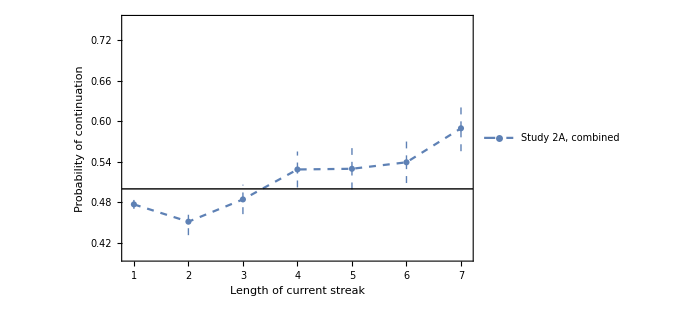
-Graphics-Rao and Hastie 2023

```mathematica
plot=Labeled[ListLinePlot[{
Rao2AContProbByStr
},
PlotStyle->{Dashed,Normal},
PlotMarkers->Automatic,
PlotRange->{{0.9,7.1},{.4,0.75}},
PlotLegends->Placed[{"Study 2A, combined"},{0.25,0.9}],

Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{Style["Probability of continuation",FontSize->14],None},{Style["Length of current streak",FontSize->14],None}},
ImageSize->500,
Epilog->Line[{{0,0.5},{10,0.5}}]
],
Style["Rao and Hastie 2023",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/Rao_overall_cont_rates.pdf",plot];
```

Adding Aspaouhova2009 data (from their Table 6):

```mathematica
(*import means by hand:*)
rawTreat1 = {0.7514,-0.1214,-0.5942,-0.6304,3.288,2.5924,9.2174,8.9348};
treat1 = (50+rawTreat1)/100;
rawTreat2 = {1.7957,2.1667,-2.2373,-4.6522,-2.4239,-2.9348,-0.5652,-1.1304};
treat2 = (50+rawTreat2)/100;

combinedAsparouhova=Mean[{treat1,treat2}]
```

{0.512736,0.510227,0.485843,0.473587,0.504321,0.498288,0.543261,0.539022}

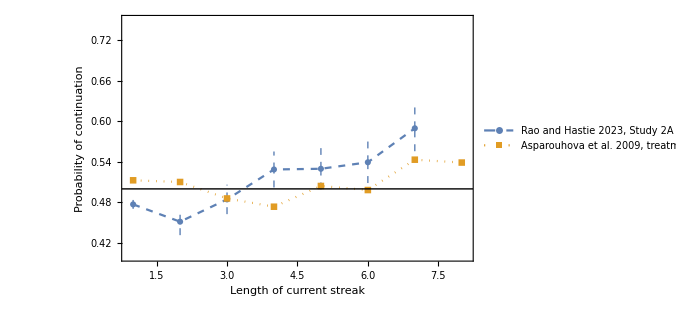
-Graphics-Empirical Data

```mathematica
plot=Labeled[ListLinePlot[{
Rao2AContProbByStr,
combinedAsparouhova
},
PlotStyle->{Dashed,Dotted},
PlotMarkers->Automatic,
PlotRange->{{0.9,8.1},{.4,0.75}},
PlotLegends->Placed[{"Rao and Hastie 2023, Study 2A (combined)", "Asparouhova et al. 2009, treatments 1 and 2"},{0.35,0.9}],

Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{Style["Probability of continuation",FontSize->14],None},{Style["Length of current streak",FontSize->14],None}},
ImageSize->500,
Epilog->Line[{{0,0.5},{10,0.5}}]
],
Style["Empirical Data",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```

```mathematica
Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/Rao_Asparouhova_combined.pdf",plot];
```

#### Study 2A: *separated* mean probability of continuation

```mathematica
(*get all entries from study 2A*)
study2A = rawData[[4]];
(*print positions for each datapoint*)
Table[Print[{ind,study2A[[1,ind]]}],{ind,Length[study2A[[1]]]}];

(*put all datapoints in a list*)
allRao2AData = study2A[[2;;]];
```

{1,study}

{2,participant_id}

{3,generator}

{4,rate}

{5,trial}

{6,sequence}

{7,type}

{8,terminal_streak_length}

{9,prediction_raw}

{10,prediction_recode}

```mathematica
(*separate data into 3 treatments*)
Rao2AAnalyst = Select[allRao2AData,#[[3]]=="analyst"&];
Rao2AStock = Select[allRao2AData,#[[3]]=="stock"&];
Rao2ABingo = Select[allRao2AData,#[[3]]=="bingo"&];
```

{{1,0.4640.0100.010},{2,0.4810.0330.033},{3,0.520.040.04},{4,0.530.040.04},{5,0.570.050.05},{6,0.580.050.05},{7,0.640.060.06}}

{{1,0.4730.0130.013},{2,0.450.040.04},{3,0.490.040.04},{4,0.600.050.05},{5,0.600.060.06},{6,0.620.060.06},{7,0.700.060.06}}

{{1,0.4920.0110.011},{2,0.4250.0350.035},{3,0.4440.0340.034},{4,0.460.050.05},{5,0.430.050.05},{6,0.430.050.05},{7,0.460.060.06}}

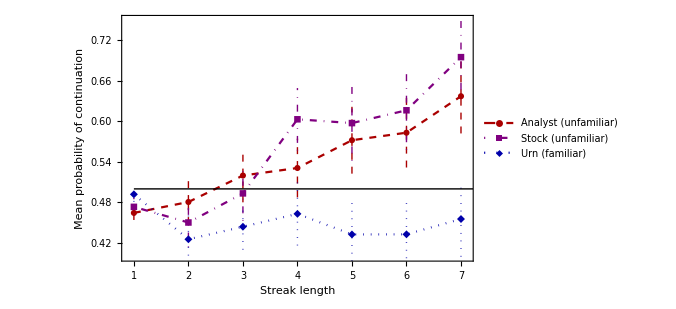
-Graphics-Rao and Hastie 2023

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation FOR EACH TREATMENT:*)

(*analyst:*)
Rao2AAnalystContProbByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Rao2AAnalyst,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]

(*stock:*)
Rao2AStockContProbByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Rao2AStock,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]

(*bingo:*)
Rao2ABingoContProbByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Rao2ABingo,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]


(*plot results:*)
(*NOTE: bars are 80%-confidence intervals*)

plot=Labeled[
ListLinePlot[{Rao2AAnalystContProbByStr,Rao2AStockContProbByStr,Rao2ABingoContProbByStr},
PlotStyle->{{Darker[Red],Dashed},{Purple,DotDashed},{Darker[Blue],Dotted}},
PlotMarkers->Automatic,
PlotRange->{{0.9,7.1},{.4,0.75}},
PlotLegends->Placed[{"Analyst (unfamiliar)","Stock (unfamiliar)","Urn (familiar)"},{0.2,0.9}],
Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak length",FontSize->12],None}},
ImageSize->500,
Epilog->{Line[{{1,0.5},{8,0.5}}]}
],
Style["Rao and Hastie 2023",FontFamily->"Arial",FontWeight->Bold,FontSize->14],Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/Rao_separated_cont_probs.pdf",plot];
```

Asparouhova et al 2009’s data (from Table 6):

```mathematica
(*import means by hand:*)
rawTreat1 = {0.7514,-0.1214,-0.5942,-0.6304,3.288,2.5924,9.2174,8.9348};
treat1 = (50+rawTreat1)/100;
rawTreat2 = {1.7957,2.1667,-2.2373,-4.6522,-2.4239,-2.9348,-0.5652,-1.1304};
treat2 = (50+rawTreat2)/100;
```

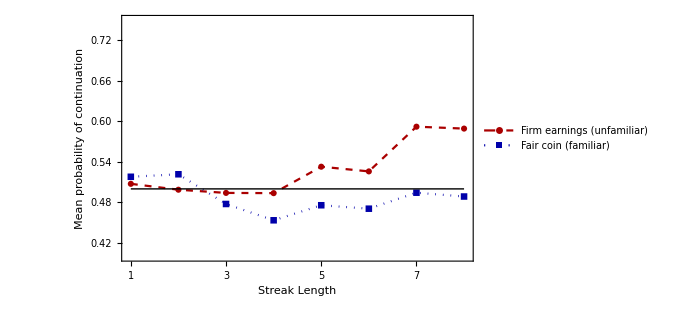
-Graphics-Asparouhova et al. 2009

```mathematica
plot = Labeled[ListLinePlot[
{treat1,treat2},
PlotRange->{{0.95,8.05},{0.4,0.75}},
PlotStyle->{{Darker[Red],Dashed},{Darker[Blue],Dotted}},
PlotMarkers->Automatic,
PlotLegends->Placed[{
"Firm earnings (unfamiliar)", 
"Fair coin (familiar)"},{0.25,0.9}],
Frame->{{True,False},{True,False}},FrameLabel->{{Style["Mean probability of continuation",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
FrameTicks->{{Automatic,None},{Range[8],None}},Epilog->{Line[{{1,0.5},{8,0.5}}]},
ImageSize->500],
Style["Asparouhova et al. 2009",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];
Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/Asparouhova_separated_cont_probs.pdf",plot];
```

#### Study 2B vs 2A: estimates vs binary predictions

```mathematica
(*get all entries from study 2A*)
study2A = rawData[[4]];
(*restrict to datapoints:*)
allRao2AData = study2A[[2;;]];
(*print positions for each datapoint*)
Table[Print[{ind,study2A[[1,ind]]}],{ind,Length[study2A[[1]]]}];
```

{1,study}

{2,participant_id}

{3,generator}

{4,rate}

{5,trial}

{6,sequence}

{7,type}

{8,terminal_streak_length}

{9,prediction_raw}

{10,prediction_recode}

```mathematica
(*get all entries from study 2B*)
study2B = rawData[[5]];
(*restrict to datapoints*)
allRao2BData = study2B[[2;;]];
(*print positions for each datapoint*)
Table[Print[{ind,study2B[[1,ind]]}],{ind,Length[study2B[[1]]]}];
```

{1,study}

{2,participant_id}

{3,generator}

{4,rate}

{5,trial}

{6,sequence}

{7,type}

{8,terminal_streak_length}

{9,prediction_raw}

{10,prediction_recode}

```mathematica
(*get mean probability of continuation for all of 2A:*)
all2AProbs = #[[-1]]&/@allRao2AData;
{Mean[all2AProbs],MeanCI[all2AProbs]}

(*get mean rate of predicting continuation for all of 2B:*)
all2BPreds = #[[-1]]&/@allRao2BData;
{Mean[all2BPreds],MeanCI[all2BPreds]}
```

{49.1574,{48.2668,50.048}}

{0.399963,{0.386914,0.413012}}

{{1,0.4770.0070.007},{2,0.4510.0200.020},{3,0.4840.0220.022},{4,0.5290.0270.027},{5,0.5300.0310.031},{6,0.5390.0310.031},{7,0.5900.0340.034}}

{{1,0.4230.0160.016},{2,0.270.050.05},{3,0.240.050.05},{4,0.320.050.05},{5,0.410.060.06},{6,0.430.060.06},{7,0.460.060.06}}

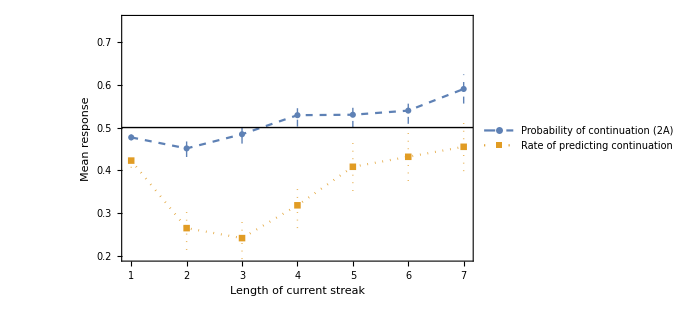
-Graphics-Rao and Hastie 2023, Study 2A vs. 2B

```mathematica
(*get mean PROBABILITY by streak length, as above*)
Rao2AContProbByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[allRao2AData,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]

(*get mean PREDICTION RATE by streak length*)

Rao2BContPredRateByStr=Table[
(*set the streak length*)
strLength = indStrLength;
(*get datapoints with a given streak length*)
selected2B =Select[allRao2BData,#[[8]]==strLength&];
(*get all predictions (1 for continuation, 0 for switch*)
selected2BPreds = #[[-1]]&/@selected2B;

(*record results*)
{strLength,aroundCI[selected2BPreds]}
,{indStrLength,7}]


(*plot results*)
plot = Labeled[
ListLinePlot[{Rao2AContProbByStr,Rao2BContPredRateByStr},
PlotStyle->{Dashed,Dotted},
PlotMarkers->Automatic,
PlotRange->{{0.95,7.05},{.2,0.75}},
PlotLegends->Placed[{"Probability of continuation (2A)","Rate of predicting continuation (2B)"},{0.3,0.85}],

Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{Style["Mean response",FontSize->14],None},{Style["Length of current streak",FontSize->14],None}},
ImageSize->500,
Epilog->Line[{{0,0.5},{8,0.5}}]],
Style["Rao and Hastie 2023, Study 2A vs. 2B",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]

Export["/Users/kevin/Dropbox/Documents/1. Professional/0. Projects/2023/2. GF/Writing/23.9, GF/images/Rao_est_pred.pdf",plot];
```

What about WITHIN the probability-estimate data?

```mathematica
(*get the proportion predicting continuations in estimation by dichotomizing their estimates:*)
all2ADichPreds = DeleteCases[all2AProbs/.{x_/;x>50->1,y_/;y<50->0},50.];
Mean[all2ADichPreds]//N
Mean[all2AProbs]/100

(*test whether that proportion is below mean probability estimate*)
TTest[{all2AProbs/100,all2ADichPreds},0,{"TestStatistic","PValue","DegreesOfFreedom"},AlternativeHypothesis->"Greater"]
```

0.472021

0.491574

TTest::nortst: At least one of the p-values in {0,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

{1.8191,0.0344883,3726.93}

Break into cases where mean probability is above vs. below 50%.

```mathematica
(*grab (type,strLength) pairs such that mean probability is above 50%:*)
(*make lists for storing each type of pair:*)
above50Pairs={};
below50Pairs={};

(*above 50%:*)
(*grab streak lengths where mean analyst prediction is above 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2AAnalystContProbByStr,#[[2,1]]>0.50&];
(*record pairs:*)
above50Pairs=Join[above50Pairs,{"analyst",#}&/@selectedStreaks];
(*grab streak lengths where mean stock prediction is above 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2AStockContProbByStr,#[[2,1]]>0.50&];
(*record pairs:*)
above50Pairs=Join[above50Pairs,{"stock",#}&/@selectedStreaks];
(*grab streak lengths where mean bingo prediction is above 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2ABingoContProbByStr,#[[2,1]]>0.50&];
(*record pairs:*)
above50Pairs=Join[above50Pairs,{"bingo",#}&/@selectedStreaks];

(*below 50%*)
(*grab streak lengths where mean analyst prediction is below 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2AAnalystContProbByStr,#[[2,1]]<0.50&];
(*record pairs:*)
below50Pairs=Join[below50Pairs,{"analyst",#}&/@selectedStreaks];

(*grab streak lengths where mean stock prediction is above 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2AStockContProbByStr,#[[2,1]]<0.50&];
(*record pairs:*)
below50Pairs=Join[below50Pairs,{"stock",#}&/@selectedStreaks];

(*grab streak lengths where mean bingo prediction is above 50%:*)
selectedStreaks=#[[1]]&/@Select[Rao2ABingoContProbByStr,#[[2,1]]<0.50&];
(*record pairs:*)
below50Pairs=Join[below50Pairs,{"bingo",#}&/@selectedStreaks];
```

```mathematica
(*make list for data with means above 50:*)
above50Data = {};
(*iterate through above50Pairs to collect datapoints*)
Do[
(*select data that fit each pair in above50Pairs*)
selectedData=Select[allRao2AData,(#[[3]]==indAbove50[[1]]&&#[[8]]==indAbove50[[2]])&];
(*combine the data*)
above50Data = Join[above50Data,selectedData];
(*iterate through pairs*)
,{indAbove50,above50Pairs}
]

(*make list for data with means below 50:*)
below50Data = {};
(*iterate through above50Pairs to collect datapoints*)
Do[
(*select data that fit each pair in above50Pairs*)
selectedData=Select[allRao2AData,(#[[3]]==indBelow50[[1]]&&#[[8]]==indBelow50[[2]])&];
(*combine the data*)
below50Data = Join[below50Data,selectedData];
(*iterate through pairs*)
,{indBelow50,below50Pairs}
]
```

```mathematica
Mean[above50ProbConts=#[[-1]]/100&/@above50Data]
Mean[below50ProbConts=#[[-1]]/100&/@below50Data]
```

0.593916

0.47194

```mathematica
(*above 50 data; delete equal to 50 cases:*)
above50DichData = DeleteCases[above50ProbConts/.{x_/;x>.50->1,y_/;y<.50->0},.50];
(*below 50 data*)
below50DichData = DeleteCases[below50ProbConts/.{x_/;x>.50->1,y_/;y<.50->0},.50];
```

```mathematica
TTest[{above50DichData,above50ProbConts},0,{"TestStatistic","PValue","DegreesOfFreedom"},AlternativeHypothesis->"Greater"]
```

TTest::nortst: At least one of the p-values in {0,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

{2.36337,0.00918946,707.747}

```mathematica
TTest[{below50ProbConts,below50DichData},0,{"TestStatistic","PValue","DegreesOfFreedom"},AlternativeHypothesis->"Greater"]
```

TTest::nortst: At least one of the p-values in {0,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

{3.17983,0.000744291,3013.64}

Plot dichotomized vs probability estimates, for familiar vs unfamiliar:

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation:*)
RaoStockAnalyst2AProbContByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Join[Rao2AStock,Rao2AAnalyst],#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]
```

{{1,0.4690.0080.008},{2,0.4660.0240.024},{3,0.5070.0280.028},{4,0.5660.0320.032},{5,0.580.040.04},{6,0.600.040.04},{7,0.670.040.04}}

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation:*)
RaoStockAnalyst2APredContRateByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Join[Rao2AStock,Rao2AAnalyst],#[[8]]==seqLength&&#[[-1]]!=50&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=Boole[#[[-1]]>50]&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]
```

{{1,0.4340.0190.019},{2,0.460.070.07},{3,0.540.070.07},{4,0.640.060.06},{5,0.650.060.06},{6,0.640.060.06},{7,0.720.060.06}}

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation:*)
RaoBingo2AProbContByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Rao2ABingo,#[[8]]==seqLength&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=#[[-1]]/100&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]
```

{{1,0.4920.0110.011},{2,0.4250.0350.035},{3,0.4440.0340.034},{4,0.460.050.05},{5,0.430.050.05},{6,0.430.050.05},{7,0.460.060.06}}

```mathematica
(*get a list of pairs of the sequence length and the mean probability of continuation:*)
RaoBingo2APredContRateByStr = Table[
(*set sequence length*)
seqLength = indSeqLength;

(*grab datapoints with terminal streak of length seqLength*)
selectedEntries= Select[Rao2ABingo,#[[8]]==seqLength&&#[[-1]]!=50&];

(*get probabilities of continuing in those datapoints, divide by 100*)
selectedProbConts=Boole[#[[-1]]>50]&/@selectedEntries;

(*record sequence length and 80%-confidence interval for probability of continuing*)
{seqLength,aroundCI[selectedProbConts,0.8]}

,{indSeqLength,7}]
```

{{1,0.4630.0260.026},{2,0.330.090.09},{3,0.320.090.09},{4,0.430.090.09},{5,0.360.090.09},{6,0.360.090.09},{7,0.420.090.09}}

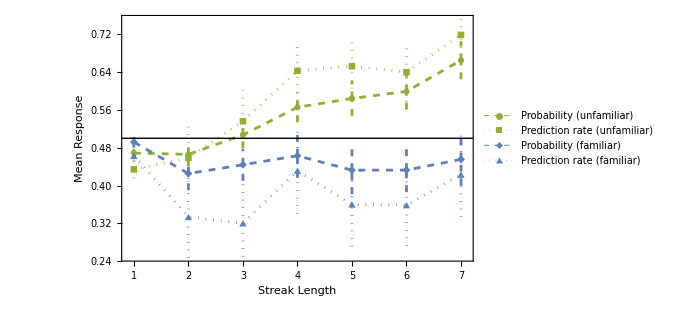
-Graphics-Rao and Hastie 2023, dichotomized predictions vs. probabilities

```mathematica
plot=Labeled[ListLinePlot[{
RaoStockAnalyst2AProbContByStr, 
RaoStockAnalyst2APredContRateByStr,
RaoBingo2AProbContByStr,
RaoBingo2APredContRateByStr
},
PlotStyle->{{Dashed,RGBColor[0.560181, 0.691569, 0.194885],Thickness[0.004]},{Dotted,RGBColor[0.560181, 0.691569, 0.194885],Thickness[0.004]},{Dashed,Thickness[0.004],RGBColor[0.368417, 0.506779, 0.709798]},{Dotted,Thickness[0.004],RGBColor[0.368417, 0.506779, 0.709798]}},
PlotMarkers->Automatic,
PlotRange->{{0.9,7.1},{.25,0.75}},
PlotLegends->Placed[
{"Probability (unfamiliar)",
"Prediction rate (unfamiliar)",
"Probability (familiar)",
"Prediction rate (familiar)"}
,{0.23,0.85}],

Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{Style["Mean Response",FontSize->12],None},{Style["Streak Length",FontSize->12],None}},
ImageSize->500,
Epilog->Line[{{0,0.5},{10,0.5}}]
],
Style["Rao and Hastie 2023, dichotomized predictions vs. probabilities",FontFamily->"Arial",FontWeight->Bold,FontSize->14],
Top];

Print[plot]
```